# The superfluid boson singlet state of the gauge-covariant spinor field on the 3+1 manifold of the Lorentz super-loop

## PROJECT spacetimes, folder Revision_HS_CJT_and_Kohn-Sham. The notebook superfluid.nb, prepared for Patrick Lee Nash, Ph.D.

This notebook is the Wolfram Language companion of the manuscript of the solution in the same folder, written so that a first-year graduate student in physics can follow every step. It states the problem and the conventions, defines every object that a computation needs, writes out the equations that can be executed, and executes them: the algebra of the manifold M31 and of the Lorentz super-loop, the spinor field and the gauge group GEE with its covariant derivatives, the field equations and their analytic solutions, the condensation of the spinor field into the superfluid boson singlet state by the methods of Hubbard and Stratonovich (HS), of Kohn and Sham (KS) and of Cornwall, Jackiw and Tomboulis (CJT), the effective Lagrangians and the Mexican hat, the breaking of the symmetry and the masses of the gauge bosons, the surviving symmetry with its massless photon, and the dynamics. Every time integration in this notebook is done by the method IDA of the function NDSolve; no fixed-step integrator (such as the fourth-order Runge-Kutta method) is used anywhere.

How to use it. Open the notebook in Wolfram (version 15 or later; it was evaluated with Wolfram 15.0.1) and choose Evaluation > Evaluate Notebook. The cells are evaluated in order. Nothing outside this notebook is read: every definition and every program is inside it. Every check prints one line that begins with PASS or FAIL, and the last chapter lists all checks.

How to read it. A text cell explains, in words and formulas, what the next input cell does and why. Inside the code, comments (* like this *) explain each step, and every symbol of the code that stands for an object of the physics has a comment with its printed name and its meaning the first time it is defined. A symbol of the printed text with the suffix LL is taken unchanged from the earlier work of the project on the super-loop; a symbol with the suffix SF is introduced by this solution.

The checks and their counterparts. Every computation of this notebook is also done by a program in Rust and by a program in Python, in the folders rust/ and python/ of the folder of the solution; users without a Wolfram license can follow the solution with those programs. Every check of this notebook carries the identifier of the same check in the Rust program with the prefix W (for example WA-3 is the check A-3 of the Rust program sf_part1 and of the Python program sf_part1.py), and the line that it prints names both counterparts. The notebook computes its values itself, by methods of the Wolfram Language (exact arithmetic where the Rust program computes in floating point, symbolic derivatives where it differentiates automatically, the solvers of the Wolfram Language where it uses its own); the numbers agree with those of the two programs within the tolerances stated in each check.

## 0. The register of the checks

The next cell defines the functions that record and print a check. check[id, text, dev, tol, rust, python] records a numerical check: it passes when the measured deviation dev is at most the tolerance tol; rust and python are the identifiers of the same check in the Rust and in the Python program. checkTrue[id, text, ok, detail, rust, python] records a check that is decided by facts (a count, an exact identity), with a short detail. Both append an association to the list SFNB`Test`$Results, the register of all checks of this notebook, and print one line. The function sci writes a number with four significant digits in the form 2.857e-8, as the reports of the Rust and the Python programs do.

```mathematica
(* the register of the checks of this notebook: one association per check, in the order of evaluation *)
SFNB`Test`$Results = {};
(* sci[x]: the number x with four significant digits, written as mantissa e exponent (for example 2.857e-8) *)
sci[x_?NumericQ] := Module[{y = N[x], e, m},
   If[y == 0, Return["0", Module]];
   e = Floor[Log10[Abs[y]]]; m = Round[y/10.^e, 0.001];
   If[Abs[m] >= 10, m = m/10; e = e + 1];
   ToString[NumberForm[m, {4, 3}]] <> "e" <> ToString[e]];
(* checkHook[]: called after every check; it does nothing here (a dry run of the code without the front end
   uses it to print the computing time of each check) *)
checkHook[] := Null;
(* check[id, text, dev, tol, rust, python]: a numerical check, passed when dev <= tol *)
check[id_String, text_String, dev_?NumericQ, tol_?NumericQ, rust_String, python_String] := Module[{ok = TrueQ[N[dev] <= tol]},
   AppendTo[SFNB`Test`$Results, <|"id" -> id, "pass" -> ok, "deviation" -> N[dev], "tolerance" -> N[tol],
      "text" -> text, "rust" -> rust, "python" -> python|>];
   Print[If[ok, "PASS ", "FAIL "], id, "  deviation ", sci[dev], " (tolerance ", sci[tol], "): ", text,
     "   [the same check: Rust ", rust, ", Python ", python, "]"];
   checkHook[]; ok];
(* checkTrue[id, text, ok, detail, rust, python]: a check decided by facts; detail states them *)
checkTrue[id_String, text_String, ok_, detail_String, rust_String, python_String] := Module[{pass = TrueQ[ok]},
   AppendTo[SFNB`Test`$Results, <|"id" -> id, "pass" -> pass, "deviation" -> Missing["NotNumerical"], "tolerance" -> Missing["NotNumerical"],
      "text" -> text <> " [" <> detail <> "]", "rust" -> rust, "python" -> python|>];
   Print[If[pass, "PASS ", "FAIL "], id, "  ", text, " [", detail, "]   [the same check: Rust ", rust, ", Python ", python, "]"];
   checkHook[]; pass];
```

## Part I. The manifold M31, the spinor field, GEE, the field equations and four analytic solutions

Part I treats items 1 to 5 of the problem (Sections 1 to 7 of the manuscript): the manifold M31 of the Lorentz super-loop, the spinor fields on it and the Dirac field, the gauge group GEE and its covariant derivatives, the Lagrangian with its field equations, and analytic solutions of four simple cases. Its checks are those of the Python program sf_part1.py, which repeats a part of the checks of the Rust program sf_part1; the random test values of this notebook come from the generator of the Wolfram Language with the seed 20261121, so they differ from those of the two programs, as theirs differ from each other.

## I.1 Conventions, units and the common objects

Units. Planck's constant and the speed of light are 1; energies, masses and momenta are measured in units of the momentum cutoff Λ_LL==1, lengths and times in units of 1/Λ_LL. The mass of the spinor field is m_LL==0.2.

Indices. p,p' run over the four coordinates of M31 (0 is the time), j,j',j'' over the three space coordinates, ι,ι',ι'' over the three directions of isospin (an internal direction, not a direction in space), and c,c' over the eight components of the spinor field. The letter i is always the imaginary unit. The Minkowski metric is η_(p p')^LL==diag(1,-1,-1,-1).

Matrices. σ_0^LL is the 2×2 unit matrix and σ_1^LL,σ_2^LL,σ_3^LL are the Pauli matrices; acting on isospin they are written τ_ι^LL. E_LL==i σ_2^LL. The Dirac matrices are those of the chiral basis, γ_LL^0 with the blocks σ_0^LL off the diagonal and γ_LL^j with the blocks σ_j^LL and -σ_j^LL; γ_LL^ch==i γ_LL^0 γ_LL^1 γ_LL^2 γ_LL^3==diag(-1,-1,1,1), C_LL==i γ_LL^2 γ_LL^0, α_LL^j==γ_LL^0 γ_LL^j and β_LL==γ_LL^0. The spinor field Ψ_LL has eight components: the Dirac index d (four values) and the isospin index s (up, down); a 4×4 Dirac matrix A acts on it as A⊗1_2 and an isospin matrix t as 1_4⊗t. The isospin generators are T_LL^ι==1_4⊗τ_ι^LL/2, the matrices of the three spin-zero pair fields are K_LL^ι==C_LL γ_LL^ch⊗E_LL τ_ι^LL, and the free Dirac Hamiltonian at the momentum (q⃗)_LL is h_LL((q⃗)_LL)==∑_j α_LL^j q_LL^j+β_LL m_LL.

The author's conventions (the Standard Model). The covariant derivative of the Higgs doublet is D_μ^SM Φ^SM==(∂_μ +ig ∑_(a==1)^3 τ^a/2 W_μ^a+i g' Y^SM B_μ)Φ^SM with Y^SM==1/2 and Q^SM==T^(3,SM)+Y^SM; the fields of definite mass are W_μ^±==(W_μ^1∓i W_μ^2)/√2, Z_μ==cos θ_W W_μ^3-sin θ_W B_μ and the photon A_μ==sin θ_W W_μ^3+cos θ_W B_μ, with e==g sin θ_W; with ⟨Φ^SM⟩==(0,v)/√2 the masses are M_W==gv/2 and M_Z==√(g^2+g^(′2)) v/2, and the photon is massless. All GEE covariant derivatives of the solution use the same sign, +i in front of every coupling.

The next cell defines these matrices, the bi-quaternions and bi-octonions of Section I.2, the Lorentz matrices, the spinor matrices and the operators of the Fock space of one point. They are the same objects as those of the Rust library sfcore and of the Python module sfcommon.py, written here with the functions of the Wolfram Language.

```mathematica
(* the mass of the spinor field, m_LL, in units of the cutoff Lambda_LL = 1 *)
mLL = 1/5;
(* sig[[p + 1]] is sigma^LL_p (p = 0, 1, 2, 3): sigma_0 is the 2 x 2 unit matrix, sigma_1, sigma_2, sigma_3 the Pauli matrices *)
sig = {IdentityMatrix[2], PauliMatrix[1], PauliMatrix[2], PauliMatrix[3]};
(* sigbar[[p + 1]] is sigma-bar_p: sigma_0 and -sigma_j, the blocks of the Dirac matrices below the diagonal *)
sigbar = {sig[[1]], -sig[[2]], -sig[[3]], -sig[[4]]};
(* eLL is E_LL = i sigma_2 = {{0, 1}, {-1, 0}} *)
eLL = {{0, 1}, {-1, 0}};
(* etaLL is the Minkowski metric eta^LL = diag(1, -1, -1, -1) *)
etaLL = DiagonalMatrix[{1, -1, -1, -1}];
(* levi[a, b, c] is the Levi-Civita symbol epsilon^LL of the indices 1, 2, 3 *)
levi[a_, b_, c_] := Signature[{a, b, c}];
(* gam[p] is the Dirac matrix gamma^p_LL of the chiral basis: {{0, sigma_p}, {sigmabar_p, 0}} *)
gam[p_Integer] := ArrayFlatten[{{0, sig[[p + 1]]}, {sigbar[[p + 1]], 0}}];
(* gch is the chirality matrix gamma^ch_LL = i gamma^0 gamma^1 gamma^2 gamma^3 *)
gch = I gam[0] . gam[1] . gam[2] . gam[3];
(* cLL is the charge-conjugation matrix C_LL = i gamma^2 gamma^0 *)
cLL = I gam[2] . gam[0];
(* betaLL = gamma^0_LL and alphaLL[j] = gamma^0 gamma^j, the matrices of the Dirac Hamiltonian *)
betaLL = gam[0];
alphaLL[j_Integer] := gam[0] . gam[j];
(* d8[a] = a (x) 1_2 acts on the Dirac index of the eight components (component 2 d + s, d = 0..3, s = 0 up, 1 down) *)
d8[a_] := KroneckerProduct[a, IdentityMatrix[2]];
(* i8[t] = 1_4 (x) t acts on the isospin index *)
i8[t_] := KroneckerProduct[IdentityMatrix[4], t];
(* tLL[iota] is the isospin generator T^iota_LL = 1_4 (x) tau_iota/2 *)
tLL[iota_Integer] := i8[sig[[iota + 1]]/2];
(* kLL[iota] is the pair matrix K^iota_LL = C_LL gamma^ch_LL (x) E_LL tau_iota of the scalar spin-zero pairs *)
kLL[iota_Integer] := KroneckerProduct[cLL . gch, eLL . sig[[iota + 1]]];
(* hLL[q, m] is the free Dirac Hamiltonian h_LL(q) = sum_j alpha^j q_j + beta m on the eight components *)
hLL[q_List, m_] := d8[betaLL m + Sum[alphaLL[j] q[[j]], {j, 3}]];

(* ---- bi-quaternions: a bi-quaternion b = xi_0 e_0 + xi_1 e_1 + xi_2 e_2 + xi_3 e_3 is the list {xi_0, xi_1, xi_2, xi_3} ---- *)
(* qMul is the product of bi-quaternions by the rules (2.1) of the quaternion units *)
qMul[{a0_, a1_, a2_, a3_}, {b0_, b1_, b2_, b3_}] := {a0 b0 - a1 b1 - a2 b2 - a3 b3, a0 b1 + a1 b0 + a2 b3 - a3 b2,
   a0 b2 - a1 b3 + a2 b0 + a3 b1, a0 b3 + a1 b2 - a2 b1 + a3 b0};
(* qBar is the conjugation (the signs of xi_1, xi_2, xi_3 change); qDag the Hermitian conjugation *)
qBar[{a0_, a1_, a2_, a3_}] := {a0, -a1, -a2, -a3};
qDag[x_List] := Conjugate[qBar[x]];
(* qNorm is the complex norm N_LL(b) = sum_p xi_p^2 *)
qNorm[x_List] := Total[x^2];
(* mLLmat[b] is the matrix M_LL(b) = xi_0 sigma_0 - i sum_j xi_j sigma_j of (2.2), and biqOf its inverse map *)
mLLmat[b_List] := b[[1]] sig[[1]] - I (b[[2]] sig[[2]] + b[[3]] sig[[3]] + b[[4]] sig[[4]]);
biqOf[m_] := Join[{Tr[m]/2}, Table[I/2 Tr[sig[[j + 1]] . m], {j, 3}]];

(* ---- bi-octonions: x = a + b e_4 is the pair {a, b} of bi-quaternions ---- *)
(* oMul is the Cayley-Dickson product (2.3): (a + b e4)(c + d e4) = (a c - dbar b) + (d a + b cbar) e4 *)
oMul[{a_, b_}, {c_, d_}] := {qMul[a, c] - qMul[qBar[d], b], qMul[d, a] + qMul[b, qBar[c]]};
(* oUnit[p] is the unit e_p (p = 0..7; e_{4+j} = e_j e_4) *)
oUnit[p_Integer] := If[p < 4, {UnitVector[4, p + 1], {0, 0, 0, 0}}, {{0, 0, 0, 0}, UnitVector[4, p - 3]}];
(* oBar is the conjugation of bi-octonions, oNorm the complex norm N_LL(x) = N_LL(a) + N_LL(b) *)
oBar[{a_, b_}] := {qBar[a], -b};
oNorm[{a_, b_}] := qNorm[a] + qNorm[b];
(* oMax is the largest modulus of the sixteen coefficients: the size of a difference *)
oMax[x_] := Max[Abs[Flatten[x]]];

(* ---- Lorentz transformations and spinor matrices ---- *)
(* expTraceless[x] is exp(X) of a traceless 2 x 2 matrix: cosh(s) 1 + sinh(s)/s X with s^2 = -det X *)
expTraceless[x_] := Module[{s = Sqrt[-Det[x]]}, If[Abs[s] < 10^-8, IdentityMatrix[2] + x + x . x/2,
    Cosh[s] IdentityMatrix[2] + Sinh[s]/s x]];
(* lorentzGenerator[rot, boost] is the matrix M_LL(u) of the Lorentz generator with the rotation parameters rot and the
   rapidities boost: sum_j (boost_j/2 - i rot_j/2) sigma_j *)
lorentzGenerator[rot_List, boost_List] := Sum[(boost[[j]]/2 - I rot[[j]]/2) sig[[j + 1]], {j, 3}];
(* lorentzMatrix[mg] is L_LL(g)_pp' = (1/2) Re tr(sigma_p M sigma_p' M^dag) of (2.10), mg = M_LL(g) *)
lorentzMatrix[mg_] := Table[Re[Tr[sig[[p + 1]] . mg . sig[[q + 1]] . ConjugateTranspose[mg]]]/2, {p, 0, 3}, {q, 0, 3}];
(* sSpin[mg] is the spinor matrix S_LL(g) = diag((M^dag)^-1, M) of (3.7) *)
sSpin[mg_] := ArrayFlatten[{{Inverse[ConjugateTranspose[mg]], 0}, {0, mg}}];
(* sGen[mu] is s_LL(u) = diag(-M(u)^dag, M(u)), the action of a Lorentz generator on the Dirac index *)
sGen[mu_] := ArrayFlatten[{{-ConjugateTranspose[mu], 0}, {0, mu}}];
(* randUnitBiq[] is the matrix of a random unit bi-quaternion: exp of a random Lorentz generator *)
randUnitBiq[amp_ : 1.5] := expTraceless[lorentzGenerator[amp RandomReal[{-1, 1}, 3], amp RandomReal[{-1, 1}, 3]]];

(* ---- the Fock space of one point: 2^n states, the occupation of mode k is the bit k of the state number ---- *)
(* fockOps[n] are the annihilation operators c_0 .. c_(n-1) as sparse matrices, with the sign (-1)^(number of occupied
   modes below k) of the ordering of Jordan and Wigner *)
fockOps[n_Integer] := Table[SparseArray[Flatten[Table[If[BitGet[b, k] == 1,
       {BitXor[b, 2^k] + 1, b + 1} -> (-1)^DigitCount[BitAnd[b, 2^k - 1], 2, 1], Nothing], {b, 0, 2^n - 1}]], {2^n, 2^n}],
   {k, 0, n - 1}];
(* the seed of the random test values of this notebook *)
SeedRandom[20261121];
Print["the common objects are defined; m_LL = ", mLL];
```

the common objects are defined; m_LL = 1/5

The first check of the conventions: the mass matrix of the gauge fields of the Standard Model, computed from the covariant derivative (1.1) with +ig, has the eigenvalues 0 (the photon), M_W^2 (twice) and M_Z^2, with the eigenvectors A_μ and Z_μ of the text. The kinetic term (D_μ⟨Φ^SM⟩)^†D^μ⟨Φ^SM⟩ of the constant vacuum is the quadratic form 1/2 ∑_ab M_ab V_μ^a V^(b,μ) of the four fields (W^1,W^2,W^3,B); the cell computes M exactly, with symbolic couplings, and diagonalizes it. The Rust program sf_part1 checks the same statement with numbers through the four eigenvectors, and the Python program sf_part1.py through the eigenvalues computed by LAPACK (check SM-1 of both); the same computation for the superfluid is the mass matrix (14.3) of Part IV.

```mathematica
(* gSM, gpSM: the couplings g and g' of SU(2)_L and U(1)_Y; vSM: the vacuum value v (all positive symbols) *)
Clear[gSM, gpSM, vSM];
(* phiSM: the vacuum <Phi^SM> = (0, v)/sqrt2 of the Higgs doublet *)
phiSM = {0, vSM/Sqrt[2]};
(* xSM[a]: the vector X_a with D_mu <Phi> = sum_a V^a_mu X_a for the fields V = (W^1, W^2, W^3, B):
   i g tau_a/2 <Phi> for a = 1, 2, 3 and i g' Y <Phi> (Y = 1/2) for B *)
xSM = Join[Table[(I gSM/2) sig[[a + 1]] . phiSM, {a, 3}], {(I gpSM/2) phiSM}];
(* the mass matrix M_ab = 2 Re(X_a^dag X_b): (D <Phi>)^dag (D <Phi>) = (1/2) sum_ab M_ab V^a V^b *)
mSM = Table[2 ComplexExpand[Re[Conjugate[xSM[[a]]] . xSM[[b]]]], {a, 4}, {b, 4}];
(* the predicted eigenvalues: 0, M_W^2 = (g v/2)^2 twice, M_Z^2 = (g^2 + g'^2) v^2/4; they are the eigenvalues exactly when
   the characteristic polynomial det(M - lam 1) equals the product of the factors (lam - eigenvalue) *)
evSMpred = {0, (gSM vSM/2)^2, (gSM vSM/2)^2, (gSM^2 + gpSM^2) vSM^2/4};
charSM = Expand[CharacteristicPolynomial[mSM, lam] - Product[lam - ev, {ev, evSMpred}]];
(* the photon A = sin(thetaW) W^3 + cos(thetaW) B with tan(thetaW) = g'/g is the null vector *)
photonSM = {0, 0, gpSM, gSM}/Sqrt[gSM^2 + gpSM^2];
Print["the mass matrix of (W1, W2, W3, B): ", MatrixForm[mSM]];
checkTrue["WSM-1", "Standard Model with +i g: the eigenvalues of the mass matrix are 0, M_W^2 (twice), M_Z^2, and the photon sin(thetaW) W^3 + cos(thetaW) B is massless",
  charSM === 0 && Simplify[mSM . photonSM] === {0, 0, 0, 0}, "exact, with symbolic g, g', v",
  "SM-1", "SM-1"];
```

the mass matrix of (W1, W2, W3, B): ((gSM^2 vSM^2)/4 | 0 | 0 | 0
0 | (gSM^2 vSM^2)/4 | 0 | 0
0 | 0 | (gSM^2 vSM^2)/4 | -1/4 gpSM gSM vSM^2
0 | 0 | -1/4 gpSM gSM vSM^2 | (gpSM^2 vSM^2)/4)

PASS WSM-1  Standard Model with +i g: the eigenvalues of the mass matrix are 0, M_W^2 (twice), M_Z^2, and the photon sin(thetaW) W^3 + cos(thetaW) B is massless [exact, with symbolic g, g', v]   [the same check: Rust SM-1, Python SM-1]

## I.2 The manifold M31 of the Lorentz super-loop (item 1)

Bi-quaternions. A bi-quaternion is b==∑_(p==0)^3 ξ_p^LL(b) e_p with four complex coefficients and the units e_0==1,e_1,e_2,e_3, multiplied by the rules of the quaternions, e_j^2==-1, e_1 e_2==-e_2 e_1==e_3 and cyclically. The conjugation b̄ changes the signs of the coefficients of e_1,e_2,e_3, the complex conjugation b^* conjugates every coefficient, and b^†==(b̄)^*. The complex norm N_LL(b)==∑_p ξ_p^LL(b)^2 satisfies b b̄==N_LL(b) e_0 and N_LL(b b')==N_LL(b)N_LL(b'). The matrix M_LL(b)==ξ_0^LL σ_0^LL-i ∑_j ξ_j^LL σ_j^LL is multiplicative, has the determinant N_LL(b), satisfies M_LL(b^†)==M_LL(b)^†, and every complex 2×2 matrix is the matrix of exactly one bi-quaternion; the unit bi-quaternions (N_LL==1) are therefore the group SL(2,ℂ).

Bi-octonions and the super-loop. A bi-octonion is x==a+b e_4 with two bi-quaternions, multiplied by the rule of Cayley and Dickson

(a+b e_4)(c+d e_4)==(ac-d̄ b)+(da+b c̄) e_4,

with the eight units e_0,…,e_3,e_4 and e_(4+j)==e_j e_4. The norm is multiplicative, N_LL(xy)==N_LL(x)N_LL(y), and x x̄==N_LL(x)e_0. The product is not associative ((e_1 e_2)e_4-e_1(e_2 e_4)==2 e_7), but it is alternative, (xx)y==x(xy), and satisfies the three Moufang identities (zxz)y==z(x(zy)), y(zxz)==((yz)x)z and (zx)(yz)==(z(xy))z. The unit bi-octonions form the Lorentz super-loop 𝕃_LL, a Moufang loop of real dimension 14 that contains SL(2,ℂ).

The next cell checks these rules exactly: bi-octonions with small integer (Gaussian integer) coefficients are multiplied in exact arithmetic, so every identity must hold with the deviation exactly 0. Of the 343 ordered triples of imaginary units, 168 have a nonzero associator: a triple with two equal members has none (alternativity), and of the 210 triples of distinct units a triple has none exactly when its third unit is plus or minus the product of the first two, which leaves 210 - 42 = 168.

```mathematica
(* A-2: the rules of the eight units: e_p^2 = -1, e_p e_q = -e_q e_p (p != q, both >= 1), e_j e_4 = e_(4+j) *)
dA2 = Max[Join[
    Table[oMax[oMul[oUnit[p], oUnit[p]] + oUnit[0]], {p, 1, 7}],
    Flatten[Table[If[p != q, oMax[oMul[oUnit[p], oUnit[q]] + oMul[oUnit[q], oUnit[p]]], 0], {p, 1, 7}, {q, 1, 7}]],
    Table[oMax[oMul[oUnit[j], oUnit[4]] - oUnit[4 + j]], {j, 1, 3}]]];
check["WA-2", "bi-octonion units: e_p^2 = -1, e_p e_q = -e_q e_p, e_j e_4 = e_(4+j) (exact)", dA2, 0, "A-2", "A-2"];
(* rintBio[] is a random bi-octonion with Gaussian-integer coefficients between -3 and 3 *)
rintBio[] := {RandomInteger[{-3, 3}, 4] + I RandomInteger[{-3, 3}, 4], RandomInteger[{-3, 3}, 4] + I RandomInteger[{-3, 3}, 4]};
(* A-3 to A-6 on 200 random triples (x, y, z), in exact arithmetic *)
{dA3, dA4, dA5, dA6} = {0, 0, 0, 0};
Do[Module[{x = rintBio[], y = rintBio[], z = rintBio[], zxz},
   dA3 = Max[dA3, Abs[oNorm[oMul[x, y]] - oNorm[x] oNorm[y]]];
   dA4 = Max[dA4, oMax[oMul[x, oBar[x]] - oNorm[x] oUnit[0]]];
   dA5 = Max[dA5, oMax[oMul[oMul[x, x], y] - oMul[x, oMul[x, y]]], oMax[oMul[oMul[y, x], x] - oMul[y, oMul[x, x]]]];
   zxz = oMul[oMul[z, x], z];
   dA6 = Max[dA6, oMax[oMul[zxz, y] - oMul[z, oMul[x, oMul[z, y]]]], oMax[oMul[y, zxz] - oMul[oMul[oMul[y, z], x], z]],
     oMax[oMul[oMul[z, x], oMul[y, z]] - oMul[oMul[z, oMul[x, y]], z]]]], {200}];
check["WA-3", "N(xy) = N(x) N(y), 200 random Gaussian-integer bi-octonions (exact)", dA3, 0, "A-3", "A-3"];
check["WA-4", "x xbar = N(x) e_0 (exact)", dA4, 0, "A-4", "A-4"];
check["WA-5", "alternativity (xx)y = x(xy), (yx)x = y(xx) (exact)", dA5, 0, "A-5", "A-5"];
check["WA-6", "the three Moufang identities (exact)", dA6, 0, "A-6", "A-6"];
(* A-7: the associators of the 343 ordered triples of imaginary units, and (e1 e2) e4 - e1 (e2 e4) = 2 e7 *)
nonzeroAssociators = Count[Flatten[Table[oMax[oMul[oMul[oUnit[p], oUnit[q]], oUnit[r]] - oMul[oUnit[p], oMul[oUnit[q], oUnit[r]]]],
      {p, 1, 7}, {q, 1, 7}, {r, 1, 7}]], v_ /; v > 0];
a124 = oMul[oMul[oUnit[1], oUnit[2]], oUnit[4]] - oMul[oUnit[1], oMul[oUnit[2], oUnit[4]]];
checkTrue["WA-7", "168 of the 343 triples of imaginary units have a nonzero associator; (e1 e2) e4 - e1 (e2 e4) = 2 e7",
  nonzeroAssociators == 168 && oMax[a124 - 2 oUnit[7]] == 0, ToString[nonzeroAssociators] <> " nonzero", "A-7", "A-7"];
```

PASS WA-2  deviation 0 (tolerance 0): bi-octonion units: e_p^2 = -1, e_p e_q = -e_q e_p, e_j e_4 = e_(4+j) (exact)   [the same check: Rust A-2, Python A-2]

PASS WA-3  deviation 0 (tolerance 0): N(xy) = N(x) N(y), 200 random Gaussian-integer bi-octonions (exact)   [the same check: Rust A-3, Python A-3]

PASS WA-4  deviation 0 (tolerance 0): x xbar = N(x) e_0 (exact)   [the same check: Rust A-4, Python A-4]

PASS WA-5  deviation 0 (tolerance 0): alternativity (xx)y = x(xy), (yx)x = y(xx) (exact)   [the same check: Rust A-5, Python A-5]

PASS WA-6  deviation 0 (tolerance 0): the three Moufang identities (exact)   [the same check: Rust A-6, Python A-6]

PASS WA-7  168 of the 343 triples of imaginary units have a nonzero associator; (e1 e2) e4 - e1 (e2 e4) = 2 e7 [168 nonzero]   [the same check: Rust A-7, Python A-7]

The manifold M31 and its Lorentz group. M31 is the real vector space of the Hermitian bi-quaternions x==x_LL^0 e_0+i ∑_j x_LL^j e_j; their matrices M_LL(x)==∑_p x_LL^p σ_p^LL are the Hermitian 2×2 matrices, and the norm N_LL(x)==(x_LL^0)^2-∑_j (x_LL^j)^2 is the Minkowski interval. A unit bi-quaternion g acts by x↦gx g^†; this keeps M31 and the interval, so it is a Lorentz transformation, with the real matrix

L_LL(g)_(p p')==1/2 Re tr(σ_p^LL M_LL(g) σ_p'^LL M_LL(g)^†),

which is proper and orthochronous (L^T ηL==η, det L==1, L_00≥1) and multiplicative, with L_LL(-g)==L_LL(g): SL(2,ℂ) is the double cover of the proper orthochronous Lorentz group. The next cell checks the properties of M_LL exactly (with Gaussian-integer coefficients) and those of L_LL with 200 random unit bi-quaternions in floating point. A spinor charge of the super-loop is a bi-octonion b e_4; by the product rule the super-loop acts on it as (b e_4)g==(b ḡ)e_4 and g(b e_4)==(bg)e_4, and the isospin v acts as (v((b e_4)e_4))(ē)_4==(vb)e_4; the last check of the cell verifies these three rules exactly.

```mathematica
(* A-8: M(bb') = M(b) M(b'), det M(b) = N(b), M(b^dag) = M(b)^dag, and the inverse map, 200 random Gaussian-integer pairs *)
rintBiq[] := RandomInteger[{-3, 3}, 4] + I RandomInteger[{-3, 3}, 4];
dA8 = Max[Table[Module[{a = rintBiq[], b = rintBiq[]},
     Max[Abs[Flatten[mLLmat[qMul[a, b]] - mLLmat[a] . mLLmat[b]]], Abs[Det[mLLmat[a]] - qNorm[a]],
       Abs[Flatten[mLLmat[qDag[a]] - ConjugateTranspose[mLLmat[a]]]], Abs[biqOf[mLLmat[a]] - a]]], {200}]];
check["WA-8", "M(bb') = M(b)M(b'), det M = N, M(b^dag) = M(b)^dag, inverse map (exact)", dA8, 0, "A-8", "A-8"];
(* A-10b, c, d: the Lorentz matrices of 200 random unit bi-quaternions (floating point) *)
{dA10b, dA10d, l00ok} = {0., 0., True};
Do[Module[{mg = randUnitBiq[], mh = randUnitBiq[], lg, lh},
   lg = lorentzMatrix[mg]; lh = lorentzMatrix[mh];
   dA10b = Max[dA10b, Max[Abs[Transpose[lg] . etaLL . lg - etaLL]], Abs[Det[lg] - 1]];
   dA10d = Max[dA10d, Max[Abs[lorentzMatrix[mg . mh] - lg . lh]], Max[Abs[lorentzMatrix[-mg] - lg]]];
   l00ok = l00ok && lg[[1, 1]] >= 1 - 10^-12], {200}];
check["WA-10b", "L^T eta L = eta and det L = 1 (200 random unit g)", dA10b, 10^-10, "A-10b", "A-10b"];
checkTrue["WA-10c", "L_00 >= 1: orthochronous", l00ok, "200 random unit g", "A-10c", "A-10c"];
check["WA-10d", "L(gh) = L(g) L(h) and L(-g) = L(g) (200 random pairs)", dA10d, 10^-10, "A-10d", "A-10d"];
(* A-12: the spinor charges b e4 under the multiplications of the super-loop (exact): (b e4) g = (b gbar) e4,
   g (b e4) = (b g) e4, and the isospin (g ((b e4) e4)) e4bar = (g b) e4 *)
z4 = {0, 0, 0, 0};
dA12 = Max[Table[Module[{b = rintBiq[], g = rintBiq[], be4, gq, iso},
     be4 = {z4, b}; gq = {g, z4};
     iso = oMul[oMul[gq, oMul[be4, oUnit[4]]], oBar[oUnit[4]]];
     Max[oMax[oMul[be4, gq] - {z4, qMul[b, qBar[g]]}], oMax[oMul[gq, be4] - {z4, qMul[b, g]}], oMax[iso - {z4, qMul[g, b]}]]], {200}]];
check["WA-12", "spinor charges under the super-loop multiplications (exact)", dA12, 0, "A-12", "A-12"];
```

PASS WA-8  deviation 0 (tolerance 0): M(bb') = M(b)M(b'), det M = N, M(b^dag) = M(b)^dag, inverse map (exact)   [the same check: Rust A-8, Python A-8]

PASS WA-10b  deviation 4.885e-15 (tolerance 1.000e-10): L^T eta L = eta and det L = 1 (200 random unit g)   [the same check: Rust A-10b, Python A-10b]

PASS WA-10c  L_00 >= 1: orthochronous [200 random unit g]   [the same check: Rust A-10c, Python A-10c]

PASS WA-10d  deviation 5.329e-15 (tolerance 1.000e-10): L(gh) = L(g) L(h) and L(-g) = L(g) (200 random pairs)   [the same check: Rust A-10d, Python A-10d]

PASS WA-12  deviation 0 (tolerance 0): spinor charges under the super-loop multiplications (exact)   [the same check: Rust A-12, Python A-12]

## I.3 The spinor field and the Dirac field (item 2); theorem D1

A two-component spinor transforms under the unit bi-quaternion g as χ↦M_LL(g)χ (or, for the other kind, with M_LL(g̃)==(M_LL(g)^†)^-1). The Dirac matrices of a frame f_p are γ_LL^p[f] with the blocks M_LL(f_p) and M_LL((f̄)_p) off the diagonal; the spinor matrix is S_LL(g)==diag(M_LL(g̃),M_LL(g)), and

S_LL(g)^-1 γ_LL^p S_LL(g)==∑_p' L_(p p')γ_LL^p',      S_LL(g)^†γ_LL^0 S_LL(g)==γ_LL^0,      γ_LL^p[f']==S_LL(g) γ_LL^p[f] S_LL(g)^-1

for the transformed frame f'_p==g̃ f_p (g̃)^† (equations (3.8) and (3.9) of the manuscript). The spinor field Ψ_LL is the Dirac isodoublet: eight anticommuting components, made of two spinor charges of the super-loop; it transforms as Ψ_LL↦(S_LL(g)⊗1_2)Ψ_LL, its isospin generators are T_LL^ι, its fermion number is 1, and its mass term m_LL(Ψ̄)_LL Ψ_LL is invariant under all of GEE.

Theorem D1. A single Dirac field with four components, on which SU(2)_v acts by a non-trivial linear representation that commutes with SL(2,ℂ) and keeps the kinetic term, has no Lorentz-invariant bilinear without derivatives (no Dirac, pseudoscalar or Majorana mass) that is invariant under SU(2)_v. The reason: the two left-handed Weyl spinors ψ^- and E_LL(ψ^+)^* of the Dirac field form an isospin doublet (the group of Pauli and GÃ.bcrsey), and the Lorentz-invariant bilinears ξ_f^T E_LL ξ_f' are symmetric in the doublet indices, an isospin triplet, which contains no invariant. This is why the spinor field of the solution is an isodoublet of Dirac fields. The next cell repeats the finite part of the proof as a computation: on the eight operators (ψ_1,…,ψ_4,ψ_1^†,…,ψ_4^†) of one point, a bilinear 𝔫^T 𝔔𝔫 with an antisymmetric 8×8 matrix 𝔔 is invariant under a group exactly when 𝔛^T 𝔔+𝔔𝔛==0 for every generator 𝔛; the dimension of the space of such 𝔔 is 28 minus the rank of these linear conditions. With exact arithmetic: dimension 6 for the Lorentz group, 0 for the Lorentz group together with the Pauli-GÃ.bcrsey SU(2).

```mathematica
(* F-2: the Clifford algebra {gamma^p, gamma^q} = 2 eta^pq, C gamma^p C^dag = -(gamma^p)^T, gamma^ch = diag(-1,-1,1,1), C^T = -C (exact) *)
dF2 = Max[Flatten[{Table[Abs[gam[p] . gam[q] + gam[q] . gam[p] - 2 etaLL[[p + 1, q + 1]] IdentityMatrix[4]], {p, 0, 3}, {q, 0, 3}],
     Table[Abs[cLL . gam[p] . ConjugateTranspose[cLL] + Transpose[gam[p]]], {p, 0, 3}],
     Abs[gch - DiagonalMatrix[{-1, -1, 1, 1}]], Abs[cLL + Transpose[cLL]]}]];
check["WF-2", "Clifford algebra, chirality, charge conjugation (exact)", dF2, 0, "F-2", "F-2"];
(* F-3a, F-3b, F-3d: the spinor matrices of 200 random unit bi-quaternions (floating point) *)
{dF3a, dF3b, dF3d} = {0., 0., 0.};
Do[Module[{mg = randUnitBiq[], s, si, lg, mgt, gf},
   s = sSpin[mg]; si = Inverse[s]; lg = lorentzMatrix[mg]; mgt = Inverse[ConjugateTranspose[mg]];
   Do[dF3a = Max[dF3a, Max[Abs[si . gam[p] . s - Sum[lg[[p + 1, q + 1]] gam[q], {q, 0, 3}]]]];
     (* the Dirac matrices of the frame gtilde f gtilde^dag, built from its blocks, against S gamma^p S^-1 *)
     gf = ArrayFlatten[{{0, mgt . sig[[p + 1]] . ConjugateTranspose[mgt]}, {mg . sigbar[[p + 1]] . ConjugateTranspose[mg], 0}}];
     dF3d = Max[dF3d, Max[Abs[gf - s . gam[p] . si]]], {p, 0, 3}];
   dF3b = Max[dF3b, Max[Abs[ConjugateTranspose[s] . gam[0] . s - gam[0]]]]], {200}];
check["WF-3a", "S^-1 gamma^p S = sum_q L_pq gamma^q (200 random g)", dF3a, 10^-10, "F-3a", "F-3a"];
check["WF-3b", "S^dag gamma^0 S = gamma^0 (200 random g)", dF3b, 10^-10, "F-3b", "F-3b"];
check["WF-3d", "the Dirac matrices of the transformed frame are S gamma^p S^-1 (200 random g)", dF3d, 10^-10, "F-3d", "F-3d"];
(* F-5: theorem D1.  lorGens: the six Lorentz generators on (psi, psi^dag): diag(s(u), conj(s(u))) *)
lorGens = Flatten[Table[Module[{r = {0, 0, 0}, b = {0, 0, 0}, sg},
     If[kind == 0, r[[j]] = 1, b[[j]] = 1];
     sg = sGen[lorentzGenerator[r, b]];
     ArrayFlatten[{{sg, 0}, {0, Conjugate[sg]}}]], {j, 3}, {kind, 0, 1}], 1];
(* pmD1: the map from (psi, psi^dag) to the doublet (xi_1, xi_2) = (psi^-, E conj(psi^+)); amatD1 completes it with the conjugates *)
pmD1 = ConstantArray[0, {4, 8}]; pmD1[[1, 1]] = 1; pmD1[[2, 2]] = 1; pmD1[[3 ;; 4, 7 ;; 8]] = eLL;
sxD1 = ArrayFlatten[{{0, IdentityMatrix[4]}, {IdentityMatrix[4], 0}}];
amatD1 = Join[pmD1, Conjugate[pmD1] . sxD1];
(* pgGens: the three Pauli-Guersey generators, the doublet action (i tau/2) (x) 1_2 on (xi_1, xi_2), carried back *)
pgGens = Table[With[{t = KroneckerProduct[I sig[[iota + 1]]/2, IdentityMatrix[2]]},
    Inverse[amatD1] . ArrayFlatten[{{t, 0}, {0, Conjugate[t]}}] . amatD1], {iota, 3}];
dF5a = Max[Flatten[Table[Abs[x . l - l . x], {x, pgGens}, {l, lorGens}]]];
check["WF-5a", "D1: the Pauli-Guersey generators commute with the Lorentz generators (exact)", dF5a, 0, "F-5a", "F-5a"];
(* the 28 antisymmetric 8 x 8 matrices E_ij - E_ji (i < j), a basis of the bilinears *)
basisD1 = Flatten[Table[If[i < j, Normal[SparseArray[{{i, j} -> 1, {j, i} -> -1}, {8, 8}]], Nothing], {i, 8}, {j, 8}], 1];
(* invDim[gens]: the dimension of the space of antisymmetric Q with X^T Q + Q X = 0 for every generator X *)
invDim[gens_] := Length[basisD1] - MatrixRank[Join @@ Table[Transpose[Table[Flatten[Transpose[x] . b + b . x], {b, basisD1}]], {x, gens}]];
{dimLorentz, dimGEE} = {invDim[lorGens], invDim[Join[lorGens, pgGens]]};
checkTrue["WF-5c", "D1: the Lorentz-invariant bilinears of one point form a space of dimension 6; those invariant also under the Pauli-Guersey SU(2), dimension 0",
  dimLorentz == 6 && dimGEE == 0, "dimensions " <> ToString[dimLorentz] <> ", " <> ToString[dimGEE] <> " (exact ranks)", "F-5c", "F-5c"];
```

PASS WF-2  deviation 0 (tolerance 0): Clifford algebra, chirality, charge conjugation (exact)   [the same check: Rust F-2, Python F-2]

PASS WF-3a  deviation 1.777e-14 (tolerance 1.000e-10): S^-1 gamma^p S = sum_q L_pq gamma^q (200 random g)   [the same check: Rust F-3a, Python F-3a]

PASS WF-3b  deviation 8.951e-16 (tolerance 1.000e-10): S^dag gamma^0 S = gamma^0 (200 random g)   [the same check: Rust F-3b, Python F-3b]

PASS WF-3d  deviation 3.762e-15 (tolerance 1.000e-10): the Dirac matrices of the transformed frame are S gamma^p S^-1 (200 random g)   [the same check: Rust F-3d, Python F-3d]

PASS WF-5a  deviation 0 (tolerance 0): D1: the Pauli-Guersey generators commute with the Lorentz generators (exact)   [the same check: Rust F-5a, Python F-5a]

PASS WF-5c  D1: the Lorentz-invariant bilinears of one point form a space of dimension 6; those invariant also under the Pauli-Guersey SU(2), dimension 0 [dimensions 6, 0 (exact ranks)]   [the same check: Rust F-5c, Python F-5c]

## I.4 The gauge group GEE and its covariant derivatives (item 3)

The gauge group is GEE==SL(2,ℂ)×SU(2)_v×U(1)_LL^F. A local transformation is a unit bi-quaternion g(x), an isospin rotation U_LL(x) and a phase θ_LL^F(x); it acts on the spinor field as Ψ_LL↦e^(i θ_LL^F)S_LL(g)⊗U_LL Ψ_LL. The gauge fields are the Lorentz connection with the spin connection Γ_p^LL, the field of SU(2)_v, W_(SF,p)==∑_ι W_(SF,p)^ι τ_ι^LL/2, and the field B_(SF,p) of U(1)_LL^F, with the couplings g_LL^v and g_LL^F. The covariant derivative of the spinor field is

∇_p^GEE Ψ_LL==(∂_p +Γ_p^LL+i g_LL^v 1_4⊗W_(SF,p)+i g_LL^F B_(SF,p))Ψ_LL,

and it is covariant, ∇_p^(′GEE) (𝒰_LL Ψ_LL)==𝒰_LL∇_p^GEE Ψ_LL, when the gauge fields transform as

Γ_p^(′LL)==S Γ_p^LL S^-1-(∂_p S) S^-1,      W'_(SF,p)==U_LL W_(SF,p)U_LL^†+i/g_LL^v(∂_p U_LL)U_LL^†,      B'_(SF,p)==B_(SF,p)-1/g_LL^F∂_p θ_LL^F.

An isospin vector of fermion number 2 and spin 0, such as the pair field Φ⃗ of the superfluid, has the covariant derivative ∇_p Φ⃗==∂_p Φ⃗-g_LL^v(W⃗)_(SF,p)×Φ⃗+2i g_LL^F B_(SF,p)Φ⃗; the field strengths are W_(SF,p p')==∂_p W_(SF,p')-∂_p' W_(SF,p)+i g_LL^v[W_(SF,p),W_(SF,p')] and B_(SF,p p')==∂_p B_(SF,p')-∂_p' B_(SF,p), and W'_(SF,p p')==U_LL W_(SF,p p')U_LL^†.

The next cell checks these covariance laws with random smooth fields: the isospin rotation U_LL(x)==exp(i/2 ∑_ι a^ι(x)τ_ι^LL), the phase, the gauge fields and the test fields are sums of sines of the four coordinates with random coefficients. The derivatives are computed symbolically by the function D of the Wolfram Language and evaluated at four random points: a third method, next to the automatic differentiation of the Rust program and the differences of eighth order of the Python program. The couplings of the test are g^v==0.83 and g^F==0.47. The last check of the cell is the local SL(2,ℂ) transformation with the frame: with the spinor matrix S(x) of a random field of unit bi-quaternions and the connection Γ'_p==-(∂_p S)S^-1 of the transformed frame, ∑_p γ^p[f'](∂_p +Γ'_p)(Sψ)==S ∑_p γ^p∂_p ψ.

```mathematica
(* the four coordinates x^0 .. x^3 of the test, as symbols *)
Clear[x0, x1, x2, x3];
xs = {x0, x1, x2, x3};
(* gvT, gfT: the couplings of the test *)
{gvT, gfT} = {0.83, 0.47};
(* smooth[off]: a random smooth real function off + a1 sin(k1.x + ph1) + a2 sin(k2.x + ph2) *)
smooth[off_] := Module[{a = {off + 0.5 RandomReal[{-1, 1}], 0.6 RandomReal[{-1, 1}], 0.4 RandomReal[{-1, 1}]},
    k = RandomReal[{-1, 1}, {2, 4}], ph = RandomReal[{-3, 3}, 2]},
   a[[1]] + a[[2]] Sin[k[[1]] . xs + ph[[1]]] + a[[3]] Sin[k[[2]] . xs + ph[[2]]]];
(* the isospin rotation U = exp((i/2) a . tau) = cos(r/2) 1 + i sin(r/2) (a . tau)/r, r = |a|, and its adjoint *)
aT = Table[smooth[1.2], {3}];
rT = Sqrt[aT . aT];
uT = Cos[rT/2] IdentityMatrix[2] + I Sin[rT/2] Sum[aT[[i]] sig[[i + 1]], {i, 3}]/rT;
uTdag = Cos[rT/2] IdentityMatrix[2] - I Sin[rT/2] Sum[aT[[i]] sig[[i + 1]], {i, 3}]/rT;
(* the phase theta^F of U(1)^F *)
thT = smooth[0.3];
(* the gauge fields: wT[p] = sum_i W^i_p tau_i/2 (real components), bT[p] = B_p, p = 0..3 *)
wComp = Table[smooth[0.], {4}, {3}];
bComp = Table[smooth[0.], {4}];
wT[p_] := Sum[wComp[[p + 1, i]] sig[[i + 1]]/2, {i, 3}];
bT[p_] := bComp[[p + 1]];
(* dd[f, p]: the derivative with respect to x^p *)
dd[f_, p_] := D[f, xs[[p + 1]]];
(* the transformed gauge fields (4.5) *)
wTp[p_] := uT . wT[p] . uTdag + I/gvT dd[uT, p] . uTdag;
bTp[p_] := bT[p] - dd[thT, p]/gfT;
(* the test spinor (eight components, two plane waves) and its transform e^(i theta) (1_4 (x) U) psi *)
kT = RandomReal[{-1, 1}, {2, 4}];
ampT = RandomReal[{-1, 1}, {8, 2}] + I RandomReal[{-1, 1}, {8, 2}];
psiT = ampT[[All, 1]] Exp[I kT[[1]] . xs] + ampT[[All, 2]] Exp[I kT[[2]] . xs];
psiTp = Exp[I thT] KroneckerProduct[IdentityMatrix[4], uT] . psiT;
(* covPsi[w, b, v, p]: nabla_p v = d_p v + i g_v (1_4 (x) W_p) v + i g_F B_p v *)
covPsi[w_, b_, v_, p_] := dd[v, p] + I gvT KroneckerProduct[IdentityMatrix[4], w[p]] . v + I gfT b[p] v;
(* four random points of the test *)
ptsT = Table[Thread[xs -> RandomReal[{-2, 2}, 4]], {4}];
(* C-1: nabla'_p (e^(i theta) U psi) = e^(i theta) U nabla_p psi *)
dC1 = Max[Table[Max[Abs[(covPsi[wTp, bTp, psiTp, p] - Exp[I thT] KroneckerProduct[IdentityMatrix[4], uT] . covPsi[wT, bT, psiT, p]) /. pt]],
    {pt, ptsT}, {p, 0, 3}]];
check["WC-1", "SU(2)_v x U(1)^F covariance of nabla on Psi (symbolic derivatives, 4 points)", dC1, 10^-9, "C-1", "C-1"];
(* C-3: the field strength W'_pq = U W_pq U^dag *)
fieldStrength[w_, p_, q_] := dd[w[q], p] - dd[w[p], q] + I gvT (w[p] . w[q] - w[q] . w[p]);
dC3 = Max[Table[Max[Abs[(fieldStrength[wTp, p, q] - uT . fieldStrength[wT, p, q] . uTdag) /. pt]],
    {pt, ptsT[[1 ;; 2]]}, {p, 0, 3}, {q, p + 1, 3}]];
check["WC-3", "field strength W'_pq = U W_pq U^dag (symbolic second derivatives, 2 points)", dC3, 10^-8, "C-3", "C-3"];
(* C-4: the isotriplet of fermion number 2: Phi' = e^(2 i theta) R(U) Phi, nabla Phi = dPhi - g W x Phi + 2 i g_F B Phi *)
phiAmp = RandomReal[{-1, 1}, {3, 2}] + I RandomReal[{-1, 1}, {3, 2}];
phiT = phiAmp[[All, 1]] Exp[I kT[[1]] . xs] + phiAmp[[All, 2]] Exp[I kT[[2]] . xs];
(* rotT: the rotation matrix R_ab = (1/2) tr(tau_a U tau_b U^dag) of the isospin rotation *)
rotT = Table[Tr[sig[[a + 1]] . uT . sig[[b + 1]] . uTdag]/2, {a, 3}, {b, 3}];
phiTp = Exp[2 I thT] rotT . phiT;
(* wVec[w, p]: the three components W^i_p = tr(tau_i W_p) *)
wVec[w_, p_] := Table[Tr[sig[[i + 1]] . w[p]], {i, 3}];
covPhi[w_, b_, v_, p_] := dd[v, p] - gvT Cross[wVec[w, p], v] + 2 I gfT b[p] v;
dC4 = Max[Table[Max[Abs[(covPhi[wTp, bTp, phiTp, p] - Exp[2 I thT] rotT . covPhi[wT, bT, phiT, p]) /. pt]], {pt, ptsT}, {p, 0, 3}]];
check["WC-4", "isotriplet: nabla Phi = dPhi - g W x Phi + 2 i g_F B Phi is covariant (symbolic derivatives)", dC4, 10^-9, "C-4", "C-4"];
(* C-8: local SL(2,C) with the frame.  The field of unit bi-quaternions M(x) = exp(c . sigma) with c_j = -(i/2) r_j + (1/2) b_j
   (r_j, b_j real functions); its adjoint M^dag = exp(cbar . sigma) with the complex-conjugate coefficients *)
rotF = Table[smooth[0.7], {3}]; boostF = Table[smooth[0.4], {3}];
cF = -I/2 rotF + 1/2 boostF; cFbar = I/2 rotF + 1/2 boostF;
(* expSig[c] = exp(c . sigma) = cosh(s) 1 + sinh(s)/s (c . sigma), s^2 = c . c (even in s, so no branch of the root matters) *)
expSig[c_] := With[{s = Sqrt[c . c]}, Cosh[s] IdentityMatrix[2] + Sinh[s]/s Sum[c[[j]] sig[[j + 1]], {j, 3}]];
mF = expSig[cF]; mFdag = expSig[cFbar];
(* inv2[m]: the inverse of a 2 x 2 matrix of determinant 1, the adjugate *)
inv2[m_] := {{m[[2, 2]], -m[[1, 2]]}, {-m[[2, 1]], m[[1, 1]]}};
mFt = inv2[mFdag];          (* M(gtilde) = (M^dag)^-1 *)
mFtdag = inv2[mF];          (* its adjoint, (M^-1)^dag ... written as the adjoint of M^-1: ((M^dag)^-1)^dag = M^-1 *)
sF = ArrayFlatten[{{mFt, 0}, {0, mF}}];
sFinv = ArrayFlatten[{{mFdag, 0}, {0, inv2[mF]}}];
(* the four Dirac components of isospin up of the test spinor *)
psi4 = psiT[[1 ;; 8 ;; 2]];
spsi = sF . psi4;
lhsC8 = Sum[ArrayFlatten[{{0, mFt . sig[[p + 1]] . mFtdag}, {mF . sigbar[[p + 1]] . mFdag, 0}}] .
     (dd[spsi, p] - dd[sF, p] . sFinv . spsi), {p, 0, 3}];
rhsC8 = sF . Sum[gam[p] . dd[psi4, p], {p, 0, 3}];
dC8 = Max[Table[Max[Abs[(lhsC8 - rhsC8) /. pt]], {pt, ptsT}]];
check["WC-8", "local SL(2,C): gamma^p[f'] (d_p + Gamma'_p)(S psi) = S gamma^p d_p psi (symbolic derivatives)", dC8, 10^-9, "C-8", "C-8"];
```

PASS WC-1  deviation 5.551e-16 (tolerance 1.000e-9): SU(2)_v x U(1)^F covariance of nabla on Psi (symbolic derivatives, 4 points)   [the same check: Rust C-1, Python C-1]

PASS WC-3  deviation 1.178e-16 (tolerance 1.000e-8): field strength W'_pq = U W_pq U^dag (symbolic second derivatives, 2 points)   [the same check: Rust C-3, Python C-3]

PASS WC-4  deviation 5.881e-16 (tolerance 1.000e-9): isotriplet: nabla Phi = dPhi - g W x Phi + 2 i g_F B Phi is covariant (symbolic derivatives)   [the same check: Rust C-4, Python C-4]

PASS WC-8  deviation 1.256e-15 (tolerance 1.000e-9): local SL(2,C): gamma^p[f'] (d_p + Gamma'_p)(S psi) = S gamma^p d_p psi (symbolic derivatives)   [the same check: Rust C-8, Python C-8]

## I.5 The Lagrangian and the field equations (item 4)

The Lagrangian density of the solution is ℒ_SF==ℒ_SF^Ψ+ℒ_SF^self+ℒ_SF^YM, with the Dirac part ℒ_SF^Ψ==(Ψ̄)_LL(i ∑_p γ_LL^p∇_p^GEE -m_LL)Ψ_LL, the Yang-Mills part ℒ_SF^YM==-1/4 ∑_ι ∑_(p p') W_(SF,p p')^ι W_SF^(ι,p p')-1/4 ∑_(p p') B_(SF,p p')B_SF^(p p'), and the self-interaction ℒ_SF^self==-V_SF^(n), a normal-ordered GEE-invariant contact interaction. Its first two steps are

V_SF^(0)==1/2 G_SF^S:((Ψ̄)_LL Ψ_LL)^2:+1/2 G_SF^V ∑_p η_pp^LL:(j_SF^(F,p))^2:,      V_SF^(1)==V_SF^(0)-1/4 G_LL ∑_ι :(Π_LL^ι)^†Π_LL^ι:,

with the fermion-number current j_SF^(F,p)==(Ψ̄)_LL γ_LL^p Ψ_LL and the pair operators Π_LL^ι==Ψ_LL^T K_LL^ι Ψ_LL of one point. V_SF^(0) is formed after the author's Kohn-Sham ansatz, whose interaction energy density of uniform matter is 1/2 G_V n^2+1/2 G_S n_S^2; V_SF^(1) adds the attraction in the spin-zero pair channel. Varying the action with respect to (Ψ̄)_LL gives the field equation of the spinor field,

i ∑_p γ_LL^p∇_p^GEE Ψ_LL-m_LL Ψ_LL==G_SF^S((Ψ̄)_LL Ψ_LL)Ψ_LL+G_SF^V ∑_p j_(SF,p)^F γ_LL^p Ψ_LL-1/2 G_LL ∑_ι γ_LL^0(K_LL^ι)^†Ψ_LL^* Π_LL^ι,

and varying with respect to the gauge fields gives the Yang-Mills equations with the currents of the spinor field as sources, ∑_p ∂_p W_SF^(ι,p p')-g_LL^v ∑_(ι' ι'') ϵ_(ι ι' ι'')^LL ∑_p W_(SF,p)^ι' W_SF^(ι'',p p')==g_LL^v j_SF^(ι,p') and ∑_p ∂_p B_SF^(p p')==g_LL^F j_SF^(F,p').

The right side of the field equation of the spinor field is the commutator of the field with the Hamiltonian of the contact terms. The next cell checks this exactly, as an identity of operators on the Fock space of the eight components of one point (2^8==256 states), for each contact term: with the Hamiltonians H_S==1/2 G^S:(Ψ^†βΨ)^2:, H_V==1/2 G^V(:(Ψ^†Ψ)^2:-∑_j:(Ψ^†α^j Ψ)^2:) and H_P==-1/4G ∑_ι Π^(ι†)Π^ι, the commutators [Ψ_e,H] equal G^S(Ψ̄ Ψ)(γ^0 Ψ)_e, the vector term, and -1/2G ∑_ι (K^(ι†)Ψ^*)_e Π^ι. The couplings of the test are G^S==-8, G^V==4/5 and G==45/2, exact numbers, so every deviation must be exactly 0. The last check of the cell derives the Yang-Mills equations with a source symbolically, with the function EulerEquations of the package VariationalMethods of the Wolfram Language, and compares all twelve equations with the form above.

```mathematica
(* the annihilation operators c_e (e = 1..8) of the eight components and their adjoints, 256 x 256 sparse matrices *)
cOps = fockOps[8];
cdOps = ConjugateTranspose /@ cOps;
(* bilinear[a]: sum_ij a_ij c_i^dag c_j *)
bilinear[a_] := Sum[If[a[[i, j]] =!= 0, a[[i, j]] cdOps[[i]] . cOps[[j]], 0], {i, 8}, {j, 8}];
(* quartic[a, b]: the normal-ordered product sum_ijkl a_ij b_kl c_i^dag c_k^dag c_l c_j *)
quartic[a_, b_] := Sum[If[a[[i, j]] =!= 0 && b[[k, l]] =!= 0, a[[i, j]] b[[k, l]] cdOps[[i]] . cdOps[[k]] . cOps[[l]] . cOps[[j]], 0],
   {i, 8}, {j, 8}, {k, 8}, {l, 8}];
(* gScal, gVec, gPair: the exact couplings of the test *)
{gScal, gVec, gPair} = {-8, 4/5, 45/2};
beta8 = d8[betaLL]; alpha8 = Table[d8[alphaLL[j]], {j, 3}];
hS = gScal/2 quartic[beta8, beta8];
hV = gVec/2 (quartic[IdentityMatrix[8], IdentityMatrix[8]] - Sum[quartic[alpha8[[j]], alpha8[[j]]], {j, 3}]);
(* the pair operators Pi^iota = sum_ij K_ij c_i c_j and the pairing Hamiltonian -(G/4) sum Pi^dag Pi *)
piOps = Table[With[{k = kLL[iota]}, Sum[If[k[[i, j]] =!= 0, k[[i, j]] cOps[[i]] . cOps[[j]], 0], {i, 8}, {j, 8}]], {iota, 3}];
hP = -gPair/4 Sum[ConjugateTranspose[piOps[[k]]] . piOps[[k]], {k, 3}];
nBeta = bilinear[beta8]; nOne = bilinear[IdentityMatrix[8]]; nAlpha = Table[bilinear[alpha8[[j]]], {j, 3}];
(* lin[v] = sum_b v_b c_b *)
lin[v_] := Sum[v[[b]] cOps[[b]], {b, 8}];
{dE2, dE3, dE4} = {0, 0, 0};
Do[
  dE2 = Max[dE2, Max[Abs[Normal[cOps[[e]] . hS - hS . cOps[[e]] - gScal nBeta . lin[beta8[[e]]]]]]];
  dE3 = Max[dE3, Max[Abs[Normal[cOps[[e]] . hV - hV . cOps[[e]] - gVec (nOne . cOps[[e]] - Sum[nAlpha[[j]] . lin[alpha8[[j, e]]], {j, 3}])]]]];
  dE4 = Max[dE4, Max[Abs[Normal[cOps[[e]] . hP - hP . cOps[[e]] + gPair/2 Sum[Sum[Conjugate[kLL[k][[a, e]]] cdOps[[a]], {a, 8}] . piOps[[k]], {k, 3}]]]]],
  {e, 8}];
check["WE-2", "scalar contact term: [Psi_e, H_S] = G^S (Psi-bar Psi)(gamma^0 Psi)_e (exact, 256 states)", dE2, 0, "E-2", "E-2"];
check["WE-3", "vector contact term (exact, 256 states)", dE3, 0, "E-3", "E-3"];
check["WE-4", "pairing term: [Psi_e, H_P] = -(G/2) sum (K^dag Psi^*)_e Pi (exact, 256 states)", dE4, 0, "E-4", "E-4"];
(* E-14: the Euler-Lagrange equations of L = -(1/4) W^a_pq W^(a,pq) - g W^a_p j^(a,p), derived symbolically *)
Needs["VariationalMethods`"];
Clear[gYM];
etaD = {1, -1, -1, -1};
wF = Table[ToExpression["wf" <> ToString[a] <> ToString[p]][x0, x1, x2, x3], {a, 3}, {p, 0, 3}];
jF = Table[ToExpression["jf" <> ToString[a] <> ToString[p]][x0, x1, x2, x3], {a, 3}, {p, 0, 3}];
fYM = Table[D[wF[[a, q]], xs[[p]]] - D[wF[[a, p]], xs[[q]]] - gYM Sum[levi[a, b, c] wF[[b, p]] wF[[c, q]], {b, 3}, {c, 3}],
   {a, 3}, {p, 4}, {q, 4}];
lYM = -1/4 Sum[etaD[[p]] etaD[[q]] fYM[[a, p, q]]^2, {a, 3}, {p, 4}, {q, 4}] - gYM Sum[wF[[a, p]] jF[[a, p]], {a, 3}, {p, 4}];
eqsYM = EulerEquations[lYM, Flatten[wF], xs];
(* the claimed form: sum_p d_p F^(a,p p') - g sum eps_abc W^b_p F^(c,p p') - g J^(a,p') must equal lhs - rhs *)
fUp[c_, p_, pp_] := etaD[[p]] etaD[[pp]] fYM[[c, p, pp]];
claimedYM = Flatten[Table[Sum[D[fUp[a, p, pp], xs[[p]]], {p, 4}] - gYM Sum[levi[a, b, c] wF[[b, p]] fUp[c, p, pp], {b, 3}, {c, 3}, {p, 4}] -
      gYM jF[[a, pp]], {a, 3}, {pp, 4}]];
(* EulerEquations writes each equation as lhs == rhs; lhs - rhs is compared with the claimed form (an equation is the same
   equation when lhs - rhs equals the claimed form or its negative; the sign that occurred is reported) *)
lhsYM = eqsYM[[All, 1]] - eqsYM[[All, 2]];
signYM = Table[Which[Expand[lhsYM[[k]] - claimedYM[[k]]] === 0, 1, Expand[lhsYM[[k]] + claimedYM[[k]]] === 0, -1, True, 0], {k, Length[lhsYM]}];
checkTrue["WE-14", "symbolic Euler-Lagrange equations of the Yang-Mills Lagrangian with the source: d_p W^(a,p p') - g eps_abc W^b_p W^(c,p p') = g j^(a,p') (12 components)",
  Length[eqsYM] == 12 && FreeQ[signYM, 0], ToString[Count[signYM, Except[0]]] <> " of 12 equations identical (EulerEquations; signs " <> ToString[signYM] <> ")",
  "E-14", "E-14"];
```

PASS WE-2  deviation 0 (tolerance 0): scalar contact term: [Psi_e, H_S] = G^S (Psi-bar Psi)(gamma^0 Psi)_e (exact, 256 states)   [the same check: Rust E-2, Python E-2]

PASS WE-3  deviation 0 (tolerance 0): vector contact term (exact, 256 states)   [the same check: Rust E-3, Python E-3]

PASS WE-4  deviation 0 (tolerance 0): pairing term: [Psi_e, H_P] = -(G/2) sum (K^dag Psi^*)_e Pi (exact, 256 states)   [the same check: Rust E-4, Python E-4]

PASS WE-14  symbolic Euler-Lagrange equations of the Yang-Mills Lagrangian with the source: d_p W^(a,p p') - g eps_abc W^b_p W^(c,p p') = g j^(a,p') (12 components) [12 of 12 equations identical (EulerEquations; signs {1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1})]   [the same check: Rust E-14, Python E-14]

## I.6 Four analytic solutions (item 5)

Section 7 of the manuscript solves four simple cases exactly and checks the solutions numerically.

AS1: plane waves in constant gauge fields. In constant gauge fields the field equation without self-interaction has plane-wave solutions χ e^(-iωt+i q⃗·x⃗), where (ω,χ) is an eigenpair of the Hermitian matrix h_pw(q⃗)==β_LL m_LL+g^F B_0+g^v W_0+∑_j α_LL^j(q_j+g^F B_j+g^v W_j). For the spin-isospin locked field W_(SF,j)^ι==w δ_ιj the eight frequencies at the momentum q along x^3 are ±ω with the four branches ω^2==m^2+(q±gw/2)^2 and ω^2==m^2+q^2+5/4 g^2 w^2±gw(q^2+g^2 w^2)^(1/2).

AS2: Landau levels. In a constant magnetic field B along x^3 the frequencies are (m^2+q_3^2+2neB)^(1/2), n==0,1,2,…; the program discretizes x^1 on a lattice with the Wilson term (spacings 0.1, 0.05, 0.025) and compares the seven lowest positive frequencies, and their Richardson extrapolation 2E(0.025)-E(0.05), with the Landau levels.

AS3: the uniform superfluid of the spin-zero pairing. For a uniform unitary pair field the 16 eigenvalues of the matrix of Bogoliubov and de Gennes are ±[(ε±μ)^2+Δ^2]^(1/2), each four times; the mean-field energy is stationary where 1==(G/π^2)I_1((m^2+Δ^2)^(1/2)) with I_1(M)==1/2((1+M^2)^(1/2)-M^2 arcsinh(1/M)), and at G==22.5 the gap is Δ==0.2094933033.

AS4: the kink of the pair field. For the pair field Δ(x)==Δ_∞ tanh(x/ℓ) (Δ_∞==0.5, ℓ==4) the reduced problem has the bound states sech^2(x/ℓ) (zero mode, energy ±m) and sech(x/ℓ) tanh(x/ℓ) (energy ±(m^2+E_1^2)^(1/2) with E_1^2==3/16); on the Wilson lattice exactly three bound states lie below the continuum (m^2+Δ_∞^2)^(1/2).

The next cell computes the four cases. The eigenvalues of the Hermitian matrices are computed by the function Eigenvalues of the Wolfram Language (dense matrices of up to 4800 rows); the gap equation is solved by FindRoot with 30 digits; the profiles of AS4 are checked symbolically by FullSimplify.

```mathematica
(* hPW[q, m, gv, gf, w, b]: the plane-wave matrix of AS1 for the constant fields w[[p+1, i]] = W^i_p and b[[p+1]] = B_p *)
hPW[q_, m_, gv_, gf_, w_, b_] := Module[{gauge},
   gauge[p_] := gf b[[p + 1]] IdentityMatrix[8] + Sum[gv w[[p + 1, i]] tLL[i], {i, 3}];
   d8[betaLL] m + gauge[0] + Sum[d8[alphaLL[j]] . (q[[j]] IdentityMatrix[8] + gauge[j]), {j, 3}]];
(* AS1-3: the spin-isospin locked field W^i_j = w delta_ij, w = 0.9, g_v = 0.83, at 61 momenta along x^3 *)
Module[{w = 0.9, gv = 0.83, wl, gw, m = N[mLL], d = 0.},
  wl = {{0, 0, 0}, {w, 0, 0}, {0, w, 0}, {0, 0, w}};
  gw = gv w;
  Do[Module[{ev = Sort[Re[Eigenvalues[N[hPW[{0, 0, q}, m, gv, 0, wl, {0, 0, 0, 0}]]]]], w2, want},
     w2 = {m^2 + (q + gw/2)^2, m^2 + (q - gw/2)^2, m^2 + q^2 + 1.25 gw^2 + gw Sqrt[q^2 + gw^2], m^2 + q^2 + 1.25 gw^2 - gw Sqrt[q^2 + gw^2]};
     want = Sort[Join[Sqrt[w2], -Sqrt[w2]]];
     d = Max[d, Max[Abs[ev - want]]]], {q, Subdivide[-1.5, 1.5, 60]}];
  check["WAS1-3", "spin-isospin locked field: four analytic branches (61 momenta)", d, 10^-12, "AS1-3", "AS1-3"]];
(* AS2: Landau levels on the Wilson lattice in x^1: eB = 0.5, q2 = 0, q3 = 0.3 *)
Module[{eb = 0.5, q2 = 0., q3 = 0.3, m = N[mLL], lev, want, vals},
  lev[n_] := Sqrt[m^2 + q3^2 + 2 n eb];
  want = {lev[0], lev[1], lev[1], lev[2], lev[2], lev[3], lev[3]};
  vals = Map[Function[na, Module[{n = na[[1]], a = na[[2]], x, h, ev},
      x = Table[-0.5 a (n - 1) + a s, {s, 0, n - 1}];
      h = SparseArray[{}, {4 n, 4 n}, 0. I];
      Do[h[[4 s + 1 ;; 4 s + 4, 4 s + 1 ;; 4 s + 4]] = alphaLL[2] (q2 - eb x[[s + 1]]) + alphaLL[3] q3 + betaLL (m + 1/a);
        If[s + 1 < n,
          With[{hop = alphaLL[1] (-0.5 I/a) - betaLL (0.5/a)},
            h[[4 s + 1 ;; 4 s + 4, 4 s + 5 ;; 4 s + 8]] = hop;
            h[[4 s + 5 ;; 4 s + 8, 4 s + 1 ;; 4 s + 4]] = ConjugateTranspose[hop]]], {s, 0, n - 1}];
      ev = Re[Eigenvalues[Normal[h]]];
      Sort[Select[ev, 0 < # <= 0.5 (lev[3] + lev[4]) &]]]], {{200, 0.1}, {400, 0.05}, {800, 0.025}}];
  check["WAS2-2", "Landau levels, Wilson lattice spacing 0.025 (largest relative deviation of the seven levels)",
    Max[Abs[vals[[3]] - want]/want], 10^-2, "AS2-2", "AS2-2"];
  check["WAS2-4", "Landau levels, Richardson extrapolation 2 E(0.025) - E(0.05)",
    Max[Abs[2 vals[[3]] - vals[[2]] - want]/want], 10^-3, "AS2-4", "AS2-4"]];
(* AS3-1: the BdG spectrum of 50 random unitary pair fields *)
Module[{d = 0., m = N[mLL]},
  Do[Module[{q = RandomReal[{-1, 1}, 3], mu = 0.5 RandomReal[{-1, 1}], dl = 0.5 (RandomReal[{-1, 1}] + 1), nv, dv, h, hm, pm, bd, eps, ep, em, want},
     nv = Normalize[RandomVariate[NormalDistribution[], 3]];
     dv = Exp[I RandomReal[{-3, 3}]] dl nv;
     h = hLL[q, m] - mu IdentityMatrix[8]; hm = hLL[-q, m] - mu IdentityMatrix[8];
     pm = Sum[dv[[i]] ConjugateTranspose[kLL[i]], {i, 3}];
     bd = ArrayFlatten[{{h, pm}, {ConjugateTranspose[pm], -Transpose[hm]}}];
     eps = Sqrt[q . q + m^2]; ep = Sqrt[(eps + mu)^2 + dl^2]; em = Sqrt[(eps - mu)^2 + dl^2];
     want = Sort[Flatten[ConstantArray[{ep, -ep, em, -em}, 4]]];
     d = Max[d, Max[Abs[Sort[Re[Eigenvalues[bd]]] - want]]]], {50}];
  check["WAS3-1", "BdG spectrum of unitary pair fields (50 random)", d, 10^-12, "AS3-1", "AS3-1"]];
(* AS3-4: the gap equation at G = 22.5, solved with 30 digits *)
i1[mm_] := (Sqrt[1 + mm^2] - mm^2 ArcSinh[1/mm])/2;
gapAS3 = Delta /. FindRoot[45/2/Pi^2 i1[Sqrt[(1/5)^2 + Delta^2]] == 1, {Delta, 2/10}, WorkingPrecision -> 30];
Print["AS3: G_crit = pi^2/I1(m) = ", N[Pi^2/i1[1/5], 12], "; Delta(G = 22.5) = ", N[gapAS3, 12]];
check["WAS3-4", "the gap at G = 22.5 agrees with the Rust value 0.2094933033", Abs[gapAS3 - 0.2094933033], 10^-9, "AS3-4", "AS3-4"];
(* AS4: the kink, reduced lattice problem, three spacings *)
Module[{dinf = 0.5, ell = 4., m = N[mLL], e1sq, thr, res, w1, ext},
  e1sq = dinf^2 - (dinf - 1/ell)^2;
  thr = Sqrt[m^2 + dinf^2];
  res = Map[Function[na, Module[{n = na[[1]], a = na[[2]], x, h, ev, av, em, e1},
      x = Table[-0.5 a (n - 1) + a s, {s, 0, n - 1}];
      h = SparseArray[{}, {2 n, 2 n}, 0. I];
      Do[h[[2 s + 1 ;; 2 s + 2, 2 s + 1 ;; 2 s + 2]] = sig[[3]] dinf Tanh[x[[s + 1]]/ell] + sig[[4]] (m + 1/a);
        If[s + 1 < n,
          With[{hop = sig[[2]] (-0.5 I/a) - sig[[4]] (0.5/a)},
            h[[2 s + 1 ;; 2 s + 2, 2 s + 3 ;; 2 s + 4]] = hop;
            h[[2 s + 3 ;; 2 s + 4, 2 s + 1 ;; 2 s + 2]] = ConjugateTranspose[hop]]], {s, 0, n - 1}];
      ev = Select[Re[Eigenvalues[Normal[h]]], -thr + 10^-3 < # < thr - 10^-3 &];
      av = Abs[ev];
      em = av[[First[Ordering[Abs[av - m], 1]]]];
      w1 = Sqrt[m^2 + e1sq];
      e1 = Mean[Select[av, Abs[# - w1] < 0.05 &]];
      {Length[ev], em, e1}]], {{600, 0.1}, {1200, 0.05}, {2400, 0.025}}];
  ext = Max[Abs[2 res[[3, 2]] - res[[2, 2]] - m]/m, Abs[2 res[[3, 3]] - res[[2, 3]] - Sqrt[m^2 + e1sq]]/Sqrt[m^2 + e1sq]];
  checkTrue["WAS4-5a", "three bound states below the continuum for each spacing", AllTrue[res[[All, 1]], # == 3 &],
    "counts " <> ToString[res[[All, 1]]], "AS4-5a", "AS4-5a"];
  check["WAS4-5b", "kink bound states, Richardson extrapolation", ext, 10^-3, "AS4-5b", "AS4-5b"]];
(* AS4-3: the analytic profiles, symbolically: (d/dx + Delta) sech^2(x/ell) = 0 and
   (-d^2 + Delta^2 - Delta') sech tanh = E1^2 sech tanh with E1^2 = 3/16 (exact Delta_inf = 1/2, ell = 4) *)
Module[{xx, dl, phi0, phi1, r0, r1},
  dl = 1/2 Tanh[xx/4];
  phi0 = Sech[xx/4]^2;
  phi1 = Sech[xx/4] Tanh[xx/4];
  r0 = FullSimplify[D[phi0, xx] + dl phi0];
  r1 = FullSimplify[-D[phi1, {xx, 2}] + (dl^2 - D[dl, xx]) phi1 - 3/16 phi1];
  checkTrue["WAS4-3", "symbolic: (d/dx + Delta) sech^2(x/ell) = 0 and (-d^2 + Delta^2 - Delta') sech tanh = (3/16) sech tanh",
    r0 === 0 && r1 === 0 && (1/2)^2 - (1/2 - 1/4)^2 == 3/16, "residuals " <> ToString[r0] <> ", " <> ToString[r1], "AS4-3", "AS4-3"]];
```

PASS WAS1-3  deviation 1.776e-15 (tolerance 1.000e-12): spin-isospin locked field: four analytic branches (61 momenta)   [the same check: Rust AS1-3, Python AS1-3]

PASS WAS2-2  deviation 4.828e-3 (tolerance 1.000e-2): Landau levels, Wilson lattice spacing 0.025 (largest relative deviation of the seven levels)   [the same check: Rust AS2-2, Python AS2-2]

PASS WAS2-4  deviation 6.450e-5 (tolerance 1.000e-3): Landau levels, Richardson extrapolation 2 E(0.025) - E(0.05)   [the same check: Rust AS2-4, Python AS2-4]

PASS WAS3-1  deviation 2.665e-15 (tolerance 1.000e-12): BdG spectrum of unitary pair fields (50 random)   [the same check: Rust AS3-1, Python AS3-1]

AS3: G_crit = pi^2/I1(m) = 21.2866097555; Delta(G = 22.5) = 0.20949330327

PASS WAS3-4  deviation 3.005e-11 (tolerance 1.000e-9): the gap at G = 22.5 agrees with the Rust value 0.2094933033   [the same check: Rust AS3-4, Python AS3-4]

PASS WAS4-5a  three bound states below the continuum for each spacing [counts {3, 3, 3}]   [the same check: Rust AS4-5a, Python AS4-5a]

PASS WAS4-5b  deviation 1.116e-5 (tolerance 1.000e-3): kink bound states, Richardson extrapolation   [the same check: Rust AS4-5b, Python AS4-5b]

PASS WAS4-3  symbolic: (d/dx + Delta) sech^2(x/ell) = 0 and (-d^2 + Delta^2 - Delta') sech tanh = (3/16) sech tanh [residuals 0, 0]   [the same check: Rust AS4-3, Python AS4-3]

## Part II. The pairing, the three methods, the ground states and the gauge bosons in the superfluid

Part II treats item 6 of the problem (Sections 8 to 11 of the manuscript): which interaction binds two spinor charges into a pair of spin zero and which gauge boson mediates the pairing; the methods of Hubbard and Stratonovich (HS), Kohn and Sham (KS) and Cornwall, Jackiw and Tomboulis (CJT); the recursion of the potential until all three methods admit a superfluid; the ground states, the first excited states and the gap; and the gauge bosons in the superfluid. The checks of this part are those of the Python program sf_part2.py; like that program, the notebook compares its own results with the values of the Rust program sf_part2, which the next (closed) cell holds: they were copied from the data files of the Rust program by wolfram/tools/make_data_cells.py, whose comment at the top of the cell names the files and their SHA-256 checksums. The notebook reads no file.

```mathematica
(* The values of the Rust programs that Part 2 of the notebook uses or compares with its own results, written by
   wolfram/tools/make_data_cells.py from the data files of the folder data/ (do not edit):
     data/part2_values.csv   SHA-256 257a36acc7f9f96c78b31fa5d53141b30ed61b2be7d9ce7303ac8986e2b0977e
     data/part2_pair_channels.csv   SHA-256 029d1c2b2644f42e3bbce79769c9fc0154f44fb0459d1c069699fca0dc323da0
*)
rustPart2 = <|
   "p2_ch_scalar_K1" -> 1.000000000000*^0,
   "p2_ch_scalar_K2" -> 1.000000000000*^0,
   "p2_ch_scalar_K3" -> 1.000000000000*^0,
   "p2_ch_scalar_Kp1" -> -1.000000000000*^0,
   "p2_ch_scalar_Kp2" -> -1.000000000000*^0,
   "p2_ch_scalar_Kp3" -> -1.000000000000*^0,
   "p2_ch_vector_K1" -> 4.000000000000*^0,
   "p2_ch_vector_K2" -> 4.000000000000*^0,
   "p2_ch_vector_K3" -> 4.000000000000*^0,
   "p2_ch_vector_Kp1" -> 4.000000000000*^0,
   "p2_ch_vector_Kp2" -> 4.000000000000*^0,
   "p2_ch_vector_Kp3" -> 4.000000000000*^0,
   "p2_ch_pairing_K1" -> -4.000000000000*^0,
   "p2_ch_pairing_K2" -> -4.000000000000*^0,
   "p2_ch_pairing_K3" -> -4.000000000000*^0,
   "p2_ch_pairing_Kp1" -> 0.000000000000*^0,
   "p2_ch_pairing_Kp2" -> 0.000000000000*^0,
   "p2_ch_pairing_Kp3" -> 0.000000000000*^0,
   "p2_ch_W1_K1" -> -1.000000000000*^0,
   "p2_ch_W1_K2" -> 1.000000000000*^0,
   "p2_ch_W1_K3" -> 1.000000000000*^0,
   "p2_ch_W1_Kp1" -> -1.000000000000*^0,
   "p2_ch_W1_Kp2" -> 1.000000000000*^0,
   "p2_ch_W1_Kp3" -> 1.000000000000*^0,
   "p2_ch_W2_K1" -> 1.000000000000*^0,
   "p2_ch_W2_K2" -> -1.000000000000*^0,
   "p2_ch_W2_K3" -> 1.000000000000*^0,
   "p2_ch_W2_Kp1" -> 1.000000000000*^0,
   "p2_ch_W2_Kp2" -> -1.000000000000*^0,
   "p2_ch_W2_Kp3" -> 1.000000000000*^0,
   "p2_ch_W3_K1" -> 1.000000000000*^0,
   "p2_ch_W3_K2" -> 1.000000000000*^0,
   "p2_ch_W3_K3" -> -1.000000000000*^0,
   "p2_ch_W3_Kp1" -> 1.000000000000*^0,
   "p2_ch_W3_Kp2" -> 1.000000000000*^0,
   "p2_ch_W3_Kp3" -> -1.000000000000*^0,
   "p2_ch_B_K1" -> 4.000000000000*^0,
   "p2_ch_B_K2" -> 4.000000000000*^0,
   "p2_ch_B_K3" -> 4.000000000000*^0,
   "p2_ch_B_Kp1" -> 4.000000000000*^0,
   "p2_ch_B_Kp2" -> 4.000000000000*^0,
   "p2_ch_B_Kp3" -> 4.000000000000*^0,
   "p2_Gcrit" -> 2.128660975555*^1,
   "p2_chiS" -> 8.316014730342*^-2,
   "p2_V2_GS" -> 2.800000000000*^0,
   "p2_V2_G" -> 2.520000000000*^1,
   "p2_gS_V0_HS_1_1" -> -8.000000000000*^0,
   "p2_gP_V0_HS_1_1" -> -0.000000000000*^0,
   "p2_lamS_V0_HS_1_1" -> 6.652811784274*^-1,
   "p2_lamP_V0_HS_1_1" -> Indeterminate,
   "p2_E_V0_HS_1_1" -> 6.542761565739*^-18,
   "p2_D_V0_HS_1_1" -> 0.000000000000*^0,
   "p2_M_V0_HS_1_1" -> 1.999999999980*^-1,
   "p2_gap_V0_HS_1_1" -> 1.999999999980*^-1,
   "p2_gS_V0_HS_0_1" -> 0.000000000000*^0,
   "p2_gP_V0_HS_0_1" -> 2.000000000000*^0,
   "p2_lamS_V0_HS_0_1" -> Indeterminate,
   "p2_lamP_V0_HS_0_1" -> 9.395577891301*^-2,
   "p2_E_V0_HS_0_1" -> 3.619539354466*^-18,
   "p2_D_V0_HS_0_1" -> 0.000000000000*^0,
   "p2_M_V0_HS_0_1" -> 2.000000000000*^-1,
   "p2_gap_V0_HS_0_1" -> 2.000000000000*^-1,
   "p2_gS_V0_HS_0_0" -> 0.000000000000*^0,
   "p2_gP_V0_HS_0_0" -> 1.200000000000*^0,
   "p2_lamS_V0_HS_0_0" -> Indeterminate,
   "p2_lamP_V0_HS_0_0" -> 5.637346734781*^-2,
   "p2_E_V0_HS_0_0" -> 5.257585994194*^-18,
   "p2_D_V0_HS_0_0" -> 0.000000000000*^0,
   "p2_M_V0_HS_0_0" -> 2.000000000000*^-1,
   "p2_gap_V0_HS_0_0" -> 2.000000000000*^-1,
   "p2_gS_V0_KS" -> -7.400000000000*^0,
   "p2_gP_V0_KS" -> 1.200000000000*^0,
   "p2_lamS_V0_KS" -> 6.153850900453*^-1,
   "p2_lamP_V0_KS" -> 5.637346734781*^-2,
   "p2_E_V0_KS" -> 3.380741682429*^-18,
   "p2_D_V0_KS" -> 2.795872521835*^-19,
   "p2_M_V0_KS" -> 1.999999999986*^-1,
   "p2_gap_V0_KS" -> 1.999999999986*^-1,
   "p2_gS_V0_CJT" -> -7.400000000000*^0,
   "p2_gP_V0_CJT" -> 1.200000000000*^0,
   "p2_lamS_V0_CJT" -> 6.153850900453*^-1,
   "p2_lamP_V0_CJT" -> 5.637346734781*^-2,
   "p2_E_V0_CJT" -> 3.889119165865*^-18,
   "p2_D_V0_CJT" -> 1.112562363200*^-19,
   "p2_M_V0_CJT" -> 1.999999999985*^-1,
   "p2_gap_V0_CJT" -> 1.999999999985*^-1,
   "p2_gS_V1_HS_1_1" -> -8.000000000000*^0,
   "p2_gP_V1_HS_1_1" -> 2.250000000000*^1,
   "p2_lamS_V1_HS_1_1" -> 6.652811784274*^-1,
   "p2_lamP_V1_HS_1_1" -> 1.057002512771*^0,
   "p2_E_V1_HS_1_1" -> -6.710359079689*^-5,
   "p2_D_V1_HS_1_1" -> 2.330773154052*^-1,
   "p2_M_V1_HS_1_1" -> 1.719372244794*^-1,
   "p2_gap_V1_HS_1_1" -> 2.896332924893*^-1,
   "p2_gS_V1_HS_0_1" -> 0.000000000000*^0,
   "p2_gP_V1_HS_0_1" -> 2.450000000000*^1,
   "p2_lamS_V1_HS_0_1" -> Indeterminate,
   "p2_lamP_V1_HS_0_1" -> 1.150958291684*^0,
   "p2_E_V1_HS_0_1" -> -3.608029261390*^-4,
   "p2_D_V1_HS_0_1" -> 3.620090014111*^-1,
   "p2_M_V1_HS_0_1" -> 2.000000000000*^-1,
   "p2_gap_V1_HS_0_1" -> 4.135825396492*^-1,
   "p2_gS_V1_HS_0_0" -> 0.000000000000*^0,
   "p2_gP_V1_HS_0_0" -> 2.370000000000*^1,
   "p2_lamS_V1_HS_0_0" -> Indeterminate,
   "p2_lamP_V1_HS_0_0" -> 1.113375980119*^0,
   "p2_E_V1_HS_0_0" -> -2.061619080677*^-4,
   "p2_D_V1_HS_0_0" -> 3.069887934741*^-1,
   "p2_M_V1_HS_0_0" -> 2.000000000000*^-1,
   "p2_gap_V1_HS_0_0" -> 3.663906648902*^-1,
   "p2_gS_V1_KS" -> -1.583750000000*^1,
   "p2_gP_V1_KS" -> 2.370000000000*^1,
   "p2_lamS_V1_KS" -> 1.317048832918*^0,
   "p2_lamP_V1_KS" -> 1.113375980119*^0,
   "p2_E_V1_KS" -> -9.728563060399*^-3,
   "p2_D_V1_KS" -> 1.681936232583*^-12,
   "p2_M_V1_KS" -> -9.308097440145*^-1,
   "p2_gap_V1_KS" -> 9.308097440145*^-1,
   "p2_gS_V1_CJT" -> -1.583750000000*^1,
   "p2_gP_V1_CJT" -> 2.370000000000*^1,
   "p2_lamS_V1_CJT" -> 1.317048832918*^0,
   "p2_lamP_V1_CJT" -> 1.113375980119*^0,
   "p2_E_V1_CJT" -> -9.728563060399*^-3,
   "p2_D_V1_CJT" -> 1.001921160492*^-19,
   "p2_M_V1_CJT" -> -9.308097440145*^-1,
   "p2_gap_V1_CJT" -> 9.308097440145*^-1,
   "p2_gS_V2_HS_1_1" -> 2.800000000000*^0,
   "p2_gP_V2_HS_1_1" -> 2.520000000000*^1,
   "p2_lamS_V2_HS_1_1" -> Indeterminate,
   "p2_lamP_V2_HS_1_1" -> 1.183842814304*^0,
   "p2_E_V2_HS_1_1" -> -5.186344202260*^-4,
   "p2_D_V2_HS_1_1" -> 4.030641405947*^-1,
   "p2_M_V2_HS_1_1" -> 2.066851932473*^-1,
   "p2_gap_V2_HS_1_1" -> 4.529674056055*^-1,
   "p2_gS_V2_HS_0_1" -> 0.000000000000*^0,
   "p2_gP_V2_HS_0_1" -> 2.450000000000*^1,
   "p2_lamS_V2_HS_0_1" -> Indeterminate,
   "p2_lamP_V2_HS_0_1" -> 1.150958291684*^0,
   "p2_E_V2_HS_0_1" -> -3.608029261390*^-4,
   "p2_D_V2_HS_0_1" -> 3.620090014111*^-1,
   "p2_M_V2_HS_0_1" -> 2.000000000000*^-1,
   "p2_gap_V2_HS_0_1" -> 4.135825396492*^-1,
   "p2_gS_V2_HS_0_0" -> 0.000000000000*^0,
   "p2_gP_V2_HS_0_0" -> 2.370000000000*^1,
   "p2_lamS_V2_HS_0_0" -> Indeterminate,
   "p2_lamP_V2_HS_0_0" -> 1.113375980119*^0,
   "p2_E_V2_HS_0_0" -> -2.061619080677*^-4,
   "p2_D_V2_HS_0_0" -> 3.069887934739*^-1,
   "p2_M_V2_HS_0_0" -> 2.000000000000*^-1,
   "p2_gap_V2_HS_0_0" -> 3.663906648900*^-1,
   "p2_gS_V2_KS" -> -7.400000000000*^0,
   "p2_gP_V2_KS" -> 2.370000000000*^1,
   "p2_lamS_V2_KS" -> 6.153850900453*^-1,
   "p2_lamP_V2_KS" -> 1.113375980119*^0,
   "p2_E_V2_KS" -> -2.422384965940*^-4,
   "p2_D_V2_KS" -> 3.284861083722*^-1,
   "p2_M_V2_KS" -> 1.622929324560*^-1,
   "p2_gap_V2_KS" -> 3.663906648902*^-1,
   "p2_gS_V2_CJT" -> -7.400000000000*^0,
   "p2_gP_V2_CJT" -> 2.370000000000*^1,
   "p2_lamS_V2_CJT" -> 6.153850900453*^-1,
   "p2_lamP_V2_CJT" -> 1.113375980119*^0,
   "p2_E_V2_CJT" -> -2.422384965940*^-4,
   "p2_D_V2_CJT" -> 3.284861083724*^-1,
   "p2_M_V2_CJT" -> 1.622929324559*^-1,
   "p2_gap_V2_CJT" -> 3.663906648904*^-1,
   "p2_thr_HS_1_1" -> 9.059348112155*^-1,
   "p2_qgap_HS_1_1" -> 0.000000000000*^0,
   "p2_mode1_HS_1_1" -> 8.061282811941*^-1,
   "p2_mode2_HS_1_1" -> 8.136930916860*^-1,
   "p2_thr_HS_0_1" -> 8.271650793033*^-1,
   "p2_qgap_HS_0_1" -> 1.739355794792*^-8,
   "p2_mode1_HS_0_1" -> 7.250833909953*^-1,
   "p2_thr_HS_0_0" -> 7.327813297868*^-1,
   "p2_qgap_HS_0_0" -> 0.000000000000*^0,
   "p2_mode1_HS_0_0" -> 6.143873839833*^-1,
   "p2_thr_KS" -> 7.327813297868*^-1,
   "p2_qgap_KS" -> 0.000000000000*^0,
   "p2_mode1_KS" -> 6.034759669092*^-1,
   "p2_mode2_KS" -> 6.572847271945*^-1,
   "p2_thr_CJT" -> 7.327813297868*^-1,
   "p2_qgap_CJT" -> 0.000000000000*^0,
   "p2_mode1_CJT" -> 6.034759669092*^-1,
   "p2_mode2_CJT" -> 6.440071546339*^-1,
   "p2_chi11_HS_1_1" -> 5.118624664371*^-3,
   "p2_chiFF_HS_1_1" -> 2.014453921923*^-2,
   "p2_chi11_KS" -> 4.317006162546*^-3,
   "p2_chiFF_KS" -> 2.036224303093*^-2,
   "p2_chi11_CJT" -> 4.577873934380*^-3,
   "p2_chiFF_CJT" -> 2.036224303094*^-2,
   "p2_chi11_CJT_exchange" -> 3.777541783345*^-3,
   "p2_chiFF_CJT_exchange" -> 1.635108248154*^-2,
   "p2_thouless1" -> -3.573178316461*^-2,
   "p2_thouless2" -> -3.573178316461*^-2,
   "p2_thouless3" -> 3.573178316461*^-2,
   "p2_thouless4" -> -1.429271326788*^-1,
   "p2_thouless5" -> -1.786589158485*^-1,
   "p2_thouless6" -> -4.645131811399*^-2,
   "p2_thouless7" -> 5.290206868970*^0,
   "p2_thouless8" -> 5.637346734781*^-2,
   "p2_cjtex_mass_iterations" -> 3.000000000000*^0,
   "p2_cjtex_eigenvalue_1_of_the_mass_matrix" -> 4.002874420816*^-16,
   "p2_cjtex_eigenvalue_2_of_the_mass_matrix" -> 1.850995473839*^-3,
   "p2_cjtex_eigenvalue_3_of_the_mass_matrix" -> 1.850995473839*^-3,
   "p2_cjtex_eigenvalue_4_of_the_mass_matrix" -> 3.311094202513*^-3,
   "p2_cjtex_M_W" -> 4.302319692723*^-2,
   "p2_cjtex_M_photon" -> 1.999946729051*^-8,
   "p2_cjtex_M_Z" -> 5.754210808193*^-2,
   "p2_cjtex_D" -> 2.761755673043*^-1,
   "p2_cjtex_Dirac_mass" -> 1.569681211980*^-1,
   "p2_cjtex_energy" -> -1.324020177525*^-4,
   "p2_cjtex_exchange_energy" -> 9.646786666977*^-5,
   "p2_cjtex_gap" -> 3.176663895477*^-1,
   "p2_cjtex_residual" -> 9.412026713562*^-12,
   "p2_cjtex_exchange_energy_W1" -> 4.013221351311*^-5,
   "p2_cjtex_exchange_energy_W2" -> 4.013221351311*^-5,
   "p2_cjtex_exchange_energy_W3" -> -4.834663821064*^-5,
   "p2_cjtex_exchange_energy_B" -> 6.455007785419*^-5,
   "p2_cjtex_D_with_16_radial_nodes" -> 2.761757232484*^-1,
   "p2_cjtex_energy_with_16_radial_nodes" -> -1.324021657406*^-4,
   "p2_cjtex_D_with_32_radial_nodes" -> 2.761755209693*^-1,
   "p2_cjtex_energy_with_32_radial_nodes" -> -1.324019137654*^-4,
   "p2_ksex_M_W" -> 4.599274964217*^-2,
   "p2_ksex_M_Z" -> 6.421334918663*^-2,
   "p2_ksex_D" -> 2.830993660147*^-1,
   "p2_ksex_Dirac_mass" -> 1.621111050198*^-1,
   "p2_ksex_energy" -> -1.335068099302*^-4,
   "p2_ksex_exchange_energy" -> 9.585491632591*^-5,
   "p2_ksex_gap" -> 3.262288482165*^-1,
   "p2_ksex_Nelder-Mead_steps" -> 6.500000000000*^1,
   "p2_ksex_energy_with_the_masses_of_the_CJT_state" -> -1.322502067841*^-4|>;
rustPairChannels = {
   {"scalar (1/2):(Psi-bar Psi)^2:", "K^1 (scalar 0+)", 1.00000000000000000*^0},
   {"scalar (1/2):(Psi-bar Psi)^2:", "K^2 (scalar 0+)", 1.00000000000000000*^0},
   {"scalar (1/2):(Psi-bar Psi)^2:", "K^3 (scalar 0+)", 1.00000000000000000*^0},
   {"scalar (1/2):(Psi-bar Psi)^2:", "K'^1 (pseudoscalar 0-)", -1.00000000000000000*^0},
   {"scalar (1/2):(Psi-bar Psi)^2:", "K'^2 (pseudoscalar 0-)", -1.00000000000000000*^0},
   {"scalar (1/2):(Psi-bar Psi)^2:", "K'^3 (pseudoscalar 0-)", -1.00000000000000000*^0},
   {"vector (1/2):j_p j^p:", "K^1 (scalar 0+)", 4.00000000000000000*^0},
   {"vector (1/2):j_p j^p:", "K^2 (scalar 0+)", 4.00000000000000000*^0},
   {"vector (1/2):j_p j^p:", "K^3 (scalar 0+)", 4.00000000000000000*^0},
   {"vector (1/2):j_p j^p:", "K'^1 (pseudoscalar 0-)", 4.00000000000000000*^0},
   {"vector (1/2):j_p j^p:", "K'^2 (pseudoscalar 0-)", 4.00000000000000000*^0},
   {"vector (1/2):j_p j^p:", "K'^3 (pseudoscalar 0-)", 4.00000000000000000*^0},
   {"pairing -(1/4) sum Pi^dag Pi", "K^1 (scalar 0+)", -4.00000000000000000*^0},
   {"pairing -(1/4) sum Pi^dag Pi", "K^2 (scalar 0+)", -4.00000000000000000*^0},
   {"pairing -(1/4) sum Pi^dag Pi", "K^3 (scalar 0+)", -4.00000000000000000*^0},
   {"pairing -(1/4) sum Pi^dag Pi", "K'^1 (pseudoscalar 0-)", 0.00000000000000000*^0},
   {"pairing -(1/4) sum Pi^dag Pi", "K'^2 (pseudoscalar 0-)", 0.00000000000000000*^0},
   {"pairing -(1/4) sum Pi^dag Pi", "K'^3 (pseudoscalar 0-)", 0.00000000000000000*^0},
   {"boson W1 (1/2) sum eta :j^p j_p:", "K^1 (scalar 0+)", -1.00000000000000000*^0},
   {"boson W1 (1/2) sum eta :j^p j_p:", "K^2 (scalar 0+)", 1.00000000000000000*^0},
   {"boson W1 (1/2) sum eta :j^p j_p:", "K^3 (scalar 0+)", 1.00000000000000000*^0},
   {"boson W1 (1/2) sum eta :j^p j_p:", "K'^1 (pseudoscalar 0-)", -1.00000000000000000*^0},
   {"boson W1 (1/2) sum eta :j^p j_p:", "K'^2 (pseudoscalar 0-)", 1.00000000000000000*^0},
   {"boson W1 (1/2) sum eta :j^p j_p:", "K'^3 (pseudoscalar 0-)", 1.00000000000000000*^0},
   {"boson W2 (1/2) sum eta :j^p j_p:", "K^1 (scalar 0+)", 1.00000000000000000*^0},
   {"boson W2 (1/2) sum eta :j^p j_p:", "K^2 (scalar 0+)", -1.00000000000000000*^0},
   {"boson W2 (1/2) sum eta :j^p j_p:", "K^3 (scalar 0+)", 1.00000000000000000*^0},
   {"boson W2 (1/2) sum eta :j^p j_p:", "K'^1 (pseudoscalar 0-)", 1.00000000000000000*^0},
   {"boson W2 (1/2) sum eta :j^p j_p:", "K'^2 (pseudoscalar 0-)", -1.00000000000000000*^0},
   {"boson W2 (1/2) sum eta :j^p j_p:", "K'^3 (pseudoscalar 0-)", 1.00000000000000000*^0},
   {"boson W3 (1/2) sum eta :j^p j_p:", "K^1 (scalar 0+)", 1.00000000000000000*^0},
   {"boson W3 (1/2) sum eta :j^p j_p:", "K^2 (scalar 0+)", 1.00000000000000000*^0},
   {"boson W3 (1/2) sum eta :j^p j_p:", "K^3 (scalar 0+)", -1.00000000000000000*^0},
   {"boson W3 (1/2) sum eta :j^p j_p:", "K'^1 (pseudoscalar 0-)", 1.00000000000000000*^0},
   {"boson W3 (1/2) sum eta :j^p j_p:", "K'^2 (pseudoscalar 0-)", 1.00000000000000000*^0},
   {"boson W3 (1/2) sum eta :j^p j_p:", "K'^3 (pseudoscalar 0-)", -1.00000000000000000*^0},
   {"boson B (1/2) sum eta :j^p j_p:", "K^1 (scalar 0+)", 4.00000000000000000*^0},
   {"boson B (1/2) sum eta :j^p j_p:", "K^2 (scalar 0+)", 4.00000000000000000*^0},
   {"boson B (1/2) sum eta :j^p j_p:", "K^3 (scalar 0+)", 4.00000000000000000*^0},
   {"boson B (1/2) sum eta :j^p j_p:", "K'^1 (pseudoscalar 0-)", 4.00000000000000000*^0},
   {"boson B (1/2) sum eta :j^p j_p:", "K'^2 (pseudoscalar 0-)", 4.00000000000000000*^0},
   {"boson B (1/2) sum eta :j^p j_p:", "K'^3 (pseudoscalar 0-)", 4.00000000000000000*^0}};

Print["values of the Rust program sf_part2: ", Length[rustPart2], "; rows of its table of pair channels: ", Length[rustPairChannels]];
```

values of the Rust program sf_part2: 231; rows of its table of pair channels: 42

## II.1 The pair channels and the gauge bosons that mediate the pairing

The spin-zero pairs are the six antisymmetric unitary matrices K_LL^ι (scalar, 0^+) and K_LL^(′ι)==C_LL⊗E_LL τ_ι^LL (pseudoscalar, 0^-). The state of two spinor charges at one point in the channel K is |K⟩∝1/2 ∑_(c c') K_(c c')^*Ψ_(LL,c)^†Ψ_(LL,c')^†|0⟩, normalized, and the pair energy of a contact operator 𝒪 is E_SF^pair[𝒪;K]==⟨K|𝒪|K⟩, per unit coupling; negative means attraction. The operators are the three terms of the potentials and the contact limit of the exchange of the four gauge bosons of GEE, 1/2 ∑_p η_pp^LL:(Ψ^†A_(SF,p)^b Ψ)^2: with the vertex matrices A_(SF,p)^b==(γ_LL^0 γ_LL^p)⊗t_SF^b (t_SF^b==1/2 τ_ι^LL for W_SF^ι and 1_2 for B_SF). The result: the scalar term has +1 in the 0^+ channels and -1 in the 0^- channels, the vector term +4 everywhere, the pairing term -4 in the 0^+ channels, each W_SF^ι attracts (-1) in the two channels with the same index and repels (+1) in the other four, and B_SF repels (+4) everywhere. In every channel

∑_(ι==1)^3 E_SF^pair[W^ι;K]==1/4 E_SF^pair[B;K]==+1,

the isospin Casimir of a triplet pair ((T⃗)_1·(T⃗)_2==+1/4): no gauge boson attracts a spin-zero pair in the symmetric vacuum. After the breaking of the symmetry in the channel K_LL^3, the gauge field W_SF^3 of the unbroken generator stays massless (the photon of the superfluid) and attracts the two charges of the condensed pair, which carry the opposite charges T^3==±1/2. The next cell computes the 42 pair energies exactly on the 256 states of one point (with the operators of Section I.5) and compares them with the table of the Rust program.

```mathematica
(* kPs[iota]: the matrices K'^iota_LL = C_LL (x) E_LL tau_iota of the pseudoscalar spin-zero pairs *)
kPs[iota_Integer] := KroneckerProduct[cLL, eLL . sig[[iota + 1]]];
(* pairState[k]: the normalized state of two charges at one point in the channel k: sum_ab conj(k_ab) c_a^dag c_b^dag |0>;
   the empty state |0> is the first basis state *)
pairState[k_] := Module[{op, w},
   op = Sum[If[k[[a, b]] =!= 0, Conjugate[k[[a, b]]] cdOps[[a]] . cdOps[[b]], 0], {a, 8}, {b, 8}];
   w = op . UnitVector[256, 1];
   w/Norm[w]];
(* the seven contact operators: the three terms of the potentials and the contact limit of the four gauge bosons *)
channelOps = <|"scalar" -> 1/2 quartic[beta8, beta8],
   "vector" -> 1/2 (quartic[IdentityMatrix[8], IdentityMatrix[8]] - Sum[quartic[alpha8[[j]], alpha8[[j]]], {j, 3}]),
   "pairing" -> -1/4 Sum[ConjugateTranspose[piOps[[k]]] . piOps[[k]], {k, 3}]|>;
Do[With[{t = {sig[[2]]/2, sig[[3]]/2, sig[[4]]/2, IdentityMatrix[2]}[[b]], name = {"boson W1", "boson W2", "boson W3", "boson B"}[[b]]},
   channelOps[name] = Sum[1/2 etaLL[[p + 1, p + 1]] quartic[d8[gam[0] . gam[p]] . i8[t], d8[gam[0] . gam[p]] . i8[t]], {p, 0, 3}]], {b, 4}];
(* the six channels and their states *)
channelMats = Join[Table["K^" <> ToString[i] -> kLL[i], {i, 3}], Table["K'^" <> ToString[i] -> kPs[i], {i, 3}]];
channelStates = Association[Map[#[[1]] -> pairState[#[[2]]] &, channelMats]];
pairEnergy = Association[Flatten[Table[{o, c} -> Re[Conjugate[channelStates[c]] . channelOps[o] . channelStates[c]],
     {o, Keys[channelOps]}, {c, Keys[channelStates]}]]];
(* the table of the Rust program: the operator name (first word, or "boson W1" ...) and the channel (first token) *)
rustPairEnergy = Association[Map[{If[StringStartsQ[#[[1]], "boson"], StringRiffle[Take[StringSplit[#[[1]]], 2]], First[StringSplit[#[[1]]]]],
       First[StringSplit[#[[2]]]]} -> #[[3]] &, rustPairChannels]];
check["WP2-0a", "pair-channel energies of 7 operators in 6 channels (exact algebra of one point) = the table of the Rust program",
  Max[Table[Abs[pairEnergy[k] - rustPairEnergy[k]], {k, Keys[pairEnergy]}]], 10^-12, "P2-0e", "YP2-0a"];
check["WP2-0b", "the three W together = 1/4 of B in every channel",
  Max[Table[Abs[pairEnergy[{"boson W1", c}] + pairEnergy[{"boson W2", c}] + pairEnergy[{"boson W3", c}] - 1/4 pairEnergy[{"boson B", c}]],
    {c, Keys[channelStates]}]], 10^-12, "P2-0d", "YP2-0b"];
Grid[Prepend[Table[Prepend[Table[pairEnergy[{o, c}], {c, Keys[channelStates]}], o], {o, Keys[channelOps]}],
   Prepend[Keys[channelStates], "operator"]], Frame -> All, Alignment -> Right]
```

PASS WP2-0a  deviation 0 (tolerance 1.000e-12): pair-channel energies of 7 operators in 6 channels (exact algebra of one point) = the table of the Rust program   [the same check: Rust P2-0e, Python YP2-0a]

PASS WP2-0b  deviation 0 (tolerance 1.000e-12): the three W together = 1/4 of B in every channel   [the same check: Rust P2-0d, Python YP2-0b]

operator | K^1 | K^2 | K^3 | K'^1 | K'^2 | K'^3
scalar | 1 | 1 | 1 | -1 | -1 | -1
vector | 4 | 4 | 4 | 4 | 4 | 4
pairing | -4 | -4 | -4 | 0 | 0 | 0
boson W1 | -1 | 1 | 1 | -1 | 1 | 1
boson W2 | 1 | -1 | 1 | 1 | -1 | 1
boson W3 | 1 | 1 | -1 | 1 | 1 | -1
boson B | 4 | 4 | 4 | 4 | 4 | 4

## II.2 The three methods and their numerical engine

All three methods approximate the state of the spinor field by a uniform quasi-free state: at every momentum (q⃗)_LL the correlation matrices C_LL^n((q⃗)_LL) and C_LL^p((q⃗)_LL), and their integrals over the momenta measured from the normal vacuum,

δ C^n==∫(d^3 q)/(2π)^3[C_LL^n((q⃗)_LL)-C_LL^vac((q⃗)_LL)],      C^p==∫(d^3 q)/(2π)^3 C_LL^p((q⃗)_LL),

with |(q⃗)_LL|<Λ_LL. The energy per volume is the kinetic part plus the contractions of the contact terms: a bilinear term ν:(Ψ^†X_SF Ψ)^2: gives ν[w_SF^H tr(Xδ C^n)^2-w_SF^F tr(X C̃ X C̃)-w_SF^P tr((C^p)^*X C^p X^T)], and a pairing term -1/4 G_LL:(Π^ι)^†Π^ι: gives -1/4 G_LL[w_SF^P(|tr(K_LL^ι(C^p)^T)|)^2+2 w_SF^F tr((K_LL^ι)^†(C̃)^T K_LL^ι C̃)], where the weights w_SF^H, w_SF^F, w_SF^P of the direct (Hartree), exchange (Fock) and pair (Bogoliubov) contractions define the method, and C̃==δ C^n except in KS, where it is the projection 𝒫_SF^KS(δ C^n)==1/8 tr(δ C^n)1_8+1/8 tr((β_LL⊗1_2)δ C^n)β_LL⊗1_2 onto the two Kohn-Sham densities. HS decouples the shares s_SF^(HS,S) and s_SF^(HS,V) of the scalar and the vector term in the density channels and the rest in the pair channels: weights (s_SF^(HS,S),0,1-s_SF^(HS,S)), (s_SF^(HS,V),0,1-s_SF^(HS,V)) and (0,0,1) for the pairing term; three parameter sets are computed, (1,1), (0,1) and (0,0). KS and CJT keep all three contractions with weight 1; KS with the projection. The self-energies are the derivatives of the energy,

N_SF==ν[2 w_SF^H X tr(Xδ C^n)-2 w_SF^F 𝒫(X C̃ X)],      P_SF==-2ν w_SF^P X C^p X^T

for a bilinear term, and N_SF==-G_LL w_SF^F 𝒫((K^ι)^†(C̃)^T K^ι), P_SF==w_SF^P d_LL^ι(K_LL^ι)^† with d_LL^ι==-1/2 G_LL tr(K_LL^ι(C^p)^T) for a pairing term. The state is the ground state of the matrix of Bogoliubov and de Gennes at every momentum,

H_SF((q⃗)_LL)==(h_LL((q⃗)_LL)+N_SF | P_SF
P_SF^† | -(h_LL(-(q⃗)_LL)+N_SF)^T),

whose projector onto the negative eigenvalues gives C_LL^n and -C_LL^p as its upper blocks. The grid: 24 Gauss-Legendre nodes of |(q⃗)_LL| on [0,Λ_LL] times the six directions ±(e⃗)_j, with the weight w_r q^2/(2 π^2)/6 of ∫ d^3 q/(2π)^3. The iteration: the self-energies are mixed (new times 0.6 plus old times 0.4) until they change by less than 10^-12. The gap is the minimum over 0≤|(q⃗)_LL|≤Λ_LL of the smallest eigenvalue modulus of H_SF (401 momenta and a golden-section refinement), and the Dirac mass is m_LL+1/8 tr((β_LL⊗1_2)N_SF). The next cell defines this engine; the cell after it checks that the self-energies are the derivatives of the energy (central differences on random states) and that the engine with the pairing term alone reproduces the analytic solution AS3 of Part I.

```mathematica
(* ---- the constants and matrices of the engine (floating point) ---- *)
lamLL = 1.;                                   (* the momentum cutoff Lambda_LL *)
{gvLL, gfLL} = {0.7, 0.45};                   (* the gauge couplings g^v_LL, g^F_LL of the project *)
id8 = N[IdentityMatrix[8]];
b8 = N[d8[betaLL]];                           (* beta_LL (x) 1_2 *)
k8[iota_] := N[kLL[iota]];                    (* K^iota_LL, numerical *)
zero8 = ConstantArray[0. I, {8, 8}];
(* gaussLegendre[n]: the nodes and weights of the n-point Gauss-Legendre rule on [-1, 1] (40 digits, then machine numbers) *)
gaussLegendre[n_Integer] := Module[{xx, poly, dpoly, roots},
   poly = LegendreP[n, xx]; dpoly = D[poly, xx];
   roots = Sort[xx /. NSolve[poly == 0, xx, WorkingPrecision -> 40]];
   {N[roots], N[Map[2/((1 - #^2) (dpoly /. xx -> #)^2) &, roots]]}];
(* gridSF[nr]: the radial nodes kr (on [0, Lambda]) and weights wr, the momenta q (nr x 6 directions) and the weights w of
   int d^3q/(2 pi)^3; the node of radial index i and direction d is the node 6 (i - 1) + d *)
gridSF[nr_Integer] := Module[{x, wgl, kr, wr, dirs},
   {x, wgl} = gaussLegendre[nr];
   kr = 0.5 lamLL (x + 1.); wr = 0.5 lamLL wgl;
   dirs = {{1, 0, 0}, {-1, 0, 0}, {0, 1, 0}, {0, -1, 0}, {0, 0, 1}, {0, 0, -1}};
   <|"nr" -> nr, "kr" -> kr, "wr" -> wr, "dirs" -> N[dirs],
     "q" -> Flatten[Table[kr[[i]] dirs[[d]], {i, nr}, {d, 6}], 1],
     "w" -> Flatten[Table[wr[[i]] kr[[i]]^2/(2 Pi^2)/6., {i, nr}, {d, 6}]], "n" -> 6 nr|>];
(* ksProj[x]: the projection P^KS_SF onto the matrices of the two Kohn-Sham densities *)
ksProj[x_] := Tr[x]/8 id8 + Tr[b8 . x]/8 b8;
(* terms[method, gs, gv, g]: the contact terms of the potential with the couplings (G^S, G^V, G) for a method
   {"HS", sS, sV}, {"KS"} or {"CJT"}: a list of {kind, data, {wH, wF, wP}, ks}; kind "b" with data {nu, X} for
   nu :(Psi^dag X Psi)^2:, kind "p" with data {G, K} for -(G/4) :Pi^dag Pi:; ks is True for the KS projection *)
terms[method_List, gs_, gv_, g_] := Module[{ws, wv, wq, ks, t = {}},
   If[method[[1]] === "HS",
     {ws, wv, wq, ks} = {{method[[2]], 0., 1. - method[[2]]}, {method[[3]], 0., 1. - method[[3]]}, {1., 0.}, False},
     {ws, wv, wq, ks} = {{1., 1., 1.}, {1., 1., 1.}, {1., 1.}, method[[1]] === "KS"}];
   If[gs != 0, AppendTo[t, {"b", {0.5 gs, b8}, ws, ks}]];
   If[gv != 0, AppendTo[t, {"b", {0.5 gv, id8}, wv, ks}];
     Do[AppendTo[t, {"b", {-0.5 gv, N[d8[alphaLL[j]]]}, wv, ks}], {j, 3}]];
   If[g != 0, Do[AppendTo[t, {"p", {g, k8[i]}, {0., wq[[2]], wq[[1]]}, ks}], {i, 3}]];
   t];
(* interaction[ts, rho, kap]: the energy and the self-energies {e, N, P} of the contact terms for the local matrices
   rho = delta C^n and kap = C^p (the formulas of the text) *)
interaction[ts_List, rho_, kap_] := Module[{e = 0., n = zero8, p = zero8},
   Do[Module[{kind = t[[1]], dat = t[[2]], wh = t[[3, 1]], wf = t[[3, 2]], wp = t[[3, 3]], ks = t[[4]], rf},
      rf = If[ks, ksProj[rho], rho];
      If[kind === "b",
        Module[{nu = dat[[1]], x = dat[[2]], tx, nf},
          tx = Tr[x . rho];
          e += nu (wh Re[tx tx] - wf Re[Tr[x . rf . x . rf]] - wp Re[Tr[Conjugate[kap] . x . kap . Transpose[x]]]);
          nf = 2 x . rf . x;
          n += nu (wh 2 x tx - wf If[ks, ksProj[nf], nf]);
          p += -nu wp 2 x . kap . Transpose[x]],
        Module[{gg = dat[[1]], k = dat[[2]], tt, nn},
          tt = Tr[k . Transpose[kap]];
          e += -0.25 gg (wp Abs[tt]^2 + 2 wf Re[Tr[ConjugateTranspose[k] . Transpose[rf] . k . rf]]);
          nn = -gg wf ConjugateTranspose[k] . Transpose[rf] . k;
          n += If[ks, ksProj[nn], nn];
          p += wp (-0.5 gg tt) ConjugateTranspose[k]]]], {t, ts}];
   {e, n, p}];
(* makeModel[ts, nr, mu]: the free matrices h(q) - mu and h(-q) - mu, the normal vacuum C^vac(q) = (1 - h/eps)/2 and the
   node of the opposite direction of every node *)
makeModel[ts_List, nr_Integer : 24, mu_ : 0.] := Module[{g = gridSF[nr], eps},
   eps = Sqrt[Total[g["q"]^2, {2}] + mLL^2];
   <|"ts" -> ts, "g" -> g,
     "hq" -> Map[N[hLL[#, mLL]] - mu id8 &, g["q"]], "hmq" -> Map[N[hLL[-#, mLL]] - mu id8 &, g["q"]],
     "vac" -> MapThread[0.5 (id8 - N[hLL[#1, mLL]]/#2) &, {g["q"], eps}],
     "opp" -> Table[6 Quotient[i, 6] + BitXor[Mod[i, 6], 1] + 1, {i, 0, g["n"] - 1}]|>];
(* bdg[mo, N, P, nex, pex]: the BdG matrices of all nodes; nex, pex are momentum-dependent self-energies (the exchange of
   the gauge bosons, Section II.5) or None *)
bdg[mo_, ns_, ps_, nex_ : None, pex_ : None] := Module[{a, d, p},
   a = Map[# + ns &, mo["hq"]]; d = Map[# + ns &, mo["hmq"]]; p = ConstantArray[ps, mo["g"]["n"]];
   If[nex =!= None, a = a + nex; d = d + nex[[mo["opp"]]]; p = p + pex];
   MapThread[ArrayFlatten[{{#1, #3}, {ConjugateTranspose[#3], -Transpose[#2]}}] &, {a, d, p}]];
(* stateOfNode[h]: the projector onto the negative eigenvalues of one BdG matrix: {C^n, C^p, the sorted eigenvalues} *)
stateOfNode[h_] := Module[{ev, vec, occ, r},
   (* the matrix is Hermitian up to rounding; it is made exactly Hermitian, so that Eigensystem uses the Hermitian
      solver, whose eigenvectors are orthonormal also within degenerate eigenvalues *)
   {ev, vec} = Eigensystem[0.5 (h + ConjugateTranspose[h])]; ev = Re[ev];
   occ = Pick[vec, Thread[ev < 0]];
   r = Transpose[occ] . Conjugate[occ];
   {r[[1 ;; 8, 1 ;; 8]], -r[[1 ;; 8, 9 ;; 16]], Sort[ev]}];
states[hs_] := Module[{res = Map[stateOfNode, hs]}, {res[[All, 1]], res[[All, 2]], res[[All, 3]]}];
(* localDens[mo, Cn, Cp]: rho = delta C^n, kap = C^p (integrals over the momenta) and the kinetic energy *)
localDens[mo_, cn_, cp_] := Module[{w = mo["g"]["w"], d = cn - mo["vac"]},
   {w . d, w . cp, Re[w . MapThread[Tr[#1 . #2] &, {mo["hq"], d}]]}];
(* solveSF[mo, N0, P0, mix, tol, maxit, ext]: the self-consistent uniform state from the initial self-energies; ext is
   a constant external normal self-energy (a chemical potential of a charge) or None *)
solveSF[mo_, n0_, p0_, mix_ : 0.6, tol_ : 10^-12, maxit_ : 40000, ext_ : None] := Module[
   {ns = n0, ps = p0, cn, cp, ev, rho, kap, ek, ei, n2, p2, res, it = 0, out = None},
   While[out === None,
     {cn, cp, ev} = states[bdg[mo, ns, ps]];
     {rho, kap, ek} = localDens[mo, cn, cp];
     {ei, n2, p2} = interaction[mo["ts"], rho, kap];
     If[ext =!= None, ei += Re[Tr[ext . rho]]; n2 = n2 + ext];
     res = Max[Abs[n2 - ns], Abs[p2 - ps]];
     If[res < tol || it >= maxit,
       out = <|"n" -> n2, "p" -> p2, "rho" -> rho, "kap" -> kap, "e" -> ek + ei, "it" -> it, "res" -> res, "cn" -> cn, "cp" -> cp|>,
       ns = mix n2 + (1 - mix) ns; ps = mix p2 + (1 - mix) ps;
       ns = 0.5 (ns + ConjugateTranspose[ns]); ps = 0.5 (ps - Transpose[ps]);
       it++]];
   out];
(* qpSF[q, N, P]: the smallest eigenvalue modulus of the BdG matrix at the momentum q; gapSF: its minimum over the
   momenta along x^3 (401 points and a golden-section refinement) *)
qpSF[q_, ns_, ps_] := Module[{h = ArrayFlatten[{{N[hLL[q, mLL]] + ns, ps}, {ConjugateTranspose[ps], -Transpose[N[hLL[-q, mLL]] + ns]}}]},
   Min[Abs[Eigenvalues[0.5 (h + ConjugateTranspose[h])]]]];
gapSF[ns_, ps_] := Module[{xs = Subdivide[0., lamLL, 400], vals, i, a, b, c1, c2},
   vals = Map[qpSF[{0., 0., #}, ns, ps] &, xs];
   i = First[Ordering[vals, 1]];
   a = xs[[Max[i - 1, 1]]]; b = xs[[Min[i + 1, 401]]];
   Do[c1 = b - 0.618034 (b - a); c2 = a + 0.618034 (b - a);
     If[qpSF[{0., 0., c1}, ns, ps] < qpSF[{0., 0., c2}, ns, ps], b = c2, a = c1], {60}];
   Min[qpSF[{0., 0., 0.5 (a + b)}, ns, ps], vals[[i]], qpSF[{0., 0., 0.}, ns, ps]]];
(* dGap[sol] = |D| (the pair amplitude of the channel K^3), diracMass[sol] = m_LL + tr(beta N)/8 *)
dGap[sol_] := Abs[Tr[k8[3] . sol["p"]]/8];
diracMass[sol_] := mLL + Re[Tr[b8 . sol["n"]]]/8;
(* effCouplings[method, gs, gv, g]: the effective scalar and pair couplings {g^S, g^P} of a method and a potential *)
effCouplings[m_List, gs_, gv_, g_] := Module[{ts = terms[m, gs, gv, g], n, kap, p},
   n = interaction[ts, b8/8, zero8][[2]];
   kap = -Conjugate[k8[3]];
   p = interaction[ts, zero8, kap][[3]];
   {Re[Tr[b8 . n]]/8, -2 Re[(Tr[k8[3] . p]/8)/Tr[k8[3] . Transpose[kap]]]}];
(* the five methods and their names in the tables *)
methodsSF = {{"HS", 1., 1.}, {"HS", 0., 1.}, {"HS", 0., 0.}, {"KS"}, {"CJT"}};
shortName[m_List] := If[m[[1]] === "HS", "HS_" <> ToString[Round[m[[2]]]] <> "_" <> ToString[Round[m[[3]]]], m[[1]]];
Print["the engine is defined; grid of 24 radial nodes: ", gridSF[24]["n"], " momenta"];
```

the engine is defined; grid of 24 radial nodes: 144 momenta

```mathematica
(* YP2-1: the self-energies are the derivatives of the energy: central differences on three random states per method,
   for the terms of V^(2) (G^S = 2.8, G^V = 0.8, G = 25.2) *)
dP21 = Max[Table[Module[{ts = terms[m, 2.8, 0.8, 25.2]},
     Table[Module[{a, rho, b, kap, dr, dk, h = 10.^-4, ep, em, n, p, pred},
       a = RandomVariate[NormalDistribution[], {8, 8}] + I RandomVariate[NormalDistribution[], {8, 8}]; rho = 0.05 (a + ConjugateTranspose[a]);
       b = RandomVariate[NormalDistribution[], {8, 8}] + I RandomVariate[NormalDistribution[], {8, 8}]; kap = 0.05 (b - Transpose[b]);
       a = RandomVariate[NormalDistribution[], {8, 8}] + I RandomVariate[NormalDistribution[], {8, 8}]; dr = a + ConjugateTranspose[a];
       b = RandomVariate[NormalDistribution[], {8, 8}] + I RandomVariate[NormalDistribution[], {8, 8}]; dk = b - Transpose[b];
       ep = interaction[ts, rho + h dr, kap + h dk][[1]];
       em = interaction[ts, rho - h dr, kap - h dk][[1]];
       {n, p} = Rest[interaction[ts, rho, kap]];
       pred = Re[Tr[n . dr]] - Re[Tr[p . ConjugateTranspose[dk]]];
       Abs[(ep - em)/(2 h) - pred]/(1 + Abs[pred])], {3}]], {m, methodsSF}]];
check["WP2-1", "self-energies = derivatives of the energy, V^(2), five methods, random states", dP21, 10^-8, "P2-1a", "YP2-1"];
(* YP2-2: the pairing term alone on 48 radial nodes reproduces AS3: |d^3| = 0.2094933033 *)
moAS3 = makeModel[Table[{"p", {22.5, k8[i]}, {0., 0., 1.}, False}, {i, 3}], 48];
solAS3 = solveSF[moAS3, zero8, 0.3 ConjugateTranspose[k8[3]], 1., 10^-13];
d3AS3 = Abs[-0.5 22.5 Tr[k8[3] . Transpose[solAS3["kap"]]]];
check["WP2-2", "pairing-only limit = AS3 of Part I: |d^3| = " <> ToString[NumberForm[d3AS3, 11]] <> " (" <> ToString[solAS3["it"]] <> " iterations)",
  Abs[d3AS3 - 0.2094933033], 3 10^-10, "P2-2a", "YP2-2"];
```

PASS WP2-1  deviation 2.988e-12 (tolerance 1.000e-8): self-energies = derivatives of the energy, V^(2), five methods, random states   [the same check: Rust P2-1a, Python YP2-1]

PASS WP2-2  deviation 2.918e-11 (tolerance 3.000e-10): pairing-only limit = AS3 of Part I: |d^3| = 0.20949330327 (237 iterations)   [the same check: Rust P2-2a, Python YP2-2]

## II.3 The recursion of the potential and the ground states

The task asks to change the potential until all three methods admit a superfluid. The effective couplings. For a uniform state whose normal self-energy is a Dirac mass and whose pair self-energy lies in the channel K_LL^3, every method acts through two numbers: the scalar coupling g_SF^(X,S) (the shift of the Dirac mass per unit scalar density) and the pair coupling g_SF^(X,P) (the pair self-energy per unit pair amplitude), computed by effCouplings from the self-energy maps of the terms. The normal vacuum is unstable towards pairing when λ_SF^P==g_SF^(X,P)/G_LL^crit>1, with the critical pair coupling of AS3,

G_LL^crit==π^2/(I_SF^(1)(m_LL)),      I_SF^(1)(M)==∫_0^Λ_LL (q^2 dq)/((q^2+M^2)^(1/2))==1/2((1+M^2)^(1/2)-M^2 arsinh 1/M).

The three potentials. V_SF^(0) (the author's: G_SF^S==-8, G_SF^V==0.8, no pairing term) admits no superfluid in any method. V_SF^(1) adds the pairing term with G_LL==22.5, the value of AS3: HS becomes superfluid, but in KS and CJT the exchange contraction of the pairing term acts in the scalar channel as an attraction, the scalar channel becomes unstable, and the ground state is a massive state. V_SF^(2) keeps the form and the vector coupling and fixes G_SF^S and G_LL by two conditions on the CJT couplings: the scalar coupling of V_SF^(0) (stable) and the pair coupling of V_SF^(1) (supercritical). The couplings are linear in (G_SF^S,G_LL), so the conditions are two linear equations, which the next cell solves from the computed couplings; the solution is G_SF^S==2.8, G_LL==25.2:

V_SF^(2)==1/2(2.8):((Ψ̄)_LL Ψ_LL)^2:+1/2(0.8) ∑_p η_pp^LL:(j_SF^(F,p))^2:-1/4(25.2) ∑_ι :(Π_LL^ι)^†Π_LL^ι:.

For each of the three potentials and the five methods, the cell after it computes the effective couplings and the stationary states reached from three starts (a polar pair 0.3(K_LL^3)^†; a Dirac mass lowered by 1; a Dirac mass raised by 0.5), keeps the one of lowest energy (the ground state), and computes its energy per volume, its pair amplitude |D_SF^X|, its Dirac mass and its gap. The ground state of V_SF^(2) is a polar superfluid in every method. Each number is compared with that of the Rust program. (This cell computes 45 self-consistent states; it takes a few minutes.)

```mathematica
(* the critical pair coupling pi^2/I1(m) and the coefficients of V^(2) from the two conditions on the CJT couplings *)
gCrit = Pi^2/(0.5 (Sqrt[1 + mLL^2] - mLL^2 ArcSinh[1/mLL]));
check["WP2-6b", "the critical pair coupling pi^2/I1(m) = " <> ToString[NumberForm[N[gCrit], 11]], Abs[gCrit - rustPart2["p2_Gcrit"]], 10^-10, "P2-6b", "YP2-6b"];
Module[{f = effCouplings[{"CJT"}, #1, 0.8, #2] &, s0, p0, s1, p1, s2, p2, st, pt},
  {s0, p0} = f[0., 0.]; {s1, p1} = f[1., 0.]; {s2, p2} = f[0., 1.];
  st = effCouplings[{"CJT"}, -8., 0.8, 0.][[1]] - s0;
  pt = effCouplings[{"CJT"}, -8., 0.8, 22.5][[2]] - p0;
  {gS2, gP2} = LinearSolve[{{s1 - s0, s2 - s0}, {p1 - p0, p2 - p0}}, {st, pt}]];
check["WP2-6a", "V^(2) from the conditions on the CJT effective couplings: (G^S, G) = (" <> ToString[NumberForm[gS2, 11]] <> ", " <> ToString[NumberForm[gP2, 11]] <> ")",
  Max[Abs[gS2 - rustPart2["p2_V2_GS"]], Abs[gP2 - rustPart2["p2_V2_G"]]], 10^-10, "P2-6a", "YP2-6a"];
(* the three potentials {G^S, G^V, G} *)
potentialsSF = <|"V0" -> {-8., 0.8, 0.}, "V1" -> {-8., 0.8, 22.5}, "V2" -> {gS2, 0.8, gP2}|>;
```

PASS WP2-6b  deviation 3.304e-13 (tolerance 1.000e-10): the critical pair coupling pi^2/I1(m) = 21.286609756   [the same check: Rust P2-6b, Python YP2-6b]

PASS WP2-6a  deviation 6.661e-15 (tolerance 1.000e-10): V^(2) from the conditions on the CJT effective couplings: (G^S, G) = (2.8, 25.2)   [the same check: Rust P2-6a, Python YP2-6a]

```mathematica
(* the recursion: for every potential and method the effective couplings and the ground state (the lowest of three
   starts); groundSF[key] = {model, solution}; the deviations from the Rust values are collected in devSF *)
devSF = <|"g" -> 0., "E" -> 0., "D" -> 0., "M" -> 0., "gap" -> 0.|>;
groundSF = <||>;
groundRows = {};
Do[Module[{pot = potentialsSF[pn], key = pn <> "_" <> shortName[m], gs, gp, mo, sols, best, gap},
   {gs, gp} = effCouplings[m, Sequence @@ pot];
   devSF["g"] = Max[devSF["g"], Abs[gs - rustPart2["p2_gS_" <> key]], Abs[gp - rustPart2["p2_gP_" <> key]]];
   mo = makeModel[terms[m, Sequence @@ pot]];
   sols = {solveSF[mo, zero8, 0.3 ConjugateTranspose[k8[3]]], solveSF[mo, -1. b8, zero8], solveSF[mo, 0.5 b8, zero8]};
   best = First[SortBy[sols, #["e"] &]];
   groundSF[key] = {mo, best};
   gap = gapSF[best["n"], best["p"]];
   devSF["E"] = Max[devSF["E"], Abs[best["e"] - rustPart2["p2_E_" <> key]]];
   devSF["D"] = Max[devSF["D"], Abs[dGap[best] - rustPart2["p2_D_" <> key]]];
   devSF["M"] = Max[devSF["M"], Abs[diracMass[best] - rustPart2["p2_M_" <> key]]];
   devSF["gap"] = Max[devSF["gap"], Abs[gap - rustPart2["p2_gap_" <> key]]];
   AppendTo[groundRows, {pn, shortName[m], gs, gp, 10^4 best["e"], dGap[best], diracMass[best], gap, best["it"]}]],
  {pn, {"V0", "V1", "V2"}}, {m, methodsSF}];
check["WP2-6c", "effective couplings g_S, g_P of 3 potentials x 5 methods = Rust", devSF["g"], 10^-11, "P2-6b, P2-6c", "YP2-6c"];
check["WP2-6d", "ground-state energies of 3 potentials x 5 methods = Rust", devSF["E"], 10^-11, "P2-6d", "YP2-6d"];
check["WP2-6e", "pair amplitudes |D| of the ground states = Rust", devSF["D"], 10^-8, "P2-6d", "YP2-6e"];
check["WP2-6f", "Dirac masses of the ground states = Rust", devSF["M"], 10^-8, "P2-6d", "YP2-6f"];
check["WP2-6g", "gaps of the ground states = Rust", devSF["gap"], 10^-7, "P2-6d", "YP2-6g"];
Grid[Prepend[Map[{#[[1]], #[[2]], NumberForm[#[[3]], 6], NumberForm[#[[4]], 6], NumberForm[#[[5]], 8], NumberForm[#[[6]], 8],
      NumberForm[#[[7]], 8], NumberForm[#[[8]], 8], #[[9]]} &, groundRows],
   {"potential", "method", "g^S", "g^P", "10^4 E (per volume)", "|D|", "Dirac mass", "gap", "iterations"}],
  Frame -> All, Alignment -> Right, BaseStyle -> {FontSize -> 9}]
```

PASS WP2-6c  deviation 7.994e-15 (tolerance 1.000e-11): effective couplings g_S, g_P of 3 potentials x 5 methods = Rust   [the same check: Rust P2-6b, P2-6c, Python YP2-6c]

PASS WP2-6d  deviation 1.370e-16 (tolerance 1.000e-11): ground-state energies of 3 potentials x 5 methods = Rust   [the same check: Rust P2-6d, Python YP2-6d]

PASS WP2-6e  deviation 1.682e-12 (tolerance 1.000e-8): pair amplitudes |D| of the ground states = Rust   [the same check: Rust P2-6d, Python YP2-6e]

PASS WP2-6f  deviation 3.673e-12 (tolerance 1.000e-8): Dirac masses of the ground states = Rust   [the same check: Rust P2-6d, Python YP2-6f]

PASS WP2-6g  deviation 3.673e-12 (tolerance 1.000e-7): gaps of the ground states = Rust   [the same check: Rust P2-6d, Python YP2-6g]

potential | method | g^S | g^P | 10^4 E (per volume) | |D| | Dirac mass | gap | iterations
V0 | HS_1_1 | -8. | 0. | -1.9803308×10^-14 | 0. | 0.2 | 0.2 | 113
V0 | HS_0_1 | 0. | 2. | -1.2843401×10^-14 | 0. | 0.2 | 0.2 | 30
V0 | HS_0_0 | 0. | 1.2 | -1.8627119×10^-14 | 0. | 0.2 | 0.2 | 30
V0 | KS | -7.4 | 1.2 | -6.5678228×10^-14 | 3.74628×10^-19 | 0.2 | 0.2 | 86
V0 | CJT | -7.4 | 1.2 | -1.167076×10^-14 | 2.3225512×10^-19 | 0.2 | 0.2 | 86
V1 | HS_1_1 | -8. | 22.5 | -0.67103591 | 0.23307732 | 0.17193722 | 0.28963329 | 363
V1 | HS_0_1 | 0. | 24.5 | -3.6080293 | 0.362009 | 0.2 | 0.41358254 | 163
V1 | HS_0_0 | 0. | 23.7 | -2.0616191 | 0.30698879 | 0.2 | 0.36639066 | 185
V1 | KS | -15.8375 | 23.7 | -97.285631 | 0. | -0.93080974 | 0.93080974 | 50
V1 | CJT | -15.8375 | 23.7 | -97.285631 | 0. | -0.93080974 | 0.93080974 | 50
V2 | HS_1_1 | 2.8 | 25.2 | -5.1863442 | 0.40306414 | 0.20668519 | 0.45296741 | 143
V2 | HS_0_1 | 0. | 24.5 | -3.6080293 | 0.362009 | 0.2 | 0.41358254 | 163
V2 | HS_0_0 | 0. | 23.7 | -2.0616191 | 0.30698879 | 0.2 | 0.36639066 | 185
V2 | KS | -7.4 | 23.7 | -2.422385 | 0.32848611 | 0.16229293 | 0.36639066 | 204
V2 | CJT | -7.4 | 23.7 | -2.422385 | 0.32848611 | 0.16229293 | 0.36639066 | 204

## II.4 The first excited states: the linear response of the superfluid

A small change of the self-energies with the time dependence e^-iωt is described by N_V==120 complex amplitudes: the 64 entries of a change δN of the normal self-energy and the 28 independent entries of each of two antisymmetric changes of the pair self-energy (δP and the change of its adjoint). The change of the state in answer to a change of the self-energies is the response χ(ω), a 120×120 matrix,

χ(ω)==∑_n (A_n/(ω-Ω_n)-B_n/(ω+Ω_n)),

a sum over the momenta n of the grid, where Ω_n==2 E_n is the energy of a pair of quasi-particles at the momentum n (for these states every eigenvalue of H_SF at a momentum is ±E_n, which the cell checks) and A_n, B_n are built from the eigenvectors (the creation of two quasi-particles and its reverse). The self-energies change by F times the change of the state, where F is the 120×120 matrix of the self-energy maps of the contact terms (respKernel). A collective mode of frequency ω is a solution of δ==χ(ω)Fδ: the matrix M(ω)==χ(ω)F has the eigenvalue 1. At ω==0 the three broken generators give three Goldstone modes: M(0) has the eigenvalue 1 three times. Below the threshold min(2 E_SF^(X,gap),min_n Ω_n) the modes are found where the number of real eigenvalues of M(ω) above 1 changes: a scan of 300 frequencies, then 45 bisections for each change. The cell does this for HS (1,1), KS and CJT with V_SF^(2), and compares the modes with the Rust program.

```mathematica
(* the 28 pairs (i, j), i < j, of the antisymmetric matrices, in the order of the rows *)
pairsSF = Flatten[Table[{i, j}, {i, 8}, {j, i + 1, 8}], 1];
(* toVec[x, a, b]: the 120 amplitudes of (dN, dP, dP-bar): the 64 entries of x, then 1/2 (a_ij - a_ji) and 1/2 (b_ij - b_ji) *)
toVec[x_, a_, b_] := Join[Flatten[x], Map[0.5 (a[[#[[1]], #[[2]]]] - a[[#[[2]], #[[1]]]]) &, pairsSF], Map[0.5 (b[[#[[1]], #[[2]]]] - b[[#[[2]], #[[1]]]]) &, pairsSF]];
(* fromVec[v]: the inverse: the matrix x and the two antisymmetric matrices *)
fromVec[v_] := Module[{x = Partition[v[[1 ;; 64]], 8], a = ConstantArray[0. I, {8, 8}], b = ConstantArray[0. I, {8, 8}]},
   Do[With[{i = pairsSF[[s, 1]], j = pairsSF[[s, 2]]},
     a[[i, j]] = v[[64 + s]]; a[[j, i]] = -v[[64 + s]]; b[[i, j]] = v[[92 + s]]; b[[j, i]] = -v[[92 + s]]], {s, 28}];
   {x, a, b}];
(* respKernel[ts]: the 120 x 120 matrix F of the self-energy maps of the contact terms *)
respKernel[ts_] := Transpose[Table[Module[{e = UnitVector[120, bb], rho, dk, dkb, n, p, pb},
     {rho, dk, dkb} = fromVec[N[e]];
     n = interaction[ts, rho, zero8][[2]];
     p = interaction[ts, zero8, dk][[3]];
     pb = ConjugateTranspose[interaction[ts, zero8, ConjugateTranspose[dkb]][[3]]];
     toVec[n, p, pb]], {bb, 120}]];
(* the 120 fields of the BdG form [[dN, dP], [dPbar, -dN^T]] *)
respFields = Table[Module[{dn, dp, dpb}, {dn, dp, dpb} = fromVec[N[UnitVector[120, bb]]];
    ArrayFlatten[{{dn, dp}, {dpb, -Transpose[dn]}}]], {bb, 120}];
(* respExtract[r]: the 120 amplitudes of a 16 x 16 change of the generalized density r *)
respExtract[r_] := Module[{r12 = -r[[1 ;; 8, 9 ;; 16]], r21 = -r[[9 ;; 16, 1 ;; 8]]},
   Join[Flatten[r[[1 ;; 8, 1 ;; 8]]], Map[0.5 (r12[[#[[1]], #[[2]]]] - r12[[#[[2]], #[[1]]]]) &, pairsSF],
    Map[0.5 (r21[[#[[1]], #[[2]]]] - r21[[#[[2]], #[[1]]]]) &, pairsSF]]];
(* response[mo, N, P]: {A_n, B_n, Omega_n, the largest spread of the positive eigenvalues of a node} *)
maskA = Table[If[k > 8 && l <= 8, 1., 0.], {k, 16}, {l, 16}];   (* k empty (upper half of the sorted spectrum), l occupied *)
maskB = Transpose[maskA];
response[mo_, ns_, ps_] := Module[{hs = bdg[mo, ns, ps], w = mo["g"]["w"], res, spread, om, aa, bb},
   res = Map[Function[h, Module[{ev, vec, ord, v, vd, x},
        {ev, vec} = Eigensystem[0.5 (h + ConjugateTranspose[h])]; ev = Re[ev];
        ord = Ordering[ev]; ev = ev[[ord]]; v = Transpose[vec[[ord]]]; vd = ConjugateTranspose[v];
        x = Map[vd . # . v &, respFields];
        {ev, Map[respExtract[v . (# maskA) . vd] &, x], Map[respExtract[v . (# maskB) . vd] &, x]}]], hs];
   spread = Max[Map[Max[#[[1, 9 ;; 16]]] - Min[#[[1, 9 ;; 16]]] &, res]];
   om = Map[2 #[[1, 9]] &, res];
   aa = MapThread[Transpose[#1] #2 &, {res[[All, 2]], w}];
   bb = MapThread[Transpose[#1] #2 &, {res[[All, 3]], w}];
   {aa, bb, om, spread}];
(* mMat[resp, f, w]: M(w) = chi(w) F *)
mMat[resp_, f_, w_] := ((1/(w - resp[[3]])) . resp[[1]] - (1/(w + resp[[3]])) . resp[[2]]) . f;
(* countModes[resp, f, w]: the number of real eigenvalues of M(w) above 1 *)
countModes[resp_, f_, w_] := Count[Eigenvalues[mMat[resp, f, w]], ev_ /; Re[ev] > 1 && Abs[Im[ev]] < 10^-7 (1 + Abs[Re[ev]])];
```

```mathematica
(* the Goldstone modes and the collective modes of HS (1, 1), KS and CJT with V^(2) *)
modeRows = {};
Do[Module[{key = shortName[m], mo, s, resp, f, ev0, ng, thr, wmax, ws, nprev, wprev, modes = {}, rust},
   {mo, s} = groundSF["V2_" <> key];
   s = solveSF[mo, s["n"], s["p"], 0.6, 10^-13];
   resp = response[mo, s["n"], s["p"]];
   f = respKernel[mo["ts"]];
   ev0 = Eigenvalues[mMat[resp, f, 0.]];
   ng = Count[ev0, e_ /; Abs[e - 1] < 10^-6];
   check["WP2-7a " <> key, key <> ": three Goldstone modes (the eigenvalues of M(0) equal to 1); the spectrum of every node is +-E (spread " <> sci[resp[[4]]] <> ")",
    If[resp[[4]] < 10^-9, Abs[ng - 3] + Sort[Abs[ev0 - 1]][[3]], 1.], 10^-9, "P2-7a " <> key, "YP2-7a " <> key];
   thr = 2 gapSF[s["n"], s["p"]];
   wmax = Min[thr, Min[resp[[3]]]] (1 - 10^-3);
   ws = wmax (1 - (1 - Rest[Subdivide[0., 1., 300]])^2);
   nprev = countModes[resp, f, 10^-4 wmax]; wprev = 10^-4 wmax;
   Do[Module[{nn = countModes[resp, f, w], a, b, c},
      If[nn != nprev,
       a = wprev; b = w;
       Do[c = 0.5 (a + b); If[countModes[resp, f, c] == nprev, a = c, b = c], {45}];
       AppendTo[modes, 0.5 (a + b)]];
      nprev = nn; wprev = w], {w, ws}];
   rust = Sort[Values[KeySelect[rustPart2, StringStartsQ[#, "p2_mode"] && StringEndsQ[#, "_" <> key] &]]];
   check["WP2-7b " <> key, key <> ": the collective modes below the threshold " <> ToString[NumberForm[#, 9] & /@ Sort[modes]] <> " = Rust " <> ToString[NumberForm[#, 9] & /@ rust],
    If[Length[modes] == Length[rust], Max[Abs[Sort[modes] - rust]], 1.], 10^-7, "P2-7a " <> key, "YP2-7b " <> key];
   AppendTo[modeRows, {key, ng, thr, Sort[modes]}]], {m, {{"HS", 1., 1.}, {"KS"}, {"CJT"}}}];
Grid[Prepend[Map[{#[[1]], #[[2]], NumberForm[#[[3]], 8], Row[NumberForm[#, 8] & /@ #[[4]], ", "]} &, modeRows],
   {"method", "Goldstone modes", "threshold 2 E_gap", "collective modes"}], Frame -> All, Alignment -> Left]
```

PASS WP2-7a HS_1_1  deviation 1.603e-13 (tolerance 1.000e-9): HS_1_1: three Goldstone modes (the eigenvalues of M(0) equal to 1); the spectrum of every node is +-E (spread 1.998e-15)   [the same check: Rust P2-7a HS_1_1, Python YP2-7a HS_1_1]

PASS WP2-7b HS_1_1  deviation 6.573e-14 (tolerance 1.000e-7): HS_1_1: the collective modes below the threshold {0.806128281, 0.813693092} = Rust {0.806128281, 0.813693092}   [the same check: Rust P2-7a HS_1_1, Python YP2-7b HS_1_1]

PASS WP2-7a KS  deviation 2.300e-13 (tolerance 1.000e-9): KS: three Goldstone modes (the eigenvalues of M(0) equal to 1); the spectrum of every node is +-E (spread 1.776e-15)   [the same check: Rust P2-7a KS, Python YP2-7a KS]

PASS WP2-7b KS  deviation 1.482e-13 (tolerance 1.000e-7): KS: the collective modes below the threshold {0.603475967, 0.657284727} = Rust {0.603475967, 0.657284727}   [the same check: Rust P2-7a KS, Python YP2-7b KS]

PASS WP2-7a CJT  deviation 2.338e-13 (tolerance 1.000e-9): CJT: three Goldstone modes (the eigenvalues of M(0) equal to 1); the spectrum of every node is +-E (spread 2.442e-15)   [the same check: Rust P2-7a CJT, Python YP2-7a CJT]

PASS WP2-7b CJT  deviation 1.361e-13 (tolerance 1.000e-7): CJT: the collective modes below the threshold {0.603475967, 0.644007155} = Rust {0.603475967, 0.644007155}   [the same check: Rust P2-7a CJT, Python YP2-7b CJT]

method | Goldstone modes | threshold 2 E_gap | collective modes
HS_1_1 | 3 | 0.90593481 | , , 0.806128280.81369309
KS | 3 | 0.73278133 | , , 0.603475970.65728473
CJT | 3 | 0.73278133 | , , 0.603475970.64400715

## II.5 The gauge bosons in the superfluid

The masses from the susceptibilities. A constant gauge field A_0^a along the generator Q_a (a==1,2,3: T_LL^ι; a==4: the fermion number 1_8) enters like a chemical potential μ^a of that charge. The static susceptibility χ_SF^ab==∂⟨Q_a⟩/∂μ^b of the superfluid gives the mass matrix of the gauge bosons, (M^2)_ab==g_a g_b χ_SF^ab (the Higgs mechanism of the condensate), with g_a==g_LL^v for the three W_SF^ι and g_LL^F for B_SF. The next cell computes χ_SF^ab by central differences of the self-consistent states with the external self-energies ∓h Q_b, h==2×10^-3 and 2h, and the Richardson extrapolation. The generator T_LL^3 leaves the condensate in the channel K_LL^3 unchanged, so χ_SF^33==0: W_SF^3 stays massless (the photon of the superfluid), and there is no mixing.

```mathematica
(* the four charges: T^1, T^2, T^3 (1_4 (x) tau/2) and the fermion number 1_8 *)
chargesSF = Join[Table[N[i8[sig[[k + 1]]/2]], {k, 3}], {id8}];
(* susceptibilitySF[mo, s]: the 4 x 4 static susceptibilities by central differences and Richardson *)
susceptibilitySF[mo_, s_, h_ : 2. 10^-3] := Transpose[Table[Module[{dn},
     dn = Table[Module[{r = Table[Module[{ext = -sg step chargesSF[[bb]]},
            solveSF[mo, s["n"] + ext, s["p"], 0.6, 10^-14, 40000, ext]["rho"]], {sg, {1, -1}}]},
        Table[Re[Tr[chargesSF[[a]] . r[[1]]] - Tr[chargesSF[[a]] . r[[2]]]]/(2 step), {a, 4}]], {step, {h, 2 h}}];
     (4 dn[[1]] - dn[[2]])/3], {bb, 4}]];
chiRows = {};
Do[Module[{key = shortName[m], mo, s, chi, off},
   {mo, s} = groundSF["V2_" <> key];
   chi = susceptibilitySF[mo, s];
   off = Max[Abs[chi - DiagonalMatrix[Diagonal[chi]]]];
   check["WP2-8a " <> key, key <> ": chi_11 = " <> ToString[NumberForm[chi[[1, 1]], 10]] <> ", chi_FF = " <> ToString[NumberForm[chi[[4, 4]], 10]] <> " = Rust; chi_33 = " <> sci[chi[[3, 3]]] <> " (massless photon), no mixing",
    Max[Abs[chi[[1, 1]] - rustPart2["p2_chi11_" <> key]], Abs[chi[[4, 4]] - rustPart2["p2_chiFF_" <> key]], Abs[chi[[3, 3]]], off], 10^-8,
    "P2-8a " <> key <> ", P2-8b " <> key, "YP2-8a " <> key];
   AppendTo[chiRows, {key, chi[[1, 1]], chi[[3, 3]], chi[[4, 4]], gvLL Sqrt[chi[[1, 1]]], gfLL Sqrt[chi[[4, 4]]]}]], {m, {{"HS", 1., 1.}, {"KS"}, {"CJT"}}}];
Grid[Prepend[Map[{#[[1]], NumberForm[#[[2]], 8], sci[#[[3]]], NumberForm[#[[4]], 8], NumberForm[#[[5]], 8], NumberForm[#[[6]], 8]} &, chiRows],
   {"method", "chi_11 = chi_22", "chi_33", "chi_FF", "M_W = g_v sqrt(chi_11)", "M_Z = g_F sqrt(chi_FF)"}], Frame -> All, Alignment -> Right]
```

PASS WP2-8a HS_1_1  deviation 8.289e-14 (tolerance 1.000e-8): HS_1_1: chi_11 = 0.005118624664, chi_FF = 0.02014453922 = Rust; chi_33 = 8.759e-16 (massless photon), no mixing   [the same check: Rust P2-8a HS_1_1, P2-8b HS_1_1, Python YP2-8a HS_1_1]

PASS WP2-8a KS  deviation 5.794e-14 (tolerance 1.000e-8): KS: chi_11 = 0.004317006163, chi_FF = 0.02036224303 = Rust; chi_33 = 4.201e-16 (massless photon), no mixing   [the same check: Rust P2-8a KS, P2-8b KS, Python YP2-8a KS]

PASS WP2-8a CJT  deviation 3.145e-14 (tolerance 1.000e-8): CJT: chi_11 = 0.004577873934, chi_FF = 0.02036224303 = Rust; chi_33 = 3.067e-16 (massless photon), no mixing   [the same check: Rust P2-8a CJT, P2-8b CJT, Python YP2-8a CJT]

method | chi_11 = chi_22 | chi_33 | chi_FF | M_W = g_v sqrt(chi_11) | M_Z = g_F sqrt(chi_FF)
HS_1_1 | 0.0051186247 | 8.759e-16 | 0.020144539 | 0.050081195 | 0.063869157
KS | 0.0043170062 | 4.201e-16 | 0.020362243 | 0.04599275 | 0.064213349
CJT | 0.0045778739 | 3.067e-16 | 0.020362243 | 0.047361991 | 0.064213349

The exchange of the gauge bosons. Beyond their contact limit, the four gauge bosons are exchanged between the charges with the propagator 1/((|q⃗-q⃗ '|)^2+M^2) of a boson of mass M. In a uniform state the exchange self-energies at the momentum q⃗ are integrals over q⃗ ' of the correlation matrices; with the six directions of the grid the correlation matrix at a radius has a part of angular momentum 0 (the mean over the directions) and three parts of angular momentum 1, and the angular integrals reduce to the two angular averages

D_0(q,q')==1/2 ∫_-1^1 dx/(q^2+q^(′2)+M^2-2q q' x),      D_1(q,q')==1/2 ∫_-1^1 (x dx)/(q^2+q^(′2)+M^2-2q q' x),

whose closed forms contain ln((q-q')^2+M^2), singular at q==q' for a massless boson; the radial integral subtracts this logarithm at q'==q and integrates it exactly (kernIntegral). The next cell compares the closed forms with a numerical integration over the angle; then it computes the Thouless eigenvalues of the exchange of the photon W_SF^3 alone and of B_SF alone in the normal vacuum (per unit squared coupling; a positive eigenvalue attracts the pair K_LL^3), by power iteration; and finally the CJT state of V_SF^(2) with the exchange of all four bosons at the couplings g_LL^v==0.7, g_LL^F==0.45 and the boson masses of the Rust program.

```mathematica
(* kernSF[g, mass]: the radial kernels of D0, D1 in closed form: {r0, r1}, {s0, s1} with D_l = r_l + s_l ln((q - q')^2 + M^2),
   the logarithm lm, and aq = the exact integral of ln((q - q')^2 + M^2) over q' in [0, Lambda] *)
kernSF[g_, mass_] := Module[{kr = g["kr"], q, qp, a, b, lp, lm, fp},
   q = Outer[#1 &, kr, kr]; qp = Outer[#2 &, kr, kr];
   a = q^2 + qp^2 + mass^2; b = 2 q qp; lp = Log[a + b];
   lm = Table[If[mass == 0 && i == j, 0., Log[(kr[[i]] - kr[[j]])^2 + mass^2]], {i, Length[kr]}, {j, Length[kr]}];
   fp[x_] := If[mass == 0, If[x == 0, 0., x Log[x^2] - 2 x], x Log[x^2 + mass^2] - 2 x + 2 mass ArcTan[x/mass]];
   <|"r" -> {lp/(2 b), -1/b + a lp/(2 b^2)}, "s" -> {-1/(2 b), -a/(2 b^2)}, "lm" -> lm,
     "aq" -> Map[fp[lamLL - #] - fp[-#] &, kr], "g" -> g|>];
(* kernIntegral[kern, l, f]: the integral over q' of q'^2/(2 pi^2) D_l(q_i, q') f(q') for a list f of nr matrices, at all q_i,
   with the logarithm subtracted at q' = q_i and integrated exactly *)
kernIntegral[kern_, l_, f_] := Module[{g = kern["g"], kr, wr, w, nr, out, u, ui},
   kr = g["kr"]; wr = g["wr"]; nr = Length[kr]; w = wr kr^2/(2 Pi^2);
   out = kern["r"][[l + 1]] . (w f);
   Table[Module[{ui = kern["s"][[l + 1]][[i, i]] kr[[i]]^2/(2 Pi^2) f[[i]]},
      out[[i]] + Sum[wr[[j]] kern["lm"][[i, j]] (kern["s"][[l + 1]][[i, j]] kr[[j]]^2/(2 Pi^2) f[[j]] - ui), {j, nr}] + ui kern["aq"][[i]]], {i, nr}]];
(* the vertices of a boson with the isospin matrix t: {eta_pp, (gamma^0 gamma^p) (x) t} for p = 0..3 *)
verticesSF[t_] := Table[{etaLL[[p + 1, p + 1]], N[d8[gam[0] . gam[p]] . i8[t]]}, {p, 0, 3}];
(* makeBosons[g, gv, gf, masses]: the four bosons {coupling, kernel, vertices} *)
makeBosons[g_, gv_, gf_, masses_] := Table[{{gv, gv, gv, gf}[[i]], kernSF[g, masses[[i]]], verticesSF[{sig[[2]]/2, sig[[3]]/2, sig[[4]]/2, IdentityMatrix[2]}[[i]]]}, {i, 4}];
(* exchangeSF[g, bosons, dcn, cp]: the exchange self-energies at every node and the exchange energy, from the
   correlation matrices dcn = C^n - C^vac and cp at the nodes *)
exchangeSF[g_, bosons_, dcn_, cp_] := Module[{nr = g["nr"], x, y, l0r, l0k, l1r, l1k, dirs = g["dirs"], ns, ps, e},
   x = Partition[dcn, 6]; y = Partition[cp, 6];              (* [radius][direction] *)
   l0r = Map[Mean, x]; l0k = Map[Mean, y];
   l1r = Table[0.5 (x[[All, 2 j - 1]] - x[[All, 2 j]]), {j, 3}];
   l1k = Table[0.5 (y[[All, 2 j - 1]] - y[[All, 2 j]]), {j, 3}];
   ns = ConstantArray[0. I, {nr, 6, 8, 8}]; ps = ConstantArray[0. I, {nr, 6, 8, 8}];
   Do[Module[{gb = bos[[1]], kern = bos[[2]], fr, fk, i0r, i0k, i1r, i1k},
      i0r = kernIntegral[kern, 0, l0r]; i0k = kernIntegral[kern, 0, l0k];
      i1r = Table[kernIntegral[kern, 1, l1r[[j]]], {j, 3}]; i1k = Table[kernIntegral[kern, 1, l1k[[j]]], {j, 3}];
      fr = Table[i0r[[r]] + Sum[i1r[[j, r]] dirs[[d, j]], {j, 3}], {r, nr}, {d, 6}];
      fk = Table[i0k[[r]] + Sum[i1k[[j, r]] dirs[[d, j]], {j, 3}], {r, nr}, {d, 6}];
      Do[With[{eta = vt[[1]], a = vt[[2]]},
        ns -= eta gb^2 Map[a . # . a &, fr, {2}];
        ps -= eta gb^2 Map[a . # . Transpose[a] &, fk, {2}]], {vt, bos[[3]]}]], {bos, bosons}];
   ns = Flatten[ns, 1]; ps = Flatten[ps, 1];
   e = 0.5 Re[g["w"] . MapThread[Tr[#1 . #2] &, {ns, dcn}]] - 0.5 Re[g["w"] . MapThread[Total[#1 Conjugate[#2], 2] &, {ps, cp}]];
   {ns, ps, e}];
```

```mathematica
(* the closed forms of D0, D1 against a numerical integration over the angle (mass 0.5, the radial nodes 6 and 12) *)
Module[{g = gridSF[24], kern, q, qp, d0, d1, lm},
  kern = kernSF[g, 0.5];
  q = g["kr"][[6]]; qp = g["kr"][[12]];
  (* the integrals with 30 digits: the two radii are given 30 digits (their machine values, extended with zeros) *)
  With[{qq = SetPrecision[q, 30], qqp = SetPrecision[qp, 30]},
   d0 = 1/2 NIntegrate[1/(qq^2 + qqp^2 + 1/4 - 2 qq qqp x), {x, -1, 1}, WorkingPrecision -> 30, PrecisionGoal -> 20];
   d1 = 1/2 NIntegrate[x/(qq^2 + qqp^2 + 1/4 - 2 qq qqp x), {x, -1, 1}, WorkingPrecision -> 30, PrecisionGoal -> 20]];
  lm = Log[(q - qp)^2 + 0.25];
  check["WP2-8b", "the angular averages D0, D1 of the Yukawa kernel in closed form = numerical integration over the angle",
   Max[Abs[kern["r"][[1]][[6, 12]] + kern["s"][[1]][[6, 12]] lm - d0], Abs[kern["r"][[2]][[6, 12]] + kern["s"][[2]][[6, 12]] lm - d1]], 10^-12,
   "P2-3a, P2-3b", "YP2-8b"]];
```

PASS WP2-8b  deviation 9.437e-16 (tolerance 1.000e-12): the angular averages D0, D1 of the Yukawa kernel in closed form = numerical integration over the angle   [the same check: Rust P2-3a, P2-3b, Python YP2-8b]

```mathematica
(* the Thouless eigenvalues of the exchange of W^3 alone and of B alone in the normal vacuum (coupling 1, mass 0),
   by power iteration: the pair field P(q) -> the exchange pair self-energy of the pair correlation it induces *)
Module[{mo = makeModel[{}], g, eig, applyP, lam = <||>},
  g = mo["g"];
  eig = Map[Function[h, Module[{ev, vec, ord}, {ev, vec} = Eigensystem[0.5 (h + ConjugateTranspose[h])]; ev = Re[ev];
       ord = Ordering[ev]; {ev[[ord]], Transpose[vec[[ord]]]}]], bdg[mo, zero8, zero8]];
  (* the response of the pair correlation to a pair field: weights (f_l - f_k)/(E_l - E_k) of the transitions *)
  applyP[p_] := MapThread[Function[{e, pn}, Module[{ev = e[[1]], v = e[[2]], f, wkl, dh, x, r},
       f = Map[If[# < 0, 1., 0.] &, ev];
       wkl = Table[If[f[[l]] != f[[k]], (f[[l]] - f[[k]])/(ev[[l]] - ev[[k]]), 0.], {k, 16}, {l, 16}];
       dh = ArrayFlatten[{{zero8, pn}, {zero8, zero8}}];
       x = ConjugateTranspose[v] . dh . v;
       r = v . (x wkl) . ConjugateTranspose[v];
       -r[[1 ;; 8, 9 ;; 16]]]], {eig, p}];
  Do[Module[{name = pr[[1]], bos = {makeBosons[g, 1., 1., {0., 0., 0., 0.}][[pr[[2]]]]}, p, lold = 0., lnew = 0., it = 0, done = False},
     p = ConstantArray[ConjugateTranspose[k8[3]], g["n"]];
     While[! done && it < 400,
      Module[{kap = applyP[p], pe, num, dd},
       pe = exchangeSF[g, bos, ConstantArray[zero8, g["n"]], kap][[2]];
       num = Re[g["w"] . MapThread[Total[Conjugate[#1] #2, 2] &, {p, pe}]];
       dd = Re[g["w"] . Map[Total[Abs[#]^2, 2] &, p]];
       lnew = num/dd;
       p = pe/Sqrt[Re[g["w"] . Map[Total[Abs[#]^2, 2] &, pe]]/dd];
       If[Abs[lnew - lold] < 10^-12 && it > 3, done = True];
       lold = lnew; it++]];
     lam[name] = lnew], {pr, {{"W3", 3}, {"B", 4}}}];
  thoulessSF = lam];
check["WP2-8c", "the Thouless eigenvalues of the exchange per unit coupling squared: photon W^3 " <> ToString[NumberForm[thoulessSF["W3"], 10]] <> ", B " <> ToString[NumberForm[thoulessSF["B"], 10]] <> " = Rust",
  Max[Abs[thoulessSF["W3"] - rustPart2["p2_thouless3"]], Abs[thoulessSF["B"] - rustPart2["p2_thouless4"]]], 10^-9, "P2-8c, P2-8d", "YP2-8c"];
```

PASS WP2-8c  deviation 5.919e-12 (tolerance 1.000e-9): the Thouless eigenvalues of the exchange per unit coupling squared: photon W^3 0.03573178317, B -0.1429271327 = Rust   [the same check: Rust P2-8c, P2-8d, Python YP2-8c]

The photon attracts the condensed pair (positive eigenvalue) and B_SF repels it four times as strongly. CJT with the exchange. The last cell of Part II makes the CJT state of V_SF^(2) self-consistent with the exchange of all four gauge bosons added to the contact terms: the self-energies now depend on the momentum, and the matrix of Bogoliubov and de Gennes at the momentum q⃗ contains the exchange self-energies at q⃗ (and at -q⃗ in its lower block). The boson masses are those of the Rust program, M_W and M_Z of this state and a massless photon; the iteration mixes one half of the new self-energies until they change by less than 10^-11. The superfluid survives, and the energy agrees with the Rust value.

```mathematica
(* CJT with the exchange of the four gauge bosons at g_v = 0.7, g_F = 0.45 *)
Module[{mo, s, bos, nc, pc, nex, pex, it = 0, res = 1., cn, cp, ev, rho, kap, ek, ei, n2, p2, n3, p3, eex, masses},
  {mo, s} = groundSF["V2_CJT"];
  masses = {rustPart2["p2_cjtex_M_W"], rustPart2["p2_cjtex_M_W"], 0., rustPart2["p2_cjtex_M_Z"]};
  bos = makeBosons[mo["g"], gvLL, gfLL, masses];
  nc = s["n"]; pc = s["p"];
  nex = ConstantArray[zero8, mo["g"]["n"]]; pex = ConstantArray[zero8, mo["g"]["n"]];
  While[res >= 10^-11 && it < 20000,
   {cn, cp, ev} = states[bdg[mo, nc, pc, nex, pex]];
   {rho, kap, ek} = localDens[mo, cn, cp];
   {ei, n2, p2} = interaction[mo["ts"], rho, kap];
   {n3, p3, eex} = exchangeSF[mo["g"], bos, cn - mo["vac"], cp];
   res = Max[Abs[n2 - nc], Abs[p2 - pc], Abs[n3 - nex], Abs[p3 - pex]];
   If[res >= 10^-11,
    nc = 0.5 n2 + 0.5 nc; pc = 0.5 p2 + 0.5 pc;
    nex = 0.5 n3 + 0.5 nex; pex = 0.5 p3 + 0.5 pex;
    it++]];
  cjtExchange = <|"energy" -> ek + ei + eex, "exchange" -> eex, "iterations" -> it|>;
  check["WP2-8d", "CJT with the exchange at g_v = 0.7, g_F = 0.45: energy " <> sci[ek + ei + eex] <> " = Rust (relative; " <> ToString[it] <> " iterations; exchange energy " <> sci[eex] <> ")",
   Abs[(ek + ei + eex) - rustPart2["p2_cjtex_energy"]]/Abs[rustPart2["p2_cjtex_energy"]], 10^-7, "P2-8f", "YP2-8d"]];
```

PASS WP2-8d  deviation 1.492e-8 (tolerance 1.000e-7): CJT with the exchange at g_v = 0.7, g_F = 0.45: energy -1.324e-4 = Rust (relative; 294 iterations; exchange energy 9.647e-5)   [the same check: Rust P2-8f, Python YP2-8d]

## Part III, first section. The Landau form of the effective potentials: what it is, how accurate it is, and why that matters

Part III of the solution builds the effective Lagrangians ℒ^CJT, ℒ^HS, ℒ^KS of the field of the superfluid boson singlet state. Their potential parts were summarized by a polynomial, the Landau form, with the remark: "The Landau form is a fit; its largest residual is 0.27-0.7 % of the depth". The author asked (21 November 2026) to explain this remark clearly and completely and why it is important, to define the Landau form with examples, and to keep the answer in the documents and in this notebook. This chapter is that answer. It is the first section of Part III in the notebook; the next chapter (Section III.T) is the second, and the other sections of Part III follow in the next versions. The computed curves are taken from the Rust program sf_part3 (the closed cell of Section III.L.3, with the SHA-256 checksums of its data files), and this chapter recomputes from them, by its own least squares, every number of the answer; the engine of Part II, which computes such states, is used by the next chapter.

## III.L.1 The objects

The field and its effective potential. The field of the superfluid boson singlet state is the complex isospin vector (Φ⃗)_SF^X==(Φ_SF^(X,1),Φ_SF^(X,2),Φ_SF^(X,3)) of the amplitudes of the pair self-energy of a uniform state, P_SF==∑_ι Φ_SF^(X,ι)(K_LL^ι)^†, where K_LL^ι are the three pair matrices of Part I (kLL[iota] in the code) and X is one of the five computed methods: HS (1,1), HS (0,1), HS (0,0) (the method of Hubbard and Stratonovich with the shares s_SF^(HS,S), s_SF^(HS,V) of the scalar and the vector term decoupled in the density channels), KS (Kohn and Sham) and CJT (Cornwall, Jackiw and Tomboulis). The effective potential 𝒱_SF^X(Φ⃗) is the smallest energy per volume of method X among the uniform states whose field is Φ⃗, measured from the normal vacuum, so that 𝒱_SF^X(0)==0.

How it is computed. A fixed pair self-energy Φ_a(K_LL^3)^†, the applied field of amplitude Φ_a, is put into the matrix of Bogoliubov and de Gennes, the normal self-energy is made self-consistent, and the ground state gives one point: its own field Φ⃗==Φ(e⃗)_3 and its energy per volume. The Rust program computes 61 points per method, with Φ_a from 0 to 2 Φ_(0,SF)^X, each self-consistent to 10^-13. Along the polar fields Φ⃗==e^iϑ Φ n⃗ (real phase ϑ, real unit vector n⃗) the potential depends on Φ==|Φ⃗| alone. Its minimum lies at Φ_(0,SF)^X (the vacuum), and the depth |𝒱_SF^X(Φ_(0,SF)^X)| is the energy per volume by which the superfluid lies below the normal vacuum. The second derivative 𝒱''_amp of the polar curve at its minimum fixes the mass of the amplitude mode, (M_SF^(X,H))^2==𝒱''_amp/(2(Z_SF^X+Y_SF^X)), where Z_SF^X and Y_SF^X are the two coefficients of the kinetic part of the effective Lagrangian.

## III.L.2 The Landau form: definition and examples

Definition. A Landau form of a potential is its expansion in powers of the order parameter (the field that vanishes in the symmetric state and not in the broken one) under two rules: only polynomial invariants of the symmetry group occur, and the expansion stops after the lowest orders that bound the potential from below and produce its minima. L. D. Landau introduced it for phase transitions (1937): near a continuous transition the order parameter is small, the free energy is assumed to be analytic in it, and the form is its Taylor expansion, whose coefficients (the Landau coefficients) are derivatives at the symmetric state. The quadratic coefficient changes its sign at the transition; the signs of the higher coefficients decide the order of the transition and which broken state is the minimum. Examples:

A uniaxial ferromagnet: F_mag==a_mag m_mag^2+b_mag m_mag^4 for the magnetization m_mag (the symmetry m_mag→-m_mag), with a_mag proportional to the temperature minus the Curie temperature and b_mag>0; below the Curie temperature the minima are m_mag==±(-a_mag/(2 b_mag))^(1/2).

The theory of superconductivity of V. L. Ginzburg and L. D. Landau (1950): α_GL(|ψ_GL|)^2+1/2 β_GL(|ψ_GL|)^4 for the complex pair wave function ψ_GL (the symmetry U(1)), with gradient terms and the magnetic field added. L. P. Gor'kov (1959) derived it from the theory of Bardeen, Cooper and Schrieffer near the critical temperature, where |ψ_GL| is small; there the coefficients are true Taylor coefficients.

The Higgs potential of the Standard Model, -(μ^SM)^2(Φ^SM)^†Φ^SM+λ^SM((Φ^SM)^†Φ^SM)^2: the doublet Φ^SM has the single invariant (Φ^SM)^†Φ^SM of degree 2, and this Landau form is exact at tree level, not a truncation.

The Bose-Einstein condensates of spin 1 (T.-L. Ho, 1998; T. Ohmi and K. Machida, 1998), the closest analogue of Φ⃗: their order parameter is a complex vector ϖ⃗, and their energy per volume 1/2 c_n(|ϖ⃗|)^4+1/2 c_s((|ϖ⃗|)^4-(|ϖ⃗·ϖ⃗|)^2) contains the same two quartic invariants as Φ⃗, the second term being the square of the spin. c_s>0 (sodium-23) favors the polar state, c_s<0 (rubidium-87) the ferromagnetic state ϖ⃗∝(1,i,0).

The ferroelectric barium titanate (A. F. Devonshire, 1949): α_D P_D^2+β_D P_D^4+γ_D P_D^6 for the polarization P_D, with β_D<0 and γ_D>0: the sixth power is required, and the transition is of first order.

Superfluid helium-3 (A. J. Leggett, 1975): one quadratic and five quartic invariants of a complex 3×3 matrix, whose five coefficients decide between the phases A and B. The nematic liquid crystals (P. G. de Gennes, 1971): the traceless symmetric tensor of the nematic order admits an invariant of the third degree, so the transition is of first order.

The name has nothing to do with the Landau levels of a charge in a magnetic field (Section I.6 of this notebook, AS2): the same physicist, another subject. The Landau form of $\vec\Phi$. The symmetry is SU(2)_v×U(1)_LL^F. The independent invariants up to the fourth degree are (|Φ⃗|)^2, (|Φ⃗|)^4 and (|Φ⃗·Φ⃗|)^2, and (|Φ⃗|)^4-(|Φ⃗·Φ⃗|)^2==(|Φ⃗×(Φ⃗)^*|)^2 vanishes exactly on the polar fields. The Landau form used by the solution is

𝒱_SF^X≈a_SF^X(|Φ⃗|)^2+b_SF^X(|Φ⃗|)^4+c_SF^X(|Φ⃗|)^6+u_SF^X((|Φ⃗|)^4-(|Φ⃗·Φ⃗|)^2),

the polynomial 𝒱_L(Φ)==a_SF^X Φ^2+b_SF^X Φ^4+c_SF^X Φ^6 along the polar fields. The coefficient u_SF^X is not fitted: it comes from the computed second derivative in a non-unitary direction at the minimum, and it is positive in every method (the sodium case of the condensates of spin 1). The next cell checks, for random vectors, that (|Φ⃗|)^4-(|Φ⃗·Φ⃗|)^2==(|Φ⃗×(Φ⃗)^*|)^2, and that it vanishes on polar fields.

```mathematica
(* the identity |Phi|^4 - |Phi.Phi|^2 = |Phi x Phi^*|^2 for complex 3-vectors, exactly, with symbolic components *)
lfVec = Array[lfRe[#] + I lfIm[#] &, 3];   (* Phi = lfRe + i lfIm with real components lfRe[k], lfIm[k] *)
lfNorm2 = ComplexExpand[Conjugate[lfVec] . lfVec];
lfIdentity = Simplify[ComplexExpand[lfNorm2^2 - Abs[lfVec . lfVec]^2 - Conjugate[Cross[lfVec, Conjugate[lfVec]]] . Cross[lfVec, Conjugate[lfVec]]]];
(* on a polar field Phi = e^(i theta) r n with a real unit vector n the term vanishes *)
lfPolar = Simplify[ComplexExpand[With[{v = Exp[I lfTh] lfR {Sin[lfT1] Cos[lfT2], Sin[lfT1] Sin[lfT2], Cos[lfT1]}},
      (Conjugate[v] . v)^2 - Abs[v . v]^2]], Assumptions -> Element[{lfTh, lfR, lfT1, lfT2}, Reals]];
Print["|Phi|^4 - |Phi.Phi|^2 - |Phi x Phi*|^2 = ", lfIdentity, ";  on a polar field |Phi|^4 - |Phi.Phi|^2 = ", lfPolar];
```

|Phi|^4 - |Phi.Phi|^2 - |Phi x Phi*|^2 = 0;  on a polar field |Phi|^4 - |Phi.Phi|^2 = 0

## III.L.3 The computed curves of the Rust program

The closed cell holds the values of Part III of the Rust program sf_part3 (rustPart3) and its five computed polar curves (rustEffPot[tag]: for each point the applied field Φ_a, the field Φ of the state, the energy per volume 𝒱_SF^X and the Dirac mass of the state). They were copied from the data files named, with their SHA-256 checksums, in the comment at the top of the cell, by wolfram/tools/make_data_cells.py.

```mathematica
(* The values of the Rust programs that Part 3 of the notebook uses or compares with its own results, written by
   wolfram/tools/make_data_cells.py from the data files of the folder data/ (do not edit):
     data/part3_values.csv   SHA-256 a71ca8cdadaf08e64e9ca5556e83c7ded16d4d1337ae9f32479ffd5dd071e0ba
     data/part3_effpot_HS_1_1.csv   SHA-256 adec9b41732d6e022c680889612a4f56a4610a52765d36d44a1ae76de2e2dc5c
     data/part3_effpot_HS_0_1.csv   SHA-256 d2a263df26a3949391ed3cf24626c1116b9fd794c00a81dcdbfb156a85b8fce7
     data/part3_effpot_HS_0_0.csv   SHA-256 b0439dd3ee1bd3a71d6851e4389af27a480fed96707ec6e46c06ae19be0700bc
     data/part3_effpot_KS.csv   SHA-256 96e7485937c714b51f0df37fa06661a407e204cde4156caef7e5274ac29f49d0
     data/part3_effpot_CJT.csv   SHA-256 32c3fb53937001c51a23a33b2790112e0970043d8b33f08473d277be1bb9954c
*)
rustPart3 = <|
   "p3_th_Tc_HS_1_1" -> 2.604672394001*^-1,
   "p3_th_lam0_HS_1_1" -> 1.183842814304*^0,
   "p3_th_gP_HS_1_1" -> 2.520000000000*^1,
   "p3_th_gS_HS_1_1" -> 2.800000000000*^0,
   "p3_gz_alpha_HS_1_1" -> 1.403788522866*^-2,
   "p3_gz_b_HS_1_1" -> 1.238856690019*^-2,
   "p3_gz_c_HS_1_1" -> 1.548747577313*^-2,
   "p3_gz_c_fixed_HS_1_1" -> 1.548747577312*^-2,
   "p3_gz_c_T3_HS_1_1" -> 3.217905814276*^-3,
   "p3_gz_c_twisted_HS_1_1" -> 1.722642337837*^-2,
   "p3_gz_Gi_HS_1_1" -> 1.137961395193*^1,
   "p3_gz_xi0_HS_1_1" -> 1.050363148488*^0,
   "p3_gz_PhiG_HS_1_1" -> 2.539154195795*^0,
   "p3_gz_width_HS_1_1" -> 2.964016631498*^0,
   "p3_Phi0_HS_1_1" -> 4.030641405974*^-1,
   "p3_E0_HS_1_1" -> -5.186344202260*^-4,
   "p3_V2amp_HS_1_1" -> 2.805926638133*^-2,
   "p3_V2nu_HS_1_1" -> 2.759287108185*^-2,
   "p3_Z_HS_1_1" -> 1.575342411778*^-2,
   "p3_Y_HS_1_1" -> -2.538763492863*^-4,
   "p3_MH_HS_1_1" -> 9.514010902215*^-1,
   "p3_MNU_HS_1_1" -> 9.358278497369*^-1,
   "p3_MH_RPA_HS_1_1" -> 8.136930916860*^-1,
   "p3_MNU_RPA_HS_1_1" -> 8.061282811941*^-1,
   "p3_chi11_HS_1_1" -> 5.118624664372*^-3,
   "p3_chiFF_HS_1_1" -> 2.014453921922*^-2,
   "p3_fF2_t_HS_1_1" -> 5.036134804806*^-3,
   "p3_fF2_s_HS_1_1" -> 6.873172993309*^-3,
   "p3_fI2_t_HS_1_1" -> 5.118624664372*^-3,
   "p3_fI2_s_HS_1_1" -> 6.295191171306*^-3,
   "p3_f32_s_HS_1_1" -> 1.176566328873*^-3,
   "p3_MW_HS_1_1" -> 5.008119492926*^-2,
   "p3_MZ_HS_1_1" -> 6.386915681213*^-2,
   "p3_landau_a_HS_1_1" -> -6.040880440942*^-3,
   "p3_landau_b_HS_1_1" -> 1.513840985889*^-2,
   "p3_landau_c_HS_1_1" -> 1.436310352209*^-2,
   "p3_landau_res_HS_1_1" -> 3.648849811153*^-6,
   "p3_b2_HS_1_1" -> -2.123041975539*^-2,
   "p3_slope_HS_1_1" -> -4.506609821880*^-10,
   "p3_landau_phifit_HS_1_1" -> 4.026382100904*^-1,
   "p3_landau_depthfit_HS_1_1" -> -5.202653718769*^-4,
   "p3_landau_curvfit_HS_1_1" -> 2.869343082692*^-2,
   "p3_landau_signs_HS_1_1" -> 3.000000000000*^0,
   "p3_landau_resK2_HS_1_1" -> 3.047366459957*^-5,
   "p3_landau_resK3_HS_1_1" -> 3.648849811153*^-6,
   "p3_landau_resK4_HS_1_1" -> 1.955551686885*^-7,
   "p3_landau_resK5_HS_1_1" -> 5.119132025091*^-8,
   "p3_landau_resK6_HS_1_1" -> 3.497936515669*^-9,
   "p3_landau_cK4_HS_1_1" -> 6.156890893903*^-4,
   "p3_landau_rng1_top_HS_1_1" -> 1.000000000000*^0,
   "p3_landau_rng1_a_HS_1_1" -> -6.144692907518*^-3,
   "p3_landau_rng1_b_HS_1_1" -> 1.685693291798*^-2,
   "p3_landau_rng1_c_HS_1_1" -> 8.048055231932*^-3,
   "p3_landau_rng1_res_HS_1_1" -> 2.143043076260*^-7,
   "p3_landau_rng2_top_HS_1_1" -> 1.400000000000*^0,
   "p3_landau_rng2_a_HS_1_1" -> -6.040880440942*^-3,
   "p3_landau_rng2_b_HS_1_1" -> 1.513840985889*^-2,
   "p3_landau_rng2_c_HS_1_1" -> 1.436310352209*^-2,
   "p3_landau_rng2_res_HS_1_1" -> 3.648849811153*^-6,
   "p3_landau_rng3_top_HS_1_1" -> 1.520876276512*^0,
   "p3_landau_rng3_a_HS_1_1" -> -5.928666816879*^-3,
   "p3_landau_rng3_b_HS_1_1" -> 1.382944137261*^-2,
   "p3_landau_rng3_c_HS_1_1" -> 1.766785954100*^-2,
   "p3_landau_rng3_res_HS_1_1" -> 9.030771223631*^-6,
   "p3_a_taylor_HS_1_1" -> -6.162431094124*^-3,
   "p3_a_taylor_chk_HS_1_1" -> -6.162431039978*^-3,
   "p3_h_vSF_HS_1_1" -> 1.430891283693*^-1,
   "p3_h_fF_HS_1_1" -> 7.096572979126*^-2,
   "p3_h_fI_HS_1_1" -> 7.154456418465*^-2,
   "p3_h_MH_v_HS_1_1" -> 5.686617152254*^0,
   "p3_h_lambda_HS_1_1" -> 1.616880731815*^1,
   "p3_h_MH_MW_HS_1_1" -> 1.624747757787*^1,
   "p3_h_MH_2gap_HS_1_1" -> 8.981806214001*^-1,
   "p3_h_MNU_MH_HS_1_1" -> 9.907031157457*^-1,
   "p3_h_fF_fI_HS_1_1" -> 9.919094567143*^-1,
   "p3_h_MW_MZ_HS_1_1" -> 7.841217487271*^-1,
   "p3_h_width_MH_HS_1_1" -> 3.923243959678*^0,
   "p3_h_Tc_v_HS_1_1" -> 1.820314669385*^0,
   "p3_h_LambdaGeV_HS_1_1" -> 1.720745683519*^3,
   "p3_h_MHGeV_HS_1_1" -> 1.400158875228*^3,
   "p3_h_gapGeV_HS_1_1" -> 7.794417079748*^2,
   "p3_h_TcGeV_HS_1_1" -> 4.481978778959*^2,
   "p3_th_Tc_HS_0_1" -> 2.404654563265*^-1,
   "p3_th_lam0_HS_0_1" -> 1.150958291684*^0,
   "p3_th_gP_HS_0_1" -> 2.450000000000*^1,
   "p3_th_gS_HS_0_1" -> 0.000000000000*^0,
   "p3_gz_alpha_HS_0_1" -> 1.269913754705*^-2,
   "p3_gz_b_HS_0_1" -> 1.376400013273*^-2,
   "p3_gz_c_HS_0_1" -> 1.713758646792*^-2,
   "p3_gz_c_fixed_HS_0_1" -> 1.713804123047*^-2,
   "p3_gz_c_T3_HS_0_1" -> 3.395274000041*^-3,
   "p3_gz_c_twisted_HS_0_1" -> 1.904908212034*^-2,
   "p3_gz_Gi_HS_0_1" -> 9.767744882787*^0,
   "p3_gz_xi0_HS_0_1" -> 1.161683219285*^0,
   "p3_gz_PhiG_HS_0_1" -> 2.122740645445*^0,
   "p3_gz_width_HS_0_1" -> 2.348805230521*^0,
   "p3_Phi0_HS_0_1" -> 3.620090014142*^-1,
   "p3_E0_HS_0_1" -> -3.608029261390*^-4,
   "p3_V2amp_HS_0_1" -> 2.372537890946*^-2,
   "p3_V2nu_HS_0_1" -> 2.372537716439*^-2,
   "p3_Z_HS_0_1" -> 1.749962070810*^-2,
   "p3_Y_HS_0_1" -> -2.531325172408*^-4,
   "p3_MH_HS_0_1" -> 8.293564814575*^-1,
   "p3_MNU_HS_0_1" -> 8.233362686595*^-1,
   "p3_MH_RPA_HS_0_1" -> 7.250833909953*^-1,
   "p3_MNU_RPA_HS_0_1" -> 7.250833909953*^-1,
   "p3_chi11_HS_0_1" -> 4.586668685874*^-3,
   "p3_chiFF_HS_0_1" -> 1.808128956525*^-2,
   "p3_fF2_t_HS_0_1" -> 4.520322391313*^-3,
   "p3_fF2_s_HS_0_1" -> 6.064328683302*^-3,
   "p3_fI2_t_HS_0_1" -> 4.586668685874*^-3,
   "p3_fI2_s_HS_0_1" -> 5.540493379653*^-3,
   "p3_f32_s_HS_0_1" -> 9.540252144021*^-4,
   "p3_MW_HS_0_1" -> 4.740746413887*^-2,
   "p3_MZ_HS_0_1" -> 6.051000856853*^-2,
   "p3_landau_a_HS_0_1" -> -5.281144124154*^-3,
   "p3_landau_b_HS_0_1" -> 1.735966341328*^-2,
   "p3_landau_c_HS_0_1" -> 1.440212362403*^-2,
   "p3_landau_res_HS_0_1" -> 1.693333391768*^-6,
   "p3_b2_HS_0_1" -> -2.262999193796*^-2,
   "p3_slope_HS_0_1" -> -2.964388509544*^-10,
   "p3_landau_phifit_HS_0_1" -> 3.616824696547*^-1,
   "p3_landau_depthfit_HS_0_1" -> -3.615442063460*^-4,
   "p3_landau_curvfit_HS_0_1" -> 2.408202790998*^-2,
   "p3_landau_signs_HS_0_1" -> 3.000000000000*^0,
   "p3_landau_resK2_HS_0_1" -> 1.596050643418*^-5,
   "p3_landau_resK3_HS_0_1" -> 1.693333391773*^-6,
   "p3_landau_resK4_HS_0_1" -> 4.506727045726*^-8,
   "p3_landau_resK5_HS_0_1" -> 1.907976171103*^-8,
   "p3_landau_resK6_HS_0_1" -> 1.860456724774*^-9,
   "p3_landau_cK4_HS_0_1" -> 1.974633532111*^-3,
   "p3_landau_rng1_top_HS_0_1" -> 1.000000000000*^0,
   "p3_landau_rng1_a_HS_0_1" -> -5.341902061435*^-3,
   "p3_landau_rng1_b_HS_0_1" -> 1.863008764602*^-2,
   "p3_landau_rng1_c_HS_0_1" -> 8.524317597846*^-3,
   "p3_landau_rng1_res_HS_0_1" -> 1.129214882214*^-7,
   "p3_landau_rng2_top_HS_0_1" -> 1.400000000000*^0,
   "p3_landau_rng2_a_HS_0_1" -> -5.281144124154*^-3,
   "p3_landau_rng2_b_HS_0_1" -> 1.735966341328*^-2,
   "p3_landau_rng2_c_HS_0_1" -> 1.440212362403*^-2,
   "p3_landau_rng2_res_HS_0_1" -> 1.693333391773*^-6,
   "p3_landau_rng3_top_HS_0_1" -> 1.567673085961*^0,
   "p3_landau_rng3_a_HS_0_1" -> -5.187749667460*^-3,
   "p3_landau_rng3_b_HS_0_1" -> 1.604251227710*^-2,
   "p3_landau_rng3_c_HS_0_1" -> 1.842072123414*^-2,
   "p3_landau_rng3_res_HS_0_1" -> 5.441757753373*^-6,
   "p3_a_taylor_HS_0_1" -> -5.353419813339*^-3,
   "p3_a_taylor_chk_HS_0_1" -> -5.353419784339*^-3,
   "p3_h_vSF_HS_0_1" -> 1.354498975396*^-1,
   "p3_h_fF_HS_0_1" -> 6.723334285392*^-2,
   "p3_h_fI_HS_0_1" -> 6.772494876981*^-2,
   "p3_h_MH_v_HS_0_1" -> 5.353148316581*^0,
   "p3_h_lambda_HS_0_1" -> 1.432809844966*^1,
   "p3_h_MH_MW_HS_0_1" -> 1.529470947595*^1,
   "p3_h_MH_2gap_HS_0_1" -> 8.765884938054*^-1,
   "p3_h_MNU_MH_HS_0_1" -> 1.000000000000*^0,
   "p3_h_fF_fI_HS_0_1" -> 9.927411400847*^-1,
   "p3_h_MW_MZ_HS_0_1" -> 7.834648392948*^-1,
   "p3_h_width_MH_HS_0_1" -> 3.470786567658*^0,
   "p3_h_Tc_v_HS_0_1" -> 1.775309252310*^0,
   "p3_h_LambdaGeV_HS_0_1" -> 1.817793918434*^3,
   "p3_h_MHGeV_HS_0_1" -> 1.318052178509*^3,
   "p3_h_gapGeV_HS_0_1" -> 7.518078253496*^2,
   "p3_h_TcGeV_HS_0_1" -> 4.371166441038*^2,
   "p3_th_Tc_HS_0_0" -> 2.137990983941*^-1,
   "p3_th_lam0_HS_0_0" -> 1.113375980119*^0,
   "p3_th_gP_HS_0_0" -> 2.370000000000*^1,
   "p3_th_gS_HS_0_0" -> 0.000000000000*^0,
   "p3_gz_alpha_HS_0_0" -> 1.074338534694*^-2,
   "p3_gz_b_HS_0_0" -> 1.594338680983*^-2,
   "p3_gz_c_HS_0_0" -> 1.952798528964*^-2,
   "p3_gz_c_fixed_HS_0_0" -> 1.952809613472*^-2,
   "p3_gz_c_T3_HS_0_0" -> 3.596900408412*^-3,
   "p3_gz_c_twisted_HS_0_0" -> 1.952805003907*^-2,
   "p3_gz_Gi_HS_0_0" -> 8.277176474982*^0,
   "p3_gz_xi0_HS_0_0" -> 1.348211859018*^0,
   "p3_gz_PhiG_HS_0_0" -> 1.669961253806*^0,
   "p3_gz_width_HS_0_0" -> 1.769652867600*^0,
   "p3_Phi0_HS_0_0" -> 3.069887934783*^-1,
   "p3_E0_HS_0_0" -> -2.061619080677*^-4,
   "p3_V2amp_HS_0_0" -> 1.837793389510*^-2,
   "p3_V2nu_HS_0_0" -> 1.837793316085*^-2,
   "p3_Z_HS_0_0" -> 1.999752560674*^-2,
   "p3_Y_HS_0_0" -> 1.196475071796*^-10,
   "p3_MH_HS_0_0" -> 6.778681246794*^-1,
   "p3_MNU_HS_0_0" -> 6.778681131660*^-1,
   "p3_MH_RPA_HS_0_0" -> 6.143873839833*^-1,
   "p3_MNU_RPA_HS_0_0" -> 6.143873839833*^-1,
   "p3_chi11_HS_0_0" -> 3.769218388721*^-3,
   "p3_chiFF_HS_0_0" -> 1.507687364509*^-2,
   "p3_fF2_t_HS_0_0" -> 3.769218411273*^-3,
   "p3_fF2_s_HS_0_0" -> 4.472030660732*^-3,
   "p3_fI2_t_HS_0_0" -> 3.769218388721*^-3,
   "p3_fI2_s_HS_0_0" -> 4.472025799778*^-3,
   "p3_f32_s_HS_0_0" -> 7.028417610957*^-4,
   "p3_MW_HS_0_0" -> 4.297577236622*^-2,
   "p3_MZ_HS_0_0" -> 5.525456463616*^-2,
   "p3_landau_a_HS_0_0" -> -4.261967263067*^-3,
   "p3_landau_b_HS_0_0" -> 2.066550276563*^-2,
   "p3_landau_c_HS_0_0" -> 1.399700267057*^-2,
   "p3_landau_res_HS_0_0" -> 5.546690007387*^-7,
   "p3_b2_HS_0_0" -> -2.437595484537*^-2,
   "p3_slope_HS_0_0" -> -1.482779573354*^-10,
   "p3_landau_phifit_HS_0_0" -> 3.067869356971*^-1,
   "p3_landau_depthfit_HS_0_0" -> -2.063991978798*^-4,
   "p3_landau_curvfit_HS_0_0" -> 1.853573477174*^-2,
   "p3_landau_signs_HS_0_0" -> 3.000000000000*^0,
   "p3_landau_resK2_HS_0_0" -> 5.787548069371*^-6,
   "p3_landau_resK3_HS_0_0" -> 5.546690007355*^-7,
   "p3_landau_resK4_HS_0_0" -> 8.994954828355*^-9,
   "p3_landau_resK5_HS_0_0" -> 5.236775417982*^-9,
   "p3_landau_resK6_HS_0_0" -> 6.556850869411*^-10,
   "p3_landau_cK4_HS_0_0" -> 2.736221021015*^-3,
   "p3_landau_rng1_top_HS_0_0" -> 1.000000000000*^0,
   "p3_landau_rng1_a_HS_0_0" -> -4.290508423381*^-3,
   "p3_landau_rng1_b_HS_0_0" -> 2.151290326799*^-2,
   "p3_landau_rng1_c_HS_0_0" -> 8.450016757661*^-3,
   "p3_landau_rng1_res_HS_0_0" -> 4.336911150484*^-8,
   "p3_landau_rng2_top_HS_0_0" -> 1.400000000000*^0,
   "p3_landau_rng2_a_HS_0_0" -> -4.261967263067*^-3,
   "p3_landau_rng2_b_HS_0_0" -> 2.066550276563*^-2,
   "p3_landau_rng2_c_HS_0_0" -> 1.399700267058*^-2,
   "p3_landau_rng2_res_HS_0_0" -> 5.546690007355*^-7,
   "p3_landau_rng3_top_HS_0_0" -> 1.635444030787*^0,
   "p3_landau_rng3_a_HS_0_0" -> -4.200959411651*^-3,
   "p3_landau_rng3_b_HS_0_0" -> 1.951379814782*^-2,
   "p3_landau_rng3_c_HS_0_0" -> 1.870307759904*^-2,
   "p3_landau_rng3_res_HS_0_0" -> 2.380005329721*^-6,
   "p3_a_taylor_HS_0_0" -> -4.296658731607*^-3,
   "p3_a_taylor_chk_HS_0_0" -> -4.296658700617*^-3,
   "p3_h_vSF_HS_0_0" -> 1.227879210464*^-1,
   "p3_h_fF_HS_0_0" -> 6.139396070684*^-2,
   "p3_h_fI_HS_0_0" -> 6.139396052318*^-2,
   "p3_h_MH_v_HS_0_0" -> 5.003646765477*^0,
   "p3_h_lambda_HS_0_0" -> 1.251824047684*^1,
   "p3_h_MH_MW_HS_0_0" -> 1.429613361565*^1,
   "p3_h_MH_2gap_HS_0_0" -> 8.384320929157*^-1,
   "p3_h_MNU_MH_HS_0_0" -> 1.000000000000*^0,
   "p3_h_fF_fI_HS_0_0" -> 1.000000002992*^0,
   "p3_h_MW_MZ_HS_0_0" -> 7.777777754510*^-1,
   "p3_h_width_MH_HS_0_0" -> 2.988509758172*^0,
   "p3_h_Tc_v_HS_0_0" -> 1.741206273159*^0,
   "p3_h_LambdaGeV_HS_0_0" -> 2.005246101586*^3,
   "p3_h_MHGeV_HS_0_0" -> 1.231997906596*^3,
   "p3_h_gapGeV_HS_0_0" -> 7.347034524355*^2,
   "p3_h_TcGeV_HS_0_0" -> 4.287198085773*^2,
   "p3_th_Tc_KS" -> 2.221187370593*^-1,
   "p3_th_lam0_KS" -> 1.113375980119*^0,
   "p3_th_gP_KS" -> 2.370000000000*^1,
   "p3_th_gS_KS" -> -7.400000000000*^0,
   "p3_gz_alpha_KS" -> 1.117552278951*^-2,
   "p3_gz_b_KS" -> 1.472373627270*^-2,
   "p3_gz_c_KS" -> 1.927177615641*^-2,
   "p3_gz_c_fixed_KS" -> 1.927184911720*^-2,
   "p3_gz_c_T3_KS" -> 3.597120443395*^-3,
   "p3_gz_c_twisted_KS" -> 2.120992501164*^-2,
   "p3_gz_Gi_KS" -> 7.620722641466*^0,
   "p3_gz_xi0_KS" -> 1.313188125788*^0,
   "p3_gz_PhiG_KS" -> 1.700622768669*^0,
   "p3_gz_width_KS" -> 1.692705288602*^0,
   "p3_Phi0_KS" -> 3.284861083768*^-1,
   "p3_E0_KS" -> -2.422384965940*^-4,
   "p3_V2amp_KS" -> 1.967187373359*^-2,
   "p3_V2nu_KS" -> 2.172784669357*^-2,
   "p3_Z_KS" -> 2.000408341602*^-2,
   "p3_Y_KS" -> 3.584486578512*^-3,
   "p3_MH_KS" -> 6.457390634498*^-1,
   "p3_MNU_KS" -> 7.369432034977*^-1,
   "p3_MH_RPA_KS" -> 6.034759669092*^-1,
   "p3_MNU_RPA_KS" -> 6.572847271945*^-1,
   "p3_chi11_KS" -> 4.317006162546*^-3,
   "p3_chiFF_KS" -> 2.036224303094*^-2,
   "p3_fF2_t_KS" -> 5.090560757734*^-3,
   "p3_fF2_s_KS" -> 5.503939682555*^-3,
   "p3_fI2_t_KS" -> 4.317006162546*^-3,
   "p3_fI2_s_KS" -> 5.019822159342*^-3,
   "p3_f32_s_KS" -> 7.028417722807*^-4,
   "p3_MW_KS" -> 4.599274964217*^-2,
   "p3_MZ_KS" -> 6.421334918664*^-2,
   "p3_landau_a_KS" -> -4.267403339546*^-3,
   "p3_landau_b_KS" -> 1.656622625380*^-2,
   "p3_landau_c_KS" -> 1.993821538090*^-2,
   "p3_landau_res_KS" -> 6.896068501477*^-7,
   "p3_b2_KS" -> -2.517054883310*^-2,
   "p3_slope_KS" -> -2.226742202169*^-10,
   "p3_landau_phifit_KS" -> 3.283498970995*^-1,
   "p3_landau_depthfit_KS" -> -2.425354877880*^-4,
   "p3_landau_curvfit_KS" -> 1.985070351045*^-2,
   "p3_landau_signs_KS" -> 3.000000000000*^0,
   "p3_landau_resK2_KS" -> 1.217106259736*^-5,
   "p3_landau_resK3_KS" -> 6.896068501429*^-7,
   "p3_landau_resK4_KS" -> 4.978885185401*^-8,
   "p3_landau_resK5_KS" -> 3.651054622719*^-9,
   "p3_landau_resK6_KS" -> 1.031432988437*^-10,
   "p3_landau_cK4_KS" -> 1.161352935250*^-2,
   "p3_landau_rng1_top_KS" -> 1.000000000000*^0,
   "p3_landau_rng1_a_KS" -> -4.293640057625*^-3,
   "p3_landau_rng1_b_KS" -> 1.722085954056*^-2,
   "p3_landau_rng1_c_KS" -> 1.633735503797*^-2,
   "p3_landau_rng1_res_KS" -> 2.973176129806*^-8,
   "p3_landau_rng2_top_KS" -> 1.400000000000*^0,
   "p3_landau_rng2_a_KS" -> -4.267403339546*^-3,
   "p3_landau_rng2_b_KS" -> 1.656622625379*^-2,
   "p3_landau_rng2_c_KS" -> 1.993821538091*^-2,
   "p3_landau_rng2_res_KS" -> 6.896068501429*^-7,
   "p3_landau_rng3_top_KS" -> 1.609021758857*^0,
   "p3_landau_rng3_a_KS" -> -4.205650857055*^-3,
   "p3_landau_rng3_b_KS" -> 1.554142080591*^-2,
   "p3_landau_rng3_c_KS" -> 2.361508793921*^-2,
   "p3_landau_rng3_res_KS" -> 3.051446035902*^-6,
   "p3_a_taylor_KS" -> -4.296658755320*^-3,
   "p3_a_taylor_chk_KS" -> -4.296659074484*^-3,
   "p3_h_vSF_KS" -> 1.314078561205*^-1,
   "p3_h_fF_KS" -> 7.134816576293*^-2,
   "p3_h_fI_KS" -> 6.570392806024*^-2,
   "p3_h_MH_v_KS" -> 4.592388801746*^0,
   "p3_h_lambda_KS" -> 1.054501745320*^1,
   "p3_h_MH_MW_KS" -> 1.312111086213*^1,
   "p3_h_MH_2gap_KS" -> 8.235416793223*^-1,
   "p3_h_MNU_MH_KS" -> 1.089164711166*^0,
   "p3_h_fF_fI_KS" -> 1.085904113640*^0,
   "p3_h_MW_MZ_KS" -> 7.162490389419*^-1,
   "p3_h_width_MH_KS" -> 2.134891150088*^0,
   "p3_h_Tc_v_KS" -> 1.690300288102*^0,
   "p3_h_LambdaGeV_KS" -> 1.873708370786*^3,
   "p3_h_MHGeV_KS" -> 1.130737970766*^3,
   "p3_h_gapGeV_KS" -> 6.865092557893*^2,
   "p3_h_TcGeV_KS" -> 4.161857369365*^2,
   "p3_th_Tc_CJT" -> 2.221187370593*^-1,
   "p3_th_lam0_CJT" -> 1.113375980119*^0,
   "p3_th_gP_CJT" -> 2.370000000000*^1,
   "p3_th_gS_CJT" -> -7.400000000000*^0,
   "p3_gz_alpha_CJT" -> 1.117552278951*^-2,
   "p3_gz_b_CJT" -> 1.472373676406*^-2,
   "p3_gz_c_CJT" -> 1.927177615637*^-2,
   "p3_gz_c_fixed_CJT" -> 1.927184911732*^-2,
   "p3_gz_c_T3_CJT" -> 3.597120443285*^-3,
   "p3_gz_c_twisted_CJT" -> 7.684162084994*^-3,
   "p3_gz_Gi_CJT" -> 7.620723150158*^0,
   "p3_gz_xi0_CJT" -> 1.313188125787*^0,
   "p3_gz_PhiG_CJT" -> 1.700622797051*^0,
   "p3_gz_width_CJT" -> 1.692705401592*^0,
   "p3_Phi0_CJT" -> 3.284861083768*^-1,
   "p3_E0_CJT" -> -2.422384965940*^-4,
   "p3_V2amp_CJT" -> 1.967187373404*^-2,
   "p3_V2nu_CJT" -> 2.107797646741*^-2,
   "p3_Z_CJT" -> 2.121288888718*^-2,
   "p3_Y_CJT" -> 2.375681107350*^-3,
   "p3_MH_CJT" -> 6.457390634574*^-1,
   "p3_MNU_CJT" -> 7.048546209100*^-1,
   "p3_MH_RPA_CJT" -> 6.034759669092*^-1,
   "p3_MNU_RPA_CJT" -> 6.440071546339*^-1,
   "p3_chi11_CJT" -> 4.577873934380*^-3,
   "p3_chiFF_CJT" -> 2.036224303094*^-2,
   "p3_fF2_t_CJT" -> 5.090560757734*^-3,
   "p3_fF2_s_CJT" -> 2.255288111848*^-3,
   "p3_fI2_t_CJT" -> 4.577873934380*^-3,
   "p3_fI2_s_CJT" -> 3.574895277715*^-3,
   "p3_f32_s_CJT" -> 4.769469703011*^-4,
   "p3_MW_CJT" -> 4.736199138387*^-2,
   "p3_MZ_CJT" -> 6.421334918663*^-2,
   "p3_landau_a_CJT" -> -4.267403339546*^-3,
   "p3_landau_b_CJT" -> 1.656622625380*^-2,
   "p3_landau_c_CJT" -> 1.993821538090*^-2,
   "p3_landau_res_CJT" -> 6.896068501378*^-7,
   "p3_b2_CJT" -> -2.441770891788*^-2,
   "p3_slope_CJT" -> -2.226741603809*^-10,
   "p3_landau_phifit_CJT" -> 3.283498970995*^-1,
   "p3_landau_depthfit_CJT" -> -2.425354877880*^-4,
   "p3_landau_curvfit_CJT" -> 1.985070351045*^-2,
   "p3_landau_signs_CJT" -> 3.000000000000*^0,
   "p3_landau_resK2_CJT" -> 1.217106259735*^-5,
   "p3_landau_resK3_CJT" -> 6.896068501356*^-7,
   "p3_landau_resK4_CJT" -> 4.978885184593*^-8,
   "p3_landau_resK5_CJT" -> 3.651054619236*^-9,
   "p3_landau_resK6_CJT" -> 1.031432963348*^-10,
   "p3_landau_cK4_CJT" -> 1.161352935249*^-2,
   "p3_landau_rng1_top_CJT" -> 1.000000000000*^0,
   "p3_landau_rng1_a_CJT" -> -4.293640057626*^-3,
   "p3_landau_rng1_b_CJT" -> 1.722085954057*^-2,
   "p3_landau_rng1_c_CJT" -> 1.633735503791*^-2,
   "p3_landau_rng1_res_CJT" -> 2.973176129552*^-8,
   "p3_landau_rng2_top_CJT" -> 1.400000000000*^0,
   "p3_landau_rng2_a_CJT" -> -4.267403339546*^-3,
   "p3_landau_rng2_b_CJT" -> 1.656622625379*^-2,
   "p3_landau_rng2_c_CJT" -> 1.993821538091*^-2,
   "p3_landau_rng2_res_CJT" -> 6.896068501356*^-7,
   "p3_landau_rng3_top_CJT" -> 1.609021758857*^0,
   "p3_landau_rng3_a_CJT" -> -4.205650857055*^-3,
   "p3_landau_rng3_b_CJT" -> 1.554142080591*^-2,
   "p3_landau_rng3_c_CJT" -> 2.361508793921*^-2,
   "p3_landau_rng3_res_CJT" -> 3.051446035898*^-6,
   "p3_a_taylor_CJT" -> -4.296658755412*^-3,
   "p3_a_taylor_chk_CJT" -> -4.296659074431*^-3,
   "p3_h_vSF_CJT" -> 1.353199753825*^-1,
   "p3_h_fF_CJT" -> 7.134816576293*^-2,
   "p3_h_fI_CJT" -> 6.765998769125*^-2,
   "p3_h_MH_v_CJT" -> 4.459622204360*^0,
   "p3_h_lambda_CJT" -> 9.944115102811*^0,
   "p3_h_MH_MW_CJT" -> 1.274177772674*^1,
   "p3_h_MH_2gap_CJT" -> 8.235416793223*^-1,
   "p3_h_MNU_MH_CJT" -> 1.067162886258*^0,
   "p3_h_fF_fI_CJT" -> 1.054510475061*^0,
   "p3_h_MW_MZ_CJT" -> 7.375723581434*^-1,
   "p3_h_width_MH_CJT" -> 2.134891150088*^0,
   "p3_h_Tc_v_CJT" -> 1.641433472268*^0,
   "p3_h_LambdaGeV_CJT" -> 1.819539201837*^3,
   "p3_h_MHGeV_CJT" -> 1.098048179158*^3,
   "p3_h_gapGeV_CJT" -> 6.666621779611*^2,
   "p3_h_TcGeV_CJT" -> 4.041537495419*^2|>;
rustEffPot["HS_1_1"] = {
   {0.00000000000000000*^0, 0.00000000000000000*^0, 1.85628055584762074*^-17, 2.00000000000000039*^-1},
   {1.34354713532457166*^-2, 1.59012649354813261*^-2, -1.55704708719809380*^-6, 2.00011056138993476*^-1},
   {2.68709427064914332*^-2, 3.17772862713970941*^-2, -6.20485603854560152*^-6, 2.00044121717255857*^-1},
   {4.03064140597371445*^-2, 4.76032347412485152*^-2, -1.38741449055959008*^-5, 2.00098893245122977*^-1},
   {5.37418854129828663*^-2, 6.33550820544732801*^-2, -2.44517679044330344*^-5, 2.00174881025166645*^-1},
   {6.71773567662285881*^-2, 7.90099364964250567*^-2, -3.77840051371806549*^-5, 2.00271431251533322*^-1},
   {8.06128281194742891*^-2, 9.45463116182738150*^-2, -5.36808099450380278*^-5, 2.00387753274728908*^-1},
   {9.40482994727200178*^-2, 1.09944320893399006*^-1, -7.19207262058313662*^-5, 2.00522949310585924*^-1},
   {1.07483770825965733*^-1, 1.25185799333632525*^-1, -9.22561844010097399*^-5, 2.00676044100910111*^-1},
   {1.20919242179211447*^-1, 1.40254359232544701*^-1, -1.14418911985561750*^-4, 2.00846012571181037*^-1},
   {1.34354713532457176*^-1, 1.55135390908433340*^-1, -1.38125239080555385*^-4, 2.01031804196531799*^-1},
   {1.47790184885702891*^-1, 1.69816020713383142*^-1, -1.63081133484073871*^-4, 2.01232363427191696*^-1},
   {1.61225656238948578*^-1, 1.84285038214552194*^-1, -1.88986850728837565*^-4, 2.01446646043475008*^-1},
   {1.74661127592194293*^-1, 1.98532803012726661*^-1, -2.15541130050842791*^-4, 2.01673631672537490*^-1},
   {1.88096598945440036*^-1, 2.12551139733442501*^-1, -2.42444903336993395*^-4, 2.01912332911094061*^-1},
   {2.01532070298685750*^-1, 2.26333227733937881*^-1, -2.69404511203336604*^-4, 2.02161801591391660*^-1},
   {2.14967541651931465*^-1, 2.39873490266599931*^-1, -2.96134439337680799*^-4, 2.02421132736271825*^-1},
   {2.28403013005177180*^-1, 2.53167486342341208*^-1, -3.22359600652373252*^-4, 2.02689466708080412*^-1},
   {2.41838484358422895*^-1, 2.66211807368319786*^-1, -3.47817196201437306*^-4, 2.02965989989503298*^-1},
   {2.55273955711668610*^-1, 2.79003979766261123*^-1, -3.72258191606385149*^-4, 2.03249934959911532*^-1},
   {2.68709427064914352*^-1, 2.91542374160484064*^-1, -3.95448447021615537*^-4, 2.03540578958753354*^-1},
   {2.82144898418160039*^-1, 3.03826121304202335*^-1, -4.17169538292591277*^-4, 2.03837242863338708*^-1},
   {2.95580369771405782*^-1, 3.15855034639184185*^-1, -4.37219305530980266*^-4, 2.04139289354130671*^-1},
   {3.09015841124651469*^-1, 3.27629539216220900*^-1, -4.55412163275120511*^-4, 2.04446120996528841*^-1},
   {3.22451312477897156*^-1, 3.39150606609832983*^-1, -4.71579204011793318*^-4, 2.04757178233219927*^-1},
   {3.35886783831142899*^-1, 3.50419695416317123*^-1, -4.85568124299200730*^-4, 2.05071937354161793*^-1},
   {3.49322255184388586*^-1, 3.61438696912089630*^-1, -4.97243000173511022*^-4, 2.05389908490754891*^-1},
   {3.62757726537634384*^-1, 3.72209885457337852*^-1, -5.06483936023493370*^-4, 2.05710633665428161*^-1},
   {3.76193197890880071*^-1, 3.82735873249631431*^-1, -5.13186608721082765*^-4, 2.06033684916586191*^-1},
   {3.89628669244125814*^-1, 3.93019569058121354*^-1, -5.17261726533956023*^-4, 2.06358662510691376*^-1},
   {4.03064140597371501*^-1, 4.03064140597386600*^-1, -5.18634420225976001*^-4, 2.06685193247428955*^-1},
   {4.16499611950617243*^-1, 4.12872980228800035*^-1, -5.17243581782369372*^-4, 2.07012928859831857*^-1},
   {4.29935083303862930*^-1, 4.22449673705065809*^-1, -5.13041164376971774*^-4, 2.07341544508467535*^-1},
   {4.43370554657108618*^-1, 4.31797971699614147*^-1, -5.05991455526326635*^-4, 2.07670737366959762*^-1},
   {4.56806026010354360*^-1, 4.40921763886422846*^-1, -4.96070333841630920*^-4, 2.08000225294959679*^-1},
   {4.70241497363600047*^-1, 4.49825055357651105*^-1, -4.83264518393487601*^-4, 2.08329745594123178*^-1},
   {4.83676968716845790*^-1, 4.58511945185812064*^-1, -4.67570818433064861*^-4, 2.08659053842033593*^-1},
   {4.97112440070091532*^-1, 4.66986606955081263*^-1, -4.48995390063535935*^-4, 2.08987922799427156*^-1},
   {5.10547911423337220*^-1, 4.75253271101651720*^-1, -4.27553005417401558*^-4, 2.09316141385661125*^-1},
   {5.23983382776582962*^-1, 4.83316208917284607*^-1, -4.03266338963658572*^-4, 2.09643513717835239*^-1},
   {5.37418854129828705*^-1, 4.91179718082618566*^-1, -3.76165274734554037*^-4, 2.09969858209121257*^-1},
   {5.50854325483074336*^-1, 4.98848109607962942*^-1, -3.46286237515376627*^-4, 2.10295006722140992*^-1},
   {5.64289796836320079*^-1, 5.06325696069430786*^-1, -3.13671550385906731*^-4, 2.10618803773520685*^-1},
   {5.77725268189565822*^-1, 5.13616781037193326*^-1, -2.78368820415037313*^-4, 2.10941105786036170*^-1},
   {5.91160739542811564*^-1, 5.20725649600848883*^-1, -2.40430353802651917*^-4, 2.11261780385043646*^-1},
   {6.04596210896057196*^-1, 5.27656559904210898*^-1, -1.99912601314054111*^-4, 2.11580705736154784*^-1},
   {6.18031682249302938*^-1, 5.34413735608577301*^-1, -1.56875634469037101*^-4, 2.11897769921365303*^-1},
   {6.31467153602548681*^-1, 5.41001359209576815*^-1, -1.11382652611465016*^-4, 2.12212870351075583*^-1},
   {6.44902624955794312*^-1, 5.47423566138295681*^-1, -6.34995207039034532*^-5, 2.12525913209654471*^-1},
   {6.58338096309040055*^-1, 5.53684439582503019*^-1, -1.32943374518221941*^-5, 2.12836812932390651*^-1},
   {6.71773567662285798*^-1, 5.59788005968469782*^-1, 3.91629668395499647*^-5, 2.13145491711850765*^-1},
   {6.85209039015531540*^-1, 5.65738231048250273*^-1, 9.38010034352912414*^-5, 2.13451879031825414*^-1},
   {6.98644510368777172*^-1, 5.71539016541263600*^-1, 1.50547270262459121*^-4, 2.13755911227184653*^-1},
   {7.12079981722023025*^-1, 5.77194197282750232*^-1, 2.09328469922432508*^-4, 2.14057531068097634*^-1},
   {7.25515453075268768*^-1, 5.82707538835124494*^-1, 2.70070801703525473*^-4, 2.14356687367186077*^-1},
   {7.38950924428514511*^-1, 5.88082735521438416*^-1, 3.32700228733122730*^-4, 2.14653334608288698*^-1},
   {7.52386395781760142*^-1, 5.93323408843153821*^-1, 3.97142721448999134*^-4, 2.14947432595607169*^-1},
   {7.65821867135005885*^-1, 5.98433106247211133*^-1, 4.63324478592330030*^-4, 2.15238946122092406*^-1},
   {7.79257338488251627*^-1, 6.03415300209933836*^-1, 5.31172126937859423*^-4, 2.15527844656006051*^-1},
   {7.92692809841497259*^-1, 6.08273387607789373*^-1, 6.00612900969953525*^-4, 2.15814102044652650*^-1},
   {8.06128281194743002*^-1, 6.13010689347234350*^-1, 6.71574803708132467*^-4, 2.16097696234420905*^-1}};
rustEffPot["HS_0_1"] = {
   {0.00000000000000000*^0, 0.00000000000000000*^0, 1.85628055584762074*^-17, 2.00000000000000011*^-1},
   {1.20669667138067656*^-2, 1.38856726491884963*^-2, -1.03148837445005800*^-6, 2.00000000000000011*^-1},
   {2.41339334276135312*^-2, 2.77539734516690818*^-2, -4.11224227973062769*^-6, 2.00000000000000011*^-1},
   {3.62009001414202933*^-2, 4.15877511644805187*^-2, -9.20145738010951701*^-6, 2.00000000000000011*^-1},
   {4.82678668552270623*^-2, 5.53702842809805779*^-2, -1.62322031131378978*^-5, 2.00000000000000011*^-1},
   {6.03348335690338244*^-2, 6.90854686361219716*^-2, -2.51129668824041777*^-5, 2.00000000000000011*^-1},
   {7.24018002828405866*^-2, 8.27179759493887889*^-2, -3.57296841452548755*^-5, 2.00000000000000011*^-1},
   {8.44687669966473487*^-2, 9.62533788817910019*^-2, -4.79481431940915353*^-5, 2.00000000000000011*^-1},
   {9.65357337104541247*^-2, 1.09678241320727815*^-1, -6.16166458724501549*^-5, 2.00000000000000011*^-1},
   {1.08602700424260887*^-1, 1.22980175304262002*^-1, -7.65688088794431922*^-5, 2.00000000000000011*^-1},
   {1.20669667138067649*^-1, 1.36147867974755837*^-1, -9.26264019981486945*^-5, 2.00000000000000011*^-1},
   {1.32736633851874425*^-1, 1.49171083130605037*^-1, -1.09602136304776912*^-4, 2.00000000000000011*^-1},
   {1.44803600565681173*^-1, 1.62040642399943396*^-1, -1.27302334156693562*^-4, 2.00000000000000011*^-1},
   {1.56870567279487949*^-1, 1.74748390957215810*^-1, -1.45529431177782425*^-4, 2.00000000000000011*^-1},
   {1.68937533993294697*^-1, 1.87287152233881538*^-1, -1.64084277028121684*^-4, 2.00000000000000011*^-1},
   {1.81004500707101473*^-1, 1.99650675411986167*^-1, -1.82768215685837499*^-4, 2.00000000000000011*^-1},
   {1.93071467420908249*^-1, 2.11833578767645553*^-1, -2.01384937068494396*^-4, 2.00000000000000011*^-1},
   {2.05138434134714998*^-1, 2.23831291239774577*^-1, -2.19742100238655251*^-4, 2.00000000000000011*^-1},
   {2.17205400848521774*^-1, 2.35639993987809132*^-1, -2.37652734520602850*^-4, 2.00000000000000011*^-1},
   {2.29272367562328522*^-1, 2.47256563191797951*^-1, -2.54936429026526423*^-4, 2.00000000000000011*^-1},
   {2.41339334276135298*^-1, 2.58678514940910598*^-1, -2.71420323761322954*^-4, 2.00000000000000011*^-1},
   {2.53406300989942046*^-1, 2.69903952743199504*^-1, -2.86939917013184081*^-4, 2.00000000000000011*^-1},
   {2.65473267703748850*^-1, 2.80931517956386878*^-1, -3.01339704443422292*^-4, 2.00000000000000011*^-1},
   {2.77540234417555598*^-1, 2.91760343271445566*^-1, -3.14473665405990734*^-4, 2.00000000000000011*^-1},
   {2.89607201131362346*^-1, 3.02390009263485415*^-1, -3.26205611732564328*^-4, 2.00000000000000011*^-1},
   {3.01674167845169094*^-1, 3.12820503945824668*^-1, -3.36409413656404456*^-4, 2.00000000000000011*^-1},
   {3.13741134558975898*^-1, 3.23052185212818310*^-1, -3.44969116808281455*^-4, 2.00000000000000011*^-1},
   {3.25808101272782646*^-1, 3.33085746027312390*^-1, -3.51778963379328208*^-4, 2.00000000000000011*^-1},
   {3.37875067986589395*^-1, 3.42922182193260205*^-1, -3.56743329653583588*^-4, 2.00000000000000011*^-1},
   {3.49942034700396143*^-1, 3.52562762548544795*^-1, -3.59776591203229620*^-4, 2.00000000000000011*^-1},
   {3.62009001414202947*^-1, 3.62009001414210163*^-1, -3.60802926138974883*^-4, 2.00000000000000011*^-1},
   {3.74075968128009750*^-1, 3.71262633141466625*^-1, -3.59756065925653963*^-4, 2.00000000000000011*^-1},
   {3.86142934841816499*^-1, 3.80325588605650800*^-1, -3.56579002429139452*^-4, 2.00000000000000011*^-1},
   {3.98209901555623247*^-1, 3.89199973505266694*^-1, -3.51223659049676278*^-4, 2.00000000000000011*^-1},
   {4.10276868269429995*^-1, 3.97888048333894018*^-1, -3.43650533035757925*^-4, 2.00000000000000011*^-1},
   {4.22343834983236799*^-1, 4.06392209902256718*^-1, -3.33828315350680888*^-4, 2.00000000000000011*^-1},
   {4.34410801697043547*^-1, 4.14714974297090533*^-1, -3.21733493792423879*^-4, 2.00000000000000011*^-1},
   {4.46477768410850295*^-1, 4.22858961172206060*^-1, -3.07349944439096537*^-4, 2.00000000000000011*^-1},
   {4.58544735124657044*^-1, 4.30826879275375330*^-1, -2.90668515909978803*^-4, 2.00000000000000011*^-1},
   {4.70611701838463847*^-1, 4.38621513122205653*^-1, -2.71686610392056493*^-4, 2.00000000000000011*^-1},
   {4.82678668552270596*^-1, 4.46245710735138579*^-1, -2.50407764885858877*^-4, 2.00000000000000011*^-1},
   {4.94745635266077344*^-1, 4.53702372372058349*^-1, -2.26841235667872565*^-4, 2.00000000000000011*^-1},
   {5.06812601979884092*^-1, 4.60994440174693543*^-1, -2.01001588546653384*^-4, 2.00000000000000011*^-1},
   {5.18879568693690896*^-1, 4.68124888672322770*^-1, -1.72908297110446751*^-4, 2.00000000000000011*^-1},
   {5.30946535407497699*^-1, 4.75096716080993298*^-1, -1.42585350815375642*^-4, 2.00000000000000011*^-1},
   {5.43013502121304392*^-1, 4.81912936342829279*^-1, -1.10060874449868784*^-4, 2.00000000000000011*^-1},
   {5.55080468835111196*^-1, 4.88576571853926167*^-1, -7.53667602261705316*^-5, 2.00000000000000011*^-1},
   {5.67147435548918000*^-1, 4.95090646832942072*^-1, -3.85383134950852135*^-5, 2.00000000000000011*^-1},
   {5.79214402262724692*^-1, 5.01458181285782789*^-1, 3.86087147105293460*^-7, 2.00000000000000011*^-1},
   {5.91281368976531496*^-1, 5.07682185524783502*^-1, 4.13653147961958595*^-5, 2.00000000000000011*^-1},
   {6.03348335690338189*^-1, 5.13765655203580529*^-1, 8.43558038370276903*^-5, 2.00000000000000011*^-1},
   {6.15415302404144993*^-1, 5.19711566831380978*^-1, 1.29311843974669674*^-4, 2.00000000000000011*^-1},
   {6.27482269117951796*^-1, 5.25522873732756968*^-1, 1.76185858613318175*^-4, 2.00000000000000011*^-1},
   {6.39549235831758489*^-1, 5.31202502421202483*^-1, 2.24928667618482306*^-4, 2.00000000000000011*^-1},
   {6.51616202545565293*^-1, 5.36753349356793752*^-1, 2.75489734600325303*^-4, 2.00000000000000011*^-1},
   {6.63683169259372097*^-1, 5.42178278060112318*^-1, 3.27817398949232369*^-4, 2.00000000000000011*^-1},
   {6.75750135973178789*^-1, 5.47480116556411711*^-1, 3.81859092925849325*^-4, 2.00000000000000011*^-1},
   {6.87817102686985593*^-1, 5.52661655125604057*^-1, 4.37561544175367467*^-4, 2.00000000000000011*^-1},
   {6.99884069400792286*^-1, 5.57725644335227977*^-1, 4.94870964085002488*^-4, 2.00000000000000011*^-1},
   {7.11951036114599090*^-1, 5.62674793334951739*^-1, 5.53733222447866380*^-4, 2.00000000000000011*^-1},
   {7.24018002828405893*^-1, 5.67511768392592320*^-1, 6.14094008926882595*^-4, 2.00000000000000011*^-1}};
rustEffPot["HS_0_0"] = {
   {0.00000000000000000*^0, 0.00000000000000000*^0, 1.85628055584762074*^-17, 2.00000000000000011*^-1},
   {1.02329597826104589*^-2, 1.13914189359699547*^-2, -5.57183760994403020*^-7, 2.00000000000000011*^-1},
   {2.04659195652209178*^-2, 2.27725806885337168*^-2, -2.22230183659163322*^-6, 2.00000000000000011*^-1},
   {3.06988793478313766*^-2, 3.41333221256530164*^-2, -4.97616699367689697*^-6, 2.00000000000000011*^-1},
   {4.09318391304418355*^-2, 4.54636646659026325*^-2, -8.78716996777938924*^-6, 2.00000000000000011*^-1},
   {5.11647989130522909*^-2, 5.67538979940698171*^-2, -1.36118160633965886*^-5, 2.00000000000000011*^-1},
   {6.13977586956627533*^-2, 6.79946543511228546*^-2, -1.93954430034210966*^-5, 2.00000000000000011*^-1},
   {7.16307184782732087*^-2, 7.91769715244433070*^-2, -2.60730904769662707*^-5, 2.00000000000000011*^-1},
   {8.18636782608836711*^-2, 9.02923435020892007*^-2, -3.35704881562644535*^-5, 2.00000000000000011*^-1},
   {9.20966380434941334*^-2, 1.01332758559174910*^-1, -4.18051277836444077*^-5, 2.00000000000000011*^-1},
   {1.02329597826104582*^-1, 1.12290725234467620*^-1, -5.06873859636082394*^-5, 2.00000000000000011*^-1},
   {1.12562557608715044*^-1, 1.23159287182214694*^-1, -6.01216670408887812*^-5, 2.00000000000000011*^-1},
   {1.22795517391325507*^-1, 1.33932028231916633*^-1, -7.00075393301028987*^-5, 2.00000000000000011*^-1},
   {1.33028477173935955*^-1, 1.44603069167584614*^-1, -8.02408424389670872*^-5, 2.00000000000000011*^-1},
   {1.43261436956546417*^-1, 1.55167057775669831*^-1, -9.07147480336554027*^-5, 2.00000000000000011*^-1},
   {1.53494396739156880*^-1, 1.65619153642960953*^-1, -1.01320760788524856*^-4, 2.00000000000000011*^-1},
   {1.63727356521767342*^-1, 1.75955009048311933*^-1, -1.11949650222340239*^-4, 2.00000000000000011*^-1},
   {1.73960316304377804*^-1, 1.86170747116723101*^-1, -1.22492307532248018*^-4, 2.00000000000000011*^-1},
   {1.84193276086988267*^-1, 1.96262938215739757*^-1, -1.32840524360695227*^-4, 2.00000000000000011*^-1},
   {1.94426235869598701*^-1, 2.06228575389898194*^-1, -1.42887692688797342*^-4, 2.00000000000000011*^-1},
   {2.04659195652209164*^-1, 2.16065049459988057*^-1, -1.52529426797273727*^-4, 2.00000000000000011*^-1},
   {2.14892155434819626*^-1, 2.25770124265993299*^-1, -1.61664109541174907*^-4, 2.00000000000000011*^-1},
   {2.25125115217430088*^-1, 2.35341912407764003*^-1, -1.70193366123069269*^-4, 2.00000000000000011*^-1},
   {2.35358075000040551*^-1, 2.44778851735206138*^-1, -1.78022469188116213*^-4, 2.00000000000000011*^-1},
   {2.45591034782651013*^-1, 2.54079682758237835*^-1, -1.85060679470638086*^-4, 2.00000000000000011*^-1},
   {2.55823994565261448*^-1, 2.63243427083113379*^-1, -1.91221526443456202*^-4, 2.00000000000000011*^-1},
   {2.66056954347871910*^-1, 2.72269366933302503*^-1, -1.96423033507671287*^-4, 2.00000000000000011*^-1},
   {2.76289914130482372*^-1, 2.81157025777017011*^-1, -2.00587892243361560*^-4, 2.00000000000000011*^-1},
   {2.86522873913092835*^-1, 2.89906150057264111*^-1, -2.03643590150606214*^-4, 2.00000000000000011*^-1},
   {2.96755833695703353*^-1, 2.98516692001858319*^-1, -2.05522496166844672*^-4, 2.00000000000000011*^-1},
   {3.06988793478313760*^-1, 3.06988793478321476*^-1, -2.06161908067696402*^-4, 2.00000000000000011*^-1},
   {3.17221753260924166*^-1, 3.15322770850553491*^-1, -2.05504065654458883*^-4, 2.00000000000000011*^-1},
   {3.27454713043534684*^-1, 3.23519100789530223*^-1, -2.03496133416723041*^-4, 2.00000000000000011*^-1},
   {3.37687672826145147*^-1, 3.31578406988000618*^-1, -2.00090156133671954*^-4, 2.00000000000000011*^-1},
   {3.47920632608755609*^-1, 3.39501447728665529*^-1, -1.95242990652972834*^-4, 2.00000000000000011*^-1},
   {3.58153592391366016*^-1, 3.47289104256024272*^-1, -1.88916216863527914*^-4, 2.00000000000000011*^-1},
   {3.68386552173976534*^-1, 3.54942369903578525*^-1, -1.81076030659120708*^-4, 2.00000000000000011*^-1},
   {3.78619511956586996*^-1, 3.62462339930080424*^-1, -1.71693121478085076*^-4, 2.00000000000000011*^-1},
   {3.88852471739197403*^-1, 3.69850202020870378*^-1, -1.60742536800765473*^-4, 2.00000000000000011*^-1},
   {3.99085431521807865*^-1, 3.77107227412770418*^-1, -1.48203535789902426*^-4, 2.00000000000000011*^-1},
   {4.09318391304418328*^-1, 3.84234762603523849*^-1, -1.34059434073722887*^-4, 2.00000000000000011*^-1},
   {4.19551351087028845*^-1, 3.91234221609248256*^-1, -1.18297441495061710*^-4, 2.00000000000000011*^-1},
   {4.29784310869639252*^-1, 3.98107078735698339*^-1, -1.00908494481057910*^-4, 2.00000000000000011*^-1},
   {4.40017270652249715*^-1, 4.04854861831475454*^-1, -8.18870845329354446*^-5, 2.00000000000000011*^-1},
   {4.50250230434860177*^-1, 4.11479145993388917*^-1, -6.12310841855059212*^-5, 2.00000000000000011*^-1},
   {4.60483190217470695*^-1, 4.17981547696219091*^-1, -3.89415716481513602*^-5, 2.00000000000000011*^-1},
   {4.70716150000081102*^-1, 4.24363719320959620*^-1, -1.50226552095324151*^-5, 2.00000000000000011*^-1},
   {4.80949109782691508*^-1, 4.30627344057354089*^-1, 1.05187016330027250*^-5, 2.00000000000000011*^-1},
   {4.91182069565302026*^-1, 4.36774131158131296*^-1, 3.76728534700124240*^-5, 2.00000000000000011*^-1},
   {5.01415029347912489*^-1, 4.42805811523794779*^-1, 6.64276439581012318*^-5, 2.00000000000000011*^-1},
   {5.11647989130522896*^-1, 4.48724133598216335*^-1, 9.67685738305322507*^-5, 2.00000000000000011*^-1},
   {5.21880948913133413*^-1, 4.54530859556467048*^-1, 1.28678965381790258*^-4, 2.00000000000000011*^-1},
   {5.32113908695743820*^-1, 4.60227761767539101*^-1, 1.62140122946958024*^-4, 2.00000000000000011*^-1},
   {5.42346868478354338*^-1, 4.65816619515632413*^-1, 1.97131488973972119*^-4, 2.00000000000000011*^-1},
   {5.52579828260964745*^-1, 4.71299215964665785*^-1, 2.33630795354109258*^-4, 2.00000000000000011*^-1},
   {5.62812788043575152*^-1, 4.76677335351591902*^-1, 2.71614209739548529*^-4, 2.00000000000000011*^-1},
   {5.73045747826185670*^-1, 4.81952760394944613*^-1, 3.11056476632303597*^-4, 2.00000000000000011*^-1},
   {5.83278707608796188*^-1, 4.87127269905809734*^-1, 3.51931053081806083*^-4, 2.00000000000000011*^-1},
   {5.93511667391406705*^-1, 4.92202636589150422*^-1, 3.94210238874209348*^-4, 2.00000000000000011*^-1},
   {6.03744627174017001*^-1, 4.97180625024102818*^-1, 4.37865301137946999*^-4, 2.00000000000000011*^-1},
   {6.13977586956627519*^-1, 5.02062989812483207*^-1, 4.82866593327751711*^-4, 2.00000000000000011*^-1}};
rustEffPot["KS"] = {
   {0.00000000000000000*^0, 0.00000000000000000*^0, 1.85628055584762043*^-17, 1.99999999999999956*^-1},
   {1.09495369458920220*^-2, 1.21892886047023051*^-2, -6.38008170005893932*^-7, 1.99937777485144769*^-1},
   {2.18990738917840440*^-2, 2.43686096705658696*^-2, -2.54534438576153299*^-6, 1.99751517640392590*^-1},
   {3.28486108376760677*^-2, 3.65280425681732066*^-2, -5.70202194511753099*^-6, 1.99442436594757161*^-1},
   {4.37981477835680880*^-2, 4.86577599099623503*^-2, -1.00749886739435617*^-5, 1.99012538235947861*^-1},
   {5.47476847294601152*^-2, 6.07480727518058886*^-2, -1.56185098611706836*^-5, 1.98464580564025050*^-1},
   {6.56972216753521354*^-2, 7.27894741528258699*^-2, -2.22746934706095467*^-5, 1.97802030211281621*^-1},
   {7.66467586212441626*^-2, 8.47726806393236942*^-2, -2.99741472240660492*^-5, 1.97029006618491820*^-1},
   {8.75962955671361759*^-2, 9.66886711823837647*^-2, -3.86367548277985061*^-5, 1.96150217609304456*^-1},
   {9.85458325130282031*^-2, 1.08528723362457238*^-1, -4.81725566990302704*^-5, 1.95170888259640796*^-1},
   {1.09495369458920230*^-1, 1.20284446453342353*^-1, -5.84827190648581127*^-5, 1.94096685017438986*^-1},
   {1.20444906404812258*^-1, 1.31947811209329996*^-1, -6.94605742552541639*^-5, 1.92933637007853737*^-1},
   {1.31394443350704271*^-1, 1.43511176183284433*^-1, -8.09927143889149943*^-5, 1.91688056368153226*^-1},
   {1.42343980296596284*^-1, 1.54967310441453260*^-1, -9.29601204373161575*^-5, 1.90366459315984227*^-1},
   {1.53293517242488325*^-1, 1.66309412575776500*^-1, -1.05239308834551275*^-4, 1.88975489479170422*^-1},
   {1.64243054188380339*^-1, 1.77531125949830421*^-1, -1.17703478354169245*^-4, 1.87521844813489325*^-1},
   {1.75192591134272352*^-1, 1.88626550152377809*^-1, -1.30223640876264224*^-4, 1.86012209221963737*^-1},
   {1.86142128080164393*^-1, 1.99590248674526266*^-1, -1.42669720886979016*^-4, 1.84453189769465731*^-1},
   {1.97091665026056406*^-1, 2.10417252872713567*^-1, -1.54911610047815847*^-4, 1.82851260167564145*^-1},
   {2.08041201971948447*^-1, 2.21103062329011751*^-1, -1.66820164894393745*^-4, 1.81212710991399045*^-1},
   {2.18990738917840461*^-1, 2.31643641770586023*^-1, -1.78268137616773101*^-4, 1.79543606887573287*^-1},
   {2.29940275863732474*^-1, 2.42035414758871192*^-1, -1.89131031869350843*^-4, 1.77849750843857568*^-1},
   {2.40889812809624515*^-1, 2.52275254403599491*^-1, -1.99287877592902243*^-4, 1.76136655421302413*^-1},
   {2.51839349755516528*^-1, 2.62360471394433914*^-1, -2.08621920834632484*^-4, 1.74409520701889476*^-1},
   {2.62788886701408542*^-1, 2.72288799672436299*^-1, -2.17021226467549542*^-4, 1.72673218578878240*^-1},
   {2.73738423647300555*^-1, 2.82058380082732041*^-1, -2.24379193479849141*^-4, 1.70932282919557227*^-1},
   {2.84687960593192568*^-1, 2.91667742359103810*^-1, -2.30594984091518542*^-4, 1.69190905055607133*^-1},
   {2.95637497539084637*^-1, 3.01115785790265711*^-1, -2.35573869327471760*^-4, 1.67452934009280158*^-1},
   {3.06587034484976650*^-1, 3.10401758907862590*^-1, -2.39227494817496715*^-4, 1.65721880837374491*^-1},
   {3.17536571430868664*^-1, 3.19525238518333199*^-1, -2.41474071501308549*^-4, 1.64000926472450292*^-1},
   {3.28486108376760677*^-1, 3.28486108376746910*^-1, -2.42238496593963522*^-4, 1.62292932454874583*^-1},
   {3.39435645322652746*^-1, 3.37284537772397253*^-1, -2.41452410631402652*^-4, 1.60600453976828456*^-1},
   {3.50385182268544704*^-1, 3.45920960264050559*^-1, -2.39054196684053422*^-4, 1.58925754701661981*^-1},
   {3.61334719214436717*^-1, 3.54396052770303727*^-1, -2.34988927927320262*^-4, 1.57270822867476456*^-1},
   {3.72284256160328786*^-1, 3.62710715187107235*^-1, -2.29208269711757111*^-4, 1.55637388239161095*^-1},
   {3.83233793106220744*^-1, 3.70866050673046954*^-1, -2.21670342116271277*^-4, 1.54026939525647000*^-1},
   {3.94183330052112813*^-1, 3.78863346712554172*^-1, -2.12339548712814526*^-4, 1.52440741936272023*^-1},
   {4.05132866998004826*^-1, 3.86704057039893856*^-1, -2.01186376952623529*^-4, 1.50879854602000124*^-1},
   {4.16082403943896895*^-1, 3.94389784482047756*^-1, -1.88187175212694430*^-4, 1.49345147637093056*^-1},
   {4.27031940889788852*^-1, 4.01922264756709890*^-1, -1.73323911147413127*^-4, 1.47837318664317097*^-1},
   {4.37981477835680921*^-1, 4.09303351243326785*^-1, -1.56583915575875601*^-4, 1.46356908665729979*^-1},
   {4.48931014781572935*^-1, 4.16535000729032490*^-1, -1.37959615723878132*^-4, 1.44904317060087273*^-1},
   {4.59880551727464948*^-1, 4.23619260118902885*^-1, -1.17448261234304185*^-4, 1.43479815936964739*^-1},
   {4.70830088673356961*^-1, 4.30558254089182912*^-1, -9.50516459666504721*^-5, 1.42083563406603663*^-1},
   {4.81779625619249030*^-1, 4.37354173654402767*^-1, -7.07758282380600845*^-5, 1.40715616045559433*^-1},
   {4.92729162565140988*^-1, 4.44009265613227344*^-1, -4.46308518098226942*^-5, 1.39375940436367252*^-1},
   {5.03678699511033057*^-1, 4.50525822833333200*^-1, -1.66304696004940245*^-5, 1.38064423815447201*^-1},
   {5.14628236456925015*^-1, 4.56906175333140541*^-1, 1.32081281868316053*^-5, 1.36780883852671786*^-1},
   {5.25577773402817083*^-1, 4.63152682116187930*^-1, 4.48645801072924261*^-5, 1.35525077596637178*^-1},
   {5.36527310348709152*^-1, 4.69267723713572005*^-1, 7.83156125101595879*^-5, 1.34296709624593003*^-1},
   {5.47476847294601110*^-1, 4.75253695389905917*^-1, 1.13535290615600706*^-4, 1.33095439440039987*^-1},
   {5.58426384240493068*^-1, 4.81113000968886317*^-1, 1.50495260866993427*^-4, 1.31920888164955841*^-1},
   {5.69375921186385137*^-1, 4.86848047236032533*^-1, 1.89164983972272063*^-4, 1.30772644572608121*^-1},
   {5.80325458132277205*^-1, 4.92461238877403618*^-1, 2.29511958195758800*^-4, 1.29650270509416521*^-1},
   {5.91274995078169274*^-1, 4.97954973915216925*^-1, 2.71501932597589812*^-4, 1.28553305751271163*^-1},
   {6.02224532024061232*^-1, 5.03331639602940695*^-1, 3.15099110031250712*^-4, 1.27481272340660645*^-1},
   {6.13174068969953301*^-1, 5.08593608744790981*^-1, 3.60266339812880670*^-4, 1.26433678446947695*^-1},
   {6.24123605915845259*^-1, 5.13743236406320136*^-1, 4.06965300059061383*^-4, 1.25410021792182969*^-1},
   {6.35073142861737328*^-1, 5.18782856985180563*^-1, 4.55156669767005709*^-4, 1.24409792680396106*^-1},
   {6.46022679807629285*^-1, 5.23714781612883207*^-1, 5.04800290769080381*^-4, 1.23432476667949112*^-1},
   {6.56972216753521354*^-1, 5.28541295860627702*^-1, 5.55855319750159574*^-4, 1.22477556907981136*^-1}};
rustEffPot["CJT"] = {
   {0.00000000000000000*^0, 0.00000000000000000*^0, 1.85628055584762043*^-17, 1.99999999999999956*^-1},
   {1.09495369458920255*^-2, 1.21892886047023068*^-2, -6.38008170003795832*^-7, 1.99937777485144741*^-1},
   {2.18990738917840509*^-2, 2.43686096705658904*^-2, -2.54534438575779249*^-6, 1.99751517640392562*^-1},
   {3.28486108376760816*^-2, 3.65280425681732204*^-2, -5.70202194512148833*^-6, 1.99442436594757161*^-1},
   {4.37981477835681018*^-2, 4.86577599099623920*^-2, -1.00749886739447543*^-5, 1.99012538235947889*^-1},
   {5.47476847294601290*^-2, 6.07480727518059302*^-2, -1.56185098611778665*^-5, 1.98464580564025050*^-1},
   {6.56972216753521632*^-2, 7.27894741528258837*^-2, -2.22746934706161603*^-5, 1.97802030211281621*^-1},
   {7.66467586212441904*^-2, 8.47726806393237220*^-2, -2.99741472240652902*^-5, 1.97029006618491792*^-1},
   {8.75962955671362037*^-2, 9.66886711823837786*^-2, -3.86367548278014335*^-5, 1.96150217609304456*^-1},
   {9.85458325130282309*^-2, 1.08528723362457238*^-1, -4.81725566990316256*^-5, 1.95170888259640768*^-1},
   {1.09495369458920258*^-1, 1.20284446453342339*^-1, -5.84827190648601726*^-5, 1.94096685017438986*^-1},
   {1.20444906404812285*^-1, 1.31947811209330051*^-1, -6.94605742552557902*^-5, 1.92933637007853737*^-1},
   {1.31394443350704326*^-1, 1.43511176183284489*^-1, -8.09927143889228006*^-5, 1.91688056368153253*^-1},
   {1.42343980296596340*^-1, 1.54967310441453315*^-1, -9.29601204373121459*^-5, 1.90366459315984199*^-1},
   {1.53293517242488381*^-1, 1.66309412575776611*^-1, -1.05239308834565804*^-4, 1.88975489479170450*^-1},
   {1.64243054188380394*^-1, 1.77531125949830448*^-1, -1.17703478354169678*^-4, 1.87521844813489325*^-1},
   {1.75192591134272407*^-1, 1.88626550152377837*^-1, -1.30223640876266826*^-4, 1.86012209221963765*^-1},
   {1.86142128080164448*^-1, 1.99590248674526349*^-1, -1.42669720886979450*^-4, 1.84453189769465731*^-1},
   {1.97091665026056462*^-1, 2.10417252872713567*^-1, -1.54911610047813895*^-4, 1.82851260167564117*^-1},
   {2.08041201971948503*^-1, 2.21103062329011807*^-1, -1.66820164894392877*^-4, 1.81212710991399018*^-1},
   {2.18990738917840516*^-1, 2.31643641770586023*^-1, -1.78268137616771367*^-4, 1.79543606887573287*^-1},
   {2.29940275863732529*^-1, 2.42035414758878326*^-1, -1.89131031869368624*^-4, 1.77849750843814852*^-1},
   {2.40889812809624571*^-1, 2.52275254403599491*^-1, -1.99287877592900509*^-4, 1.76136655421302413*^-1},
   {2.51839349755516584*^-1, 2.62360471394434025*^-1, -2.08621920834640723*^-4, 1.74409520701889503*^-1},
   {2.62788886701408653*^-1, 2.72288799672436299*^-1, -2.17021226467543037*^-4, 1.72673218578878213*^-1},
   {2.73738423647300666*^-1, 2.82058380082732096*^-1, -2.24379193479843069*^-4, 1.70932282919557171*^-1},
   {2.84687960593192679*^-1, 2.91667742359104032*^-1, -2.30594984091519409*^-4, 1.69190905055607133*^-1},
   {2.95637497539084693*^-1, 3.01115785790265600*^-1, -2.35573869327468724*^-4, 1.67452934009280158*^-1},
   {3.06587034484976761*^-1, 3.10401758907862646*^-1, -2.39227494817489776*^-4, 1.65721880837374491*^-1},
   {3.17536571430868719*^-1, 3.19525238518333199*^-1, -2.41474071501312018*^-4, 1.64000926472450292*^-1},
   {3.28486108376760788*^-1, 3.28486108376747021*^-1, -2.42238496593969593*^-4, 1.62292932454874583*^-1},
   {3.39435645322652801*^-1, 3.37284537772397253*^-1, -2.41452410631410458*^-4, 1.60600453976828483*^-1},
   {3.50385182268544815*^-1, 3.45920960264050559*^-1, -2.39054196684044748*^-4, 1.58925754701661898*^-1},
   {3.61334719214436884*^-1, 3.54396052770304004*^-1, -2.34988927927321130*^-4, 1.57270822867476456*^-1},
   {3.72284256160328897*^-1, 3.62710715187107513*^-1, -2.29208269711768386*^-4, 1.55637388239161123*^-1},
   {3.83233793106220966*^-1, 3.70866050673047065*^-1, -2.21670342116272144*^-4, 1.54026939525647000*^-1},
   {3.94183330052112924*^-1, 3.78863346712554172*^-1, -2.12339548712808454*^-4, 1.52440741936271995*^-1},
   {4.05132866998004992*^-1, 3.86704057039894022*^-1, -2.01186376952623529*^-4, 1.50879854602000096*^-1},
   {4.16082403943897006*^-1, 3.94389784482047867*^-1, -1.88187175212690960*^-4, 1.49345147637093056*^-1},
   {4.27031940889789019*^-1, 4.01922264756710168*^-1, -1.73323911147421801*^-4, 1.47837318664317097*^-1},
   {4.37981477835681032*^-1, 4.09303351243326785*^-1, -1.56583915575866928*^-4, 1.46356908665729923*^-1},
   {4.48931014781573101*^-1, 4.16535000729032601*^-1, -1.37959615723881601*^-4, 1.44904317060087273*^-1},
   {4.59880551727465059*^-1, 4.23619260118902885*^-1, -1.17448261234298114*^-4, 1.43479815936964683*^-1},
   {4.70830088673357128*^-1, 4.30558254089182912*^-1, -9.50516459666487373*^-5, 1.42083563406603636*^-1},
   {4.81779625619249141*^-1, 4.37354173654402822*^-1, -7.07758282380635539*^-5, 1.40715616045559433*^-1},
   {4.92729162565141210*^-1, 4.44009265613227622*^-1, -4.46308518098122858*^-5, 1.39375940436367252*^-1},
   {5.03678699511033168*^-1, 4.50525822833333256*^-1, -1.66304696004940245*^-5, 1.38064423815447146*^-1},
   {5.14628236456925237*^-1, 4.56906175333140985*^-1, 1.32081281868246664*^-5, 1.36780883852671786*^-1},
   {5.25577773402817305*^-1, 4.63152682116188097*^-1, 4.48645801072785483*^-5, 1.35525077596637122*^-1},
   {5.36527310348709374*^-1, 4.69267723713572005*^-1, 7.83156125101682615*^-5, 1.34296709624592975*^-1},
   {5.47476847294601332*^-1, 4.75253695389905972*^-1, 1.13535290615605911*^-4, 1.33095439440039931*^-1},
   {5.58426384240493290*^-1, 4.81113000968886484*^-1, 1.50495260866979549*^-4, 1.31920888164955785*^-1},
   {5.69375921186385359*^-1, 4.86848047236032644*^-1, 1.89164983972270329*^-4, 1.30772644572608149*^-1},
   {5.80325458132277427*^-1, 4.92461238877403673*^-1, 2.29511958195765739*^-4, 1.29650270509416521*^-1},
   {5.91274995078169385*^-1, 4.97954973915216870*^-1, 2.71501932597596751*^-4, 1.28553305751271163*^-1},
   {6.02224532024061454*^-1, 5.03331639602941028*^-1, 3.15099110031238569*^-4, 1.27481272340660645*^-1},
   {6.13174068969953523*^-1, 5.08593608744790981*^-1, 3.60266339812878936*^-4, 1.26433678446947695*^-1},
   {6.24123605915845592*^-1, 5.13743236406320247*^-1, 4.06965300059056179*^-4, 1.25410021792182913*^-1},
   {6.35073142861737439*^-1, 5.18782856985180563*^-1, 4.55156669766988362*^-4, 1.24409792680396106*^-1},
   {6.46022679807629507*^-1, 5.23714781612883318*^-1, 5.04800290769078647*^-4, 1.23432476667949084*^-1},
   {6.56972216753521576*^-1, 5.28541295860627813*^-1, 5.55855319750145696*^-4, 1.22477556907981122*^-1}};

Print["values of the Rust program sf_part3: ", Length[rustPart3], "; points of the five polar curves: ", Length /@ (rustEffPot /@ {"HS_1_1", "HS_0_1", "HS_0_0", "KS", "CJT"})];
```

values of the Rust program sf_part3: 410; points of the five polar curves: {61,61,61,61,61}

```mathematica
(* lfTags: the five methods (the tags of the data) and their printed names *)
lfTags = {"HS_1_1", "HS_0_1", "HS_0_0", "KS", "CJT"};
lfName = <|"HS_1_1" -> "HS (1, 1)", "HS_0_1" -> "HS (0, 1)", "HS_0_0" -> "HS (0, 0)", "KS" -> "KS", "CJT" -> "CJT"|>;
(* lfPhi0[t]: the vacuum field Phi^X_0,SF; lfE0[t]: the energy per volume of the minimum (minus the depth) *)
lfPhi0[t_] := rustPart3["p3_Phi0_" <> t];
lfE0[t_] := rustPart3["p3_E0_" <> t];
(* lfCurve[t]: the computed polar curve as pairs {Phi, V}; lfFitted[t, top]: its points with Phi <= top Phi0 *)
lfCurve[t_] := rustEffPot[t][[All, {2, 3}]];
lfFitted[t_, top_] := Select[lfCurve[t], #[[1]] <= top lfPhi0[t] (1 + 10^-12) &];
Grid[Prepend[Table[{lfName[t], lfPhi0[t], lfE0[t], Length[lfFitted[t, 1.4]], Max[lfCurve[t][[All, 1]]]/lfPhi0[t]}, {t, lfTags}],
   {"method", "Phi0", "minimum of V (minus the depth)", "points with Phi <= 1.4 Phi0", "end of the curve / Phi0"}], Frame -> All]
```

method | Phi0 | minimum of V (minus the depth) | points with Phi <= 1.4 Phi0 | end of the curve / Phi0
HS (1, 1) | 0.403064 | -0.000518634 | 51 | 1.52088
HS (0, 1) | 0.362009 | -0.000360803 | 49 | 1.56767
HS (0, 0) | 0.306989 | -0.000206162 | 47 | 1.63544
KS | 0.328486 | -0.000242238 | 48 | 1.60902
CJT | 0.328486 | -0.000242238 | 48 | 1.60902

## III.L.4 The fit and its residual

"The Landau form is a fit." The coefficients a_SF^X, b_SF^X, c_SF^X are not derived from the theory: they minimize the sum of the squares of the residuals 𝒱_L(Φ_i)-𝒱_SF^X(Φ_i) over the computed points Φ_i≤1.4 Φ_(0,SF)^X. "Its largest residual is 0.27-0.7 % of the depth." The largest of these residuals, divided by the depth, lies between these two numbers for the five methods. The next cell defines the least squares (the function LeastSquares of the Wolfram Language on the columns t^k, t==(Φ/Φ_max)^2, which keeps the fits with many powers well conditioned) and computes, for each method: the minimum Φ_L of the fitted polynomial, its value and its second derivative there; the largest residual of the fits ∑_(k==1)^K c_k Φ^(2k) with K==2 (the quartic form of the Standard Model) to K==6 (powers to Φ^12); the number of sign changes of the residual of the Landau form; and the Landau form fitted on three intervals, [0,Φ_(0,SF)^X], [0,1.4 Φ_(0,SF)^X] and the whole curve. Every number is compared with that of the Rust program, which computes it with Householder reflections; the Python program computes it a third time with the singular-value decomposition.

```mathematica
(* evenFit[pts, kk]: the least-squares fit V = sum_{k=1..kk} c_k Phi^(2k) to the points {Phi, V}; returns the
   coefficients {c_1, ..., c_kk}, the largest residual and the list of the residuals (fit minus computed value) *)
evenFit[pts_, kk_] := Module[{x = pts[[All, 1]], y = pts[[All, 2]], xm, a, d, c, r},
   xm = Max[x];
   a = Table[(xi/xm)^(2 k), {xi, x}, {k, kk}];        (* the columns t^k with t = (Phi/Phi_max)^2 *)
   d = LeastSquares[a, y];
   c = d/xm^(2 Range[kk]);                            (* back to the coefficients of Phi^(2k) *)
   r = Table[Sum[c[[k]] xi^(2 k), {k, kk}], {xi, x}] - y;
   {c, Max[Abs[r]], r}];
(* landauMin[{a, b, c}]: the minimum Phi_L > 0 of a Phi^2 + b Phi^4 + c Phi^6 (the positive root s = Phi^2 of
   a + 2 b s + 3 c s^2 = 0), the value of the polynomial there and its second derivative 2 a + 12 b Phi^2 + 30 c Phi^4 *)
landauMin[{a_, b_, c_}] := Module[{s = (-2 b + Sqrt[4 b^2 - 12 a c])/(6 c)}, {Sqrt[s], a s + b s^2 + c s^3, 2 a + 12 b s + 30 c s^2}];
(* lfResults[t]: all numbers of the accuracy of the Landau form for the method t *)
lfResults = Association[Map[Function[t, Module[{pts = lfFitted[t, 1.4], fits, mn, r6, big, signs, top3, rng},
      fits = Table[evenFit[pts, kk], {kk, 2, 6}];        (* K = 2, ..., 6; K = 3 is the Landau form *)
      mn = landauMin[fits[[2, 1]]];
      r6 = fits[[2, 3]];
      big = Select[r6, Abs[#] > 10^-3 Max[Abs[r6]] &];   (* residuals below 1e-3 of the largest are not counted *)
      signs = Count[Differences[Sign[big]], d_ /; d != 0];
      top3 = Max[lfCurve[t][[All, 1]]]/lfPhi0[t];
      rng = Table[Module[{f = evenFit[lfFitted[t, top], 3]}, Join[{top}, f[[1]], {f[[2]]}]], {top, {1.0, 1.4, top3}}];
      t -> Join[<|"a" -> fits[[2, 1, 1]], "b" -> fits[[2, 1, 2]], "c" -> fits[[2, 1, 3]],
         "phifit" -> mn[[1]], "depthfit" -> mn[[2]], "curvfit" -> mn[[3]], "signs" -> signs,
         "resK2" -> fits[[1, 2]], "resK3" -> fits[[2, 2]], "resK4" -> fits[[3, 2]], "resK5" -> fits[[4, 2]], "resK6" -> fits[[5, 2]],
         "cK4" -> fits[[3, 1, 3]],
         "residuals" -> Transpose[{pts[[All, 1]]/lfPhi0[t], fits[[1, 3]]/Abs[lfE0[t]], r6/Abs[lfE0[t]], fits[[3, 3]]/Abs[lfE0[t]]}]|>,
        Association[Flatten[Table[{"rng" <> ToString[i] <> "_top" -> rng[[i, 1]], "rng" <> ToString[i] <> "_a" -> rng[[i, 2]],
            "rng" <> ToString[i] <> "_b" -> rng[[i, 3]], "rng" <> ToString[i] <> "_c" -> rng[[i, 4]], "rng" <> ToString[i] <> "_res" -> rng[[i, 5]]}, {i, 3}]]]]]],
    lfTags]];
(* the comparison with the Rust program: the largest relative difference of all numbers, plus the difference of the
   counts of the sign changes *)
lfKeys = {"a", "b", "c", "phifit", "depthfit", "curvfit", "resK2", "resK3", "resK4", "resK5", "resK6", "cK4",
   "rng1_top", "rng1_a", "rng1_b", "rng1_c", "rng1_res", "rng2_top", "rng2_a", "rng2_b", "rng2_c", "rng2_res",
   "rng3_top", "rng3_a", "rng3_b", "rng3_c", "rng3_res"};
Do[With[{r = lfResults[t]},
   check["WP3-11 " <> t, lfName[t] <> ": the accuracy of the Landau form recomputed by LeastSquares (the coefficients, the minimum, depth and curvature of the polynomial, the residuals of the fits with Phi^2 .. Phi^(2K), K = 2 .. 6, the fits on three intervals, the sign changes) = Rust (largest relative difference)",
    Max[Map[Abs[r[#] - rustPart3["p3_landau_" <> # <> "_" <> t]]/Abs[rustPart3["p3_landau_" <> # <> "_" <> t]] &, lfKeys]] +
     Abs[r["signs"] - rustPart3["p3_landau_signs_" <> t]], 10^-7, "P3-11 " <> t, "YP3-11 " <> t]], {t, lfTags}];
```

PASS WP3-11 HS_1_1  deviation 2.492e-11 (tolerance 1.000e-7): HS (1, 1): the accuracy of the Landau form recomputed by LeastSquares (the coefficients, the minimum, depth and curvature of the polynomial, the residuals of the fits with Phi^2 .. Phi^(2K), K = 2 .. 6, the fits on three intervals, the sign changes) = Rust (largest relative difference)   [the same check: Rust P3-11 HS_1_1, Python YP3-11 HS_1_1]

PASS WP3-11 HS_0_1  deviation 4.409e-11 (tolerance 1.000e-7): HS (0, 1): the accuracy of the Landau form recomputed by LeastSquares (the coefficients, the minimum, depth and curvature of the polynomial, the residuals of the fits with Phi^2 .. Phi^(2K), K = 2 .. 6, the fits on three intervals, the sign changes) = Rust (largest relative difference)   [the same check: Rust P3-11 HS_0_1, Python YP3-11 HS_0_1]

PASS WP3-11 HS_0_0  deviation 4.051e-11 (tolerance 1.000e-7): HS (0, 0): the accuracy of the Landau form recomputed by LeastSquares (the coefficients, the minimum, depth and curvature of the polynomial, the residuals of the fits with Phi^2 .. Phi^(2K), K = 2 .. 6, the fits on three intervals, the sign changes) = Rust (largest relative difference)   [the same check: Rust P3-11 HS_0_0, Python YP3-11 HS_0_0]

PASS WP3-11 KS  deviation 3.482e-9 (tolerance 1.000e-7): KS: the accuracy of the Landau form recomputed by LeastSquares (the coefficients, the minimum, depth and curvature of the polynomial, the residuals of the fits with Phi^2 .. Phi^(2K), K = 2 .. 6, the fits on three intervals, the sign changes) = Rust (largest relative difference)   [the same check: Rust P3-11 KS, Python YP3-11 KS]

PASS WP3-11 CJT  deviation 6.816e-9 (tolerance 1.000e-7): CJT: the accuracy of the Landau form recomputed by LeastSquares (the coefficients, the minimum, depth and curvature of the polynomial, the residuals of the fits with Phi^2 .. Phi^(2K), K = 2 .. 6, the fits on three intervals, the sign changes) = Rust (largest relative difference)   [the same check: Rust P3-11 CJT, Python YP3-11 CJT]

The next cell prints the numbers in the form of a table (in per cent where marked): what the polynomial gets wrong at its own minimum (the position, the depth, the curvature and the resulting mass of the amplitude mode), the largest residuals of the fits with more or fewer powers, the sign changes, and the coefficient c_SF^X fitted on the three intervals. The figure after it shows the residuals (top) and the decrease of the largest residual with the number of powers (bottom).

```mathematica
(* the table of the accuracy of the Landau form; pct[x]: x in per cent with three significant digits *)
pct[x_] := NumberForm[100. x, 3];
lfRows = {
   {"minimum of the polynomial: Phi_L/Phi0 - 1 (per cent)", pct[lfResults[#]["phifit"]/lfPhi0[#] - 1] &},
   {"depth of the polynomial / depth - 1 (per cent)", pct[lfResults[#]["depthfit"]/lfE0[#] - 1] &},
   {"curvature at its minimum / V''amp - 1 (per cent)", pct[lfResults[#]["curvfit"]/rustPart3["p3_V2amp_" <> #] - 1] &},
   {"resulting M^H / M^H - 1 (per cent)", pct[Sqrt[lfResults[#]["curvfit"]/rustPart3["p3_V2amp_" <> #]] - 1] &},
   {"largest residual / depth, powers to Phi^4 (per cent)", pct[lfResults[#]["resK2"]/Abs[lfE0[#]]] &},
   {"the same, powers to Phi^6: the Landau form (per cent)", pct[lfResults[#]["resK3"]/Abs[lfE0[#]]] &},
   {"the same, powers to Phi^8 (per cent)", pct[lfResults[#]["resK4"]/Abs[lfE0[#]]] &},
   {"the same, powers to Phi^10 (per cent)", pct[lfResults[#]["resK5"]/Abs[lfE0[#]]] &},
   {"the same, powers to Phi^12 (per cent)", pct[lfResults[#]["resK6"]/Abs[lfE0[#]]] &},
   {"sign changes of the residual of the Landau form", lfResults[#]["signs"] &},
   {"10^3 c fitted on [0, Phi0]", NumberForm[1000 lfResults[#]["rng1_c"], 4] &},
   {"10^3 c fitted on [0, 1.4 Phi0]", NumberForm[1000 lfResults[#]["rng2_c"], 4] &},
   {"10^3 c fitted on the whole curve", NumberForm[1000 lfResults[#]["rng3_c"], 4] &},
   {"10^3 c of the fit with powers to Phi^8", NumberForm[1000 lfResults[#]["cK4"], 4] &}};
Grid[Prepend[Map[Function[row, Prepend[Map[row[[2]], lfTags], row[[1]]]], lfRows], Prepend[lfName /@ lfTags, "quantity"]],
  Frame -> All, Alignment -> Left, BaseStyle -> {FontSize -> 9}]
```

quantity | HS (1, 1) | HS (0, 1) | HS (0, 0) | KS | CJT
minimum of the polynomial: Phi_L/Phi0 - 1 (per cent) | -0.106 | -0.0902 | -0.0658 | -0.0415 | -0.0415
depth of the polynomial / depth - 1 (per cent) | 0.314 | 0.205 | 0.115 | 0.123 | 0.123
curvature at its minimum / V''amp - 1 (per cent) | 2.26 | 1.5 | 0.859 | 0.909 | 0.909
resulting M^H / M^H - 1 (per cent) | 1.12 | 0.749 | 0.428 | 0.454 | 0.454
largest residual / depth, powers to Phi^4 (per cent) | 5.88 | 4.42 | 2.81 | 5.02 | 5.02
the same, powers to Phi^6: the Landau form (per cent) | 0.704 | 0.469 | 0.269 | 0.285 | 0.285
the same, powers to Phi^8 (per cent) | 0.0377 | 0.0125 | 0.00436 | 0.0206 | 0.0206
the same, powers to Phi^10 (per cent) | 0.00987 | 0.00529 | 0.00254 | 0.00151 | 0.00151
the same, powers to Phi^12 (per cent) | 0.000674 | 0.000516 | 0.000318 | 0.0000426 | 0.0000426
sign changes of the residual of the Landau form | 3 | 3 | 3 | 3 | 3
10^3 c fitted on [0, Phi0] | 8.048 | 8.524 | 8.45 | 16.34 | 16.34
10^3 c fitted on [0, 1.4 Phi0] | 14.36 | 14.4 | 14. | 19.94 | 19.94
10^3 c fitted on the whole curve | 17.67 | 18.42 | 18.7 | 23.62 | 23.62
10^3 c of the fit with powers to Phi^8 | 0.6157 | 1.975 | 2.736 | 11.61 | 11.61

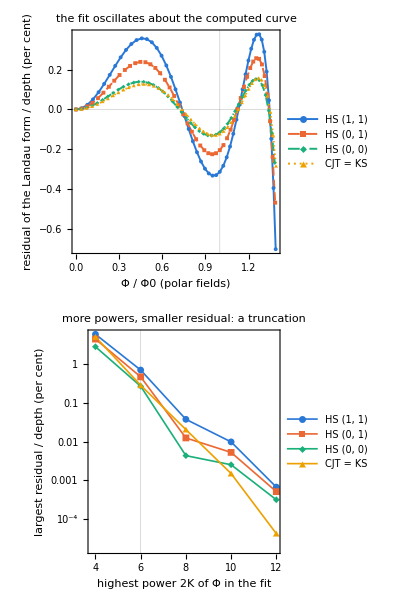

```mathematica
(* the figure: top, the residual of the Landau form along the fitted interval relative to the depth (KS and CJT
   coincide along the polar fields, so one curve is drawn for both); bottom, the largest residual of the fits with
   the powers Phi^2 .. Phi^(2K) against 2K (logarithmic scale); one panel above the other, so that both fit the
   width of a printed page *)
lfColors = {RGBColor["#2a78d6"], RGBColor["#eb6834"], RGBColor["#1baf7a"], RGBColor["#eda100"]};
lfShown = {"HS_1_1", "HS_0_1", "HS_0_0", "CJT"};
lfLegend = {"HS (1, 1)", "HS (0, 1)", "HS (0, 0)", "CJT = KS"};
Column[{
  ListLinePlot[Table[With[{r = lfResults[t]["residuals"]}, Transpose[{r[[All, 1]], 100 r[[All, 3]]}]], {t, lfShown}],
   PlotStyle -> Table[Directive[lfColors[[i]], AbsoluteThickness[1.4], AbsoluteDashing[{{}, {6, 3}, {6, 2, 1, 2}, {1, 2}}[[i]]]], {i, 4}],
   PlotMarkers -> {Automatic, 4}, Frame -> True, FrameLabel -> {"Φ / Φ0 (polar fields)", "residual of the Landau form / depth (per cent)"},
   PlotLegends -> Placed[lfLegend, {Left, Bottom}], GridLines -> {{1.0}, {0}}, ImageSize -> 460,
   PlotLabel -> "the fit oscillates about the computed curve"],
  ListLogPlot[Table[Table[{2 k, 100 lfResults[t]["resK" <> ToString[k]]/Abs[lfE0[t]]}, {k, 2, 6}], {t, lfShown}],
   Joined -> True, PlotStyle -> Table[Directive[lfColors[[i]], AbsoluteThickness[1.2]], {i, 4}], PlotMarkers -> {Automatic, 7},
   Frame -> True, FrameLabel -> {"highest power 2K of Φ in the fit", "largest residual / depth (per cent)"},
   PlotLegends -> Placed[lfLegend, {Left, Bottom}], GridLines -> {{6}, None}, ImageSize -> 460,
   PlotLabel -> "more powers, smaller residual: a truncation"]}, Spacings -> 1.5]
```

## III.L.5 Why no polynomial can be exact: the cause

The pair field enters the quasi-particle energies like a mass. For the applied pair self-energy Φ_a(K_LL^3)^† and a normal self-energy that is a Dirac mass, (M_SF^(X,D)-m_LL)β_LL⊗1_2, the eigenvalues of the matrix of Bogoliubov and de Gennes at the momentum (q⃗)_LL are ±E, each eight times, with

E==((|(q⃗)_LL|)^2+(M_SF^(X,D))^2+Φ_a^2)^(1/2).

The next cell checks this for 20 random momenta, masses and fields with the matrices of Part I (hLL, kLL, betaLL); along the whole polar curve the normal self-energy is such a Dirac mass (the Rust check P3-9 and the Python check YP3-9).

```mathematica
(* the BdG matrix of the eight components with the Dirac mass M (normal self-energy (M - m) beta (x) 1_2) and the applied
   pair self-energy fa (K^3)^dag, at the momentum q; its sorted eigenvalues against -E (eight times) and +E (eight times) *)
lfBdG[q_, mass_, fa_] := Module[{n = (mass - mLL) d8[betaLL], p = fa ConjugateTranspose[kLL[3]], a, d},
   a = hLL[q, mLL] + n; d = hLL[-q, mLL] + n;
   N[ArrayFlatten[{{a, p}, {ConjugateTranspose[p], -Transpose[d]}}]]];
SeedRandom[20261121];
lfQpDev = Max[Table[Module[{q = RandomReal[{-1, 1}, 3], mass = RandomReal[{0.1, 0.5}], fa = RandomReal[{0, 0.6}], ev, e},
     ev = Sort[Re[Eigenvalues[lfBdG[q, mass, fa]]]];
     e = Sqrt[q . q + mass^2 + fa^2];
     Max[Abs[ev - Join[ConstantArray[-e, 8], ConstantArray[e, 8]]]]], {20}]];
check["WP3-8", "the pair field enters the quasi-particle energies like a mass: the BdG matrix with N = (M - m) beta (x) 1_2 and P = Phi_a (K^3)^dag has the eigenvalues -+(q^2 + M^2 + Phi_a^2)^(1/2), eight times each (20 random q, M, Phi_a)", lfQpDev, 10^-13, "P3-8", "YP3-8"];
```

PASS WP3-8  deviation 1.554e-15 (tolerance 1.000e-13): the pair field enters the quasi-particle energies like a mass: the BdG matrix with N = (M - m) beta (x) 1_2 and P = Phi_a (K^3)^dag has the eigenvalues -+(q^2 + M^2 + Phi_a^2)^(1/2), eight times each (20 random q, M, Phi_a)   [the same check: Rust P3-8, Python YP3-8]

A logarithm. The energy per volume is an integral over the momenta q<Λ_LL of functions of (q^2+s)^(1/2) with s==(M_SF^(X,D))^2+Φ_a^2. The next cell integrates the simplest of them exactly and expands the result about s==0: it contains the term 1/16 s^2 ln s, which is not analytic at s==0, that is, at Φ_a^2==-(M_SF^(X,D))^2. Hence 𝒱_SF^X is not a polynomial in (|Φ⃗|)^2, and a series of powers of (|Φ⃗|)^2 about the origin can converge only within a radius of the order of the Dirac mass (m_LL==0.2 at the origin), while Φ_(0,SF)^X==0.31 to 0.40: the superfluid is far from the regime of Landau's theory, where the order parameter is small and the Landau coefficients are Taylor coefficients.

```mathematica
(* the integral of q^2 (q^2 + s)^(1/2) from 0 to the cutoff lam, exactly, and its expansion about s = 0 *)
(* lfq: the modulus of the momentum, lfs: the quantity M^2 + Phi_a^2, lfLam: the cutoff *)
lfInt = Integrate[lfq^2 Sqrt[lfq^2 + lfs], {lfq, 0, lfLam}, Assumptions -> lfs > 0 && lfLam > 0];
lfClosed = lfLam (2 lfLam^2 + lfs) Sqrt[lfLam^2 + lfs]/8 - lfs^2/8 Log[(lfLam + Sqrt[lfLam^2 + lfs])/Sqrt[lfs]];
Print["the integral minus the closed form: ", FullSimplify[lfInt - lfClosed, Assumptions -> lfs > 0 && lfLam > 0]];
lfSeries = Expand[Normal[Series[lfClosed /. lfLam -> 1, {lfs, 0, 2}]]];
Print["the closed form about s = 0 (cutoff 1), to the order s^2: ", lfSeries];
Print["its term with the logarithm: ", Coefficient[lfSeries, Log[lfs]], " Log[s]"];
```

the integral minus the closed form: 0

the closed form about s = 0 (cutoff 1), to the order s^2: 1/4+lfs/4+lfs^2/32-1/8 lfs^2 Log[2]+1/16 lfs^2 Log[lfs]

its term with the logarithm: lfs^2/16 Log[s]

The Taylor coefficient at the origin. The coefficient a_SF^(X,Tay) of (|Φ⃗|)^2 of the Taylor series at the origin is the limit of 𝒱_SF^X/Φ^2 at Φ→0. The Rust and the Python program compute it from three states with small applied fields (0.004, 0.008, 0.016) and the Richardson elimination of the term proportional to Φ^2. The next cell estimates it from the first six points of the computed curve (Φ<0.1, well inside the radius of convergence) by fitting 𝒱_SF^X/Φ^2==a_0+a_1 Φ^2+a_2 Φ^4; the truncation of this local series limits the agreement to about 3×10^-7. The fitted a_SF^X of the Landau form differs from a_SF^(X,Tay) by 0.7 to 2 per cent: it is a property of the fit.

```mathematica
(* lfTaylor[t]: a^Tay estimated from the points 2 to 7 of the curve (the first point is Phi = 0) *)
lfTaylor[t_] := Module[{p = lfCurve[t][[2 ;; 7]]}, LeastSquares[Table[{1, x^2, x^4}, {x, p[[All, 1]]}], p[[All, 2]]/p[[All, 1]]^2][[1]]];
Do[check["WP3-10 " <> t, lfName[t] <> ": the coefficient of Phi^2 of the Taylor series at the origin from the first six points of the curve = the Rust value a^Tay = " <> ToString[rustPart3["p3_a_taylor_" <> t]] <> " (relative)",
   Abs[lfTaylor[t] - rustPart3["p3_a_taylor_" <> t]]/Abs[rustPart3["p3_a_taylor_" <> t]], 10^-6, "P3-10 " <> t, "YP3-10 " <> t], {t, {"HS_1_1", "CJT"}}];
Grid[Prepend[Table[{lfName[t], NumberForm[lfTaylor[t], 10], NumberForm[rustPart3["p3_a_taylor_" <> t], 10], NumberForm[lfResults[t]["a"], 10], NumberForm[100 (lfResults[t]["a"]/rustPart3["p3_a_taylor_" <> t] - 1), 3]}, {t, lfTags}],
   {"method", "a^Tay from the curve", "a^Tay of the Rust program", "a of the Landau form", "a/a^Tay - 1 (per cent)"}], Frame -> All]
```

PASS WP3-10 HS_1_1  deviation 2.646e-7 (tolerance 1.000e-6): HS (1, 1): the coefficient of Phi^2 of the Taylor series at the origin from the first six points of the curve = the Rust value a^Tay = -0.00616243 (relative)   [the same check: Rust P3-10 HS_1_1, Python YP3-10 HS_1_1]

PASS WP3-10 CJT  deviation 2.377e-8 (tolerance 1.000e-6): CJT: the coefficient of Phi^2 of the Taylor series at the origin from the first six points of the curve = the Rust value a^Tay = -0.00429666 (relative)   [the same check: Rust P3-10 CJT, Python YP3-10 CJT]

method | a^Tay from the curve | a^Tay of the Rust program | a of the Landau form | a/a^Tay - 1 (per cent)
HS (1, 1) | -0.006162429464 | -0.006162431094 | -0.006040880441 | -1.97
HS (0, 1) | -0.005353418987 | -0.005353419813 | -0.005281144124 | -1.35
HS (0, 0) | -0.004296658395 | -0.004296658732 | -0.004261967263 | -0.807
KS | -0.004296658653 | -0.004296658755 | -0.00426740334 | -0.681
CJT | -0.004296658653 | -0.004296658755 | -0.00426740334 | -0.681

## III.L.6 Why it matters

It enters no other result. The effective Lagrangians of the solution contain the computed function 𝒱_SF^X, not the Landau form, and no other result uses a_SF^X, b_SF^X, c_SF^X: the mass of the amplitude mode uses the curvature 𝒱''_amp of the computed curve, u_SF^X and the mass of the non-unitary modes use the computed curvature in the non-unitary direction, and the masses of the gauge bosons and the dynamics use Φ_(0,SF)^X, Z_SF^X, Y_SF^X and the susceptibilities.

It matters to whoever replaces $\mathcal V^X_{\rm SF}$ by the Landau form, as in a model of the type of Ginzburg and Landau or of Higgs: the minimum of the polynomial is 0.04 to 0.11 per cent too small, its depth 0.12 to 0.31 per cent too large, its curvature at its minimum 0.86 to 2.3 per cent too large, and the mass of the amplitude mode 0.43 to 1.1 per cent too large (the table above). A derivative enlarges the relative error of the function. Beyond the fitted interval the error grows: fitted on the whole computed curve, the form misses by 1.2 to 1.7 per cent of the depth.

The coefficients are not constants of the theory. a_SF^X differs from the Taylor coefficient at the origin, and b_SF^X, c_SF^X change with the fitted interval and with the number of powers (the last four rows of the table). No physical meaning may be given to b_SF^X or c_SF^X alone. The physical quantities are those that the computed function defines: Φ_(0,SF)^X, the depth, the curvatures at the minimum, and a_SF^(X,Tay).

The qualitative results do not depend on the fit. That 𝒱_SF^X vanishes at the origin, is negative near it, has its minimum at Φ_(0,SF)^X, depends only on the two invariants, and has a stable polar minimum (u_SF^X>0) are properties of the computed function, checked on it directly; the sign of a_SF^X is that of a_SF^(X,Tay) (negative: the normal vacuum is unstable).

The comparison with the Standard Model. The field has a Mexican hat with the symmetry structure of the Higgs sector and of the polar phase of a condensate of spin 1, but its potential is not the quartic potential of the Standard Model: the quartic form misses 𝒱_SF^X by 2.8 to 5.9 per cent of the depth, about ten times more than the Landau form with the sixth power.

Corrections of the first answers. The first answers to the author contained five statements that were not exact; the numbers of this chapter are the corrected ones. (1) The residual changes its sign three times, not five. (2) The fit called a fit on [0,2 Φ_0] used all 61 points of the curve, whose fields reach 1.52 to 1.64 times Φ_(0,SF)^X; the applied field, not the field of the states, reaches 2 Φ_(0,SF)^X. (3) The range of the end of the curve is 1.52 to 1.64 (HS (0,0)), not 1.52 to 1.61. (4) The singularity lies at Φ_a^2==-(M_SF^(X,D))^2 in the applied field; in the field of the states the radius of convergence is of the order of the Dirac mass, not equal to it. (5) The errors of the curvature quoted first, 1.1 to 2.7 per cent, are those of the polynomial at the minimum of the computed curve; at the polynomial's own minimum, where a user evaluates it, they are 0.86 to 2.3 per cent, as the table shows.

## Part III, second section. The free energy at finite temperature: the critical temperatures and the size of the order parameter

On 21 November 2026 the author asked to add to the analysis and the solution the effective potential and the free energy of each of the five computed methods X (HS (1,1), HS (0,1), HS (0,0), KS and CJT), to determine whether the order parameter is then smaller and more physically reasonable, and to document this addendum with its provenance. The effective potential of each method is the subject of Section III.L. This chapter computes the free energy at the temperature T with the engine of Part II, shows that its value at T==0 is the effective potential, finds the critical temperatures, and answers the question (Section III.T.6). The Rust program sf_part3 (module thermal) and the Python program sf_part3.py compute the same things; the closed cell of Section III.T.2 holds their values for the comparison.

## III.T.1 The free energy of a state at the temperature T

Units and conditions. The temperature T is measured in units of energy (Boltzmann's constant k_B==1), in the units of the project (Λ_LL==1). The chemical potential μ_LL of the fermion number is zero, as everywhere in the solution: the states hold as many particles as antiparticles. The thermal states. At the temperature T a uniform quasi-free state is the thermal state of its matrix of Bogoliubov and de Gennes H_SF (Section II.2): at every momentum its generalized density, the 16×16 matrix of the normal and the pair correlations, is f(H_SF), the Fermi function f(ε)==(e^(ε/T)+1)^-1 applied to the eigenvalues ε_k (k==1,…,16) of H_SF, with the occupations f_k==f(ε_k). At T==0 the Fermi function is 1 for the negative and 0 for the positive eigenvalues, and the thermal state is the ground state of Part II. The free energy per volume of method X is

ℰ_SF^X-T 𝒮_SF,      𝒮_SF==-1/2 ∫(d^3 q)/(2π)^3 ∑_(k==1)^16 [f_k ln f_k+(1-f_k) ln(1-f_k)],

with the energy per volume ℰ_SF^X of method X (unchanged, Section II.2) and the entropy per volume 𝒮_SF of the quasi-free state. Every mode of the doubled space of H_SF appears twice, at ±ε with the occupations f and 1-f, hence the factor 1/2. The self-energies are the derivatives of ℰ_SF^X as at T==0, and the stationary points of the free energy are the self-consistent thermal states. In HS this is the free energy of the saddle point of the auxiliary fields; in CJT the effective action at the temperature T with the truncation of the method at T==0; in KS the functional of N. D. Mermin (the theory of Hohenberg, Kohn and Sham at finite temperature) with the entropy of the quasi-free state of Kohn and Sham and the exchange-correlation energy of the method at T==0 (in the exact theory of Mermin the exchange-correlation free energy depends on the temperature; here only the states do, an approximation of the method). The free energy of the field Φ⃗ is the smallest free energy among the thermal states with this field, measured from the normal state at the same temperature:

ℱ_SF^X(Φ⃗;T)==min{ℰ_SF^X-T 𝒮_SF: (Φ⃗)_SF^X==Φ⃗}-(ℰ_SF^X-T 𝒮_SF)_normal.

It is computed point by point as the effective potential of Section III.L: a fixed pair self-energy Φ_a(K_LL^3)^† (the applied field) is put into H_SF, the normal self-energy is made self-consistent at the temperature T, and the thermal state gives one point, its own field Φ and its free energy. Its minimum lies at |Φ⃗|==Φ_(0,SF)^X(T), the order parameter at the temperature $T$: the modulus of the field of the self-consistent superfluid at T. At T==0 the entropy vanishes and ℱ_SF^X(Φ⃗;0)==𝒱_SF^X(Φ⃗): the effective potential is the free energy at zero temperature, and Φ_(0,SF)^X(0)==Φ_(0,SF)^X. The next cell defines the thermal states of the engine of Part II: thermalNode makes f(H_SF) and the entropy of one node of the grid, solveSFT the self-consistent thermal state, and fixedPairT the thermal state of an applied pair field.

```mathematica
(* fermiSF[e, t]: the Fermi function 1/(e^(e/t) + 1) of the energy e at the temperature t (the step function at t = 0) *)
fermiSF[e_?NumericQ, t_?NumericQ] := If[t <= 0, Which[e < 0, 1., e > 0, 0., True, 0.5], 1./(Exp[Clip[e/t, {-700., 700.}]] + 1.)];
(* binEntropy[f]: the entropy -(f ln f + (1 - f) ln(1 - f)) of a mode with the occupation f (zero at f = 0 and f = 1) *)
binEntropy[f_] := If[0 < f < 1, -(f Log[f] + (1 - f) Log[1 - f]), 0.];
(* thermalNode[h, t]: the thermal state f(H) of one BdG matrix h at the temperature t:
   {C^n, C^p, the sorted eigenvalues, the sum of the entropies of the 16 modes} *)
thermalNode[h_, t_] := Module[{ev, vec, f, r},
   {ev, vec} = Eigensystem[0.5 (h + ConjugateTranspose[h])]; ev = Re[ev];
   f = Map[fermiSF[#, t] &, ev];
   r = Transpose[vec] . DiagonalMatrix[f] . Conjugate[vec];   (* R = sum_k f_k v_k v_k^dag *)
   {r[[1 ;; 8, 1 ;; 8]], -r[[1 ;; 8, 9 ;; 16]], Sort[ev], Total[Map[binEntropy, f]]}];
(* solveSFT[mo, N0, P0, t, mix, tol, maxit]: the self-consistent thermal state at the temperature t (the stationary
   point of E - t S) from the initial self-energies N0, P0: the self-energies, the energy per volume (from the normal
   vacuum), the entropy per volume, the free energy per volume and the number of iterations *)
solveSFT[mo_, n0_, p0_, t_, mix_ : 0.6, tol_ : 10^-13, maxit_ : 400000] := Module[
   {ns = n0, ps = p0, res, cn, cp, ent, rho, kap, ek, ei, n2, p2, r, it = 0, out = None},
   While[out === None,
     res = Map[thermalNode[#, t] &, bdg[mo, ns, ps]];
     cn = res[[All, 1]]; cp = res[[All, 2]];
     ent = 0.5 mo["g"]["w"] . res[[All, 4]];
     {rho, kap, ek} = localDens[mo, cn, cp];
     {ei, n2, p2} = interaction[mo["ts"], rho, kap];
     r = Max[Abs[n2 - ns], Abs[p2 - ps]];
     If[r < tol || it >= maxit,
       out = <|"n" -> n2, "p" -> p2, "e" -> ek + ei, "s" -> ent, "free" -> ek + ei - t ent, "it" -> it, "res" -> r|>,
       ns = mix n2 + (1 - mix) ns; ps = mix p2 + (1 - mix) ps;
       ns = 0.5 (ns + ConjugateTranspose[ns]); ps = 0.5 (ps - Transpose[ps]);
       it++]];
   out];
(* fixedPairT[mo, pfix, N0, t]: the thermal state of the applied pair self-energy pfix at the temperature t, with the
   normal self-energy made self-consistent: {N, the field Phi of the state (the modulus of the amplitude of its own
   pair self-energy in the channel K^3), its free energy per volume} *)
fixedPairT[mo_, pfix_, n0_, t_, tol_ : 10^-14] := Module[{ns = n0, res, cn, cp, ent, rho, kap, ek, ei, n2, p2, done = False, it = 0},
   While[! done,
     res = Map[thermalNode[#, t] &, bdg[mo, ns, pfix]];
     cn = res[[All, 1]]; cp = res[[All, 2]];
     ent = 0.5 mo["g"]["w"] . res[[All, 4]];
     {rho, kap, ek} = localDens[mo, cn, cp];
     {ei, n2, p2} = interaction[mo["ts"], rho, kap];
     If[Max[Abs[n2 - ns]] < tol || it >= 200000, done = True,
       ns = 0.7 n2 + 0.3 ns; ns = 0.5 (ns + ConjugateTranspose[ns]); it++]];
   {n2, Abs[Tr[k8[3] . p2]/8], ek + ei - t ent}];
(* phiOf[sol]: the order parameter of a self-consistent state, the modulus of the amplitude of its pair self-energy *)
phiOf[sol_] := Abs[Tr[k8[3] . sol["p"]]/8];
Print["the thermal engine is defined"];
```

the thermal engine is defined

## III.T.2 The values of the Rust program

The closed cell holds the thermal results of the Rust program sf_part3: rustThermal (per method and reduced temperature T/T_SF^(X,c): the temperature, the order parameter, the Dirac masses of the superfluid and of the normal state, the gap, the radius of convergence, the free energy at the minimum, the difference of the entropies, the residual of the gap equation, the Taylor coefficients, the order parameter of Landau's theory and the number of iterations), rustThermalLandau (the residuals of the Landau forms) and rustThermalCurves (the free-energy curves: the applied field, the field of the state and its free energy). They were copied from the data files named, with their SHA-256 checksums, in the comment at the top of the cell, by wolfram/tools/make_data_cells.py.

```mathematica
(* The values of the Rust programs that Section III.T of Part III of the notebook uses or compares with its own results, written by
   wolfram/tools/make_data_cells.py from the data files of the folder data/ (do not edit):
     data/part3_thermal.csv   SHA-256 c5fee32769ca52cea89527613b67cdd854ce91c1ee113805aab3d2ff02d0450f
     data/part3_thermal_landau.csv   SHA-256 ff63593fd7adfb0540f2141cad93438d810e0c00d44612df93889d17a1b577f0
     data/part3_thermal_curves.csv   SHA-256 519b410f803a762dcdb4d503197344d25079c751b45388421a0d79cc80e69e9b
*)
rustThermal = {
   {"HS_1_1", 0.00000000000000000*^0, 0.00000000000000000*^0, 4.03064140597377718*^-1, 2.06685193247415966*^-1, 4.52967405607980100*^-1, 2.00000000000000039*^-1, 2.00000000000000039*^-1, 2.01532070298688826*^0, -5.18634420225986734*^-4, 0.00000000000000000*^0, 1.46549439250520663*^-14, -6.16243109797050097*^-3, 1.75971265451975480*^-2, 4.18446714062837399*^-1, 0},
   {"HS_1_1", 1.00000000000000006*^-1, 2.60467239400117845*^-2, 4.03064139788343712*^-1, 2.06685193247425070*^-1, 4.52967404888081238*^-1, 2.00000210088079139*^-1, 2.16092428814187248*^-1, 1.86523952736414000*^0, -5.18631526824240891*^-4, -1.15429618855640456*^-6, -1.78412840057262656*^-13, -6.16226204362798138*^-3, 1.75918927153880036*^-2, 4.18503215727278388*^-1, 45},
   {"HS_1_1", 2.00000000000000011*^-1, 5.20934478800235690*^-2, 4.03050187012162442*^-1, 2.06685193247425125*^-1, 4.52954989329253987*^-1, 2.00028575053960239*^-1, 2.58446988491398300*^-1, 1.55950815819073418*^0, -5.17725243374199070*^-4, -1.15315674770713226*^-4, -1.79078973872037750*^-13, -6.13942481653377125*^-3, 1.72869545404348221*^-2, 4.21395215052413230*^-1, 102},
   {"HS_1_1", 2.99999999999999989*^-1, 7.81401718200353534*^-2, 4.02588814187026967*^-1, 2.06685193247424098*^-1, 4.52544497719551964*^-1, 2.00192328067363978*^-1, 3.16764347767990173*^-1, 1.27094105452138129*^0, -5.08780212594506904*^-4, -6.57021262340912377*^-4, -1.56541446472147072*^-13, -6.00710067673982783*^-3, 1.64030120933015520*^-2, 4.27913171820127280*^-1, 124},
   {"HS_1_1", 4.00000000000000022*^-1, 1.04186895760047138*^-1, 3.99858803725602452*^-1, 2.06685193247424515*^-1, 4.50117575778368251*^-1, 2.00568006871905014*^-1, 3.83876523727603336*^-1, 1.04163390832761649*^0, -4.79514607767027464*^-4, -1.64816392432584136*^-3, -1.66644475996235997*^-13, -5.70037901034018031*^-3, 1.53327557161869136*^-2, 4.31148381433984262*^-1, 138},
   {"HS_1_1", 5.00000000000000000*^-1, 1.30233619700058922*^-1, 3.91974515458313189*^-1, 2.06685193247425347*^-1, 4.43128412400406735*^-1, 2.01172887251793192*^-1, 4.55924198144485926*^-1, 8.59736151433869278*^-1, -4.21316719516131384*^-4, -2.82106453332746539*^-3, -1.87738713464113971*^-13, -5.19711302507323836*^-3, 1.43714770523076709*^-2, 4.25221661594209099*^-1, 154},
   {"HS_1_1", 5.99999999999999978*^-1, 1.56280343640070707*^-1, 3.75736642872155135*^-1, 2.06685193247425014*^-1, 4.28831894691338089*^-1, 2.01991796225181652*^-1, 5.30896808185613245*^-1, 7.07739502439783563*^-1, -3.34188707109821237*^-4, -3.80655022335965511*^-3, -1.85740312019788689*^-13, -4.49661055270452522*^-3, 1.36145315788297420*^-2, 4.06374350180396804*^-1, 180},
   {"HS_1_1", 6.99999999999999956*^-1, 1.82327067580082491*^-1, 3.47467901059274387*^-1, 2.06685193247426680*^-1, 4.04292853479088610*^-1, 2.02992221457690775*^-1, 6.07702785902556997*^-1, 5.71772763133242656*^-1, -2.27753628049724884*^-4, -4.24959024225199031*^-3, -2.30593322214645013*^-13, -3.60946204822394862*^-3, 1.30657388043412606*^-2, 3.71654380563042563*^-1, 224},
   {"HS_1_1", 8.00000000000000044*^-1, 2.08373791520094276*^-1, 3.01648359954973688*^-1, 2.06685193247427873*^-1, 3.65664466651125342*^-1, 2.04134197105665022*^-1, 6.85715254885332914*^-1, 4.39903236519677721*^-1, -1.19972495016724533*^-4, -3.87126299430877972*^-3, -2.69784194983913039*^-13, -2.55204023812964208*^-3, 1.26990110163507676*^-2, 3.16988722069115048*^-1, 317},
   {"HS_1_1", 8.49999999999999978*^-1, 2.21397153490100168*^-1, 2.68923955618131760*^-1, 2.06685193247429622*^-1, 3.39173794702701425*^-1, 2.04745536344125706*^-1, 7.25049080056323847*^-1, 3.70904484972577275*^-1, -7.29081582030912528*^-5, -3.31291713641598817*^-3, -3.19300141882195021*^-13, -1.96523208837751963*^-3, 1.25739852078370264*^-2, 2.79547397176270973*^-1, 402},
   {"HS_1_1", 9.00000000000000022*^-1, 2.34420515460106060*^-1, 2.25794314993588652*^-1, 2.06685193247432702*^-1, 3.06107565720209751*^-1, 2.05377364387778705*^-1, 7.64554782864846572*^-1, 2.95327843150126779*^-1, -3.48428810406100319*^-5, -2.48728671648410990*^-3, -4.05897537802957231*^-13, -1.34279658692440409*^-3, 1.24828252496129982*^-2, 2.31917580279548452*^-1, 584},
   {"HS_1_1", 9.49999999999999956*^-1, 2.47443877430111953*^-1, 1.64010881219054633*^-1, 2.06685193247439197*^-1, 2.63852872385316517*^-1, 2.06025265304606298*^-1, 8.04205950849164908*^-1, 2.03941392184271653*^-1, -9.32510522693493632*^-6, -1.38476840319938857*^-3, -5.84088333255294856*^-13, -6.86995217405559082*^-4, 1.24220551032653871*^-2, 1.66289617100082804*^-1, 1119},
   {"HS_1_1", 9.79999999999999982*^-1, 2.55257894612115510*^-1, 1.05365012474094702*^-1, 2.06685193247452187*^-1, 2.31992575229042181*^-1, 2.06420021685992133*^-1, 8.28057377260049021*^-1, 1.27243613024421054*^-1, -1.55119189493031079*^-6, -5.87964056934668633*^-4, -9.36251076666394511*^-13, -2.78406643572580513*^-4, 1.23988855323770367*^-2, 1.05957932160265972*^-1, 2632},
   {"HS_0_1", 0.00000000000000000*^0, 0.00000000000000000*^0, 3.62009001414210163*^-1, 2.00000000000000011*^-1, 4.13582539651897785*^-1, 2.00000000000000011*^-1, 2.00000000000000011*^-1, 1.81004500707105076*^0, -3.60802926138994290*^-4, 0.00000000000000000*^0, 1.57651669496772229*^-14, -5.35341981573553369*^-3, 1.92247062874778829*^-2, 3.73139131641865407*^-1, 0},
   {"HS_0_1", 1.00000000000000006*^-1, 2.40465456326528354*^-2, 3.62009000583464358*^-1, 2.00000000000000011*^-1, 4.13582538924745557*^-1, 2.00000000000000011*^-1, 2.13791870969331915*^-1, 1.69327766739734442*^0, -3.60801695846061493*^-4, -5.63506251246050155*^-7, -2.10054196259079617*^-13, -5.35333832170010494*^-3, 1.92218621279717540*^-2, 3.73163896022342512*^-1, 52},
   {"HS_0_1", 2.00000000000000011*^-1, 4.80930912653056708*^-2, 3.61995976672328745*^-1, 2.00000000000000011*^-1, 4.13571139136851729*^-1, 2.00000000000000011*^-1, 2.50654855070213733*^-1, 1.44420093746409184*^0, -3.60281265365806154*^-4, -7.46325459038317280*^-5, -1.99396055222678115*^-13, -5.33816640325125106*^-3, 1.89904398294087409*^-2, 3.74898363206613905*^-1, 119},
   {"HS_0_1", 2.99999999999999989*^-1, 7.21396368979584923*^-2, 3.61578956151645259*^-1, 2.00000000000000011*^-1, 4.13206173152959322*^-1, 2.00000000000000011*^-1, 3.02262595822088309*^-1, 1.19624115305510892*^0, -3.54654549716569556*^-4, -4.56860119772100563*^-4, -1.91846538655227050*^-13, -5.23876529682243321*^-3, 1.82077945298732488*^-2, 3.79289483471422162*^-1, 144},
   {"HS_0_1", 4.00000000000000022*^-1, 9.61861825306113416*^-2, 3.59147957502352233*^-1, 2.00000000000000011*^-1, 4.11080594747686212*^-1, 2.00000000000000011*^-1, 3.62369183956195939*^-1, 9.91110650142278393*^-1, -3.35508948862336997*^-4, -1.18142946076693622*^-3, -2.09277040141842008*^-13, -4.99353524775365820*^-3, 1.71659115479251764*^-2, 3.81377991173855180*^-1, 160},
   {"HS_0_1", 5.00000000000000000*^-1, 1.20232728163264163*^-1, 3.52160604870838223*^-1, 2.00000000000000011*^-1, 4.04990236453910912*^-1, 2.00000000000000011*^-1, 4.27403910036146584*^-1, 8.23952698142268125*^-1, -2.96537002589676558*^-4, -2.06545547245469939*^-3, -2.06612504882741632*^-13, -4.57658653068199195*^-3, 1.61655205610787278*^-2, 3.76236559258156134*^-1, 179},
   {"HS_0_1", 5.99999999999999978*^-1, 1.44279273795916985*^-1, 3.37755650871235991*^-1, 2.00000000000000011*^-1, 3.92528826578956158*^-1, 2.00000000000000011*^-1, 4.95429820794457687*^-1, 6.81742674128134385*^-1, -2.37040796466585278*^-4, -2.84119167583764872*^-3, -2.35256258918070671*^-13, -3.98194727559129068*^-3, 1.53324793319277765*^-2, 3.60351688064688203*^-1, 207},
   {"HS_0_1", 6.99999999999999956*^-1, 1.68325819428569806*^-1, 3.12589435193321441*^-1, 2.00000000000000011*^-1, 3.71095883828532536*^-1, 2.00000000000000011*^-1, 5.65368234459458718*^-1, 5.52895292202230215*^-1, -1.63000521409869658*^-4, -3.23090218095352811*^-3, -2.68118860446975305*^-13, -3.21448867452805683*^-3, 1.46935932515376375*^-2, 3.30732554589827810*^-1, 257},
   {"HS_0_1", 8.00000000000000044*^-1, 1.92372365061222683*^-1, 2.71625825869918736*^-1, 2.00000000000000011*^-1, 3.37313784597539745*^-1, 2.00000000000000011*^-1, 6.36589115461706156*^-1, 4.26689397089225486*^-1, -8.66888647616621474*^-5, -2.99495560535890243*^-3, -3.20854454116670240*^-13, -2.28535501752375175*^-3, 1.42359893985427814*^-2, 2.83313984284468190*^-1, 361},
   {"HS_0_1", 8.49999999999999978*^-1, 2.04395637877549080*^-1, 2.42281514728338560*^-1, 2.00000000000000011*^-1, 3.14166090434754186*^-1, 2.00000000000000011*^-1, 6.72553459353231520*^-1, 3.60241273550702235*^-1, -5.29380696086463078*^-5, -2.58418103432139432*^-3, -3.63375995959813736*^-13, -1.76455837665402096*^-3, 1.40674826560176422*^-2, 2.50434884037228855*^-1, 457},
   {"HS_0_1", 9.00000000000000022*^-1, 2.16418910693875505*^-1, 2.03530728022933011*^-1, 2.00000000000000011*^-1, 2.85350236112650035*^-1, 2.00000000000000011*^-1, 7.08705927376062084*^-1, 2.87186433979030487*^-1, -2.54219885020400688*^-5, -1.95552310145057431*^-3, -4.50861570300276071*^-13, -1.20879839900565368*^-3, 1.39347497814730353*^-2, 2.08263111643605281*^-1, 662},
   {"HS_0_1", 9.49999999999999956*^-1, 2.28442183510201902*^-1, 1.47917121573849536*^-1, 2.00000000000000011*^-1, 2.48755853910401448*^-1, 2.00000000000000011*^-1, 7.45019133549074009*^-1, 1.98541372849327380*^-1, -6.83644069275016891*^-6, -1.09694461273808497*^-3, -6.46149800331841107*^-13, -6.19985292547715308*^-4, 1.38345909614467633*^-2, 1.49689912380223250*^-1, 1264},
   {"HS_0_1", 9.79999999999999982*^-1, 2.35656147199997751*^-1, 9.50560463513955151*^-2, 2.00000000000000011*^-1, 2.21439951110811661*^-1, 2.00000000000000011*^-1, 7.66874716919379695*^-1, 1.23952510435141397*^-1, -1.14044473768304747*^-6, -4.67784676118191550*^-4, -1.03239639059893307*^-12, -2.51616408640426752*^-4, 1.37888698374499328*^-2, 9.55190832886074620*^-2, 2966},
   {"HS_0_0", 0.00000000000000000*^0, 0.00000000000000000*^0, 3.06988793478321476*^-1, 2.00000000000000011*^-1, 3.66390664893738172*^-1, 2.00000000000000011*^-1, 2.00000000000000011*^-1, 1.53494396739160721*^0, -2.06161908067716704*^-4, 0.00000000000000000*^0, 1.99840144432528177*^-14, -4.29665873418375120*^-3, 2.19548597938755349*^-2, 3.12813219867895564*^-1, 0},
   {"HS_0_0", 1.00000000000000006*^-1, 2.13799098394113624*^-2, 3.06988792757883322*^-1, 2.00000000000000011*^-1, 3.66390664290102586*^-1, 2.00000000000000011*^-1, 2.10977253627303768*^-1, 1.45508005000475626*^0, -2.06161590442378428*^-4, -1.78683870485045786*^-7, -2.39919195621496328*^-13, -4.29663297496244746*^-3, 2.19537648224743497*^-2, 3.12820083035570407*^-1, 64},
   {"HS_0_0", 2.00000000000000011*^-1, 4.27598196788227247*^-2, 3.06977840955852288*^-1, 2.00000000000000011*^-1, 3.66381488121215737*^-1, 2.00000000000000011*^-1, 2.40926557673658365*^-1, 1.27415526092255127*^0, -2.05942693084180028*^-4, -3.75605919840792015*^-5, -2.65454325187874929*^-13, -4.28857477718456049*^-3, 2.18011104010524398*^-2, 3.13618872090407397*^-1, 148},
   {"HS_0_0", 2.99999999999999989*^-1, 6.41397295182340732*^-2, 3.06630900007174356*^-1, 2.00000000000000011*^-1, 3.66090847794928842*^-1, 2.00000000000000011*^-1, 2.83905994887527713*^-1, 1.08004376634825672*^0, -2.03195142145932972*^-4, -2.59588793479555060*^-4, -2.50577336657897831*^-13, -4.22446239831084005*^-3, 2.11465130744969074*^-2, 3.16046761109513574*^-1, 180},
   {"HS_0_0", 4.00000000000000022*^-1, 8.55196393576454494*^-2, 3.04618445642257207*^-1, 2.00000000000000011*^-1, 3.64406911879432915*^-1, 2.00000000000000011*^-1, 3.34936448852486801*^-1, 9.09481326042295590*^-1, -1.93207610460496154*^-4, -7.06297068802625968*^-4, -2.68007838144512789*^-13, -4.04998069127815441*^-3, 2.01407963895679984*^-2, 3.17083146368678015*^-1, 200},
   {"HS_0_0", 5.00000000000000000*^-1, 1.06899549197056798*^-1, 2.98834827508437428*^-1, 2.00000000000000011*^-1, 3.59586226282372468*^-1, 2.00000000000000011*^-1, 3.90877268081672169*^-1, 7.64523424385981754*^-1, -1.72114922718287559*^-4, -1.27454463936129379*^-3, -2.66342503607575054*^-13, -3.73694338993302072*^-3, 1.90765395035363550*^-2, 3.12963336755906096*^-1, 223},
   {"HS_0_0", 5.99999999999999978*^-1, 1.28279459036468146*^-1, 2.86865102040744280*^-1, 2.00000000000000011*^-1, 3.49702140069011624*^-1, 2.00000000000000011*^-1, 4.49900495367928699*^-1, 6.37618995742927464*^-1, -1.39004831242621311*^-4, -1.80049954674639263*^-3, -2.90656387846865982*^-13, -3.27491528869804831*^-3, 1.81186066286005906*^-2, 3.00623301114122166*^-1, 257},
   {"HS_0_0", 6.99999999999999956*^-1, 1.49659368875879495*^-1, 2.65824677032317991*^-1, 2.00000000000000011*^-1, 3.32660125231949266*^-1, 2.00000000000000011*^-1, 5.10939013834198374*^-1, 5.20266939565862008*^-1, -9.67464175523145408*^-5, -2.09932032589344505*^-3, -3.27737836869346211*^-13, -2.66323237045859237*^-3, 1.73275065325314524*^-2, 2.77218045321493300*^-1, 317},
   {"HS_0_0", 8.00000000000000044*^-1, 1.71039278715290899*^-1, 2.31341566190409492*^-1, 2.00000000000000011*^-1, 3.05808633376220440*^-1, 2.00000000000000011*^-1, 5.73349543541859075*^-1, 4.03491323567295612*^-1, -5.21325001931242059*^-5, -1.99298519697389646*^-3, -3.81916720471053850*^-13, -1.90723109859211441*^-3, 1.67114133588756389*^-2, 2.38880154414117141*^-1, 442},
   {"HS_0_0", 8.49999999999999978*^-1, 1.81729233634996545*^-1, 2.06519673674368381*^-1, 2.00000000000000011*^-1, 2.87489783495983753*^-1, 2.00000000000000011*^-1, 6.04936989984614093*^-1, 3.41390387913989179*^-1, -3.20514325322191970*^-5, -1.73939604459583640*^-3, -4.34319247233361239*^-13, -1.47782374529221473*^-3, 1.64651535370982302*^-2, 2.11842664361019450*^-1, 557},
   {"HS_0_0", 9.00000000000000022*^-1, 1.92419188554702247*^-1, 1.73636380343455271*^-1, 2.00000000000000011*^-1, 2.64857683631751661*^-1, 2.00000000000000011*^-1, 6.36728769098501068*^-1, 2.72700698900875282*^-1, -1.54967443698693884*^-5, -1.33087392761399234*^-3, -5.40456568387526204*^-13, -1.01587906810520802*^-3, 1.62568427012727765*^-2, 1.76761592795432909*^-1, 803},
   {"HS_0_0", 9.49999999999999956*^-1, 2.03109143474407894*^-1, 1.26300523323471497*^-1, 2.00000000000000011*^-1, 2.36541375221720501*^-1, 2.00000000000000011*^-1, 6.68695737774511967*^-1, 1.88875920973883588*^-1, -4.19572168831872094*^-6, -7.54542338761505366*^-4, -7.60613794170694746*^-13, -5.22794204041353620*^-4, 1.60838237015390184*^-2, 1.27484014839757437*^-1, 1527},
   {"HS_0_0", 9.79999999999999982*^-1, 2.09523116426231309*^-1, 8.12069935767879558*^-2, 2.00000000000000011*^-1, 2.15857767536358269*^-1, 2.00000000000000011*^-1, 6.87949856226027445*^-1, 1.18042024199663795*^-1, -7.02760403664941941*^-7, -3.23767917984087161*^-4, -1.21413989973007119*^-12, -2.12590702996280975*^-4, 1.59958206260429406*^-2, 8.15180671132841178*^-2, 3571},
   {"KS", 0.00000000000000000*^0, 0.00000000000000000*^0, 3.28486108376768227*^-1, 1.62292932454748962*^-1, 3.66390664893738283*^-1, 1.99999999999999956*^-1, 1.99999999999999956*^-1, 1.64243054188384141*^0, -2.42238496593987293*^-4, 0.00000000000000000*^0, 1.99840144432528177*^-14, -4.29665873427411988*^-3, 1.73946558545531316*^-2, 3.51432977583400030*^-1, 0},
   {"KS", 1.00000000000000006*^-1, 2.22118737059346372*^-2, 3.28486107020618645*^-1, 1.62292932454620509*^-1, 3.66390663677830797*^-1, 1.99999630058052769*^-1, 2.11823493573549321*^-1, 1.55075389173751743*^0, -2.42237997206060963*^-4, -2.62630854253793138*^-7, -2.32924790566357842*^-13, -4.29662801074060397*^-3, 1.73937019818772333*^-2, 3.51441357255630193*^-1, 69},
   {"KS", 2.00000000000000011*^-1, 4.44237474118692743*^-2, 3.28471143962608236*^-1, 1.62292932454620786*^-1, 3.66377248667032529*^-1, 1.99902367541968135*^-1, 2.43799750152181693*^-1, 1.34729893594055783*^0, -2.41949317768617826*^-4, -4.65136758234846112*^-5, -2.32036612146657717*^-13, -4.28854473204503747*^-3, 1.72877701171565840*^-2, 3.52184699972636406*^-1, 152},
   {"KS", 2.99999999999999989*^-1, 6.66356211178039115*^-2, 3.28046130613061371*^-1, 1.62292932454623229*^-1, 3.65996256449328483*^-1, 1.99174310188117570*^-1, 2.88954095828424240*^-1, 1.13528804522587312*^0, -2.38554900515556526*^-4, -3.03664772851192479*^-4, -2.26929586233381997*^-13, -4.22767618043523152*^-3, 1.68892440752766299*^-2, 3.53777944028642655*^-1, 183},
   {"KS", 4.00000000000000022*^-1, 8.88474948237385487*^-2, 3.25717360080343410*^-1, 1.62292932454623923*^-1, 3.63910421096221459*^-1, 1.97254664777942734*^-1, 3.41787725464486158*^-1, 9.52981443782677462*^-1, -2.26601560988550638*^-4, -8.06969396414282088*^-4, -2.32147634449120233*^-13, -4.06406862852282894*^-3, 1.63375732438404316*^-2, 3.52672620587933638*^-1, 203},
   {"KS", 5.00000000000000000*^-1, 1.11059368529673186*^-1, 3.19236720631573656*^-1, 1.62292932454616345*^-1, 3.58121599075397923*^-1, 1.93910298741386322*^-1, 3.99167526380355464*^-1, 7.99756241511946020*^-1, -2.01712494999578378*^-4, -1.44251616748287113*^-3, -2.57571741713036317*^-13, -3.76775063928325073*^-3, 1.58074329766685097*^-2, 3.45219567181734244*^-1, 224},
   {"KS", 5.99999999999999978*^-1, 1.33271242235607823*^-1, 3.06083308036051882*^-1, 1.62292932454623007*^-1, 3.46447669039659512*^-1, 1.89179837087876446*^-1, 4.59440165189150984*^-1, 6.66209293891485865*^-1, -1.62859725838816304*^-4, -2.03121285750755684*^-3, -2.61568544601686881*^-13, -3.32222935669061054*^-3, 1.53781414981743973*^-2, 3.28660780001394148*^-1, 257},
   {"KS", 6.99999999999999956*^-1, 1.55483115941542460*^-1, 2.83255070314341495*^-1, 1.62292932454619537*^-1, 3.26454331849804491*^-1, 1.83296156916720410*^-1, 5.21723260983607773*^-1, 5.42922065196631554*^-1, -1.13353030199358053*^-4, -2.36688288365620534*^-3, -2.97650792902004468*^-13, -2.72002437199150458*^-3, 1.50668789845702453*^-2, 3.00441381179997469*^-1, 314},
   {"KS", 8.00000000000000044*^-1, 1.77694989647477097*^-1, 2.46172746317551566*^-1, 1.62292932454609490*^-1, 2.94855925757380732*^-1, 1.76607569908527801*^-1, 5.85515174658273962*^-1, 4.20437858781757656*^-1, -6.10902191585502210*^-5, -2.24758545310429873*^-3, -3.65596442009064049*^-13, -1.96102219565931230*^-3, 1.48645357827013290*^-2, 2.56832856115480568*^-1, 433},
   {"KS", 8.49999999999999978*^-1, 1.88800926500444416*^-1, 2.19610326237401010*^-1, 1.62292932454600108*^-1, 2.73070854019265619*^-1, 1.73080768339881147*^-1, 6.17872799795870398*^-1, 3.55429671463049879*^-1, -3.75606595720808303*^-5, -1.96191356760842817*^-3, -4.17554879561521375*^-13, -1.52435182370629497*^-3, 1.47992053593038325*^-2, 2.26938620817272563*^-1, 543},
   {"KS", 9.00000000000000022*^-1, 1.99906863353411735*^-1, 1.84519572439458435*^-1, 1.62292932454583372*^-1, 2.45736583637741063*^-1, 1.69493073097083280*^-1, 6.50495560893293634*^-1, 2.83660002515723209*^-1, -1.81605955259464026*^-5, -1.50125980503304501*^-3, -5.02820007852733397*^-13, -1.05102722389945405*^-3, 1.47550997510928449*^-2, 1.88721295826967367*^-1, 781},
   {"KS", 9.49999999999999956*^-1, 2.11012800206379053*^-1, 1.34129494788390397*^-1, 1.62292932454530636*^-1, 2.10546235532435233*^-1, 1.65885238389455819*^-1, 6.83356337490339083*^-1, 1.96280457836957800*^-1, -4.91671086259208925*^-6, -8.51120498504779471*^-4, -7.20312698376801563*^-13, -5.42408435735681344*^-4, 1.47304593651313813*^-2, 1.35687573039770554*^-1, 1479},
   {"KS", 9.79999999999999982*^-1, 2.17676362318159428*^-1, 8.62078681756515003*^-2, 1.62292932454421890*^-1, 1.83768311904000614*^-1, 1.63725936189631327*^-1, 7.03176816175416386*^-1, 1.22597711119852751*^-1, -8.23470519548293034*^-7, -3.65179506945756405*^-4, -1.14186438082697350*^-12, -2.20917417311279580*^-4, 1.47243633268088689*^-2, 8.66127281306500046*^-2, 3453},
   {"CJT", 0.00000000000000000*^0, 0.00000000000000000*^0, 3.28486108376768504*^-1, 1.62292932454748962*^-1, 3.66390664893738505*^-1, 1.99999999999999956*^-1, 1.99999999999999956*^-1, 1.64243054188384296*^0, -2.42238496593995967*^-4, 0.00000000000000000*^0, 1.97619698383277864*^-14, -4.29665873424481867*^-3, 1.73946557889028269*^-2, 3.51432978245384775*^-1, 0},
   {"CJT", 1.00000000000000006*^-1, 2.22118737059346441*^-2, 3.28486107020618645*^-1, 1.62292932454620453*^-1, 3.66390663677830797*^-1, 1.99999630058052769*^-1, 2.11823493573549321*^-1, 1.55075389173751743*^0, -2.42237997206058307*^-4, -2.62630854253793561*^-7, -2.32924790566357842*^-13, -4.29662801087056859*^-3, 1.73937024164827342*^-2, 3.51441352870323298*^-1, 69},
   {"CJT", 2.00000000000000011*^-1, 4.44237474118692882*^-2, 3.28471143962608236*^-1, 1.62292932454620814*^-1, 3.66377248667032585*^-1, 1.99902367541968162*^-1, 2.43799750152181721*^-1, 1.34729893594055761*^0, -2.41949317768611429*^-4, -4.65136758234847738*^-5, -2.32036612146657717*^-13, -4.28854473205649359*^-3, 1.72877702572529872*^-2, 3.52184698546091968*^-1, 152},
   {"CJT", 2.99999999999999989*^-1, 6.66356211178039254*^-2, 3.28046130613061315*^-1, 1.62292932454623229*^-1, 3.65996256449328428*^-1, 1.99174310188117598*^-1, 2.88954095828424296*^-1, 1.13528804522587268*^0, -2.38554900515558288*^-4, -3.03664772851192696*^-4, -2.26929586233381997*^-13, -4.22767618055262719*^-3, 1.68892445658400461*^-2, 3.53777938895654065*^-1, 183},
   {"CJT", 4.00000000000000022*^-1, 8.88474948237385764*^-2, 3.25717360080343743*^-1, 1.62292932454623839*^-1, 3.63910421096221681*^-1, 1.97254664777942762*^-1, 3.41787725464486214*^-1, 9.52981443782678239*^-1, -2.26601560988544458*^-4, -8.06969396414283714*^-4, -2.32147634449120233*^-13, -4.06406862846341466*^-3, 1.63375730573988576*^-2, 3.52672622597675345*^-1, 203},
   {"CJT", 5.00000000000000000*^-1, 1.11059368529673214*^-1, 3.19236720631573767*^-1, 1.62292932454616345*^-1, 3.58121599075398034*^-1, 1.93910298741386378*^-1, 3.99167526380355575*^-1, 7.99756241511946131*^-1, -2.01712494999574962*^-4, -1.44251616748287221*^-3, -2.57571741713036317*^-13, -3.76775063915241442*^-3, 1.58074325845927038*^-2, 3.45219571457025032*^-1, 224},
   {"CJT", 5.99999999999999978*^-1, 1.33271242235607851*^-1, 3.06083308036051827*^-1, 1.62292932454623007*^-1, 3.46447669039659456*^-1, 1.89179837087876446*^-1, 4.59440165189151095*^-1, 6.66209293891485532*^-1, -1.62859725838815979*^-4, -2.03121285750756117*^-3, -2.61568544601686881*^-13, -3.32222935673976653*^-3, 1.53781416777941000*^-2, 3.28660778084414462*^-1, 257},
   {"CJT", 6.99999999999999956*^-1, 1.55483115941542488*^-1, 2.83255070314341495*^-1, 1.62292932454619510*^-1, 3.26454331849804436*^-1, 1.83296156916720410*^-1, 5.21723260983607773*^-1, 5.42922065196631554*^-1, -1.13353030199350464*^-4, -2.36688288365621488*^-3, -2.97650792902004468*^-13, -2.72002437190873659*^-3, 1.50668787495572814*^-2, 3.00441383518566585*^-1, 314},
   {"CJT", 8.00000000000000044*^-1, 1.77694989647477153*^-1, 2.46172746317551316*^-1, 1.62292932454609462*^-1, 2.94855925757380510*^-1, 1.76607569908527801*^-1, 5.85515174658274185*^-1, 4.20437858781757101*^-1, -6.10902191585484863*^-5, -2.24758545310429353*^-3, -3.65374397404139017*^-13, -1.96102219565562341*^-3, 1.48645359592934900*^-2, 2.56832854589639115*^-1, 433},
   {"CJT", 8.49999999999999978*^-1, 1.88800926500444471*^-1, 2.19610326237400927*^-1, 1.62292932454600136*^-1, 2.73070854019265619*^-1, 1.73080768339881119*^-1, 6.17872799795870620*^-1, 3.55429671463049601*^-1, -3.75606595720886366*^-5, -1.96191356760843337*^-3, -4.17554879561521375*^-13, -1.52435182384437506*^-3, 1.47992057890656576*^-2, 2.26938617532456643*^-1, 543},
   {"CJT", 9.00000000000000022*^-1, 1.99906863353411790*^-1, 1.84519572439458407*^-1, 1.62292932454583372*^-1, 2.45736583637741035*^-1, 1.69493073097083280*^-1, 6.50495560893293745*^-1, 2.83660002515723098*^-1, -1.81605955259481373*^-5, -1.50125980503304675*^-3, -5.03375119365045975*^-13, -1.05102722390437546*^-3, 1.47550998049229380*^-2, 1.88721295483159246*^-1, 781},
   {"CJT", 9.49999999999999956*^-1, 2.11012800206379109*^-1, 1.34129494788389841*^-1, 1.62292932454530636*^-1, 2.10546235532434872*^-1, 1.65885238389455791*^-1, 6.83356337490339194*^-1, 1.96280457836956940*^-1, -4.91671086259816079*^-6, -8.51120498504810696*^-4, -7.20312698376801563*^-13, -5.42408435827262166*^-4, 1.47304597196343430*^-2, 1.35687571418498104*^-1, 1479},
   {"CJT", 9.79999999999999982*^-1, 2.17676362318159483*^-1, 8.62078681756509729*^-2, 1.62292932454421890*^-1, 1.83768311904000364*^-1, 1.63725936189631355*^-1, 7.03176816175416497*^-1, 1.22597711119851988*^-1, -8.23470519545257268*^-7, -3.65179506945752935*^-4, -1.14219744773436105*^-12, -2.20917417453582145*^-4, 1.47243639574685115*^-2, 8.66127263036894218*^-2, 3453}};
rustThermalLandau = {
   {"HS_1_1", 0.00000000000000000*^0, 7.03549488586319421*^-3, 5.87575051155726363*^-2},
   {"HS_1_1", 5.00000000000000000*^-1, 5.55661176995715829*^-3, 6.64334614849266814*^-2},
   {"HS_1_1", 8.00000000000000044*^-1, 1.64922724776931837*^-3, 3.76104348710449982*^-2},
   {"HS_1_1", 9.00000000000000022*^-1, 4.04154657103356204*^-4, 1.82791300052407013*^-2},
   {"HS_1_1", 9.49999999999999956*^-1, 9.64103929053727405*^-5, 8.81073726675212984*^-3},
   {"HS_1_1", 9.79999999999999982*^-1, 1.66780646094716409*^-5, 3.73374903443293455*^-3},
   {"HS_0_1", 0.00000000000000000*^0, 4.69323630462264735*^-3, 4.42360781409401604*^-2},
   {"HS_0_1", 5.00000000000000000*^-1, 3.82208187321363439*^-3, 5.48227082922779912*^-2},
   {"HS_0_1", 8.00000000000000044*^-1, 1.05353898309065177*^-3, 2.94600974024732919*^-2},
   {"HS_0_1", 9.00000000000000022*^-1, 3.02930536913250976*^-4, 1.59704223642883718*^-2},
   {"HS_0_1", 9.49999999999999956*^-1, 7.22910679082986840*^-5, 7.66758755301613897*^-3},
   {"HS_0_1", 9.79999999999999982*^-1, 1.25189470897271690*^-5, 3.24361153727335859*^-3},
   {"HS_0_0", 0.00000000000000000*^0, 2.69045337204937328*^-3, 2.80728293777561637*^-2},
   {"HS_0_0", 5.00000000000000000*^-1, 1.86663652432399749*^-3, 3.59256962448083056*^-2},
   {"HS_0_0", 8.00000000000000044*^-1, 6.44083713279332997*^-4, 2.34885296955099077*^-2},
   {"HS_0_0", 9.00000000000000022*^-1, 1.86238216756546036*^-4, 1.26671771709700731*^-2},
   {"HS_0_0", 9.49999999999999956*^-1, 4.46088732019886319*^-5, 6.06331084285586380*^-3},
   {"HS_0_0", 9.79999999999999982*^-1, 7.75045531842942249*^-6, 2.56206107436010317*^-3},
   {"KS", 0.00000000000000000*^0, 2.84680948679875935*^-3, 5.02441303447270921*^-2},
   {"KS", 5.00000000000000000*^-1, 2.29482619954934431*^-3, 5.14478926810959733*^-2},
   {"KS", 8.00000000000000044*^-1, 8.57098848377308331*^-4, 3.00743556577685728*^-2},
   {"KS", 9.00000000000000022*^-1, 2.43726155385124354*^-4, 1.57949782168046379*^-2},
   {"KS", 9.49999999999999956*^-1, 5.77580278185661135*^-5, 7.46953827417394609*^-3},
   {"KS", 9.79999999999999982*^-1, 9.96869998987233532*^-6, 3.13379493243506023*^-3},
   {"CJT", 0.00000000000000000*^0, 2.84680948679015338*^-3, 5.02441303447091828*^-2},
   {"CJT", 5.00000000000000000*^-1, 2.29482619953036903*^-3, 5.14478926811125017*^-2},
   {"CJT", 8.00000000000000044*^-1, 8.57098848300740890*^-4, 3.00743556577303811*^-2},
   {"CJT", 9.00000000000000022*^-1, 2.43726155567468376*^-4, 1.57949782170180505*^-2},
   {"CJT", 9.49999999999999956*^-1, 5.77580266281514236*^-5, 7.46953827202160442*^-3},
   {"CJT", 9.79999999999999982*^-1, 9.96869665606001535*^-6, 3.13379493801706991*^-3}};
rustThermalCurves = {
   {"HS_1_1", 0.00000000000000000*^0, 0.00000000000000000*^0, 0.00000000000000000*^0, -4.55511121823498033*^-18},
   {"HS_1_1", 0.00000000000000000*^0, 1.34354713532459247*^-2, 1.59012649354813816*^-2, -1.55704708721619405*^-6},
   {"HS_1_1", 0.00000000000000000*^0, 2.68709427064918495*^-2, 3.17772862713962614*^-2, -6.20485603855427090*^-6},
   {"HS_1_1", 0.00000000000000000*^0, 4.03064140597377690*^-2, 4.76032347412488066*^-2, -1.38741449056124044*^-5},
   {"HS_1_1", 0.00000000000000000*^0, 5.37418854129836990*^-2, 6.33550820544735022*^-2, -2.44517679044402681*^-5},
   {"HS_1_1", 0.00000000000000000*^0, 6.71773567662296289*^-2, 7.90099364964249734*^-2, -3.77840051371813800*^-5},
   {"HS_1_1", 0.00000000000000000*^0, 8.06128281194755381*^-2, 9.45463116182735375*^-2, -5.36808099450542569*^-5},
   {"HS_1_1", 0.00000000000000000*^0, 9.40482994727214611*^-2, 1.09944320893398312*^-1, -7.19207262058419643*^-5},
   {"HS_1_1", 0.00000000000000000*^0, 1.07483770825967398*^-1, 1.25185799333631192*^-1, -9.22561844010291743*^-5},
   {"HS_1_1", 0.00000000000000000*^0, 1.20919242179213321*^-1, 1.40254359232542369*^-1, -1.14418911985578908*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 1.34354713532459258*^-1, 1.55135390908430509*^-1, -1.38125239080573626*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 1.47790184885705167*^-1, 1.69816020713378923*^-1, -1.63081133484082680*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 1.61225656238951076*^-1, 1.84285038214553970*^-1, -1.88986850728861553*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 1.74661127592197013*^-1, 1.98532803012728520*^-1, -2.15541130050855937*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 1.88096598945442922*^-1, 2.12551139733444278*^-1, -2.42444903337009143*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 2.01532070298688859*^-1, 2.26333227733939546*^-1, -2.69404511203354927*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 2.14967541651934796*^-1, 2.39873490266601513*^-1, -2.96134439337706712*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 2.28403013005180705*^-1, 2.53167486342342707*^-1, -3.22359600652400466*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 2.41838484358426642*^-1, 2.66211807368321562*^-1, -3.47817196201464954*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 2.55273955711672551*^-1, 2.79003979766262011*^-1, -3.72258191606393714*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 2.68709427064918516*^-1, 2.91542374160485063*^-1, -3.95448447021630608*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 2.82144898418164425*^-1, 3.03826121304203556*^-1, -4.17169538292628899*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 2.95580369771410334*^-1, 3.15855034639184795*^-1, -4.37219305530993601*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 3.09015841124656299*^-1, 3.27629539216221122*^-1, -4.55412163275132112*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 3.22451312477902152*^-1, 3.39150606609833538*^-1, -4.71579204011812725*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 3.35886783831148061*^-1, 3.50419695416316346*^-1, -4.85568124299201056*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 3.49322255184394026*^-1, 3.61438696912089519*^-1, -4.97243000173544307*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 3.62757726537639935*^-1, 3.72209885457336964*^-1, -5.06483936023527522*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 3.76193197890885844*^-1, 3.82735873249630432*^-1, -5.13186608721108244*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 3.89628669244131809*^-1, 3.93019569058118245*^-1, -5.17261726533951144*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 4.03064140597377718*^-1, 4.03064140597382770*^-1, -5.18634420225996275*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 4.16499611950623627*^-1, 4.12872980228795539*^-1, -5.17243581782380105*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 4.29935083303869592*^-1, 4.22449673705060147*^-1, -5.13041164376980773*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 4.43370554657115501*^-1, 4.31797971699609207*^-1, -5.05991455526366859*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 4.56806026010361410*^-1, 4.40921763886426066*^-1, -4.96070333841639051*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 4.70241497363607375*^-1, 4.49825055357654491*^-1, -4.83264518393509610*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 4.83676968716853284*^-1, 4.58511945185815117*^-1, -4.67570818433078197*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 4.97112440070099193*^-1, 4.66986606955084649*^-1, -4.48995390063561413*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 5.10547911423345102*^-1, 4.75253271101653885*^-1, -4.27553005417381934*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 5.23983382776591067*^-1, 4.83316208917287438*^-1, -4.03266338963697928*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 5.37418854129837031*^-1, 4.91179718082621175*^-1, -3.76165274734574311*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 5.50854325483082885*^-1, 4.98848109607965495*^-1, -3.46286237515402106*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 5.64289796836328850*^-1, 5.06325696069431896*^-1, -3.13671550385874963*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 5.77725268189574703*^-1, 5.13616781037194881*^-1, -2.78368820415069731*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 5.91160739542820668*^-1, 5.20725649600850438*^-1, -2.40430353802654871*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 6.04596210896066522*^-1, 5.27656559904211453*^-1, -1.99912601314044923*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 6.18031682249312597*^-1, 5.34413735608577301*^-1, -1.56875634469001891*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 6.31467153602558451*^-1, 5.41001359209576926*^-1, -1.11382652611447154*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 6.44902624955804304*^-1, 5.47423566138296014*^-1, -6.34995207039133465*^-5},
   {"HS_1_1", 0.00000000000000000*^0, 6.58338096309050269*^-1, 5.53684439582502352*^-1, -1.32943374518147368*^-5},
   {"HS_1_1", 0.00000000000000000*^0, 6.71773567662296123*^-1, 5.59788005968468561*^-1, 3.91629668395209962*^-5},
   {"HS_1_1", 0.00000000000000000*^0, 6.85209039015542087*^-1, 5.65738231048249607*^-1, 9.38010034352136938*^-5},
   {"HS_1_1", 0.00000000000000000*^0, 6.98644510368788052*^-1, 5.71539016541262934*^-1, 1.50547270262359022*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 7.12079981722034017*^-1, 5.77194197282748456*^-1, 2.09328469922374043*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 7.25515453075279870*^-1, 5.82707538835121386*^-1, 2.70070801703487851*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 7.38950924428525835*^-1, 5.88082735521434308*^-1, 3.32700228733133680*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 7.52386395781771689*^-1, 5.93323408843150824*^-1, 3.97142721448886919*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 7.65821867135017653*^-1, 5.98433106247206248*^-1, 4.63324478592273326*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 7.79257338488263618*^-1, 6.03415300209929284*^-1, 5.31172126937788842*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 7.92692809841509582*^-1, 6.08273387607791816*^-1, 6.00612900970000905*^-4},
   {"HS_1_1", 0.00000000000000000*^0, 8.06128281194755436*^-1, 6.13010689347237014*^-1, 6.71574803708146887*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 0.00000000000000000*^0, 0.00000000000000000*^0, -8.67361737988403547*^-19},
   {"HS_1_1", 5.00000000000000000*^-1, 1.30658171819437730*^-2, 1.50320644811057069*^-2, -1.17362115504952586*^-6},
   {"HS_1_1", 5.00000000000000000*^-1, 2.61316343638875459*^-2, 3.00471628232701592*^-2, -4.68039901212039845*^-6},
   {"HS_1_1", 5.00000000000000000*^-1, 3.91974515458313189*^-2, 4.50284480490271560*^-2, -1.04783080007214615*^-5},
   {"HS_1_1", 5.00000000000000000*^-1, 5.22632687277750918*^-2, 5.99593092094790753*^-2, -1.84980692785313011*^-5},
   {"HS_1_1", 5.00000000000000000*^-1, 6.53290859097188648*^-2, 7.48234837509765272*^-2, -2.86442720097081389*^-5},
   {"HS_1_1", 5.00000000000000000*^-1, 7.83949030916626377*^-2, 8.96051633463677277*^-2, -4.07968956756808742*^-5},
   {"HS_1_1", 5.00000000000000000*^-1, 9.14607202736064107*^-2, 1.04289091398599681*^-1, -5.48131888478799525*^-5},
   {"HS_1_1", 5.00000000000000000*^-1, 1.04526537455550184*^-1, 1.18860650724091216*^-1, -7.05298510129598105*^-5},
   {"HS_1_1", 5.00000000000000000*^-1, 1.17592354637493957*^-1, 1.33305940262029465*^-1, -8.77654577106119901*^-5},
   {"HS_1_1", 5.00000000000000000*^-1, 1.30658171819437730*^-1, 1.47611840014657658*^-1, -1.06323065566965341*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 1.43723989001381475*^-1, 1.61766063784086450*^-1, -1.25992932765850029*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 1.56789806183325275*^-1, 1.75757199616274590*^-1, -1.46555291911480267*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 1.69855623365269076*^-1, 1.89574738178297536*^-1, -1.67783115800180008*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 1.82921440547212821*^-1, 2.03209089570108664*^-1, -1.89444821939039492*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 1.95987257729156567*^-1, 2.16651589299476754*^-1, -2.11306868285325014*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 2.09053074911100367*^-1, 2.29894494325206394*^-1, -2.33136200175992534*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 2.22118892093044168*^-1, 2.42930970198833418*^-1, -2.54702516337769946*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 2.35184709274987913*^-1, 2.55755070411297025*^-1, -2.75780329823849106*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 2.48250526456931658*^-1, 2.68361709083119904*^-1, -2.96150807387088408*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 2.61316343638875459*^-1, 2.80746628130462916*^-1, -3.15603377911296027*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 2.74382160820819232*^-1, 2.92906360001705002*^-1, -3.33937106899667257*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 2.87447978002762949*^-1, 3.04838187016940376*^-1, -3.50961839544983232*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 3.00513795184706778*^-1, 3.16540098262624803*^-1, -3.66499119523530127*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 3.13579612366650551*^-1, 3.28010744901738871*^-1, -3.80382894363391144*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 3.26645429548594324*^-1, 3.39249394661574222*^-1, -3.92460021071108149*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 3.39711246730538152*^-1, 3.50255886161098096*^-1, -4.02590587724551948*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 3.52777063912481870*^-1, 3.61030583641428537*^-1, -4.10648068042404287*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 3.65842881094425643*^-1, 3.71574332568909371*^-1, -4.16519326612297390*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 3.78908698276369416*^-1, 3.81888416492637495*^-1, -4.20104492605165671*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 3.91974515458313133*^-1, 3.91974515458240025*^-1, -4.21316719516148406*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 4.05040332640256961*^-1, 4.01834666207978475*^-1, -4.20081847845686662*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 4.18106149822200734*^-1, 4.11471224334036045*^-1, -4.16337986752398346*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 4.31171967004144507*^-1, 4.20886828497109122*^-1, -4.10035029644229888*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 4.44237784186088336*^-1, 4.30084366775694282*^-1, -4.01134117490885007*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 4.57303601368032053*^-1, 4.39066945172252920*^-1, -3.89607062390092047*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 4.70369418549975826*^-1, 4.47837858270101030*^-1, -3.75435742647776960*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 4.83435235731919599*^-1, 4.56400562008710653*^-1, -3.58611479371420054*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 4.96501052913863317*^-1, 4.64758648524346396*^-1, -3.39134403353299541*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 5.09566870095807145*^-1, 4.72915822986970602*^-1, -3.17012819853788571*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 5.22632687277750918*^-1, 4.80875882352427730*^-1, -2.92262577802026766*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 5.35698504459694691*^-1, 4.88642695940451177*^-1, -2.64906448916616311*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 5.48764321641638464*^-1, 4.96220187743433239*^-1, -2.34973521319921776*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 5.61830138823582237*^-1, 5.03612320367755939*^-1, -2.02498611376671685*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 5.74895956005525899*^-1, 5.10823080508221783*^-1, -1.67521696732067559*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 5.87961773187469783*^-1, 5.17856465856466053*^-1, -1.30087372850264907*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 6.01027590369413556*^-1, 5.24716473345812839*^-1, -9.02443347607312461*^-5},
   {"HS_1_1", 5.00000000000000000*^-1, 6.14093407551357329*^-1, 5.31407088637595559*^-1, -4.80448852040560683*^-5},
   {"HS_1_1", 5.00000000000000000*^-1, 6.27159224733301102*^-1, 5.37932276757158490*^-1, -3.54446991509887663*^-6},
   {"HS_1_1", 5.00000000000000000*^-1, 6.40225041915244875*^-1, 5.44295973791584342*^-1, 4.31987595991791044*^-5},
   {"HS_1_1", 5.00000000000000000*^-1, 6.53290859097188648*^-1, 5.50502079565330926*^-1, 9.21243557574997406*^-5},
   {"HS_1_1", 5.00000000000000000*^-1, 6.66356676279132421*^-1, 5.56554451214258061*^-1, 1.43169957324563952*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 6.79422493461076304*^-1, 5.62456897583121118*^-1, 1.96271645021514965*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 6.92488310643019966*^-1, 5.68213174375992724*^-1, 2.51364270985774416*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 7.05554127824963739*^-1, 5.73826979993637187*^-1, 3.08381762881905638*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 7.18619945006907512*^-1, 5.79301951996248232*^-1, 3.67257403580997733*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 7.31685762188851285*^-1, 5.84641664134170624*^-1, 4.27924087415476541*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 7.44751579370795058*^-1, 5.89849623893396457*^-1, 4.90314554074094272*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 7.57817396552738831*^-1, 5.94929270506505570*^-1, 5.54361601246927205*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 7.70883213734682604*^-1, 5.99883973383492197*^-1, 6.19998277150779942*^-4},
   {"HS_1_1", 5.00000000000000000*^-1, 7.83949030916626266*^-1, 6.04717030920455811*^-1, 6.87158054074355233*^-4},
   {"HS_1_1", 8.00000000000000044*^-1, 0.00000000000000000*^0, 0.00000000000000000*^0, -2.16840434497100887*^-17},
   {"HS_1_1", 8.00000000000000044*^-1, 1.00549453318324565*^-2, 1.07451895297262720*^-2, -2.94486962603129204*^-7},
   {"HS_1_1", 8.00000000000000044*^-1, 2.01098906636649130*^-2, 2.14852891811775602*^-2, -1.17535992537635622*^-6},
   {"HS_1_1", 8.00000000000000044*^-1, 3.01648359954973661*^-2, 3.22152211507570341*^-2, -2.63487217967142348*^-6},
   {"HS_1_1", 8.00000000000000044*^-1, 4.02197813273298260*^-2, 4.29299317154822543*^-2, -4.66016925044446945*^-6},
   {"HS_1_1", 8.00000000000000044*^-1, 5.02747266591622860*^-2, 5.36244031021700998*^-2, -7.23337333422436474*^-6},
   {"HS_1_1", 8.00000000000000044*^-1, 6.03296719909947321*^-2, 6.42936651533165399*^-2, -1.03317002768219153*^-5},
   {"HS_1_1", 8.00000000000000044*^-1, 7.03846173228272060*^-2, 7.49328067252621050*^-2, -1.39276078801584859*^-5},
   {"HS_1_1", 8.00000000000000044*^-1, 8.04395626546596521*^-2, 8.55369867570477393*^-2, -1.79889740167761200*^-5},
   {"HS_1_1", 8.00000000000000044*^-1, 9.04945079864920982*^-2, 9.61014449517760966*^-2, -2.24793027376328676*^-5},
   {"HS_1_1", 8.00000000000000044*^-1, 1.00549453318324572*^-1, 1.06621512016266781*^-1, -2.73579563008822212*^-5},
   {"HS_1_1", 8.00000000000000044*^-1, 1.10604398650157018*^-1, 1.17092619409254653*^-1, -3.25804108219861742*^-5},
   {"HS_1_1", 8.00000000000000044*^-1, 1.20659343981989464*^-1, 1.27510308553242940*^-1, -3.80985330454518267*^-5},
   {"HS_1_1", 8.00000000000000044*^-1, 1.30714289313821924*^-1, 1.37870239470345962*^-1, -4.38608755881563991*^-5},
   {"HS_1_1", 8.00000000000000044*^-1, 1.40769234645654412*^-1, 1.48168198807912682*^-1, -4.98129878765698163*^-5},
   {"HS_1_1", 8.00000000000000044*^-1, 1.50824179977486844*^-1, 1.58400107225365683*^-1, -5.58977399248666677*^-5},
   {"HS_1_1", 8.00000000000000044*^-1, 1.60879125309319304*^-1, 1.68562026119443320*^-1, -6.20556560540397491*^-5},
   {"HS_1_1", 8.00000000000000044*^-1, 1.70934070641151764*^-1, 1.78650163670755646*^-1, -6.82252556494329296*^-5},
   {"HS_1_1", 8.00000000000000044*^-1, 1.80989015972984196*^-1, 1.88660880200294978*^-1, -7.43433980804793226*^-5},
   {"HS_1_1", 8.00000000000000044*^-1, 1.91043961304816684*^-1, 1.98590692830072885*^-1, -8.03456289776554450*^-5},
   {"HS_1_1", 8.00000000000000044*^-1, 2.01098906636649144*^-1, 2.08436279447435702*^-1, -8.61665251474046621*^-5},
   {"HS_1_1", 8.00000000000000044*^-1, 2.11153851968481576*^-1, 2.18194481977736443*^-1, -9.17400355432110466*^-5},
   {"HS_1_1", 8.00000000000000044*^-1, 2.21208797300314036*^-1, 2.27862308974816130*^-1, -9.69998158423268121*^-5},
   {"HS_1_1", 8.00000000000000044*^-1, 2.31263742632146496*^-1, 2.37436937543256316*^-1, -1.01879554368214994*^-4},
   {"HS_1_1", 8.00000000000000044*^-1, 2.41318687963978928*^-1, 2.46915714610421555*^-1, -1.06313287267517740*^-4},
   {"HS_1_1", 8.00000000000000044*^-1, 2.51373633295811416*^-1, 2.56296157569987526*^-1, -1.10235701066249518*^-4},
   {"HS_1_1", 8.00000000000000044*^-1, 2.61428578627643848*^-1, 2.65575954321944863*^-1, -1.13582420932244882*^-4},
   {"HS_1_1", 8.00000000000000044*^-1, 2.71483523959476336*^-1, 2.74752962736837858*^-1, -1.16290283197371166*^-4},
   {"HS_1_1", 8.00000000000000044*^-1, 2.81538469291308824*^-1, 2.83825209574448845*^-1, -1.18297590905014002*^-4},
   {"HS_1_1", 8.00000000000000044*^-1, 2.91593414623141201*^-1, 2.92790888889045975*^-1, -1.19544351378433802*^-4},
   {"HS_1_1", 8.00000000000000044*^-1, 3.01648359954973688*^-1, 3.01648359954892475*^-1, -1.19972495016708921*^-4},
   {"HS_1_1", 8.00000000000000044*^-1, 3.11703305286806120*^-1, 3.10396144746817537*^-1, -1.19526074739117246*^-4},
   {"HS_1_1", 8.00000000000000044*^-1, 3.21758250618638608*^-1, 3.19032925011421831*^-1, -1.18151445703730800*^-4},
   {"HS_1_1", 8.00000000000000044*^-1, 3.31813195950471096*^-1, 3.27557538964856398*^-1, -1.15797425115767624*^-4},
   {"HS_1_1", 8.00000000000000044*^-1, 3.41868141282303528*^-1, 3.35968977653182233*^-1, -1.12415432125043038*^-4},
   {"HS_1_1", 8.00000000000000044*^-1, 3.51923086614135960*^-1, 3.44266381011043288*^-1, -1.07959607977945252*^-4},
   {"HS_1_1", 8.00000000000000044*^-1, 3.61978031945968393*^-1, 3.52449033653853716*^-1, -1.02386916745317129*^-4},
   {"HS_1_1", 8.00000000000000044*^-1, 3.72032977277800880*^-1, 3.60516360437934169*^-1, -9.56572270808201536*^-5},
   {"HS_1_1", 8.00000000000000044*^-1, 3.82087922609633368*^-1, 3.68467921821997613*^-1, -8.77333755944574405*^-5},
   {"HS_1_1", 8.00000000000000044*^-1, 3.92142867941465800*^-1, 3.76303409062240246*^-1, -7.85812125261419608*^-5},
   {"HS_1_1", 8.00000000000000044*^-1, 4.02197813273298288*^-1, 3.84022639271912269*^-1, -6.81696305020679585*^-5},
   {"HS_1_1", 8.00000000000000044*^-1, 4.12252758605130665*^-1, 3.91625550374804954*^-1, -5.64705772289958094*^-5},
   {"HS_1_1", 8.00000000000000044*^-1, 4.22307703936963152*^-1, 3.99112195980496798*^-1, -4.34590530466200803*^-5},
   {"HS_1_1", 8.00000000000000044*^-1, 4.32362649268795640*^-1, 4.06482740207562421*^-1, -2.91130943050089963*^-5},
   {"HS_1_1", 8.00000000000000044*^-1, 4.42417594600628072*^-1, 4.13737452479253753*^-1, -1.34137435695274448*^-5},
   {"HS_1_1", 8.00000000000000044*^-1, 4.52472539932460560*^-1, 4.20876702314426476*^-1, 3.65499232139656488*^-6},
   {"HS_1_1", 8.00000000000000044*^-1, 4.62527485264292992*^-1, 4.27900954134737055*^-1, 2.21061953104067718*^-5},
   {"HS_1_1", 8.00000000000000044*^-1, 4.72582430596125425*^-1, 4.34810762107425808*^-1, 4.19500992467924418*^-5},
   {"HS_1_1", 8.00000000000000044*^-1, 4.82637375927957857*^-1, 4.41606765041239913*^-1, 6.31941620587868867*^-5},
   {"HS_1_1", 8.00000000000000044*^-1, 4.92692321259790345*^-1, 4.48289681351430214*^-1, 8.58431459558935822*^-5},
   {"HS_1_1", 8.00000000000000044*^-1, 5.02747266591622832*^-1, 4.54860304108065494*^-1, 1.09899204675030070*^-4},
   {"HS_1_1", 8.00000000000000044*^-1, 5.12802211923455209*^-1, 4.61319496180368438*^-1, 1.35361976811420020*^-4},
   {"HS_1_1", 8.00000000000000044*^-1, 5.22857157255287697*^-1, 4.67668185488231247*^-1, 1.62228684312076994*^-4},
   {"HS_1_1", 8.00000000000000044*^-1, 5.32912102587120184*^-1, 4.73907360370648567*^-1, 1.90494235247890215*^-4},
   {"HS_1_1", 8.00000000000000044*^-1, 5.42967047918952672*^-1, 4.80038065079411713*^-1, 2.20151330026301453*^-4},
   {"HS_1_1", 8.00000000000000044*^-1, 5.53021993250785160*^-1, 4.86061395405115060*^-1, 2.51190570250784838*^-4},
   {"HS_1_1", 8.00000000000000044*^-1, 5.63076938582617648*^-1, 4.91978494441313641*^-1, 2.83600569483741585*^-4},
   {"HS_1_1", 8.00000000000000044*^-1, 5.73131883914449913*^-1, 4.97790548491544693*^-1, 3.17368065215687181*^-4},
   {"HS_1_1", 8.00000000000000044*^-1, 5.83186829246282401*^-1, 5.03498783122821147*^-1, 3.52478031399128125*^-4},
   {"HS_1_1", 8.00000000000000044*^-1, 5.93241774578114889*^-1, 5.09104459368306173*^-1, 3.88913790949612292*^-4},
   {"HS_1_1", 8.00000000000000044*^-1, 6.03296719909947377*^-1, 5.14608870080899283*^-1, 4.26657127674335288*^-4},
   {"HS_1_1", 9.00000000000000022*^-1, 0.00000000000000000*^0, 0.00000000000000000*^0, -1.64798730217796674*^-17},
   {"HS_1_1", 9.00000000000000022*^-1, 7.52647716645295489*^-3, 7.78977382262987465*^-3, -8.14357053471014003*^-8},
   {"HS_1_1", 9.00000000000000022*^-1, 1.50529543329059098*^-2, 1.55777011546042472*^-2, -3.25114242639892165*^-7},
   {"HS_1_1", 9.00000000000000022*^-1, 2.25794314993588673*^-2, 2.33619376092045611*^-2, -7.29151988324797801*^-7},
   {"HS_1_1", 9.00000000000000022*^-1, 3.01059086658118195*^-2, 3.11406430019755473*^-2, -1.29041659981555396*^-6},
   {"HS_1_1", 9.00000000000000022*^-1, 3.76323858322647753*^-2, 3.89119834378589616*^-2, -2.00453752214127534*^-6},
   {"HS_1_1", 9.00000000000000022*^-1, 4.51588629987177345*^-2, 4.66741333816064335*^-2, -2.86592062372081902*^-6},
   {"HS_1_1", 9.00000000000000022*^-1, 5.26853401651706868*^-2, 5.44252777060258847*^-2, -3.86776688427381207*^-6},
   {"HS_1_1", 9.00000000000000022*^-1, 6.02118173316236391*^-2, 6.21636137127226235*^-2, -5.00209504380316750*^-6},
   {"HS_1_1", 9.00000000000000022*^-1, 6.77382944980765983*^-2, 6.98873531201340964*^-2, -6.25976809518835955*^-6},
   {"HS_1_1", 9.00000000000000022*^-1, 7.52647716645295506*^-2, 7.75947240138073896*^-2, -7.63052349111526321*^-6},
   {"HS_1_1", 9.00000000000000022*^-1, 8.27912488309825029*^-2, 8.52839727540590925*^-2, -9.10300691250908248*^-6},
   {"HS_1_1", 9.00000000000000022*^-1, 9.03177259974354690*^-2, 9.29533658363520671*^-2, -1.06648094325275875*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 9.78442031638884213*^-2, 1.00601191699951742*^-1, -1.23025078945541641*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 1.05370680330341374*^-1, 1.08225762480663179*^-1, -1.40017083069916490*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 1.12897157496794326*^-1, 1.15825415703712534*^-1, -1.57470920475136916*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 1.20423634663247278*^-1, 1.23398515913100332*^-1, -1.75224646540078285*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 1.27950111829700230*^-1, 1.30943456234056704*^-1, -1.93108069782899940*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 1.35476588996153197*^-1, 1.38458659865503958*^-1, -2.10943284576752682*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 1.43003066162606163*^-1, 1.45942581499758361*^-1, -2.28545222668852244*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 1.50529543329059101*^-1, 1.53393708666999390*^-1, -2.45722220990245502*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 1.58056020495512067*^-1, 1.60810563002363627*^-1, -2.62276603239415540*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 1.65582497661965006*^-1, 1.68191701433825919*^-1, -2.78005272705060362*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 1.73108974828417972*^-1, 1.75535717289369869*^-1, -2.92700313791163964*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 1.80635451994870938*^-1, 1.82841241322248688*^-1, -3.06149599749020764*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 1.88161929161323876*^-1, 1.90106942653461591*^-1, -3.18137404086158218*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 1.95688406327776843*^-1, 1.97331529630890068*^-1, -3.28445013238437382*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 2.03214883494229781*^-1, 2.04513750604822631*^-1, -3.36851338106083052*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 2.10741360660682747*^-1, 2.11652394619909423*^-1, -3.43133522120678963*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 2.18267837827135686*^-1, 2.18746292023860950*^-1, -3.47067543627508843*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 2.25794314993588652*^-1, 2.25794314993497752*^-1, -3.48428810407297278*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 2.33320792160041590*^-1, 2.32795377978987583*^-1, -3.46992744292887699*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 2.40847269326494556*^-1, 2.39748438067406894*^-1, -3.42535353978845949*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 2.48373746492947522*^-1, 2.46652495266936639*^-1, -3.34833794122242449*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 2.55900223659400461*^-1, 2.53506592713281298*^-1, -3.23666909099844247*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 2.63426700825853455*^-1, 2.60309816800064320*^-1, -3.08815759825081804*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 2.70953177992306393*^-1, 2.67061297235161310*^-1, -2.90064132143748668*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 2.78479655158759332*^-1, 2.73760207025100621*^-1, -2.67199025554575899*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 2.86006132325212326*^-1, 2.80405762389820179*^-1, -2.40011121035704073*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 2.93532609491665208*^-1, 2.86997222610201330*^-1, -2.08295226938408871*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 3.01059086658118202*^-1, 2.93533889810933923*^-1, -1.71850702078723584*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 3.08585563824571141*^-1, 3.00015108681371545*^-1, -1.30481855209261914*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 3.16112040991024135*^-1, 3.06440266137114448*^-1, -8.39983202670369078*^-6},
   {"HS_1_1", 9.00000000000000022*^-1, 3.23638518157477073*^-1, 3.12808790925164393*^-1, -3.22154069026803214*^-6},
   {"HS_1_1", 9.00000000000000022*^-1, 3.31164995323930011*^-1, 3.19120153175510401*^-1, 2.50455741379260188*^-6},
   {"HS_1_1", 9.00000000000000022*^-1, 3.38691472490382950*^-1, 3.25373863902097105*^-1, 8.79570109675511386*^-6},
   {"HS_1_1", 9.00000000000000022*^-1, 3.46217949656835944*^-1, 3.31569474456122781*^-1, 1.56684716021791154*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 3.53744426823288882*^-1, 3.37706575934652309*^-1, 2.31387677062403971*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 3.61270903989741876*^-1, 3.43784798547526971*^-1, 3.12217833590266308*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 3.68797381156194759*^-1, 3.49803810945544691*^-1, 3.99319878520935229*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 3.76323858322647753*^-1, 3.55763319512877429*^-1, 4.92831084804310274*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 3.83850335489100691*^-1, 3.61663067626639911*^-1, 5.92881156639820869*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 3.91376812655553685*^-1, 3.67502834886519469*^-1, 6.99592104799018170*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 3.98903289822006568*^-1, 3.73282436317279420*^-1, 8.13078145544964166*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 4.06429766988459562*^-1, 3.79001721546956161*^-1, 9.33445622516774869*^-5},
   {"HS_1_1", 9.00000000000000022*^-1, 4.13956244154912556*^-1, 3.84660573963441388*^-1, 1.06079295093303768*^-4},
   {"HS_1_1", 9.00000000000000022*^-1, 4.21482721321365494*^-1, 3.90258909852112590*^-1, 1.19521058337370562*^-4},
   {"HS_1_1", 9.00000000000000022*^-1, 4.29009198487818488*^-1, 3.95796677517091966*^-1, 1.33678099635939612*^-4},
   {"HS_1_1", 9.00000000000000022*^-1, 4.36535675654271371*^-1, 4.01273856388609906*^-1, 1.48557869692613614*^-4},
   {"HS_1_1", 9.00000000000000022*^-1, 4.44062152820724365*^-1, 4.06690456118890320*^-1, 1.64167024833328321*^-4},
   {"HS_1_1", 9.00000000000000022*^-1, 4.51588629987177304*^-1, 4.12046515668885394*^-1, 1.80511431399965182*^-4},
   {"HS_1_1", 9.49999999999999956*^-1, 0.00000000000000000*^0, 0.00000000000000000*^0, 5.29090660172926164*^-17},
   {"HS_1_1", 9.49999999999999956*^-1, 5.46702937396848811*^-3, 5.56323383267183849*^-3, -2.12503079646819693*^-8},
   {"HS_1_1", 9.49999999999999956*^-1, 1.09340587479369762*^-2, 1.11258095428987680*^-2, -8.48484158428100543*^-8},
   {"HS_1_1", 9.49999999999999956*^-1, 1.64010881219054626*^-2, 1.66870693762310417*^-2, -1.90336135333715739*^-7},
   {"HS_1_1", 9.49999999999999956*^-1, 2.18681174958739524*^-2, 2.22463563137326979*^-2, -3.36950685192113908*^-7},
   {"HS_1_1", 9.49999999999999956*^-1, 2.73351468698424388*^-2, 2.78030144385475776*^-2, -5.23625988989480373*^-7},
   {"HS_1_1", 9.49999999999999956*^-1, 3.28021762438109252*^-2, 3.33563893010405746*^-2, -7.48994486422967232*^-7},
   {"HS_1_1", 9.49999999999999956*^-1, 3.82692056177794185*^-2, 3.89058282820427259*^-2, -1.01138945308911626*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 4.37362349917479049*^-2, 4.44506809537364503*^-2, -1.30884782659906884*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 4.92032643657163912*^-2, 4.99902994377189255*^-2, -1.63911352850723557*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 5.46702937396848776*^-2, 5.55240387597927196*^-2, -1.99964127348215698*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 6.01373231136533640*^-2, 6.10512572010367613*^-2, -2.38760085865836330*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 6.56043524876218503*^-2, 6.65713166447202548*^-2, -2.79988192214853521*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 7.10713818615903298*^-2, 7.20835829186346339*^-2, -3.23309915586239560*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 7.65384112355588370*^-2, 7.75874261324238784*^-2, -3.68359796364473024*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 8.20054406095273164*^-2, 8.30822210095106956*^-2, -4.14746054936375452*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 8.74724699834958097*^-2, 8.85673472132253586*^-2, -4.62051241926792616*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 9.29394993574643030*^-2, 9.40421896667557183*^-2, -5.09832928255026657*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 9.84065287314327825*^-2, 9.95061388665562235*^-2, -5.57624433731706420*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 1.03873558105401276*^-1, 1.04958591188861958*^-1, -6.04935591930200189*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 1.09340587479369755*^-1, 1.10398949188974846*^-1, -6.51253549694211231*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 1.14807616853338249*^-1, 1.15826621893000081*^-1, -6.96043599683095204*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 1.20274646227306728*^-1, 1.21241025081730819*^-1, -7.38750043518220101*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 1.25741675601275221*^-1, 1.26641581566397238*^-1, -7.78797083918116723*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 1.31208704975243701*^-1, 1.32027721456007691*^-1, -8.15589743520788585*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 1.36675734349212180*^-1, 1.37398882416032569*^-1, -8.48514808376218260*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 1.42142763723180660*^-1, 1.42754509918202238*^-1, -8.76941794090372456*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 1.47609793097149194*^-1, 1.48094057481195890*^-1, -9.00223932193133791*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 1.53076822471117674*^-1, 1.53416986902037422*^-1, -9.17699174785707728*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 1.58543851845086153*^-1, 1.58722768478013837*^-1, -9.28691215265273207*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 1.64010881219054633*^-1, 1.64010881218959459*^-1, -9.32510522690718074*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 1.69477910593023140*^-1, 1.69280813049767193*^-1, -9.28455387753414352*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 1.74944939966991619*^-1, 1.74532061003014660*^-1, -9.15812978260783367*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 1.80411969340960099*^-1, 1.79764131401588118*^-1, -8.93860401787738290*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 1.85878998714928606*^-1, 1.84976540031236647*^-1, -8.61865773147708902*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 1.91346028088897085*^-1, 1.90168812302987683*^-1, -8.19089285048531929*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 1.96813057462865565*^-1, 1.95340483405375187*^-1, -7.64784279308396847*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 2.02280086836834044*^-1, 2.00491098446453880*^-1, -6.98198316731023921*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 2.07747116210802552*^-1, 2.05620212585596873*^-1, -6.18574243906738763*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 2.13214145584771031*^-1, 2.10727391155072247*^-1, -5.25151254182881083*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 2.18681174958739510*^-1, 2.15812209771432284*^-1, -4.17165941846891000*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 2.24148204332708018*^-1, 2.20874254436753070*^-1, -2.93853346825488637*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 2.29615233706676497*^-1, 2.25913121629775449*^-1, -1.54447988243025872*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 2.35082263080644976*^-1, 2.30928418387033985*^-1, 1.81511428721560508*^-8},
   {"HS_1_1", 9.49999999999999956*^-1, 2.40549292454613456*^-1, 2.35919762374046993*^-1, 1.75699434428909160*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 2.46016321828581963*^-1, 2.40886781946668932*^-1, 3.67965948622726857*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 2.51483351202550443*^-1, 2.45829116202740006*^-1, 5.79372163474287799*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 2.56950380576518922*^-1, 2.50746415024132974*^-1, 8.10671161996815923*^-6},
   {"HS_1_1", 9.49999999999999956*^-1, 2.62417409950487401*^-1, 2.55638339109363122*^-1, 1.06261067089404200*^-5},
   {"HS_1_1", 9.49999999999999956*^-1, 2.67884439324455881*^-1, 2.60504559996896090*^-1, 1.33593214915656879*^-5},
   {"HS_1_1", 9.49999999999999956*^-1, 2.73351468698424360*^-1, 2.65344760079334774*^-1, 1.63136990021630138*^-5},
   {"HS_1_1", 9.49999999999999956*^-1, 2.78818498072392840*^-1, 2.70158632608642424*^-1, 1.94965020815247164*^-5},
   {"HS_1_1", 9.49999999999999956*^-1, 2.84285527446361319*^-1, 2.74945881692600869*^-1, 2.29149049936960489*^-5},
   {"HS_1_1", 9.49999999999999956*^-1, 2.89752556820329799*^-1, 2.79706222282693595*^-1, 2.65759853059466776*^-5},
   {"HS_1_1", 9.49999999999999956*^-1, 2.95219586194298389*^-1, 2.84439380153609866*^-1, 3.04867160410694608*^-5},
   {"HS_1_1", 9.49999999999999956*^-1, 3.00686615568266868*^-1, 2.89145091874593918*^-1, 3.46539581116867175*^-5},
   {"HS_1_1", 9.49999999999999956*^-1, 3.06153644942235348*^-1, 2.93823104772842958*^-1, 3.90844530428588639*^-5},
   {"HS_1_1", 9.49999999999999956*^-1, 3.11620674316203827*^-1, 2.98473176889184011*^-1, 4.37848159875681500*^-5},
   {"HS_1_1", 9.49999999999999956*^-1, 3.17087703690172307*^-1, 3.03095076926267915*^-1, 4.87615290469703248*^-5},
   {"HS_1_1", 9.49999999999999956*^-1, 3.22554733064140786*^-1, 3.07688584189500680*^-1, 5.40209348927969679*^-5},
   {"HS_1_1", 9.49999999999999956*^-1, 3.28021762438109266*^-1, 3.12253488520962075*^-1, 5.95692307022803978*^-5},
   {"HS_1_1", 9.79999999999999982*^-1, 0.00000000000000000*^0, 0.00000000000000000*^0, -1.73472347597680709*^-18},
   {"HS_1_1", 9.79999999999999982*^-1, 3.51216708246982357*^-3, 3.53695416235530512*^-3, -3.48093912982266884*^-9},
   {"HS_1_1", 9.79999999999999982*^-1, 7.02433416493964714*^-3, 7.07374125548117325*^-3, -1.38998149752309064*^-8},
   {"HS_1_1", 9.79999999999999982*^-1, 1.05365012474094698*^-2, 1.06101942471106565*^-2, -3.11848202608211444*^-8},
   {"HS_1_1", 9.79999999999999982*^-1, 1.40486683298792943*^-2, 1.41461461788831150*^-2, -5.52163299596952761*^-8},
   {"HS_1_1", 9.79999999999999982*^-1, 1.75608354123491170*^-2, 1.76814302032500432*^-2, -8.58269843971234958*^-8},
   {"HS_1_1", 9.79999999999999982*^-1, 2.10730024948189397*^-2, 2.12158796203248158*^-2, -1.22801804215873223*^-7},
   {"HS_1_1", 9.79999999999999982*^-1, 2.45851695772887659*^-2, 2.47493279146569524*^-2, -1.65878337836378176*^-7},
   {"HS_1_1", 9.79999999999999982*^-1, 2.80973366597585886*^-2, 2.82816087919127469*^-2, -2.14746840913881964*^-7},
   {"HS_1_1", 9.79999999999999982*^-1, 3.16095037422284078*^-2, 3.18125562154434396*^-2, -2.69050488027611223*^-7},
   {"HS_1_1", 9.79999999999999982*^-1, 3.51216708246982340*^-2, 3.53420044427223204*^-2, -3.28385619516313731*^-7},
   {"HS_1_1", 9.79999999999999982*^-1, 3.86338379071680532*^-2, 3.88697880616325417*^-2, -3.92302014944403976*^-7},
   {"HS_1_1", 9.79999999999999982*^-1, 4.21460049896378794*^-2, 4.23957420265881207*^-2, -4.60303202034530179*^-7},
   {"HS_1_1", 9.79999999999999982*^-1, 4.56581720721076986*^-2, 4.59197016944682471*^-2, -5.31846796645620012*^-7},
   {"HS_1_1", 9.79999999999999982*^-1, 4.91703391545775317*^-2, 4.94415028603494844*^-2, -6.06344870257569113*^-7},
   {"HS_1_1", 9.79999999999999982*^-1, 5.26825062370473510*^-2, 5.29609817930156226*^-2, -6.83164353484401465*^-7},
   {"HS_1_1", 9.79999999999999982*^-1, 5.61946733195171771*^-2, 5.64779752702300117*^-2, -7.61627464309841407*^-7},
   {"HS_1_1", 9.79999999999999982*^-1, 5.97068404019870033*^-2, 5.99923206137513640*^-2, -8.41012169097883622*^-7},
   {"HS_1_1", 9.79999999999999982*^-1, 6.32190074844568156*^-2, 6.35038557240760332*^-2, -9.20552673745918260*^-7},
   {"HS_1_1", 9.79999999999999982*^-1, 6.67311745669266349*^-2, 6.70124191148922382*^-2, -9.99439939685167755*^-7},
   {"HS_1_1", 9.79999999999999982*^-1, 7.02433416493964680*^-2, 7.05178499472266657*^-2, -1.07682223296056562*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 7.37555087318662872*^-2, 7.40199880632685797*^-2, -1.15180569695838564*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 7.72676758143361064*^-2, 7.75186740198558627*^-2, -1.22345495525907899*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 8.07798428968059257*^-2, 8.10137491216069289*^-2, -1.29079373945625159*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 8.42920099792757588*^-2, 8.45050554536832532*^-2, -1.35280554319251733*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 8.78041770617455780*^-2, 8.79924359141657370*^-2, -1.40843430311479029*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 9.13163441442153972*^-2, 9.14757342460349177*^-2, -1.45658510125254437*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 9.48285112266852442*^-2, 9.49547950687345543*^-2, -1.49612489542746974*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 9.83406783091550635*^-2, 9.84294639093098306*^-2, -1.52588326940081287*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 1.01852845391624883*^-1, 1.01899587233102773*^-1, -1.54465320837803705*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 1.05365012474094702*^-1, 1.05365012473996128*^-1, -1.55119189486178921*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 1.08877179556564535*^-1, 1.08825588064186185*^-1, -1.54422152622880893*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 1.12389346639034354*^-1, 1.12281163463479911*^-1, -1.52243015225528994*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 1.15901513721504174*^-1, 1.15731589188098102*^-1, -1.48447253221339198*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 1.19413680803974007*^-1, 1.19176716838976710*^-1, -1.42897101250948066*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 1.22925847886443826*^-1, 1.22616399129553119*^-1, -1.35451641863817279*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 1.26438014968913631*^-1, 1.26050489913028946*^-1, -1.25966896881782309*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 1.29950182051383450*^-1, 1.29478844209095251*^-1, -1.14295919988963851*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 1.33462349133853270*^-1, 1.32901318230116111*^-1, -1.00288891142965436*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 1.36974516216323089*^-1, 1.36317769406753331*^-1, -8.37932123138283858*^-7},
   {"HS_1_1", 9.79999999999999982*^-1, 1.40486683298792936*^-1, 1.39728056413032403*^-1, -6.46536046634144101*^-7},
   {"HS_1_1", 9.79999999999999982*^-1, 1.43998850381262755*^-1, 1.43132039190833477*^-1, -4.27122070129071219*^-7},
   {"HS_1_1", 9.79999999999999982*^-1, 1.47511017463732574*^-1, 1.46529578973802477*^-1, -1.78086753978984325*^-7},
   {"HS_1_1", 9.79999999999999982*^-1, 1.51023184546202394*^-1, 1.49920538310679946*^-1, 1.02197160210121263*^-7},
   {"HS_1_1", 9.79999999999999982*^-1, 1.54535351628672213*^-1, 1.53304781088026115*^-1, 4.15379732857275308*^-7},
   {"HS_1_1", 9.79999999999999982*^-1, 1.58047518711142032*^-1, 1.56682172552352950*^-1, 7.63132797242799255*^-7},
   {"HS_1_1", 9.79999999999999982*^-1, 1.61559685793611851*^-1, 1.60052579331646933*^-1, 1.14714892579005634*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 1.65071852876081698*^-1, 1.63415869456275925*^-1, 1.56914038585125731*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 1.68584019958551518*^-1, 1.66771912379282156*^-1, 2.03083808754649792*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 1.72096187041021337*^-1, 1.70120578996049543*^-1, 2.53399052967031441*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 1.75608354123491156*^-1, 1.73461741663344132*^-1, 3.08036273802096694*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 1.79120521205960975*^-1, 1.76795274217724813*^-1, 3.67173519954296784*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 1.82632688288430794*^-1, 1.80121051993320097*^-1, 4.30990279376777807*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 1.86144855370900614*^-1, 1.83438951838964526*^-1, 4.99667372210431393*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 1.89657022453370488*^-1, 1.86748852134700105*^-1, 5.73386843475548469*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 1.93169189535840308*^-1, 1.90050632807631181*^-1, 6.52331855849775516*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 1.96681356618310127*^-1, 1.93344175347140074*^-1, 7.36686582222725178*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 2.00193523700779946*^-1, 1.96629362819458420*^-1, 8.26636098593801910*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 2.03705690783249765*^-1, 1.99906079881590121*^-1, 9.22366276879128116*^-6},
   {"HS_1_1", 9.79999999999999982*^-1, 2.07217857865719585*^-1, 2.03174212794593051*^-1, 1.02406367836144555*^-5},
   {"HS_1_1", 9.79999999999999982*^-1, 2.10730024948189404*^-1, 2.06433649436213118*^-1, 1.13191544703784147*^-5},
   {"HS_0_1", 0.00000000000000000*^0, 0.00000000000000000*^0, 0.00000000000000000*^0, -1.46646503367920609*^-18},
   {"HS_0_1", 0.00000000000000000*^0, 1.20669667138070050*^-2, 1.38856726491887982*^-2, -1.03148837448434250*^-6},
   {"HS_0_1", 0.00000000000000000*^0, 2.41339334276140099*^-2, 2.77539734516696023*^-2, -4.11224227974527712*^-6},
   {"HS_0_1", 0.00000000000000000*^0, 3.62009001414210149*^-2, 4.15877511644812889*^-2, -9.20145738012940873*^-6},
   {"HS_0_1", 0.00000000000000000*^0, 4.82678668552280199*^-2, 5.53702842809817783*^-2, -1.62322031131684282*^-5},
   {"HS_0_1", 0.00000000000000000*^0, 6.03348335690350249*^-2, 6.90854686361234149*^-2, -2.51129668824298971*^-5},
   {"HS_0_1", 0.00000000000000000*^0, 7.24018002828420298*^-2, 8.27179759493905098*^-2, -3.57296841452778267*^-5},
   {"HS_0_1", 0.00000000000000000*^0, 8.44687669966490418*^-2, 9.62533788817929725*^-2, -4.79481431941197449*^-5},
   {"HS_0_1", 0.00000000000000000*^0, 9.65357337104560398*^-2, 1.09678241320730258*^-1, -6.16166458724837381*^-5},
   {"HS_0_1", 0.00000000000000000*^0, 1.08602700424263052*^-1, 1.22980175304264111*^-1, -7.65688088794656623*^-5},
   {"HS_0_1", 0.00000000000000000*^0, 1.20669667138070050*^-1, 1.36147867974758197*^-1, -9.26264019981644425*^-5},
   {"HS_0_1", 0.00000000000000000*^0, 1.32736633851877062*^-1, 1.49171083130607784*^-1, -1.09602136304788866*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 1.44803600565684060*^-1, 1.62040642399946283*^-1, -1.27302334156723513*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 1.56870567279491058*^-1, 1.74748390957218974*^-1, -1.45529431177802293*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 1.68937533993298084*^-1, 1.87287152233885007*^-1, -1.64084277028141769*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 1.81004500707105082*^-1, 1.99650675411989997*^-1, -1.82768215685852380*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 1.93071467420912080*^-1, 2.11833578767649272*^-1, -2.01384937068516649*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 2.05138434134719105*^-1, 2.23831291239778685*^-1, -2.19742100238686178*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 2.17205400848526103*^-1, 2.35639993987813046*^-1, -2.37652734520616213*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 2.29272367562333101*^-1, 2.47256563191802170*^-1, -2.54936429026533253*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 2.41339334276140099*^-1, 2.58678514940915039*^-1, -2.71420323761354504*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 2.53406300989947098*^-1, 2.69903952743204056*^-1, -2.86939917013207392*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 2.65473267703754123*^-1, 2.80931517956392207*^-1, -3.01339704443459046*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 2.77540234417561094*^-1, 2.91760343271450451*^-1, -3.14473665406011875*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 2.89607201131368119*^-1, 3.02390009263490578*^-1, -3.26205611732602384*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 3.01674167845175145*^-1, 3.12820503945830219*^-1, -3.36409413656442078*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 3.13741134558982115*^-1, 3.23052185212823417*^-1, -3.44969116808293056*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 3.25808101272789197*^-1, 3.33085746027318608*^-1, -3.51778963379377105*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 3.37875067986596167*^-1, 3.42922182193265646*^-1, -3.56743329653612536*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 3.49942034700403137*^-1, 3.52562762548550235*^-1, -3.59776591203242956*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 3.62009001414210163*^-1, 3.62009001414216214*^-1, -3.60802926138999495*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 3.74075968128017189*^-1, 3.71262633141472231*^-1, -3.59756065925661227*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 3.86142934841824159*^-1, 3.80325588605656018*^-1, -3.56579002429148451*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 3.98209901555631185*^-1, 3.89199973505271968*^-1, -3.51223659049680072*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 4.10276868269438211*^-1, 3.97888048333899957*^-1, -3.43650533035772129*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 4.22343834983245181*^-1, 4.06392209902262214*^-1, -3.33828315350666468*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 4.34410801697052207*^-1, 4.14714974297095973*^-1, -3.21733493792413796*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 4.46477768410859177*^-1, 4.22858961172211723*^-1, -3.07349944439083852*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 4.58544735124666203*^-1, 4.30826879275381547*^-1, -2.90668515909974791*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 4.70611701838473229*^-1, 4.38621513122211815*^-1, -2.71686610392066360*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 4.82678668552280199*^-1, 4.46245710735144241*^-1, -2.50407764885846192*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 4.94745635266087225*^-1, 4.53702372372064899*^-1, -2.26841235667882458*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 5.06812601979894195*^-1, 4.60994440174699205*^-1, -2.01001588546638991*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 5.18879568693701221*^-1, 4.68124888672329043*^-1, -1.72908297110434093*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 5.30946535407508247*^-1, 4.75096716080999515*^-1, -1.42585350815376861*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 5.43013502121315272*^-1, 4.81912936342835607*^-1, -1.10060874449889086*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 5.55080468835122187*^-1, 4.88576571853932273*^-1, -7.53667602261439958*^-5},
   {"HS_0_1", 0.00000000000000000*^0, 5.67147435548929213*^-1, 4.95090646832947345*^-1, -3.85383134950361195*^-5},
   {"HS_0_1", 0.00000000000000000*^0, 5.79214402262736239*^-1, 5.01458181285788673*^-1, 3.86087147116220979*^-7},
   {"HS_0_1", 0.00000000000000000*^0, 5.91281368976543265*^-1, 5.07682185524790053*^-1, 4.13653147962050549*^-5},
   {"HS_0_1", 0.00000000000000000*^0, 6.03348335690350290*^-1, 5.13765655203586746*^-1, 8.43558038370282052*^-5},
   {"HS_0_1", 0.00000000000000000*^0, 6.15415302404157316*^-1, 5.19711566831387972*^-1, 1.29311843974663250*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 6.27482269117964231*^-1, 5.25522873732763518*^-1, 1.76185858613325629*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 6.39549235831771257*^-1, 5.31202502421209810*^-1, 2.24928667618446392*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 6.51616202545578393*^-1, 5.36753349356799525*^-1, 2.75489734600379622*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 6.63683169259385308*^-1, 5.42178278060117758*^-1, 3.27817398949281484*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 6.75750135973192334*^-1, 5.47480116556416596*^-1, 3.81859092925914052*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 6.87817102686999360*^-1, 5.52661655125610163*^-1, 4.37561544175399234*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 6.99884069400806275*^-1, 5.57725644335233639*^-1, 4.94870964085051602*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 7.11951036114613300*^-1, 5.62674793334957957*^-1, 5.53733222447908555*^-4},
   {"HS_0_1", 0.00000000000000000*^0, 7.24018002828420326*^-1, 5.67511768392598648*^-1, 6.14094008926917832*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 0.00000000000000000*^0, 0.00000000000000000*^0, 2.00577401909818320*^-18},
   {"HS_0_1", 5.00000000000000000*^-1, 1.17386868290279400*^-2, 1.32190622549866882*^-2, -7.99235563079354547*^-7},
   {"HS_0_1", 5.00000000000000000*^-1, 2.34773736580558799*^-2, 2.64257724476981218*^-2, -3.18804185756087167*^-6},
   {"HS_0_1", 5.00000000000000000*^-1, 3.52160604870838181*^-2, 3.96078523966984300*^-2, -7.13984190947402177*^-6},
   {"HS_0_1", 5.00000000000000000*^-1, 4.69547473161117598*^-2, 5.27531704450108149*^-2, -1.26107515364184681*^-5},
   {"HS_0_1", 5.00000000000000000*^-1, 5.86934341451397085*^-2, 6.58498116711450227*^-2, -1.95401842462075031*^-5},
   {"HS_0_1", 5.00000000000000000*^-1, 7.04321209741676363*^-2, 7.88861445534793232*^-2, -2.78516760883467805*^-5},
   {"HS_0_1", 5.00000000000000000*^-1, 8.21708078031955780*^-2, 9.18508830901648143*^-2, -3.74539096224319108*^-5},
   {"HS_0_1", 5.00000000000000000*^-1, 9.39094946322235197*^-2, 1.04733143521491295*^-1, -4.82419117994637055*^-5},
   {"HS_0_1", 5.00000000000000000*^-1, 1.05648181461251475*^-1, 1.17522494967353244*^-1, -6.00983972203063092*^-5},
   {"HS_0_1", 5.00000000000000000*^-1, 1.17386868290279417*^-1, 1.30209003470740048*^-1, -7.28952260285252278*^-5},
   {"HS_0_1", 5.00000000000000000*^-1, 1.29125555119307345*^-1, 1.42783269120698053*^-1, -8.64949446263022577*^-5},
   {"HS_0_1", 5.00000000000000000*^-1, 1.40864241948335273*^-1, 1.55236456107020721*^-1, -1.00752377431714531*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 1.52602928777363228*^-1, 1.67560315727110415*^-1, -1.15516238923541782*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 1.64341615606391156*^-1, 1.79747202517325677*^-1, -1.30630737111987131*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 1.76080302435419112*^-1, 1.91790083812519996*^-1, -1.45937142162525359*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 1.87818989264447039*^-1, 2.03682543145736056*^-1, -1.61275297007837110*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 1.99557676093474995*^-1, 2.15418777984046600*^-1, -1.76485050229868647*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 2.11296362922502950*^-1, 2.26993592356390356*^-1, -1.91407595108642153*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 2.23035049751530878*^-1, 2.38402384966320435*^-1, -2.05886702364240079*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 2.34773736580558834*^-1, 2.49641133398850606*^-1, -2.19769837632867557*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 2.46512423409586734*^-1, 2.60706375028744164*^-1, -2.32909158013030017*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 2.58251110238614690*^-1, 2.71595185220669000*^-1, -2.45162385017645907*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 2.69989797067642645*^-1, 2.82305153382588436*^-1, -2.56393553919180811*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 2.81728483896670545*^-1, 2.92834357395712563*^-1, -2.66473641750794251*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 2.93467170725698501*^-1, 3.03181336899956411*^-1, -2.75281078119100865*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 3.05205857554726456*^-1, 3.13345065865688888*^-1, -2.82702144499321435*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 3.16944544383754412*^-1, 3.23324924832704308*^-1, -2.88631268844779252*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 3.28683231212782312*^-1, 3.33120673147584867*^-1, -2.92971223176937323*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 3.40421918041810323*^-1, 3.42732421482260574*^-1, -2.95633232364496791*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 3.52160604870838223*^-1, 3.52160604870765170*^-1, -2.96537002589673956*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 3.63899291699866179*^-1, 3.61405956458523137*^-1, -2.95610678073061103*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 3.75637978528894079*^-1, 3.70469482119591687*^-1, -2.92790734524920021*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 3.87376665357922034*^-1, 3.79352436062235621*^-1, -2.88021817543684076*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 3.99115352186949990*^-1, 3.88056297512199277*^-1, -2.81256533824863727*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 4.10854039015977890*^-1, 3.96582748535931395*^-1, -2.72455202605491635*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 4.22592725845005901*^-1, 4.04933653042674924*^-1, -2.61585574271743166*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 4.34331412674033801*^-1, 4.13111036984483593*^-1, -2.48622522526905363*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 4.46070099503061757*^-1, 4.21117069756614559*^-1, -2.33547715966195312*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 4.57808786332089712*^-1, 4.28954046787094700*^-1, -2.16349274353196314*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 4.69547473161117668*^-1, 4.36624373293113932*^-1, -1.97021414346141622*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 4.81286159990145568*^-1, 4.44130549173161637*^-1, -1.75564088894878127*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 4.93024846819173468*^-1, 4.51475154997024786*^-1, -1.51982624025679216*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 5.04763533648201479*^-1, 4.58660839050685054*^-1, -1.26287356253446982*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 5.16502220477229379*^-1, 4.65690305389540593*^-1, -9.84932734163517952*^-5},
   {"HS_0_1", 5.00000000000000000*^-1, 5.28240907306257390*^-1, 4.72566302851059883*^-1, -6.86196613179885042*^-5},
   {"HS_0_1", 5.00000000000000000*^-1, 5.39979594135285290*^-1, 4.79291614976569913*^-1, -3.66897581824437893*^-5},
   {"HS_0_1", 5.00000000000000000*^-1, 5.51718280964313190*^-1, 4.85869050791405077*^-1, -2.73041858481085174*^-6},
   {"HS_0_1", 5.00000000000000000*^-1, 5.63456967793341090*^-1, 4.92301436392851177*^-1, 3.32282117902682938*^-5},
   {"HS_0_1", 5.00000000000000000*^-1, 5.75195654622369101*^-1, 4.98591607296017258*^-1, 7.11530094887703122*^-5},
   {"HS_0_1", 5.00000000000000000*^-1, 5.86934341451397001*^-1, 5.04742401488948889*^-1, 1.11008173901197606*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 5.98673028280425013*^-1, 5.10756653149765261*^-1, 1.52755514545087633*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 6.10411715109452913*^-1, 5.16637186980380636*^-1, 1.96354724602253129*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 6.22150401938480813*^-1, 5.22386813113210446*^-1, 2.41763640467996437*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 6.33889088767508824*^-1, 5.28008322549342934*^-1, 2.88938487213525361*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 6.45627775596536835*^-1, 5.33504483088728332*^-1, 3.37834109986567778*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 6.57366462425564624*^-1, 5.38878035715021908*^-1, 3.88404191484919572*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 6.69105149254592635*^-1, 5.44131691399889372*^-1, 4.40601455723935306*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 6.80843836083620646*^-1, 5.49268128293629143*^-1, 4.94377858393722693*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 6.92582522912648435*^-1, 5.54289989271017802*^-1, 5.49684764164395977*^-4},
   {"HS_0_1", 5.00000000000000000*^-1, 7.04321209741676446*^-1, 5.59199879803273903*^-1, 6.06473111343842517*^-4},
   {"HS_0_1", 8.00000000000000044*^-1, 0.00000000000000000*^0, 0.00000000000000000*^0, -4.33680868994201774*^-19},
   {"HS_0_1", 8.00000000000000044*^-1, 9.05419419566395704*^-3, 9.59056607594012400*^-3, -2.10084126096334034*^-7},
   {"HS_0_1", 8.00000000000000044*^-1, 1.81083883913279141*^-2, 1.91772223601909854*^-2, -8.38549594426359762*^-7},
   {"HS_0_1", 8.00000000000000044*^-1, 2.71625825869918763*^-2, 2.87560672125408354*^-2, -1.88004598883351193*^-6},
   {"HS_0_1", 8.00000000000000044*^-1, 3.62167767826558282*^-2, 3.83232152543823423*^-2, -3.32569023204446618*^-6},
   {"HS_0_1", 8.00000000000000044*^-1, 4.52709709783197869*^-2, 4.78748053965356024*^-2, -5.16311767803255203*^-6},
   {"HS_0_1", 8.00000000000000044*^-1, 5.43251651739837527*^-2, 5.74070087445996413*^-2, -7.37655298390814049*^-6},
   {"HS_0_1", 8.00000000000000044*^-1, 6.33793593696477114*^-2, 6.69160363428315530*^-2, -9.94690011172022839*^-6},
   {"HS_0_1", 8.00000000000000044*^-1, 7.24335535653116563*^-2, 7.63981467190763958*^-2, -1.28518506452872036*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 8.14877477609756290*^-2, 8.58496531951314090*^-2, -1.60660094478122344*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 9.05419419566395739*^-2, 9.52669309291001298*^-2, -1.95610365410123742*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 9.95961361523035327*^-2, 1.04646423658732446*^-1, -2.33058039589379914*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 1.08650330347967505*^-1, 1.13984650117432987*^-1, -2.72665662165425850*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 1.17704524543631450*^-1, 1.23278210097503366*^-1, -3.14071429394222404*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 1.26758718739295423*^-1, 1.32523790138226377*^-1, -3.56891121242146336*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 1.35812912934959368*^-1, 1.41718168819564116*^-1, -4.00720124436758016*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 1.44867107130623313*^-1, 1.50858221645478241*^-1, -4.45135529735230222*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 1.53921301326287285*^-1, 1.59940925504149040*^-1, -4.89698286981756718*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 1.62975495521951258*^-1, 1.68963362695646852*^-1, -5.33955401562193673*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 1.72029689717615203*^-1, 1.77922724520822834*^-1, -5.77442156014526878*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 1.81083883913279148*^-1, 1.86816314428338237*^-1, -6.19684340921774872*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 1.90138078108943120*^-1, 1.95641550719780399*^-1, -6.60200479736387010*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 1.99192272304607065*^-1, 2.04395968815708012*^-1, -6.98504032801859284*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 2.08246466500271038*^-1, 2.13077223088200290*^-1, -7.34105566628513295*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 2.17300660695935011*^-1, 2.21683088268019218*^-1, -7.66514875385777145*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 2.26354854891598956*^-1, 2.30211460436838627*^-1, -7.95243042494733592*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 2.35409049087262900*^-1, 2.38660357617100971*^-1, -8.19804431303615584*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 2.44463243282926845*^-1, 2.47027919973979299*^-1, -8.39718594903694597*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 2.53517437478590846*^-1, 2.55312409645550520*^-1, -8.54512096297981721*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 2.62571631674254791*^-1, 2.63512210218749099*^-1, -8.63720231286824874*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 2.71625825869918736*^-1, 2.71625825869831805*^-1, -8.66888647616270193*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 2.80680020065582680*^-1, 2.79651880189075774*^-1, -8.63574855095318970*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 2.89734214261246625*^-1, 2.87589114710163407*^-1, -8.53349622509675526*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 2.98788408456910626*^-1, 2.95436387165242176*^-1, -8.35798258302005229*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 3.07842602652574571*^-1, 3.03192669486989141*^-1, -8.10521773003704260*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 3.16896796848238516*^-1, 3.10857045579133684*^-1, -7.77137922463393659*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 3.25950991043902516*^-1, 3.18428708876892008*^-1, -7.35282131811018994*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 3.35005185239566461*^-1, 3.25906959718539502*^-1, -6.84608301022909468*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 3.44059379435230406*^-1, 3.33291202549061139*^-1, -6.24789493752072808*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 3.53113573630894351*^-1, 3.40580942976296819*^-1, -5.55518511786835638*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 3.62167767826558296*^-1, 3.47775784699501433*^-1, -4.76508358240681530*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 3.71221962022222240*^-1, 3.54875426329485988*^-1, -3.87492593064378988*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 3.80276156217886241*^-1, 3.61879658118818059*^-1, -2.88225585059927181*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 3.89330350413550186*^-1, 3.68788358619699386*^-1, -1.78482664965990898*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 3.98384544609214131*^-1, 3.75601491286285005*^-1, -5.80601845402077370*^-6},
   {"HS_0_1", 8.00000000000000044*^-1, 4.07438738804878076*^-1, 3.82319101037261411*^-1, 7.32245131100498804*^-6},
   {"HS_0_1", 8.00000000000000044*^-1, 4.16492933000542076*^-1, 3.88941310793598394*^-1, 2.15533206515470914*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 4.25547127196206021*^-1, 3.95468318005373298*^-1, 3.69006986533381744*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 4.34601321391870021*^-1, 4.01900391180640137*^-1, 5.33766519022166146*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 4.43655515587533966*^-1, 4.08237866428291074*^-1, 7.09912373743498432*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 4.52709709783197911*^-1, 4.14481144025956871*^-1, 8.97525413727741014*^-5},
   {"HS_0_1", 8.00000000000000044*^-1, 4.61763903978861856*^-1, 4.20630685022968076*^-1, 1.09666723939831059*^-4},
   {"HS_0_1", 8.00000000000000044*^-1, 4.70818098174525801*^-1, 4.26687007887528558*^-1, 1.30738068181666511*^-4},
   {"HS_0_1", 8.00000000000000044*^-1, 4.79872292370189746*^-1, 4.32650685206338204*^-1, 1.52969033955294717*^-4},
   {"HS_0_1", 8.00000000000000044*^-1, 4.88926486565853691*^-1, 4.38522340443992464*^-1, 1.76360315381997833*^-4},
   {"HS_0_1", 8.00000000000000044*^-1, 4.97980680761517691*^-1, 4.44302644768719612*^-1, 2.00910901670303199*^-4},
   {"HS_0_1", 8.00000000000000044*^-1, 5.07034874957181692*^-1, 4.49992313950132006*^-1, 2.26618140750823802*^-4},
   {"HS_0_1", 8.00000000000000044*^-1, 5.16089069152845581*^-1, 4.55592105333997688*^-1, 2.53477805247535751*^-4},
   {"HS_0_1", 8.00000000000000044*^-1, 5.25143263348509581*^-1, 4.61102814898238123*^-1, 2.81484160333662393*^-4},
   {"HS_0_1", 8.00000000000000044*^-1, 5.34197457544173582*^-1, 4.66525274393733813*^-1, 3.10630033044058699*^-4},
   {"HS_0_1", 8.00000000000000044*^-1, 5.43251651739837471*^-1, 4.71860348572862631*^-1, 3.40906882642543017*^-4},
   {"HS_0_1", 9.00000000000000022*^-1, 0.00000000000000000*^0, 0.00000000000000000*^0, 3.46944695195361419*^-18},
   {"HS_0_1", 9.00000000000000022*^-1, 6.78435760076443340*^-3, 6.99117174380324384*^-3, -5.90485234467155728*^-8},
   {"HS_0_1", 9.00000000000000022*^-1, 1.35687152015288668*^-2, 1.39809010811628026*^-2, -2.35746021341395884*^-7},
   {"HS_0_1", 9.00000000000000022*^-1, 2.03530728022933011*^-2, 2.09677470621010310*^-2, -5.28749600814653470*^-7},
   {"HS_0_1", 9.00000000000000022*^-1, 2.71374304030577336*^-2, 2.79502716460911169*^-2, -9.35825519788463511*^-7},
   {"HS_0_1", 9.00000000000000022*^-1, 3.39217880038221661*^-2, 3.49270411480952434*^-2, -1.45385578596878354*^-6},
   {"HS_0_1", 9.00000000000000022*^-1, 4.07061456045866021*^-2, 4.18966276742199079*^-2, -2.07884735269102741*^-6},
   {"HS_0_1", 9.00000000000000022*^-1, 4.74905032053510381*^-2, 4.88576105436014374*^-2, -2.80594387072792550*^-6},
   {"HS_0_1", 9.00000000000000022*^-1, 5.42748608061154672*^-2, 5.58085776931916827*^-2, -3.62943994516341795*^-6},
   {"HS_0_1", 9.00000000000000022*^-1, 6.10592184068799032*^-2, 6.27481270621916415*^-2, -4.54279782996416109*^-6},
   {"HS_0_1", 9.00000000000000022*^-1, 6.78435760076443323*^-2, 6.96748679529694964*^-2, -5.53866648990430921*^-6},
   {"HS_0_1", 9.00000000000000022*^-1, 7.46279336084087752*^-2, 7.65874223653994907*^-2, -6.60890294233371089*^-6},
   {"HS_0_1", 9.00000000000000022*^-1, 8.14122912091732043*^-2, 8.34844263016753796*^-2, -7.74459578746240079*^-6},
   {"HS_0_1", 9.00000000000000022*^-1, 8.81966488099376472*^-2, 9.03645310387792972*^-2, -8.93609082244740602*^-6},
   {"HS_0_1", 9.00000000000000022*^-1, 9.49810064107020763*^-2, 9.72264043659175486*^-2, -1.01730186296551499*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 1.01765364011466505*^-1, 1.04068731784392882*^-1, -1.14443240201134687*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 1.08549721612230934*^-1, 1.10890217667525298*^-1, -1.27382972068715121*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 1.15334079212995363*^-1, 1.17689586378412439*^-1, -1.40426065781372456*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 1.22118436813759806*^-1, 1.24465583343475003*^-1, -1.53443329330314390*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 1.28902794414524235*^-1, 1.31216976079923664*^-1, -1.66300050393306149*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 1.35687152015288665*^-1, 1.37942555175454368*^-1, -1.78856363696848486*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 1.42471509616053094*^-1, 1.44641135218666950*^-1, -1.90967628704353555*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 1.49255867216817550*^-1, 1.51311555678893789*^-1, -2.02484816118979859*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 1.56040224817581979*^-1, 1.57952681734300465*^-1, -2.13254901752480373*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 1.62824582418346409*^-1, 1.64563405047324945*^-1, -2.23121266216303078*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 1.69608940019110838*^-1, 1.71142644486694306*^-1, -2.31924098991888143*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 1.76393297619875294*^-1, 1.77689346795454367*^-1, -2.39500805370536016*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 1.83177655220639696*^-1, 1.84202487204625259*^-1, -2.45686414842177271*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 1.89962012821404153*^-1, 1.90681069992275409*^-1, -2.50313989491319881*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 1.96746370422168582*^-1, 1.97124128987986841*^-1, -2.53215031009433079*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 2.03530728022933011*^-1, 2.03530728022840862*^-1, -2.54219885021098914*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 2.10315085623697440*^-1, 2.09899961325238804*^-1, -2.53158141356470655*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 2.17099443224461869*^-1, 2.16230953863000341*^-1, -2.49859029095109847*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 2.23883800825226326*^-1, 2.22522861632362456*^-1, -2.44151805149084300*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 2.30668158425990727*^-1, 2.28774871894624088*^-1, -2.35866135264123193*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 2.37452516026755184*^-1, 2.34986203361315649*^-1, -2.24832466415988627*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 2.44236873627519613*^-1, 2.41156106328908909*^-1, -2.10882389551016354*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 2.51021231228284070*^-1, 2.47283862764199835*^-1, -1.93848991793810210*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 2.57805588829048471*^-1, 2.53368786341584162*^-1, -1.73567197245330651*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 2.64589946429812928*^-1, 2.59410222433573923*^-1, -1.49874095623915397*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 2.71374304030577329*^-1, 2.65407548055969278*^-1, -1.22609258008444556*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 2.78158661631341786*^-1, 2.71360171769195635*^-1, -9.16150390961730995*^-6},
   {"HS_0_1", 9.00000000000000022*^-1, 2.84943019232106187*^-1, 2.77267533537370270*^-1, -5.67368654037780917*^-6},
   {"HS_0_1", 9.00000000000000022*^-1, 2.91727376832870644*^-1, 2.83129104546754051*^-1, -1.78235089419442883*^-6},
   {"HS_0_1", 9.00000000000000022*^-1, 2.98511734433635101*^-1, 2.88944386985254875*^-1, 2.52726540440721681*^-6},
   {"HS_0_1", 9.00000000000000022*^-1, 3.05296092034399558*^-1, 2.94712913784737740*^-1, 7.26953995774720294*^-6},
   {"HS_0_1", 9.00000000000000022*^-1, 3.12080449635163959*^-1, 3.00434248327907272*^-1, 1.24584427978534189*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 3.18864807235928360*^-1, 3.06107984121545051*^-1, 1.81075151594648452*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 3.25649164836692817*^-1, 3.11733744437953264*^-1, 2.42298498348181464*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 3.32433522437457218*^-1, 3.17311181926400510*^-1, 3.08380731174496409*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 3.39217880038221675*^-1, 3.22839978196431454*^-1, 3.79443283326833490*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 3.46002237638986132*^-1, 3.28319843374862641*^-1, 4.55602609505376989*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 3.52786595239750589*^-1, 3.33750515638291168*^-1, 5.36970052667940650*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 3.59570952840514990*^-1, 3.39131760722933273*^-1, 6.23651726378441143*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 3.66355310441279391*^-1, 3.44463371413578523*^-1, 7.15748412438593253*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 3.73139668042043848*^-1, 3.49745167013436331*^-1, 8.13355473577473224*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 3.79924025642808305*^-1, 3.54976992796595392*^-1, 9.16562780851138195*^-5},
   {"HS_0_1", 9.00000000000000022*^-1, 3.86708383243572706*^-1, 3.60158719444818642*^-1, 1.02545465543552386*^-4},
   {"HS_0_1", 9.00000000000000022*^-1, 3.93492740844337163*^-1, 3.65290242470316662*^-1, 1.14010982441462710*^-4},
   {"HS_0_1", 9.00000000000000022*^-1, 4.00277098445101620*^-1, 3.70371481626149412*^-1, 1.26060139015212423*^-4},
   {"HS_0_1", 9.00000000000000022*^-1, 4.07061456045866021*^-1, 3.75402380305798589*^-1, 1.38699681281164236*^-4},
   {"HS_0_1", 9.49999999999999956*^-1, 0.00000000000000000*^0, 0.00000000000000000*^0, 9.10729824887823725*^-18},
   {"HS_0_1", 9.49999999999999956*^-1, 4.93057071912831810*^-3, 5.00653308054707993*^-3, -1.55314709136301909*^-8},
   {"HS_0_1", 9.49999999999999956*^-1, 9.86114143825663619*^-3, 1.00125479097607200*^-2, -6.20151654382415651*^-8},
   {"HS_0_1", 9.49999999999999956*^-1, 1.47917121573849543*^-2, 1.50175264941257887*^-2, -1.39119097532312136*^-7},
   {"HS_0_1", 9.49999999999999956*^-1, 1.97222828765132724*^-2, 2.00209513554634559*^-2, -2.46290509474302727*^-7},
   {"HS_0_1", 9.49999999999999956*^-1, 2.46528535956415870*^-2, 2.50223057878495928*^-2, -3.82756702550605954*^-7},
   {"HS_0_1", 9.49999999999999956*^-1, 2.95834243147699086*^-2, 3.00210741136351378*^-2, -5.47526196581580443*^-7},
   {"HS_0_1", 9.49999999999999956*^-1, 3.45139950338982232*^-2, 3.50167419382718739*^-2, -7.39390212756672882*^-7},
   {"HS_0_1", 9.49999999999999956*^-1, 3.94445657530265448*^-2, 4.00087964036508689*^-2, -9.56924484716951962*^-7},
   {"HS_0_1", 9.49999999999999956*^-1, 4.43751364721548594*^-2, 4.49967264396610722*^-2, -1.19849138506848349*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 4.93057071912831740*^-2, 4.99800230136832682*^-2, -1.46224236721986117*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 5.42362779104114956*^-2, 5.49581793777362757*^-2, -1.74612071763809509*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 5.91668486295398172*^-2, 5.99306913129964841*^-2, -2.04786461034450404*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 6.40974193486681387*^-2, 6.48970573714219151*^-2, -2.36501045641724847*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 6.90279900677964464*^-2, 6.98567791142121197*^-2, -2.69489654448375193*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 7.39585607869247680*^-2, 7.48093613468460705*^-2, -3.03466696069832481*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 7.88891315060530895*^-2, 7.97543123504456941*^-2, -3.38127578168763432*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 8.38197022251814111*^-2, 8.46911441092206424*^-2, -3.73149152982062485*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 8.87502729443097188*^-2, 8.96193725337583874*^-2, -4.08190188485929237*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 9.36808436634380404*^-2, 9.45385176799302535*^-2, -4.42891863491499602*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 9.86114143825663481*^-2, 9.94481039631961439*^-2, -4.76878286425003531*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 1.03541985101694684*^-1, 1.04347660368096382*^-1, -5.09757036142987480*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 1.08472555820822991*^-1, 1.09236720652734126*^-1, -5.41119723813238140*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 1.13403126539951313*^-1, 1.14114823548050123*^-1, -5.70542574716793524*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 1.18333697259079634*^-1, 1.18981512951721199*^-1, -5.97587028814501250*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 1.23264267978207942*^-1, 1.23836338116502867*^-1, -6.21800358543500922*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 1.28194838697336277*^-1, 1.28678853832862067*^-1, -6.42716303142758932*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 1.33125409416464585*^-1, 1.33508620605750306*^-1, -6.59855717590656157*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 1.38055980135592893*^-1, 1.38325204825383158*^-1, -6.72727235457616646*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 1.42986550854721201*^-1, 1.43128178931894084*^-1, -6.80827943806824529*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 1.47917121573849536*^-1, 1.47917121573753696*^-1, -6.83644069261876361*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 1.52847692292977871*^-1, 1.52691617759849629*^-1, -6.80651673816120087*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 1.57778263012106179*^-1, 1.57451259005130906*^-1, -6.71317358701475908*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 1.62708833731234487*^-1, 1.62195643469744494*^-1, -6.55098975675628623*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 1.67639404450362822*^-1, 1.66924376091581950*^-1, -6.31446343718694916*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 1.72569975169491130*^-1, 1.71637068712192864*^-1, -5.99801970147060409*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 1.77500545888619438*^-1, 1.76333340196004051*^-1, -5.59601775105026886*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 1.82431116607747745*^-1, 1.81012816542817034*^-1, -5.10275817390591982*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 1.87361687326876081*^-1, 1.85675130993556953*^-1, -4.51249021165981215*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 1.92292258046004388*^-1, 1.90319924129252582*^-1, -3.81941901930185276*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 1.97222828765132696*^-1, 1.94946843963253680*^-1, -3.01771290196067854*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 2.02153399484261059*^-1, 1.99555546026682490*^-1, -2.10151052610274211*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 2.07083970203389367*^-1, 2.04145693447137067*^-1, -1.06492808105282041*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 2.12014540922517675*^-1, 2.08716957020681770*^-1, 9.79336085165684322*^-8},
   {"HS_0_1", 9.49999999999999956*^-1, 2.16945111641645982*^-1, 2.13269015277143648*^-1, 1.39298204024319514*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 2.21875682360774318*^-1, 2.17801554538775310*^-1, 2.82612606462622970*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 2.26806253079902626*^-1, 2.22314268972333418*^-1, 4.40326900533064350*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 2.31736823799030933*^-1, 2.26806860634624019*^-1, 6.13030187377079649*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 2.36667394518159269*^-1, 2.31279039511604029*^-1, 8.01309669133318248*^-6},
   {"HS_0_1", 9.49999999999999956*^-1, 2.41597965237287576*^-1, 2.35730523551102467*^-1, 1.00574999277441152*^-5},
   {"HS_0_1", 9.49999999999999956*^-1, 2.46528535956415884*^-1, 2.40161038689258810*^-1, 1.22693260615406967*^-5},
   {"HS_0_1", 9.49999999999999956*^-1, 2.51459106675544219*^-1, 2.44570318870754200*^-1, 1.46543512754928641*^-5},
   {"HS_0_1", 9.49999999999999956*^-1, 2.56389677394672555*^-1, 2.48958106062960455*^-1, 1.72183072902347585*^-5},
   {"HS_0_1", 9.49999999999999956*^-1, 2.61320248113800835*^-1, 2.53324150264094994*^-1, 1.99668753464426335*^-5},
   {"HS_0_1", 9.49999999999999956*^-1, 2.66250818832929170*^-1, 2.57668209505494739*^-1, 2.29056803421148238*^-5},
   {"HS_0_1", 9.49999999999999956*^-1, 2.71181389552057506*^-1, 2.61990049848141116*^-1, 2.60402851296843638*^-5},
   {"HS_0_1", 9.49999999999999956*^-1, 2.76111960271185786*^-1, 2.66289445373542211*^-1, 2.93761849809730420*^-5},
   {"HS_0_1", 9.49999999999999956*^-1, 2.81042530990314121*^-1, 2.70566178169119154*^-1, 3.29188022245075797*^-5},
   {"HS_0_1", 9.49999999999999956*^-1, 2.85973101709442401*^-1, 2.74820038308208447*^-1, 3.66734810589930751*^-5},
   {"HS_0_1", 9.49999999999999956*^-1, 2.90903672428570736*^-1, 2.79050823824842420*^-1, 4.06454825507929045*^-5},
   {"HS_0_1", 9.49999999999999956*^-1, 2.95834243147699072*^-1, 2.83258340683420318*^-1, 4.48399798156345203*^-5},
   {"HS_0_1", 9.79999999999999982*^-1, 0.00000000000000000*^0, 0.00000000000000000*^0, -8.67361737988403547*^-19},
   {"HS_0_1", 9.79999999999999982*^-1, 3.16853487837985039*^-3, 3.18816676196127021*^-3, -2.55610714625792435*^-9},
   {"HS_0_1", 9.79999999999999982*^-1, 6.33706975675970077*^-3, 6.37620134208131181*^-3, -1.02069101486773617*^-8},
   {"HS_0_1", 9.79999999999999982*^-1, 9.50560463513955116*^-3, 9.56397158459689617*^-3, -2.28998656946755030*^-8},
   {"HS_0_1", 9.79999999999999982*^-1, 1.26741395135194015*^-2, 1.27513453858886690*^-2, -4.05474365923474966*^-8},
   {"HS_0_1", 9.79999999999999982*^-1, 1.58426743918992537*^-2, 1.59381907205233125*^-2, -6.30271452623995532*^-8},
   {"HS_0_1", 9.79999999999999982*^-1, 1.90112092702791023*^-2, 1.91243756672597708*^-2, -9.01816479296699280*^-8},
   {"HS_0_1", 9.79999999999999982*^-1, 2.21797441486589544*^-2, 2.23097684350073711*^-2, -1.21818829995623545*^-7},
   {"HS_0_1", 9.79999999999999982*^-1, 2.53482790270388031*^-2, 2.54942373887251349*^-2, -1.57711922077474753*^-7},
   {"HS_0_1", 9.79999999999999982*^-1, 2.85168139054186552*^-2, 2.86776510752486044*^-2, -1.97599638139880907*^-7},
   {"HS_0_1", 9.79999999999999982*^-1, 3.16853487837985073*^-2, 3.18598782490341903*^-2, -2.41186332923699898*^-7},
   {"HS_0_1", 9.79999999999999982*^-1, 3.48538836621783560*^-2, 3.50407878978084286*^-2, -2.88142180676284609*^-7},
   {"HS_0_1", 9.79999999999999982*^-1, 3.80224185405582046*^-2, 3.82202492681104275*^-2, -3.38103374604784013*^-7},
   {"HS_0_1", 9.79999999999999982*^-1, 4.11909534189380602*^-2, 4.13981318907169007*^-2, -3.90672346441828244*^-7},
   {"HS_0_1", 9.79999999999999982*^-1, 4.43594882973179089*^-2, 4.45743056059370590*^-2, -4.45418006819221779*^-7},
   {"HS_0_1", 9.79999999999999982*^-1, 4.75280231756977575*^-2, 4.77486405887672799*^-2, -5.01876002916012975*^-7},
   {"HS_0_1", 9.79999999999999982*^-1, 5.06965580540776062*^-2, 5.09210073738936633*^-2, -5.59548999981562822*^-7},
   {"HS_0_1", 9.79999999999999982*^-1, 5.38650929324574548*^-2, 5.40912768805309960*^-2, -6.17906978529238204*^-7},
   {"HS_0_1", 9.79999999999999982*^-1, 5.70336278108373104*^-2, 5.72593204370891520*^-2, -6.76387552875010178*^-7},
   {"HS_0_1", 9.79999999999999982*^-1, 6.02021626892171591*^-2, 6.04250098056531848*^-2, -7.34396308020753008*^-7},
   {"HS_0_1", 9.79999999999999982*^-1, 6.33706975675970147*^-2, 6.35882172062692680*^-2, -7.91307154543972879*^-7},
   {"HS_0_1", 9.79999999999999982*^-1, 6.65392324459768564*^-2, 6.67488153410234070*^-2, -8.46462702465411443*^-7},
   {"HS_0_1", 9.79999999999999982*^-1, 6.97077673243567120*^-2, 6.99066774179058631*^-2, -8.99174653060195311*^-7},
   {"HS_0_1", 9.79999999999999982*^-1, 7.28763022027365676*^-2, 7.30616771744474480*^-2, -9.48724208139819364*^-7},
   {"HS_0_1", 9.79999999999999982*^-1, 7.60448370811164093*^-2, 7.62136889011208879*^-2, -9.94362495523870571*^-7},
   {"HS_0_1", 9.79999999999999982*^-1, 7.92133719594962649*^-2, 7.93625874644954266*^-2, -1.03531101447885271*^-6},
   {"HS_0_1", 9.79999999999999982*^-1, 8.23819068378761205*^-2, 8.25082483301359665*^-2, -1.07076209341630188*^-6},
   {"HS_0_1", 9.79999999999999982*^-1, 8.55504417162559622*^-2, 8.56505475852379489*^-2, -1.09987936759703420*^-6},
   {"HS_0_1", 9.79999999999999982*^-1, 8.87189765946358178*^-2, 8.87893619609872869*^-2, -1.12179826992084633*^-6},
   {"HS_0_1", 9.79999999999999982*^-1, 9.18875114730156733*^-2, 9.19245688546378587*^-2, -1.13562653826894747*^-6},
   {"HS_0_1", 9.79999999999999982*^-1, 9.50560463513955151*^-2, 9.50560463512972187*^-2, -1.14044473767047072*^-6},
   {"HS_0_1", 9.79999999999999982*^-1, 9.82245812297753568*^-2, 9.81836732454126754*^-2, -1.13530679597554154*^-6},
   {"HS_0_1", 9.79999999999999982*^-1, 1.01393116108155212*^-1, 1.01307329061948642*^-1, -1.11924055507537160*^-6},
   {"HS_0_1", 9.79999999999999982*^-1, 1.04561650986535068*^-1, 1.04426894077245827*^-1, -1.09124833417130820*^-6},
   {"HS_0_1", 9.79999999999999982*^-1, 1.07730185864914910*^-1, 1.07542249339560456*^-1, -1.05030750603566161*^-6},
   {"HS_0_1", 9.79999999999999982*^-1, 1.10898720743294765*^-1, 1.10653276689268817*^-1, -9.95371087907960528*^-7},
   {"HS_0_1", 9.79999999999999982*^-1, 1.14067255621674621*^-1, 1.13759858778733070*^-1, -9.25368341484628099*^-7},
   {"HS_0_1", 9.79999999999999982*^-1, 1.17235790500054476*^-1, 1.16861879091823773*^-1, -8.39205386932162511*^-7},
   {"HS_0_1", 9.79999999999999982*^-1, 1.20404325378434318*^-1, 1.19959221963084714*^-1, -7.35765826716250348*^-7},
   {"HS_0_1", 9.79999999999999982*^-1, 1.23572860256814174*^-1, 1.23051772596547301*^-1, -6.13911380553493202*^-7},
   {"HS_0_1", 9.79999999999999982*^-1, 1.26741395135194029*^-1, 1.26139417084170424*^-1, -4.72482529730641060*^-7},
   {"HS_0_1", 9.79999999999999982*^-1, 1.29909930013573871*^-1, 1.29222042423916800*^-1, -3.10299171893749226*^-7},
   {"HS_0_1", 9.79999999999999982*^-1, 1.33078464891953713*^-1, 1.32299536537446666*^-1, -1.26161284183523570*^-7},
   {"HS_0_1", 9.79999999999999982*^-1, 1.36246999770333554*^-1, 1.35371788287435652*^-1, 8.11504052857479896*^-8},
   {"HS_0_1", 9.79999999999999982*^-1, 1.39415534648713424*^-1, 1.38438687494500196*^-1, 3.12873736376794581*^-7},
   {"HS_0_1", 9.79999999999999982*^-1, 1.42584069527093266*^-1, 1.41500124953733902*^-1, 5.70264431437334657*^-7},
   {"HS_0_1", 9.79999999999999982*^-1, 1.45752604405473135*^-1, 1.44555992450846632*^-1, 8.54595400002523820*^-7},
   {"HS_0_1", 9.79999999999999982*^-1, 1.48921139283852977*^-1, 1.47606182777904965*^-1, 1.16715603824119052*^-6},
   {"HS_0_1", 9.79999999999999982*^-1, 1.52089674162232819*^-1, 1.50650589748663966*^-1, 1.50925152325384615*^-6},
   {"HS_0_1", 9.79999999999999982*^-1, 1.55258209040612688*^-1, 1.53689108213494879*^-1, 1.88220210079349110*^-6},
   {"HS_0_1", 9.79999999999999982*^-1, 1.58426743918992530*^-1, 1.56721634073898858*^-1, 2.28734237006427907*^-6},
   {"HS_0_1", 9.79999999999999982*^-1, 1.61595278797372371*^-1, 1.59748064296607123*^-1, 2.72602056165197754*^-6},
   {"HS_0_1", 9.79999999999999982*^-1, 1.64763813675752241*^-1, 1.62768296927263273*^-1, 3.19959781443614547*^-6},
   {"HS_0_1", 9.79999999999999982*^-1, 1.67932348554132083*^-1, 1.65782231103684868*^-1, 3.70944744725737463*^-6},
   {"HS_0_1", 9.79999999999999982*^-1, 1.71100883432511924*^-1, 1.68789767068703328*^-1, 4.25695422932251960*^-6},
   {"HS_0_1", 9.79999999999999982*^-1, 1.74269418310891794*^-1, 1.71790806182580580*^-1, 4.84351364893852165*^-6},
   {"HS_0_1", 9.79999999999999982*^-1, 1.77437953189271636*^-1, 1.74785250934996861*^-1, 5.47053117758936752*^-6},
   {"HS_0_1", 9.79999999999999982*^-1, 1.80606488067651477*^-1, 1.77773004956615271*^-1, 6.13942153823276299*^-6},
   {"HS_0_1", 9.79999999999999982*^-1, 1.83775022946031347*^-1, 1.80753973030212567*^-1, 6.85160796702350555*^-6},
   {"HS_0_1", 9.79999999999999982*^-1, 1.86943557824411161*^-1, 1.83728061101385065*^-1, 7.60852147997214540*^-6},
   {"HS_0_1", 9.79999999999999982*^-1, 1.90112092702791030*^-1, 1.86695176288822068*^-1, 8.41160013812826401*^-6},
   {"HS_0_0", 0.00000000000000000*^0, 0.00000000000000000*^0, 0.00000000000000000*^0, 0.00000000000000000*^0},
   {"HS_0_0", 0.00000000000000000*^0, 1.02329597826107156*^-2, 1.13914189359702201*^-2, -5.57183761011979059*^-7},
   {"HS_0_0", 0.00000000000000000*^0, 2.04659195652214312*^-2, 2.27725806885342927*^-2, -2.22230183660919984*^-6},
   {"HS_0_0", 0.00000000000000000*^0, 3.06988793478321469*^-2, 3.41333221256538907*^-2, -4.97616699370294069*^-6},
   {"HS_0_0", 0.00000000000000000*^0, 4.09318391304428625*^-2, 4.54636646659037774*^-2, -8.78716996779854912*^-6},
   {"HS_0_0", 0.00000000000000000*^0, 5.11647989130535816*^-2, 5.67538979940712535*^-2, -1.36118160634069123*^-5},
   {"HS_0_0", 0.00000000000000000*^0, 6.13977586956642937*^-2, 6.79946543511246171*^-2, -1.93954430034414491*^-5},
   {"HS_0_0", 0.00000000000000000*^0, 7.16307184782750128*^-2, 7.91769715244454581*^-2, -2.60730904769891168*^-5},
   {"HS_0_0", 0.00000000000000000*^0, 8.18636782608857250*^-2, 9.02923435020913934*^-2, -3.35704881562820379*^-5},
   {"HS_0_0", 0.00000000000000000*^0, 9.20966380434964371*^-2, 1.01332758559177338*^-1, -4.18051277836592274*^-5},
   {"HS_0_0", 0.00000000000000000*^0, 1.02329597826107163*^-1, 1.12290725234470243*^-1, -5.06873859636210533*^-5},
   {"HS_0_0", 0.00000000000000000*^0, 1.12562557608717875*^-1, 1.23159287182217594*^-1, -6.01216670408953068*^-5},
   {"HS_0_0", 0.00000000000000000*^0, 1.22795517391328587*^-1, 1.33932028231920047*^-1, -7.00075393301263446*^-5},
   {"HS_0_0", 0.00000000000000000*^0, 1.33028477173939313*^-1, 1.44603069167588028*^-1, -8.02408424389860879*^-5},
   {"HS_0_0", 0.00000000000000000*^0, 1.43261436956550026*^-1, 1.55167057775673384*^-1, -9.07147480336776559*^-5},
   {"HS_0_0", 0.00000000000000000*^0, 1.53494396739160738*^-1, 1.65619153642964617*^-1, -1.01320760788547976*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 1.63727356521771450*^-1, 1.75955009048316124*^-1, -1.11949650222372467*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 1.73960316304382190*^-1, 1.86170747116727348*^-1, -1.22492307532268103*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 1.84193276086992874*^-1, 1.96262938215743921*^-1, -1.32840524360716179*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 1.94426235869603586*^-1, 2.06228575389902691*^-1, -1.42887692688831522*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 2.04659195652214326*^-1, 2.16065049459992692*^-1, -1.52529426797291860*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 2.14892155434825011*^-1, 2.25770124265998601*^-1, -1.61664109541197811*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 2.25125115217435751*^-1, 2.35341912407769194*^-1, -1.70193366123096943*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 2.35358075000046463*^-1, 2.44778851735211661*^-1, -1.78022469188130877*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 2.45591034782657175*^-1, 2.54079682758243719*^-1, -1.85060679470663592*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 2.55823994565267887*^-1, 2.63243427083119264*^-1, -1.91221526443481274*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 2.66056954347878627*^-1, 2.72269366933308221*^-1, -1.96423033507686385*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 2.76289914130489367*^-1, 2.81157025777023117*^-1, -2.00587892243389668*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 2.86522873913100051*^-1, 2.89906150057269996*^-1, -2.03643590150620011*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 2.96755833695710736*^-1, 2.98516692001864536*^-1, -2.05522496166874515*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 3.06988793478321476*^-1, 3.06988793478327582*^-1, -2.06161908067710198*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 3.17221753260932160*^-1, 3.15322770850559764*^-1, -2.05504065654479184*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 3.27454713043542900*^-1, 3.23519100789536607*^-1, -2.03496133416739873*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 3.37687672826153640*^-1, 3.31578406988007446*^-1, -2.00090156133688786*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 3.47920632608764380*^-1, 3.39501447728672190*^-1, -1.95242990652980125*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 3.58153592391375064*^-1, 3.47289104256030934*^-1, -1.88916216863534338*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 3.68386552173985748*^-1, 3.54942369903584742*^-1, -1.81076030659113254*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 3.78619511956596488*^-1, 3.62462339930087141*^-1, -1.71693121478083693*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 3.88852471739207173*^-1, 3.69850202020876984*^-1, -1.60742536800762356*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 3.99085431521817913*^-1, 3.77107227412777246*^-1, -1.48203535789910584*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 4.09318391304428653*^-1, 3.84234762603530788*^-1, -1.34059434073731913*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 4.19551351087039393*^-1, 3.91234221609255306*^-1, -1.18297441495067267*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 4.29784310869650021*^-1, 3.98107078735705555*^-1, -1.00908494481049589*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 4.40017270652260761*^-1, 4.04854861831482671*^-1, -8.18870845329340623*^-5},
   {"HS_0_0", 0.00000000000000000*^0, 4.50250230434871501*^-1, 4.11479145993395579*^-1, -6.12310841854672423*^-5},
   {"HS_0_0", 0.00000000000000000*^0, 4.60483190217482241*^-1, 4.17981547696225975*^-1, -3.89415716481326238*^-5},
   {"HS_0_0", 0.00000000000000000*^0, 4.70716150000092926*^-1, 4.24363719320966004*^-1, -1.50226552094963349*^-5},
   {"HS_0_0", 0.00000000000000000*^0, 4.80949109782703665*^-1, 4.30627344057361139*^-1, 1.05187016330309989*^-5},
   {"HS_0_0", 0.00000000000000000*^0, 4.91182069565314350*^-1, 4.36774131158138457*^-1, 3.76728534700320277*^-5},
   {"HS_0_0", 0.00000000000000000*^0, 5.01415029347925034*^-1, 4.42805811523802328*^-1, 6.64276439580965426*^-5},
   {"HS_0_0", 0.00000000000000000*^0, 5.11647989130535774*^-1, 4.48724133598223385*^-1, 9.67685738305969505*^-5},
   {"HS_0_0", 0.00000000000000000*^0, 5.21880948913146514*^-1, 4.54530859556473710*^-1, 1.28678965381834142*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 5.32113908695757254*^-1, 4.60227761767546484*^-1, 1.62140122947017519*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 5.42346868478367994*^-1, 4.65816619515640407*^-1, 1.97131488973963960*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 5.52579828260978734*^-1, 4.71299215964672835*^-1, 2.33630795354153141*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 5.62812788043589363*^-1, 4.76677335351599341*^-1, 2.71614209739575092*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 5.73045747826200103*^-1, 4.81952760394951274*^-1, 3.11056476632366589*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 5.83278707608810842*^-1, 4.87127269905817728*^-1, 3.51931053081813564*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 5.93511667391421471*^-1, 4.92202636589156972*^-1, 3.94210238874301831*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 6.03744627174032211*^-1, 4.97180625024111256*^-1, 4.37865301137942337*^-4},
   {"HS_0_0", 0.00000000000000000*^0, 6.13977586956642951*^-1, 5.02062989812490312*^-1, 4.82866593327797356*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 0.00000000000000000*^0, 0.00000000000000000*^0, 0.00000000000000000*^0},
   {"HS_0_0", 5.00000000000000000*^-1, 9.96116091694791359*^-3, 1.09278082354643188*^-2, -4.45982482222219336*^-7},
   {"HS_0_0", 5.00000000000000000*^-1, 1.99223218338958272*^-2, 2.18478552558040579*^-2, -1.77940287352133862*^-6},
   {"HS_0_0", 5.00000000000000000*^-1, 2.98834827508437442*^-2, 3.27524174582925695*^-2, -3.98673035760968943*^-6},
   {"HS_0_0", 5.00000000000000000*^-1, 3.98446436677916543*^-2, 4.36338459332465470*^-2, -7.04558032367045011*^-6},
   {"HS_0_0", 5.00000000000000000*^-1, 4.98058045847395714*^-2, 5.44846024966000736*^-2, -1.09249607443713938*^-5},
   {"HS_0_0", 5.00000000000000000*^-1, 5.97669655016874884*^-2, 6.52972941881943686*^-2, -1.55856097560508886*^-5},
   {"HS_0_0", 5.00000000000000000*^-1, 6.97281264186353916*^-2, 7.60647057928929421*^-2, -2.09804174208570271*^-5},
   {"HS_0_0", 5.00000000000000000*^-1, 7.96892873355833087*^-2, 8.67798299961152070*^-2, -2.70549230931226264*^-5},
   {"HS_0_0", 5.00000000000000000*^-1, 8.96504482525312396*^-2, 9.74358948485206794*^-2, -3.37478785535520796*^-5},
   {"HS_0_0", 5.00000000000000000*^-1, 9.96116091694791428*^-2, 1.08026388283591207*^-1, -4.09918661489459292*^-5},
   {"HS_0_0", 5.00000000000000000*^-1, 1.09572770086427060*^-1, 1.18545079503859285*^-1, -4.87139605909467442*^-5},
   {"HS_0_0", 5.00000000000000000*^-1, 1.19533931003374977*^-1, 1.28986037123726582*^-1, -5.68364228268014267*^-5},
   {"HS_0_0", 5.00000000000000000*^-1, 1.29495091920322880*^-1, 1.39343644026612340*^-1, -6.52774144768992321*^-5},
   {"HS_0_0", 5.00000000000000000*^-1, 1.39456252837270783*^-1, 1.49612608959333454*^-1, -7.39517217097009235*^-5},
   {"HS_0_0", 5.00000000000000000*^-1, 1.49417413754218714*^-1, 1.59787974945388961*^-1, -8.27714780537655028*^-5},
   {"HS_0_0", 5.00000000000000000*^-1, 1.59378574671166617*^-1, 1.69865124649819232*^-1, -9.16468764837677222*^-5},
   {"HS_0_0", 5.00000000000000000*^-1, 1.69339735588114521*^-1, 1.79839782870773818*^-1, -1.00486862112362726*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 1.79300896505062479*^-1, 1.89708016366445575*^-1, -1.09199797922895626*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 1.89262057422010382*^-1, 1.99466231250698400*^-1, -1.17694097143340384*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 1.99223218338958286*^-1, 2.09111168206886439*^-1, -1.25878817044325808*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 2.09184379255906217*^-1, 2.18639895777796189*^-1, -1.33664210107320864*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 2.19145540172854120*^-1, 2.28049801991096368*^-1, -1.40962229621771802*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 2.29106701089802023*^-1, 2.37338584575258943*^-1, -1.47686987807678084*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 2.39067862006749954*^-1, 2.46504240011576004*^-1, -1.53755165504455404*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 2.49029022923697857*^-1, 2.55545051654728683*^-1, -1.59086373307677835*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 2.58990183840645760*^-1, 2.64459577138331126*^-1, -1.63603464764903875*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 2.68951344757593691*^-1, 2.73246635263881765*^-1, -1.67232802859805589*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 2.78912505674541567*^-1, 2.81905292552455833*^-1, -1.69904481523217829*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 2.88873666591489497*^-1, 2.90434849618838753*^-1, -1.71552504313475610*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 2.98834827508437428*^-1, 2.98834827508357048*^-1, -1.72114922718286827*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 3.08795988425385304*^-1, 3.07104954117737583*^-1, -1.71533936750895602*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 3.18757149342333235*^-1, 3.15245150803302787*^-1, -1.69755960657390852*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 3.28718310259281166*^-1, 3.23255519262988733*^-1, -1.66731656628875716*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 3.38679471176229041*^-1, 3.31136328763124987*^-1, -1.62415939431299878*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 3.48640632093177028*^-1, 3.38888003766801948*^-1, -1.56767954836335065*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 3.58601793010124958*^-1, 3.46511112008024591*^-1, -1.49751034670444328*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 3.68562953927072834*^-1, 3.54006353044584776*^-1, -1.41332631199402649*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 3.78524114844020765*^-1, 3.61374547312801775*^-1, -1.31484233443957243*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 3.88485275760968696*^-1, 3.68616625698742317*^-1, -1.20181267882839873*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 3.98446436677916571*^-1, 3.75733619633283333*^-1, -1.07402985847922461*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 4.08407597594864502*^-1, 3.82726651712206656*^-1, -9.31323397575758896*^-5},
   {"HS_0_0", 5.00000000000000000*^-1, 4.18368758511812433*^-1, 3.89596926837436575*^-1, -7.73558501733281206*^-5},
   {"HS_0_0", 5.00000000000000000*^-1, 4.28329919428760308*^-1, 3.96345723871271149*^-1, -6.00634655014448425*^-5},
   {"HS_0_0", 5.00000000000000000*^-1, 4.38291080345708239*^-1, 4.02974387792161381*^-1, -4.12484160042338231*^-5},
   {"HS_0_0", 5.00000000000000000*^-1, 4.48252241262656170*^-1, 4.09484322337790585*^-1, -2.09070636267940139*^-5},
   {"HS_0_0", 5.00000000000000000*^-1, 4.58213402179604046*^-1, 4.15876983119312982*^-1, 9.61250999198984377*^-7},
   {"HS_0_0", 5.00000000000000000*^-1, 4.68174563096551977*^-1, 4.22153871188926111*^-1, 2.43543631607238010*^-5},
   {"HS_0_0", 5.00000000000000000*^-1, 4.78135724013499908*^-1, 4.28316527042044370*^-1, 4.92674391925843606*^-5},
   {"HS_0_0", 5.00000000000000000*^-1, 4.88096884930447783*^-1, 4.34366525034531326*^-1, 7.56931311766692670*^-5},
   {"HS_0_0", 5.00000000000000000*^-1, 4.98058045847395714*^-1, 4.40305468195198502*^-1, 1.03621730370243888*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 5.08019206764343645*^-1, 4.46134983413590869*^-1, 1.33041318635799036*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 5.17980367681291520*^-1, 4.51856716983292994*^-1, 1.63937917241501732*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 5.27941528598239507*^-1, 4.57472330481222045*^-1, 1.96295632495985332*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 5.37902689515187382*^-1, 4.62983496963853991*^-1, 2.30096797764286191*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 5.47863850432135258*^-1, 4.68391897461827633*^-1, 2.65322111489428060*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 5.57825011349083133*^-1, 4.73699217755057467*^-1, 3.01950770911308037*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 5.67786172266031119*^-1, 4.78907145411097912*^-1, 3.39960601239776327*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 5.77747333182978995*^-1, 4.84017367070274762*^-1, 3.79328180092250314*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 5.87708494099926870*^-1, 4.89031565961813075*^-1, 4.20028957057941169*^-4},
   {"HS_0_0", 5.00000000000000000*^-1, 5.97669655016874857*^-1, 4.93951419635958344*^-1, 4.62037368294533971*^-4},
   {"HS_0_0", 8.00000000000000044*^-1, 0.00000000000000000*^0, 0.00000000000000000*^0, 0.00000000000000000*^0},
   {"HS_0_0", 8.00000000000000044*^-1, 7.71138553968031635*^-3, 8.07601528309035560*^-3, -1.24322377843821830*^-7},
   {"HS_0_0", 8.00000000000000044*^-1, 1.54227710793606327*^-2, 1.61494093474879342*^-2, -4.96275486321692133*^-7},
   {"HS_0_0", 8.00000000000000044*^-1, 2.31341566190409499*^-2, 2.42175655488055565*^-2, -1.11282205602172314*^-6},
   {"HS_0_0", 8.00000000000000044*^-1, 3.08455421587212654*^-2, 3.22778763712149863*^-2, -1.96891595498002725*^-6},
   {"HS_0_0", 8.00000000000000044*^-1, 3.85569276984015843*^-2, 4.03277479417651352*^-2, -3.05752603332073818*^-6},
   {"HS_0_0", 8.00000000000000044*^-1, 4.62683132380818998*^-2, 4.83646044852190579*^-2, -4.36966924844133138*^-6},
   {"HS_0_0", 8.00000000000000044*^-1, 5.39796987777622153*^-2, 5.63858927003602212*^-2, -5.89445281492075382*^-6},
   {"HS_0_0", 8.00000000000000044*^-1, 6.16910843174425308*^-2, 6.43890860393756398*^-2, -7.61912505859471505*^-6},
   {"HS_0_0", 8.00000000000000044*^-1, 6.94024698571228532*^-2, 7.23716888727202606*^-2, -9.52913458784291484*^-6},
   {"HS_0_0", 8.00000000000000044*^-1, 7.71138553968031687*^-2, 8.03312405228051724*^-2, -1.16081973391716706*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 8.48252409364834842*^-2, 8.82653191509096824*^-2, -1.38383709988969261*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 9.25366264761637997*^-2, 9.61715454828832167*^-2, -1.62001362544611244*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 1.00248012015844115*^-1, 1.04047586360467723*^-1, -1.86724842877069013*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 1.07959397555524431*^-1, 1.11891158106407512*^-1, -2.12330098883200397*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 1.15670783095204746*^-1, 1.19700029692911838*^-1, -2.38580095353051365*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 1.23382168634885062*^-1, 1.27472025704488151*^-1, -2.65225837741786975*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 1.31093554174565391*^-1, 1.35205029087620998*^-1, -2.92007432024954817*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 1.38804939714245706*^-1, 1.42896983681274126*^-1, -3.18655173697042146*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 1.46516325253926022*^-1, 1.50545896523655715*^-1, -3.44890658948023791*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 1.54227710793606337*^-1, 1.58149839932150510*^-1, -3.70427911122286121*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 1.61939096333286625*^-1, 1.65706953354752412*^-1, -3.94974515674107341*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 1.69650481872966968*^-1, 1.73215444992698919*^-1, -4.18232757011679189*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 1.77361867412647284*^-1, 1.80673593195336685*^-1, -4.39900750840564216*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 1.85073252952327599*^-1, 1.88079747629488897*^-1, -4.59673565899260464*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 1.92784638492007915*^-1, 1.95432330226775114*^-1, -4.77244329295540420*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 2.00496024031688230*^-1, 2.02729835913418449*^-1, -4.92305309996547702*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 2.08207409571368546*^-1, 2.09970833128064555*^-1, -5.04548975410791262*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 2.15918795111048861*^-1, 2.17153964134056077*^-1, -5.13669016417130694*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 2.23630180650729177*^-1, 2.24277945133393136*^-1, -5.19361336602435029*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 2.31341566190409492*^-1, 2.31341566190320425*^-1, -5.21325001930405055*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 2.39052951730089808*^-1, 2.38343690973102290*^-1, -5.19263147487731506*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 2.46764337269770123*^-1, 2.45283256323025611*^-1, -5.12883838420328392*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 2.54475722809450466*^-1, 2.52159271660124695*^-1, -5.01900882612187332*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 2.62187108349130782*^-1, 2.58970818235393863*^-1, -4.86034593101497374*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 2.69898493888811097*^-1, 2.65717048239534182*^-1, -4.65012498646645567*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 2.77609879428491413*^-1, 2.72397183778382901*^-1, -4.38570001286017839*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 2.85321264968171673*^-1, 2.79010515725287955*^-1, -4.06450980128462806*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 2.93032650507852044*^-1, 2.85556402460641123*^-1, -3.68408340980042135*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 3.00744036047532304*^-1, 2.92034268508741424*^-1, -3.24204511772223369*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 3.08455421587212675*^-1, 2.98443603082021003*^-1, -2.73611884103091077*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 3.16166807126892990*^-1, 3.04783958542465483*^-1, -2.16413201487531889*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 3.23878192666573250*^-1, 3.11054948789840024*^-1, -1.52401895207312718*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 3.31589578206253621*^-1, 3.17256247586035156*^-1, -8.13823688998720901*^-6},
   {"HS_0_0", 8.00000000000000044*^-1, 3.39300963745933937*^-1, 3.23387586824549766*^-1, -3.17023326395831848*^-7},
   {"HS_0_0", 8.00000000000000044*^-1, 3.47012349285614252*^-1, 3.29448754753760065*^-1, 8.24075075553615082*^-6},
   {"HS_0_0", 8.00000000000000044*^-1, 3.54723734825294568*^-1, 3.35439594162259103*^-1, 1.75512316149724085*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 3.62435120364974828*^-1, 3.41360000534169150*^-1, 2.76294026707419541*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 3.70146505904655199*^-1, 3.47209920181892673*^-1, 3.84890792518488480*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 3.77857891444335514*^-1, 3.52989348363376754*^-1, 5.01429074012606658*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 3.85569276984015830*^-1, 3.58698327390518268*^-1, 6.26023665115794763*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 3.93280662523696145*^-1, 3.64336944734925727*^-1, 7.58777755667065790*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 4.00992048063376461*^-1, 3.69905331136799853*^-1, 8.99783027594792690*^-5},
   {"HS_0_0", 8.00000000000000044*^-1, 4.08703433603056776*^-1, 3.75403658722298528*^-1, 1.04911978252896073*^-4},
   {"HS_0_0", 8.00000000000000044*^-1, 4.16414819142737092*^-1, 3.80832139134310632*^-1, 1.20685709852095440*^-4},
   {"HS_0_0", 8.00000000000000044*^-1, 4.24126204682417351*^-1, 3.86191021681161373*^-1, 1.37305301356068898*^-4},
   {"HS_0_0", 8.00000000000000044*^-1, 4.31837590222097722*^-1, 3.91480591507381348*^-1, 1.54775473359509150*^-4},
   {"HS_0_0", 8.00000000000000044*^-1, 4.39548975761778038*^-1, 3.96701167790252218*^-1, 1.73099886280008494*^-4},
   {"HS_0_0", 8.00000000000000044*^-1, 4.47260361301458353*^-1, 4.01853101965517268*^-1, 1.92281165389816735*^-4},
   {"HS_0_0", 8.00000000000000044*^-1, 4.54971746841138669*^-1, 4.06936775985242249*^-1, 2.12320927637996691*^-4},
   {"HS_0_0", 8.00000000000000044*^-1, 4.62683132380818984*^-1, 4.11952600610489883*^-1, 2.33219810053937994*^-4},
   {"HS_0_0", 9.00000000000000022*^-1, 0.00000000000000000*^0, 0.00000000000000000*^0, 0.00000000000000000*^0},
   {"HS_0_0", 9.00000000000000022*^-1, 5.78787934478184208*^-3, 5.93050339111213329*^-3, -3.57092410701795315*^-8},
   {"HS_0_0", 9.00000000000000022*^-1, 1.15757586895636842*^-2, 1.18600187563067689*^-2, -1.42571914864709354*^-7},
   {"HS_0_0", 9.00000000000000022*^-1, 1.73636380343455271*^-2, 1.77875589117602907*^-2, -3.19793521043505724*^-7},
   {"HS_0_0", 9.00000000000000022*^-1, 2.31515173791273683*^-2, 2.37121383560895960*^-2, -5.66052048653602896*^-7},
   {"HS_0_0", 9.00000000000000022*^-1, 2.89393967239092130*^-2, 2.96327741072104668*^-2, -8.79501203068702025*^-7},
   {"HS_0_0", 9.00000000000000022*^-1, 3.47272760686910542*^-2, 3.55484865339819600*^-2, -1.25777490434051537*^-6},
   {"HS_0_0", 9.00000000000000022*^-1, 4.05151554134728989*^-2, 4.14583001809293375*^-2, -1.69799304367652601*^-6},
   {"HS_0_0", 9.00000000000000022*^-1, 4.63030347582547366*^-2, 4.73612445843667323*^-2, -2.19676847257625416*^-6},
   {"HS_0_0", 9.00000000000000022*^-1, 5.20909141030365813*^-2, 5.32563550782727685*^-2, -2.75021520108106182*^-6},
   {"HS_0_0", 9.00000000000000022*^-1, 5.78787934478184260*^-2, 5.91426735883144941*^-2, -3.35395777178136567*^-6},
   {"HS_0_0", 9.00000000000000022*^-1, 6.36666727926002707*^-2, 6.50192494124579023*^-2, -4.00314177672255953*^-6},
   {"HS_0_0", 9.00000000000000022*^-1, 6.94545521373821084*^-2, 7.08851399866537030*^-2, -4.69244547656117242*^-6},
   {"HS_0_0", 9.00000000000000022*^-1, 7.52424314821639600*^-2, 7.67394116341510030*^-2, -5.41609247928969209*^-6},
   {"HS_0_0", 9.00000000000000022*^-1, 8.10303108269457978*^-2, 8.25811402970402092*^-2, -6.16786543183997157*^-6},
   {"HS_0_0", 9.00000000000000022*^-1, 8.68181901717276355*^-2, 8.84094122487077971*^-2, -6.94112067567897659*^-6},
   {"HS_0_0", 9.00000000000000022*^-1, 9.26060695165094733*^-2, 9.42233247859419754*^-2, -7.72880381101452574*^-6},
   {"HS_0_0", 9.00000000000000022*^-1, 9.83939488612913110*^-2, 1.00021986899515331*^-1, -8.52346611736071874*^-6},
   {"HS_0_0", 9.00000000000000022*^-1, 1.04181828206073163*^-1, 1.05804519922135798*^-1, -9.31728176793147553*^-6},
   {"HS_0_0", 9.00000000000000022*^-1, 1.09969707550855000*^-1, 1.11570058152749341*^-1, -1.01020657816796970*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 1.15757586895636852*^-1, 1.17317749456252826*^-1, -1.08692926479984388*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 1.21545466240418690*^-1, 1.23046755837762617*^-1, -1.16101155610351392*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 1.27333345585200541*^-1, 1.28756253990675584*^-1, -1.23153861998582734*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 1.33121224929982379*^-1, 1.34445435817836662*^-1, -1.29756749864132562*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 1.38909104274764217*^-1, 1.40113508925229086*^-1, -1.35812917576288300*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 1.44696983619546055*^-1, 1.45759697087677359*^-1, -1.41223067820009374*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 1.50484862964327920*^-1, 1.51383240686156856*^-1, -1.45885720574123485*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 1.56272742309109730*^-1, 1.56983397116370410*^-1, -1.49697428214867062*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 1.62060621653891596*^-1, 1.62559441168364210*^-1, -1.52552992103145539*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 1.67848500998673433*^-1, 1.68110665377022628*^-1, -1.54345680001986753*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 1.73636380343455271*^-1, 1.73636380343361402*^-1, -1.54967443698288392*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 1.79424259688237109*^-1, 1.79135915026643361*^-1, -1.54309136206486237*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 1.85212139033018947*^-1, 1.84608617007387510*^-1, -1.52260727946701598*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 1.91000018377800812*^-1, 1.90053852721449673*^-1, -1.48711521324464656*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 1.96787897722582622*^-1, 1.95471007665390301*^-1, -1.43550363138223586*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 2.02575777067364488*^-1, 2.00859486573459617*^-1, -1.36665854284007040*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 2.08363656412146325*^-1, 2.06218713566548972*^-1, -1.27946556237373745*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 2.14151535756928191*^-1, 2.11548132273554457*^-1, -1.17281193822578976*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 2.19939415101710001*^-1, 2.16847205925639608*^-1, -1.04558853809598798*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 2.25727294446491838*^-1, 2.22115417423949246*^-1, -8.96691788994374850*^-6},
   {"HS_0_0", 9.00000000000000022*^-1, 2.31515173791273704*^-1, 2.27352269381371014*^-1, -7.25025566986449779*^-6},
   {"HS_0_0", 9.00000000000000022*^-1, 2.37303053136055514*^-1, 2.32557284138985076*^-1, -5.29503033025111036*^-6},
   {"HS_0_0", 9.00000000000000022*^-1, 2.43090932480837379*^-1, 2.37730003757898656*^-1, -3.09048411388469432*^-6},
   {"HS_0_0", 9.00000000000000022*^-1, 2.48878811825619217*^-1, 2.42869989987185397*^-1, -6.25987076410816634*^-7},
   {"HS_0_0", 9.00000000000000022*^-1, 2.54666691170401083*^-1, 2.47976824208699875*^-1, 2.10894636810607383*^-6},
   {"HS_0_0", 9.00000000000000022*^-1, 2.60454570515182893*^-1, 2.53050107359548859*^-1, 5.12464156042936186*^-6},
   {"HS_0_0", 9.00000000000000022*^-1, 2.66242449859964758*^-1, 2.58089459833051260*^-1, 8.43124839124435518*^-6},
   {"HS_0_0", 9.00000000000000022*^-1, 2.72030329204746624*^-1, 2.63094521359018563*^-1, 1.20387267972836207*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 2.77818208549528434*^-1, 2.68064950864232932*^-1, 1.59568329746828490*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 2.83606087894310299*^-1, 2.73000426313979971*^-1, 2.01951063232958493*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 2.89393967239092109*^-1, 2.77900644535547803*^-1, 2.47628571332886120*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 2.95181846583873919*^-1, 2.82765321024577965*^-1, 2.96691550204087988*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 3.00969725928655840*^-1, 2.87594189735178196*^-1, 3.49228181173930063*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 3.06757605273437650*^-1, 2.92387002854697542*^-1, 4.05324030224225342*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 3.12545484618219460*^-1, 2.97143530564075664*^-1, 4.65061955051845020*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 3.18333363963001326*^-1, 3.01863560784669360*^-1, 5.28522019700005535*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 3.24121243307783191*^-1, 3.06546898912446408*^-1, 5.95781416693041271*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 3.29909122652565001*^-1, 3.11193367540437027*^-1, 6.66914396632305347*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 3.35697001997346867*^-1, 3.15802806170322414*^-1, 7.41992205149492358*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 3.41484881342128677*^-1, 3.20375070914021121*^-1, 8.21083027131540300*^-5},
   {"HS_0_0", 9.00000000000000022*^-1, 3.47272760686910542*^-1, 3.24910034186121022*^-1, 9.04251938082965487*^-5},
   {"HS_0_0", 9.49999999999999956*^-1, 0.00000000000000000*^0, 0.00000000000000000*^0, 0.00000000000000000*^0},
   {"HS_0_0", 9.49999999999999956*^-1, 4.21001744411571635*^-3, 4.26277512222437201*^-3, -9.49451417877125725*^-9},
   {"HS_0_0", 9.49999999999999956*^-1, 8.42003488823143270*^-3, 8.52519150168067237*^-3, -3.79111394378101041*^-8},
   {"HS_0_0", 9.49999999999999956*^-1, 1.26300523323471491*^-2, 1.27868905468505201*^-2, -8.50492063463915982*^-8},
   {"HS_0_0", 9.49999999999999956*^-1, 1.68400697764628654*^-2, 1.70475139685616894*^-2, -1.50574543784920412*^-7},
   {"HS_0_0", 9.49999999999999956*^-1, 2.10500872205785852*^-2, 2.13067039307782841*^-2, -2.34019892594514167*^-7},
   {"HS_0_0", 9.49999999999999956*^-1, 2.52601046646942981*^-2, 2.55641032009327508*^-2, -3.34785487063685161*^-7},
   {"HS_0_0", 9.49999999999999956*^-1, 2.94701221088100145*^-2, 2.98193552996474306*^-2, -4.52139797567363555*^-7},
   {"HS_0_0", 9.49999999999999956*^-1, 3.36801395529257308*^-2, 3.40721046496963789*^-2, -5.85220437263490184*^-7},
   {"HS_0_0", 9.49999999999999956*^-1, 3.78901569970414506*^-2, 3.83219967240574569*^-2, -7.33035229627532203*^-7},
   {"HS_0_0", 9.49999999999999956*^-1, 4.21001744411571704*^-2, 4.25686781929082644*^-2, -8.94463433133863700*^-7},
   {"HS_0_0", 9.49999999999999956*^-1, 4.63101918852728833*^-2, 4.68117970694209851*^-2, -1.06825712370200651*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 5.05202093293885962*^-2, 5.10510028542120395*^-2, -1.25304273104753783*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 5.47302267735043160*^-2, 5.52859466783069478*^-2, -1.44732272409084720*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 5.89402442176200289*^-2, 5.95162814444842939*^-2, -1.64947744711683303*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 6.31502616617357487*^-2, 6.37416619668598750*^-2, -1.85776709721264741*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 6.73602791058514616*^-2, 6.79617451085842705*^-2, -2.07033384459764935*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 7.15702965499671745*^-2, 7.21761899175241695*^-2, -2.28520408889019283*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 7.57803139940829013*^-2, 7.63846577598015219*^-2, -2.50029084768090687*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 7.99903314381986141*^-2, 8.05868124510736999*^-2, -2.71339627394432195*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 8.42003488823143409*^-2, 8.47823203854344010*^-2, -2.92221429739258562*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 8.84103663264300399*^-2, 8.89708506618273193*^-2, -3.12433338379167549*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 9.26203837705457667*^-2, 9.31520752078620756*^-2, -3.31723940964106026*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 9.68304012146614795*^-2, 9.73256689009302511*^-2, -3.49831864373921497*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 1.01040418658777192*^-1, 1.01491309686523756*^-1, -3.66486083500441873*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 1.05250436102892919*^-1, 1.05648678693661208*^-1, -3.81406239565763860*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 1.09460453547008632*^-1, 1.09797460347337075*^-1, -3.94302967984382774*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 1.13670470991124345*^-1, 1.13937342477903880*^-1, -4.04878234656859057*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 1.17880488435240058*^-1, 1.18068016427314265*^-1, -4.12825680554508925*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 1.22090505879355785*^-1, 1.22189177152152134*^-1, -4.17830973858121860*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 1.26300523323471497*^-1, 1.26300523323374964*^-1, -4.19572168832782824*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 1.30510540767587224*^-1, 1.30401757422720727*^-1, -4.17720071307827595*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 1.34720558211702923*^-1, 1.34492585835703699*^-1, -4.11938609762470265*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 1.38930575655818650*^-1, 1.38572718941166545*^-1, -4.01885211500458903*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 1.43140593099934349*^-1, 1.42641871197327047*^-1, -3.87211183528260450*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 1.47350610544050104*^-1, 1.46699761224288294*^-1, -3.67562097235282423*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 1.51560627988165803*^-1, 1.50746111882973460*^-1, -3.42578176318070887*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 1.55770645432281502*^-1, 1.54780650350456267*^-1, -3.11894687722146652*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 1.59980662876397228*^-1, 1.58803108191658354*^-1, -2.75142334313274034*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 1.64190680320512955*^-1, 1.62813221427402760*^-1, -2.31947649439664949*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 1.68400697764628682*^-1, 1.66810730598799833*^-1, -1.81933392113479281*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 1.72610715208744381*^-1, 1.70795380827963389*^-1, -1.24718942896753088*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 1.76820732652860080*^-1, 1.74766921875047665*^-1, -5.99206992229345259*^-7},
   {"HS_0_0", 9.49999999999999956*^-1, 1.81030750096975807*^-1, 1.78725108191613441*^-1, 1.28475296802196826*^-7},
   {"HS_0_0", 9.49999999999999956*^-1, 1.85240767541091533*^-1, 1.82669698970317873*^-1, 9.39741295860347520*^-7},
   {"HS_0_0", 9.49999999999999956*^-1, 1.89450784985207260*^-1, 1.86600458190947532*^-1, 1.83849289512151917*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 1.93660802429322959*^-1, 1.90517154662812355*^-1, 2.82864612641438307*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 1.97870819873438658*^-1, 1.94419562063502777*^-1, 3.91412729975953652*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 2.02080837317554385*^-1, 1.98307458974056661*^-1, 5.09886917416865759*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 2.06290854761670112*^-1, 2.02180628910548166*^-1, 6.38680716738343132*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 2.10500872205785838*^-1, 2.06038860352133674*^-1, 7.78187560823186131*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 2.14710889649901537*^-1, 2.09881946765597516*^-1, 9.28800403731614571*^-6},
   {"HS_0_0", 9.49999999999999956*^-1, 2.18920907094017264*^-1, 2.13709686626426809*^-1, 1.09091135594946258*^-5},
   {"HS_0_0", 9.49999999999999956*^-1, 2.23130924538132991*^-1, 2.17521883436470248*^-1, 1.26491132527994932*^-5},
   {"HS_0_0", 9.49999999999999956*^-1, 2.27340941982248690*^-1, 2.21318345738213157*^-1, 1.45118966375676166*^-5},
   {"HS_0_0", 9.49999999999999956*^-1, 2.31550959426364417*^-1, 2.25098887125735309*^-1, 1.65013382086329034*^-5},
   {"HS_0_0", 9.49999999999999956*^-1, 2.35760976870480116*^-1, 2.28863326252391613*^-1, 1.86212900364296843*^-5},
   {"HS_0_0", 9.49999999999999956*^-1, 2.39970994314595842*^-1, 2.32611486835275300*^-1, 2.08755784383645414*^-5},
   {"HS_0_0", 9.49999999999999956*^-1, 2.44181011758711569*^-1, 2.36343197656527532*^-1, 2.32680007235534954*^-5},
   {"HS_0_0", 9.49999999999999956*^-1, 2.48391029202827268*^-1, 2.40058292561547315*^-1, 2.58023220158229774*^-5},
   {"HS_0_0", 9.49999999999999956*^-1, 2.52601046646942995*^-1, 2.43756610454165801*^-1, 2.84822721560410060*^-5},
   {"HS_0_0", 9.79999999999999982*^-1, 0.00000000000000000*^0, 0.00000000000000000*^0, 0.00000000000000000*^0},
   {"HS_0_0", 9.79999999999999982*^-1, 2.70689978589293192*^-3, 2.72059194757587330*^-3, -1.57263936378590485*^-9},
   {"HS_0_0", 9.79999999999999982*^-1, 5.41379957178586384*^-3, 5.44109182704737102*^-3, -6.27982944248137165*^-9},
   {"HS_0_0", 9.79999999999999982*^-1, 8.12069935767879489*^-3, 8.16140758574095473*^-3, -1.40893910679021350*^-8},
   {"HS_0_0", 9.79999999999999982*^-1, 1.08275991435717277*^-2, 1.08814472018384945*^-2, -2.49477109652042339*^-8},
   {"HS_0_0", 9.79999999999999982*^-1, 1.35344989294646587*^-2, 1.36011186997897042*^-2, -3.87797672832430884*^-8},
   {"HS_0_0", 9.79999999999999982*^-1, 1.62413987153575898*^-2, 1.63203301657058771*^-2, -5.54891686982764143*^-8},
   {"HS_0_0", 9.79999999999999982*^-1, 1.89482985012505226*^-2, 1.90389897627290250*^-2, -7.49582021687331124*^-8},
   {"HS_0_0", 9.79999999999999982*^-1, 2.16551982871434553*^-2, 2.17570057463704579*^-2, -9.70478919765267733*^-8},
   {"HS_0_0", 9.79999999999999982*^-1, 2.43620980730363881*^-2, 2.44742864798123440*^-2, -1.21598069302911171*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 2.70689978589293175*^-2, 2.71907404491660044*^-2, -1.48427453469483772*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 2.97758976448222502*^-2, 2.99062762786821770*^-2, -1.77333741543592160*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 3.24827974307151796*^-2, 3.26208027459053695*^-2, -2.08093710311885172*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 3.51896972166081123*^-2, 3.53342287967675153*^-2, -2.40463328048546449*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 3.78965970025010451*^-2, 3.80464635606151333*^-2, -2.74177875940733590*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 4.06034967883939849*^-2, 4.07574163651633903*^-2, -3.08952080667855566*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 4.33103965742869107*^-2, 4.34669967513715630*^-2, -3.44480256964183745*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 4.60172963601798365*^-2, 4.61751144882347406*^-2, -3.80436458585330789*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 4.87241961460727763*^-2, 4.88816795874848775*^-2, -4.16474642536256850*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 5.14310959319657091*^-2, 5.15866023181963881*^-2, -4.52228839083277517*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 5.41379957178586349*^-2, 5.42897932212912521*^-2, -4.87313334123374436*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 5.68448955037515677*^-2, 5.69911631239360880*^-2, -5.21322860309522684*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 5.95517952896445005*^-2, 5.96906231538279070*^-2, -5.53832797285051109*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 6.22586950755374333*^-2, 6.23880847533638816*^-2, -5.84399381335382745*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 6.49655948614303591*^-2, 6.50834596936849946*^-2, -6.12559923866048267*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 6.76724946473232919*^-2, 6.77766600885953835*^-2, -6.37833039607727664*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 7.03793944332162247*^-2, 7.04675984083472512*^-2, -6.59718881933224477*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 7.30862942191091575*^-2, 7.31561874932873391*^-2, -6.77699388323873414*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 7.57931940050020903*^-2, 7.58423405673619988*^-2, -6.91238533782716214*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 7.85000937908950230*^-2, 7.85259712514744662*^-2, -6.99782591628492212*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 8.12069935767879697*^-2, 8.12069935766893125*^-2, -7.02760403726090943*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 8.39138933626808886*^-2, 8.38853219972808817*^-2, -6.99583656475852994*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 8.66207931485738214*^-2, 8.65608714036205512*^-2, -6.89647166817863172*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 8.93276929344667542*^-2, 8.92335571348984724*^-2, -6.72329174348975517*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 9.20345927203596731*^-2, 9.19032949916749470*^-2, -6.46991639864386708*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 9.47414925062526198*^-2, 9.45700012482600799*^-2, -6.12980553012145574*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 9.74483922921455525*^-2, 9.72335926649123550*^-2, -5.69626244161305917*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 1.00155292078038471*^-1, 9.98939864998594218*^-2, -5.16243705328371660*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 1.02862191863931418*^-1, 1.02551100521129673*^-1, -4.52132915348176651*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 1.05569091649824351*^-1, 1.05204853018199498*^-1, -3.76579172779029081*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 1.08275991435717270*^-1, 1.07855162813442443*^-1, -2.88853433407475213*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 1.10982891221610203*^-1, 1.10501949273387384*^-1, -1.88212653952097436*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 1.13689791007503135*^-1, 1.13145132319775604*^-1, -7.39001412880697928*^-8},
   {"HS_0_0", 9.79999999999999982*^-1, 1.16396690793396068*^-1, 1.15784632440416119*^-1, 5.48540934858059159*^-8},
   {"HS_0_0", 9.79999999999999982*^-1, 1.19103590579289001*^-1, 1.18420370699834479*^-1, 1.98832975682218527*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 1.21810490365181934*^-1, 1.21052268749717654*^-1, 3.58832003628101193*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 1.24517390151074867*^-1, 1.23680248839142956*^-1, 5.35658879865456156*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 1.27224289936967799*^-1, 1.26304233824598239*^-1, 7.30133139486416338*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 1.29931189722860718*^-1, 1.28924147179783982*^-1, 9.43085773128828075*^-7},
   {"HS_0_0", 9.79999999999999982*^-1, 1.32638089508753665*^-1, 1.31539913005200154*^-1, 1.17535884692739415*^-6},
   {"HS_0_0", 9.79999999999999982*^-1, 1.35344989294646584*^-1, 1.34151456037507638*^-1, 1.42780511923042489*^-6},
   {"HS_0_0", 9.79999999999999982*^-1, 1.38051889080539503*^-1, 1.36758701658675846*^-1, 1.70128765455664424*^-6},
   {"HS_0_0", 9.79999999999999982*^-1, 1.40758788866432449*^-1, 1.39361575904898533*^-1, 1.99667943242935741*^-6},
   {"HS_0_0", 9.79999999999999982*^-1, 1.43465688652325396*^-1, 1.41960005475287837*^-1, 2.31486295604191664*^-6},
   {"HS_0_0", 9.79999999999999982*^-1, 1.46172588438218315*^-1, 1.44553917740342069*^-1, 2.65672985776685758*^-6},
   {"HS_0_0", 9.79999999999999982*^-1, 1.48879488224111262*^-1, 1.47143240750182286*^-1, 3.02318050086729240*^-6},
   {"HS_0_0", 9.79999999999999982*^-1, 1.51586388010004181*^-1, 1.49727903242558885*^-1, 3.41512358225520840*^-6},
   {"HS_0_0", 9.79999999999999982*^-1, 1.54293287795897099*^-1, 1.52307834650629775*^-1, 3.83347573006424455*^-6},
   {"HS_0_0", 9.79999999999999982*^-1, 1.57000187581790046*^-1, 1.54882965110503035*^-1, 4.27916110308512732*^-6},
   {"HS_0_0", 9.79999999999999982*^-1, 1.59707087367682965*^-1, 1.57453225468548119*^-1, 4.75311098654344205*^-6},
   {"HS_0_0", 9.79999999999999982*^-1, 1.62413987153575939*^-1, 1.60018547288472535*^-1, 5.25626338766967127*^-6},
   {"KS", 0.00000000000000000*^0, 0.00000000000000000*^0, 0.00000000000000000*^0, -3.87687458571127413*^-18},
   {"KS", 0.00000000000000000*^0, 1.09495369458922735*^-2, 1.21892886047039566*^-2, -6.38008170025219095*^-7},
   {"KS", 0.00000000000000000*^0, 2.18990738917845471*^-2, 2.43686096705688221*^-2, -2.54534438577511855*^-6},
   {"KS", 0.00000000000000000*^0, 3.28486108376768240*^-2, 3.65280425681785148*^-2, -5.70202194514344596*^-6},
   {"KS", 0.00000000000000000*^0, 4.37981477835690941*^-2, 4.86577599099695043*^-2, -1.00749886739666924*^-5},
   {"KS", 0.00000000000000000*^0, 5.47476847294613711*^-2, 6.07480727518140279*^-2, -1.56185098611996555*^-5},
   {"KS", 0.00000000000000000*^0, 6.56972216753536481*^-2, 7.27894741528347516*^-2, -2.22746934706403347*^-5},
   {"KS", 0.00000000000000000*^0, 7.66467586212459112*^-2, 8.47726806393357402*^-2, -2.99741472240969726*^-5},
   {"KS", 0.00000000000000000*^0, 8.75962955671381882*^-2, 9.66886711823949641*^-2, -3.86367548278216742*^-5},
   {"KS", 0.00000000000000000*^0, 9.85458325130304652*^-2, 1.08528723362471435*^-1, -4.81725566990719240*^-5},
   {"KS", 0.00000000000000000*^0, 1.09495369458922742*^-1, 1.20284446453358826*^-1, -5.84827190648879485*^-5},
   {"KS", 0.00000000000000000*^0, 1.20444906404815019*^-1, 1.31947811209344651*^-1, -6.94605742552994022*^-5},
   {"KS", 0.00000000000000000*^0, 1.31394443350707296*^-1, 1.43511176183301031*^-1, -8.09927143889592569*^-5},
   {"KS", 0.00000000000000000*^0, 1.42343980296599587*^-1, 1.54967310441471245*^-1, -9.29601204373454581*^-5},
   {"KS", 0.00000000000000000*^0, 1.53293517242491822*^-1, 1.66309412575795817*^-1, -1.05239308834591093*^-4},
   {"KS", 0.00000000000000000*^0, 1.64243054188384113*^-1, 1.77531125949851099*^-1, -1.17703478354216434*^-4},
   {"KS", 0.00000000000000000*^0, 1.75192591134276376*^-1, 1.88626550152399403*^-1, -1.30223640876308812*^-4},
   {"KS", 0.00000000000000000*^0, 1.86142128080168640*^-1, 1.99590248674547804*^-1, -1.42669720887009943*^-4},
   {"KS", 0.00000000000000000*^0, 1.97091665026060930*^-1, 2.10417252872736216*^-1, -1.54911610047866723*^-4},
   {"KS", 0.00000000000000000*^0, 2.08041201971953194*^-1, 2.21103062329034150*^-1, -1.66820164894438116*^-4},
   {"KS", 0.00000000000000000*^0, 2.18990738917845484*^-1, 2.31643641770607395*^-1, -1.78268137616804245*^-4},
   {"KS", 0.00000000000000000*^0, 2.29940275863737748*^-1, 2.42035414758899170*^-1, -1.89131031869396732*^-4},
   {"KS", 0.00000000000000000*^0, 2.40889812809630038*^-1, 2.52275254403625360*^-1, -1.99287877592946397*^-4},
   {"KS", 0.00000000000000000*^0, 2.51839349755522302*^-1, 2.62360471394458117*^-1, -2.08621920834661459*^-4},
   {"KS", 0.00000000000000000*^0, 2.62788886701414592*^-1, 2.72288799672459059*^-1, -2.17021226467586757*^-4},
   {"KS", 0.00000000000000000*^0, 2.73738423647306883*^-1, 2.82058380082759463*^-1, -2.24379193479884188*^-4},
   {"KS", 0.00000000000000000*^0, 2.84687960593199174*^-1, 2.91667742359128679*^-1, -2.30594984091554023*^-4},
   {"KS", 0.00000000000000000*^0, 2.95637497539091354*^-1, 3.01115785790287527*^-1, -2.35573869327478617*^-4},
   {"KS", 0.00000000000000000*^0, 3.06587034484983645*^-1, 3.10401758907887737*^-1, -2.39227494817506175*^-4},
   {"KS", 0.00000000000000000*^0, 3.17536571430875936*^-1, 3.19525238518356181*^-1, -2.41474071501332320*^-4},
   {"KS", 0.00000000000000000*^0, 3.28486108376768227*^-1, 3.28486108376772890*^-1, -2.42238496593999436*^-4},
   {"KS", 0.00000000000000000*^0, 3.39435645322660462*^-1, 3.37284537772419346*^-1, -2.41452410631417749*^-4},
   {"KS", 0.00000000000000000*^0, 3.50385182268552753*^-1, 3.45920960264076149*^-1, -2.39054196684058111*^-4},
   {"KS", 0.00000000000000000*^0, 3.61334719214445044*^-1, 3.54396052770325376*^-1, -2.34988927927327554*^-4},
   {"KS", 0.00000000000000000*^0, 3.72284256160337279*^-1, 3.62710715187131660*^-1, -2.29208269711748790*^-4},
   {"KS", 0.00000000000000000*^0, 3.83233793106229570*^-1, 3.70866050673074155*^-1, -2.21670342116243874*^-4},
   {"KS", 0.00000000000000000*^0, 3.94183330052121861*^-1, 3.78863346712577209*^-1, -2.12339548712807072*^-4},
   {"KS", 0.00000000000000000*^0, 4.05132866998014152*^-1, 3.86704057039920057*^-1, -2.01186376952616942*^-4},
   {"KS", 0.00000000000000000*^0, 4.16082403943906387*^-1, 3.94389784482069405*^-1, -1.88187175212686108*^-4},
   {"KS", 0.00000000000000000*^0, 4.27031940889798678*^-1, 4.01922264756733649*^-1, -1.73323911147363173*^-4},
   {"KS", 0.00000000000000000*^0, 4.37981477835690969*^-1, 4.09303351243346436*^-1, -1.56583915575823912*^-4},
   {"KS", 0.00000000000000000*^0, 4.48931014781583204*^-1, 4.16535000729054306*^-1, -1.37959615723839453*^-4},
   {"KS", 0.00000000000000000*^0, 4.59880551727475495*^-1, 4.23619260118927754*^-1, -1.17448261234265506*^-4},
   {"KS", 0.00000000000000000*^0, 4.70830088673367786*^-1, 4.30558254089203563*^-1, -9.50516459665979154*^-5},
   {"KS", 0.00000000000000000*^0, 4.81779625619260077*^-1, 4.37354173654424694*^-1, -7.07758282379710986*^-5},
   {"KS", 0.00000000000000000*^0, 4.92729162565152312*^-1, 4.44009265613246273*^-1, -4.46308518097423751*^-5},
   {"KS", 0.00000000000000000*^0, 5.03678699511044603*^-1, 4.50525822833354517*^-1, -1.66304696004466685*^-5},
   {"KS", 0.00000000000000000*^0, 5.14628236456936894*^-1, 4.56906175333163467*^-1, 1.32081281869570238*^-5},
   {"KS", 0.00000000000000000*^0, 5.25577773402829185*^-1, 4.63152682116208747*^-1, 4.48645801073207034*^-5},
   {"KS", 0.00000000000000000*^0, 5.36527310348721476*^-1, 4.69267723713594709*^-1, 7.83156125102208182*^-5},
   {"KS", 0.00000000000000000*^0, 5.47476847294613767*^-1, 4.75253695389924291*^-1, 1.13535290615707039*^-4},
   {"KS", 0.00000000000000000*^0, 5.58426384240506057*^-1, 4.81113000968906412*^-1, 1.50495260867120577*^-4},
   {"KS", 0.00000000000000000*^0, 5.69375921186398348*^-1, 4.86848047236049353*^-1, 1.89164983972390539*^-4},
   {"KS", 0.00000000000000000*^0, 5.80325458132290639*^-1, 4.92461238877424101*^-1, 2.29511958195840847*^-4},
   {"KS", 0.00000000000000000*^0, 5.91274995078182708*^-1, 4.97954973915232912*^-1, 2.71501932597697907*^-4},
   {"KS", 0.00000000000000000*^0, 6.02224532024074999*^-1, 5.03331639602959346*^-1, 3.15099110031391767*^-4},
   {"KS", 0.00000000000000000*^0, 6.13174068969967290*^-1, 5.08593608744807191*^-1, 3.60266339812981826*^-4},
   {"KS", 0.00000000000000000*^0, 6.24123605915859581*^-1, 5.13743236406338233*^-1, 4.06965300059148661*^-4},
   {"KS", 0.00000000000000000*^0, 6.35073142861751871*^-1, 5.18782856985196106*^-1, 4.55156669767094722*^-4},
   {"KS", 0.00000000000000000*^0, 6.46022679807644162*^-1, 5.23714781612899749*^-1, 5.04800290769235314*^-4},
   {"KS", 0.00000000000000000*^0, 6.56972216753536453*^-1, 5.28541295860642690*^-1, 5.55855319750250322*^-4},
   {"KS", 5.00000000000000000*^-1, 0.00000000000000000*^0, 0.00000000000000000*^0, -7.42678488152570537*^-18},
   {"KS", 5.00000000000000000*^-1, 1.06412240210524544*^-2, 1.16832969236217183*^-2, -5.14001237137307228*^-7},
   {"KS", 5.00000000000000000*^-1, 2.12824480421049088*^-2, 2.33587238624863441*^-2, -2.05108904657207505*^-6},
   {"KS", 5.00000000000000000*^-1, 3.19236720631573684*^-2, 3.50184313158998853*^-2, -4.59655639980025140*^-6},
   {"KS", 5.00000000000000000*^-1, 4.25648960842098176*^-2, 4.66546108298394532*^-2, -8.12602685678416765*^-6},
   {"KS", 5.00000000000000000*^-1, 5.32061201052622737*^-2, 5.82595157067551314*^-2, -1.26056563554082348*^-5},
   {"KS", 5.00000000000000000*^-1, 6.38473441263147368*^-2, 6.98254819119425024*^-2, -1.79924134409214316*^-5},
   {"KS", 5.00000000000000000*^-1, 7.44885681473671929*^-2, 8.13449491982052159*^-2, -2.42344355863682837*^-5},
   {"KS", 5.00000000000000000*^-1, 8.51297921684196351*^-2, 9.28104824359992225*^-2, -3.12714584909348672*^-5},
   {"KS", 5.00000000000000000*^-1, 9.57710161894720913*^-2, 1.04214793096658903*^-1, -3.90353144289855422*^-5},
   {"KS", 5.00000000000000000*^-1, 1.06412240210524547*^-1, 1.15550760793933796*^-1, -4.74504948642440259*^-5},
   {"KS", 5.00000000000000000*^-1, 1.17053464231577004*^-1, 1.26811454746269509*^-1, -5.64347716598043690*^-5},
   {"KS", 5.00000000000000000*^-1, 1.27694688252629474*^-1, 1.37990154981629365*^-1, -6.58998703290471265*^-5},
   {"KS", 5.00000000000000000*^-1, 1.38335912273681916*^-1, 1.49080373070642286*^-1, -7.57521879178512042*^-5},
   {"KS", 5.00000000000000000*^-1, 1.48977136294734386*^-1, 1.60075872144799569*^-1, -8.58935473224266646*^-5},
   {"KS", 5.00000000000000000*^-1, 1.59618360315786828*^-1, 1.70970685936268074*^-1, -9.62219791680397939*^-5},
   {"KS", 5.00000000000000000*^-1, 1.70259584336839270*^-1, 1.81759136566156415*^-1, -1.06632521841812334*^-4},
   {"KS", 5.00000000000000000*^-1, 1.80900808357891740*^-1, 1.92435850809665271*^-1, -1.17018029922886688*^-4},
   {"KS", 5.00000000000000000*^-1, 1.91542032378944183*^-1, 2.02995774579724342*^-1, -1.27269981110817430*^-4},
   {"KS", 5.00000000000000000*^-1, 2.02183256399996653*^-1, 2.13434185395045634*^-1, -1.37279271842025749*^-4},
   {"KS", 5.00000000000000000*^-1, 2.12824480421049095*^-1, 2.23746702632945355*^-1, -1.46936992104723749*^-4},
   {"KS", 5.00000000000000000*^-1, 2.23465704442101565*^-1, 2.33929295410058247*^-1, -1.56135170515884570*^-4},
   {"KS", 5.00000000000000000*^-1, 2.34106928463154007*^-1, 2.43978287983176167*^-1, -1.64767481489387982*^-4},
   {"KS", 5.00000000000000000*^-1, 2.44748152484206477*^-1, 2.53890362615395826*^-1, -1.72729907274956788*^-4},
   {"KS", 5.00000000000000000*^-1, 2.55389376505258947*^-1, 2.63662559907001881*^-1, -1.79921348746768322*^-4},
   {"KS", 5.00000000000000000*^-1, 2.66030600526311389*^-1, 2.73292276643657461*^-1, -1.86244180025003383*^-4},
   {"KS", 5.00000000000000000*^-1, 2.76671824547363832*^-1, 2.82777261264095303*^-1, -1.91604743277280927*^-4},
   {"KS", 5.00000000000000000*^-1, 2.87313048568416274*^-1, 2.92115607093816398*^-1, -1.95913781322416575*^-4},
   {"KS", 5.00000000000000000*^-1, 2.97954272589468772*^-1, 3.01305743528753001*^-1, -1.99086806903818947*^-4},
   {"KS", 5.00000000000000000*^-1, 3.08595496610521214*^-1, 3.10346425382431790*^-1, -2.01044408673559886*^-4},
   {"KS", 5.00000000000000000*^-1, 3.19236720631573656*^-1, 3.19236720631485005*^-1, -2.01712494999601688*^-4},
   {"KS", 5.00000000000000000*^-1, 3.29877944652626098*^-1, 3.27975996807223058*^-1, -2.01022477652326790*^-4},
   {"KS", 5.00000000000000000*^-1, 3.40519168673678541*^-1, 3.36563906286024450*^-1, -1.98911398227801287*^-4},
   {"KS", 5.00000000000000000*^-1, 3.51160392694731038*^-1, 3.45000370728958394*^-1, -1.95322000813872676*^-4},
   {"KS", 5.00000000000000000*^-1, 3.61801616715783481*^-1, 3.53285564912577676*^-1, -1.90202754900941988*^-4},
   {"KS", 5.00000000000000000*^-1, 3.72442840736835923*^-1, 3.61419900179087428*^-1, -1.83507832889578666*^-4},
   {"KS", 5.00000000000000000*^-1, 3.83084064757888365*^-1, 3.69404007716422178*^-1, -1.75197046756647202*^-4},
   {"KS", 5.00000000000000000*^-1, 3.93725288778940863*^-1, 3.77238721858216830*^-1, -1.65235748531461301*^-4},
   {"KS", 5.00000000000000000*^-1, 4.04366512799993305*^-1, 3.84925063571425363*^-1, -1.53594699213255228*^-4},
   {"KS", 5.00000000000000000*^-1, 4.15007736821045747*^-1, 3.92464224276237894*^-1, -1.40249910652012543*^-4},
   {"KS", 5.00000000000000000*^-1, 4.25648960842098190*^-1, 3.99857550119999683*^-1, -1.25182464733051326*^-4},
   {"KS", 5.00000000000000000*^-1, 4.36290184863150687*^-1, 4.07106526804507207*^-1, -1.08378313965911278*^-4},
   {"KS", 5.00000000000000000*^-1, 4.46931408884203130*^-1, 4.14212765045119835*^-1, -8.98280673028684323*^-5},
   {"KS", 5.00000000000000000*^-1, 4.57572632905255572*^-1, 4.21177986720639941*^-1, -6.95267647024352562*^-5},
   {"KS", 5.00000000000000000*^-1, 4.68213856926308014*^-1, 4.28004011755471703*^-1, -4.74736436372732914*^-5},
   {"KS", 5.00000000000000000*^-1, 4.78855080947360456*^-1, 4.34692745759989785*^-1, -2.36719004183082166*^-5},
   {"KS", 5.00000000000000000*^-1, 4.89496304968412954*^-1, 4.41246168441625453*^-1, 1.87155111249541148*^-6},
   {"KS", 5.00000000000000000*^-1, 5.00137528989465396*^-1, 4.47666322787601767*^-1, 2.91463212811102858*^-5},
   {"KS", 5.00000000000000000*^-1, 5.10778753010517894*^-1, 4.53955305010768362*^-1, 5.81387847269997077*^-5},
   {"KS", 5.00000000000000000*^-1, 5.21419977031570281*^-1, 4.60115255242060150*^-1, 8.88323173318134203*^-5},
   {"KS", 5.00000000000000000*^-1, 5.32061201052622779*^-1, 4.66148348946965219*^-1, 1.21207528521782132*^-4},
   {"KS", 5.00000000000000000*^-1, 5.42702425073675276*^-1, 4.72056789038601321*^-1, 1.55242487774641386*^-4},
   {"KS", 5.00000000000000000*^-1, 5.53343649094727663*^-1, 4.77842798656418100*^-1, 1.90912944374259624*^-4},
   {"KS", 5.00000000000000000*^-1, 5.63984873115780161*^-1, 4.83508614577230433*^-1, 2.28192539649801896*^-4},
   {"KS", 5.00000000000000000*^-1, 5.74626097136832548*^-1, 4.89056481223649087*^-1, 2.67053011108179215*^-4},
   {"KS", 5.00000000000000000*^-1, 5.85267321157884934*^-1, 4.94488645234348601*^-1, 3.07464388019952346*^-4},
   {"KS", 5.00000000000000000*^-1, 5.95908545178937543*^-1, 4.99807350560440733*^-1, 3.49395178151967582*^-4},
   {"KS", 5.00000000000000000*^-1, 6.06549769199989930*^-1, 5.05014834052633144*^-1, 3.92812545455855321*^-4},
   {"KS", 5.00000000000000000*^-1, 6.17190993221042428*^-1, 5.10113321504694017*^-1, 4.37682478620192742*^-4},
   {"KS", 5.00000000000000000*^-1, 6.27832217242094814*^-1, 5.15105024119791755*^-1, 4.83969950479818767*^-4},
   {"KS", 5.00000000000000000*^-1, 6.38473441263147312*^-1, 5.19992135367675412*^-1, 5.31639068347257090*^-4},
   {"KS", 8.00000000000000044*^-1, 0.00000000000000000*^0, 0.00000000000000000*^0, -3.49113099540332428*^-17},
   {"KS", 8.00000000000000044*^-1, 8.20575821058505163*^-3, 8.60524867529710753*^-3, -1.45132776910132655*^-7},
   {"KS", 8.00000000000000044*^-1, 1.64115164211701033*^-2, 1.72076726481025753*^-2, -5.79362876511509139*^-7},
   {"KS", 8.00000000000000044*^-1, 2.46172746317551566*^-2, 2.58044508148752051*^-2, -1.29919057929536209*^-6},
   {"KS", 8.00000000000000044*^-1, 3.28230328423402065*^-2, 3.43927692687796618*^-2, -2.29879957208667905*^-6},
   {"KS", 8.00000000000000044*^-1, 4.10287910529252564*^-2, 4.29698248948779532*^-2, -3.57008169241308272*^-6},
   {"KS", 8.00000000000000044*^-1, 4.92345492635103132*^-2, 5.15328289610472792*^-2, -5.10267139706239645*^-6},
   {"KS", 8.00000000000000044*^-1, 5.74403074740953631*^-2, 6.00790107024143788*^-2, -6.88398978506278396*^-6},
   {"KS", 8.00000000000000044*^-1, 6.56460656846804130*^-2, 6.86056208964509057*^-2, -8.89929795287909553*^-6},
   {"KS", 8.00000000000000044*^-1, 7.38518238952654699*^-2, 7.71099354251031516*^-2, -1.11317594114152072*^-5},
   {"KS", 8.00000000000000044*^-1, 8.20575821058505128*^-2, 8.55892588194537007*^-2, -1.35625112482671943*^-5},
   {"KS", 8.00000000000000044*^-1, 9.02633403164355835*^-2, 9.40409277814576866*^-2, -1.61707436665842891*^-5},
   {"KS", 8.00000000000000044*^-1, 9.84690985270206265*^-2, 1.02462314676286609*^-1, -1.89337874881615430*^-5},
   {"KS", 8.00000000000000044*^-1, 1.06674856737605683*^-1, 1.10850830987785393*^-1, -2.18272091616314619*^-5},
   {"KS", 8.00000000000000044*^-1, 1.14880614948190726*^-1, 1.19203930728526086*^-1, -2.48249127696499074*^-5},
   {"KS", 8.00000000000000044*^-1, 1.23086373158775783*^-1, 1.27519113794960698*^-1, -2.78992484912241913*^-5},
   {"KS", 8.00000000000000044*^-1, 1.31292131369360826*^-1, 1.35793929257257778*^-1, -3.10211269306840624*^-5},
   {"KS", 8.00000000000000044*^-1, 1.39497889579945883*^-1, 1.44025978572599245*^-1, -3.41601386911077366*^-5},
   {"KS", 8.00000000000000044*^-1, 1.47703647790530940*^-1, 1.52212918710023654*^-1, -3.72846785357235436*^-5},
   {"KS", 8.00000000000000044*^-1, 1.55909406001115997*^-1, 1.60352465174356890*^-1, -4.03620734515267119*^-5},
   {"KS", 8.00000000000000044*^-1, 1.64115164211701026*^-1, 1.68442394916407556*^-1, -4.33587139047257684*^-5},
   {"KS", 8.00000000000000044*^-1, 1.72320922422286110*^-1, 1.76480549116415419*^-1, -4.62401875599748394*^-5},
   {"KS", 8.00000000000000044*^-1, 1.80526680632871167*^-1, 1.84464835827764989*^-1, -4.89714147197956983*^-5},
   {"KS", 8.00000000000000044*^-1, 1.88732438843456196*^-1, 1.92393232468176523*^-1, -5.15167847334942631*^-5},
   {"KS", 8.00000000000000044*^-1, 1.96938197054041253*^-1, 2.00263788146030935*^-1, -5.38402926258427054*^-5},
   {"KS", 8.00000000000000044*^-1, 2.05143955264626282*^-1, 2.08074625810099778*^-1, -5.59056751962751664*^-5},
   {"KS", 8.00000000000000044*^-1, 2.13349713475211367*^-1, 2.15823944211785745*^-1, -5.76765458570830530*^-5},
   {"KS", 8.00000000000000044*^-1, 2.21555471685796423*^-1, 2.23510019669971582*^-1, -5.91165274916875989*^-5},
   {"KS", 8.00000000000000044*^-1, 2.29761229896381453*^-1, 2.31131207629759583*^-1, -6.01893826433560087*^-5},
   {"KS", 8.00000000000000044*^-1, 2.37966988106966509*^-1, 2.38685944007689166*^-1, -6.08591403723666383*^-5},
   {"KS", 8.00000000000000044*^-1, 2.46172746317551566*^-1, 2.46172746317458974*^-1, -6.10902191585857828*^-5},
   {"KS", 8.00000000000000044*^-1, 2.54378504528136651*^-1, 2.53590214571714101*^-1, -6.08475452654317055*^-5},
   {"KS", 8.00000000000000044*^-1, 2.62584262738721652*^-1, 2.60937031957054477*^-1, -6.00966660319905612*^-5},
   {"KS", 8.00000000000000044*^-1, 2.70790020949306764*^-1, 2.68211965281039466*^-1, -5.88038576064852433*^-5},
   {"KS", 8.00000000000000044*^-1, 2.78995779159891766*^-1, 2.75413865191649399*^-1, -5.69362266893886672*^-5},
   {"KS", 8.00000000000000044*^-1, 2.87201537370476823*^-1, 2.82541666171248262*^-1, -5.44618059140553317*^-5},
   {"KS", 8.00000000000000044*^-1, 2.95407295581061879*^-1, 2.89594386308705987*^-1, -5.13496425456213233*^-5},
   {"KS", 8.00000000000000044*^-1, 3.03613053791646936*^-1, 2.96571126854840772*^-1, -4.75698802437102969*^-5},
   {"KS", 8.00000000000000044*^-1, 3.11818812002231993*^-1, 3.03471071567776252*^-1, -4.30938336896233200*^-5},
   {"KS", 8.00000000000000044*^-1, 3.20024570212816994*^-1, 3.10293485856120876*^-1, -3.78940559407909671*^-5},
   {"KS", 8.00000000000000044*^-1, 3.28230328423402051*^-1, 3.17037715729068970*^-1, -3.19443984315760394*^-5},
   {"KS", 8.00000000000000044*^-1, 3.36436086633987108*^-1, 3.23703186563584711*^-1, -2.52200635955910930*^-5},
   {"KS", 8.00000000000000044*^-1, 3.44641844844572220*^-1, 3.30289401699738694*^-1, -1.76976501381292083*^-5},
   {"KS", 8.00000000000000044*^-1, 3.52847603055157277*^-1, 3.36795940876015665*^-1, -9.35519103871865210*^-6},
   {"KS", 8.00000000000000044*^-1, 3.61053361265742334*^-1, 3.43222458517043749*^-1, -1.72184407985082055*^-7},
   {"KS", 8.00000000000000044*^-1, 3.69259119476327335*^-1, 3.49568681886615329*^-1, 9.87038262986674082*^-6},
   {"KS", 8.00000000000000044*^-1, 3.77464877686912392*^-1, 3.55834409119193951*^-1, 2.07900168226271900*^-5},
   {"KS", 8.00000000000000044*^-1, 3.85670635897497449*^-1, 3.62019507143260422*^-1, 3.26027081993000498*^-5},
   {"KS", 8.00000000000000044*^-1, 3.93876394108082506*^-1, 3.68123909509866731*^-1, 4.53229257302975239*^-5},
   {"KS", 8.00000000000000044*^-1, 4.02082152318667563*^-1, 3.74147614139657247*^-1, 5.89636189393784663*^-5},
   {"KS", 8.00000000000000044*^-1, 4.10287910529252564*^-1, 3.80090681001426456*^-1, 7.35362251456156066*^-5},
   {"KS", 8.00000000000000044*^-1, 4.18493668739837676*^-1, 3.85953229734917524*^-1, 8.90506819977707805*^-5},
   {"KS", 8.00000000000000044*^-1, 4.26699426950422733*^-1, 3.91735437230197936*^-1, 1.05515444948952935*^-4},
   {"KS", 8.00000000000000044*^-1, 4.34905185161007790*^-1, 3.97437535175412970*^-1, 1.22937509312098401*^-4},
   {"KS", 8.00000000000000044*^-1, 4.43110943371592847*^-1, 4.03059807584192353*^-1, 1.41322436527867605*^-4},
   {"KS", 8.00000000000000044*^-1, 4.51316701582177848*^-1, 4.08602588313360437*^-1, 1.60674384279587724*^-4},
   {"KS", 8.00000000000000044*^-1, 4.59522459792762905*^-1, 4.14066258580941482*^-1, 1.80996140084979749*^-4},
   {"KS", 8.00000000000000044*^-1, 4.67728218003347962*^-1, 4.19451244493777575*^-1, 2.02289158004952683*^-4},
   {"KS", 8.00000000000000044*^-1, 4.75933976213933019*^-1, 4.24758014593369870*^-1, 2.24553598109608664*^-4},
   {"KS", 8.00000000000000044*^-1, 4.84139734424518076*^-1, 4.29987077427844699*^-1, 2.47788368356446995*^-4},
   {"KS", 8.00000000000000044*^-1, 4.92345492635103132*^-1, 4.35138979157213668*^-1, 2.71991168542918410*^-4},
   {"KS", 9.00000000000000022*^-1, 0.00000000000000000*^0, 0.00000000000000000*^0, -1.30104260698260532*^-17},
   {"KS", 9.00000000000000022*^-1, 6.15065241464861443*^-3, 6.30759495156831083*^-3, -4.17925539019509129*^-8},
   {"KS", 9.00000000000000022*^-1, 1.23013048292972289*^-2, 1.26141100084039299*^-2, -1.66861388921791393*^-7},
   {"KS", 9.00000000000000022*^-1, 1.84519572439458442*^-2, 1.89184660101433255*^-2, -3.74280736425893629*^-7},
   {"KS", 9.00000000000000022*^-1, 2.46026096585944577*^-2, 2.52195852647508177*^-2, -6.62510018631726205*^-7},
   {"KS", 9.00000000000000022*^-1, 3.07532620732430713*^-2, 3.15163922816482853*^-2, -1.02939739631035046*^-6},
   {"KS", 9.00000000000000022*^-1, 3.69039144878916883*^-2, 3.78078145035890476*^-2, -1.47218472200004100*^-6},
   {"KS", 9.00000000000000022*^-1, 4.30545669025403019*^-2, 4.40927830368264481*^-2, -1.98751388383799563*^-6},
   {"KS", 9.00000000000000022*^-1, 4.92052193171889155*^-2, 5.03702333791103823*^-2, -2.57143452240095674*^-6},
   {"KS", 9.00000000000000022*^-1, 5.53558717318375290*^-2, 5.66391061450116154*^-2, -3.21941310051825427*^-6},
   {"KS", 9.00000000000000022*^-1, 6.15065241464861426*^-2, 6.28983477880429298*^-2, -3.92634329728688142*^-6},
   {"KS", 9.00000000000000022*^-1, 6.76571765611347492*^-2, 6.91469113190122803*^-2, -4.68655769795362984*^-6},
   {"KS", 9.00000000000000022*^-1, 7.38078289757833766*^-2, 7.53837570199970136*^-2, -5.49384074891457602*^-6},
   {"KS", 9.00000000000000022*^-1, 7.99584813904319902*^-2, 8.16078531532883483*^-2, -6.34144293540231732*^-6},
   {"KS", 9.00000000000000022*^-1, 8.61091338050806038*^-2, 8.78181766646154160*^-2, -7.22209614702727654*^-6},
   {"KS", 9.00000000000000022*^-1, 9.22597862197292173*^-2, 9.40137138798992633*^-2, -8.12803018282156134*^-6},
   {"KS", 9.00000000000000022*^-1, 9.84104386343778309*^-2, 1.00193461194755348*^-1, -9.05099035034212865*^-6},
   {"KS", 9.00000000000000022*^-1, 1.04561091049026444*^-1, 1.06356425755905218*^-1, -9.98225610636047089*^-6},
   {"KS", 9.00000000000000022*^-1, 1.10711743463675058*^-1, 1.12501626133620497*^-1, -1.09126606875355713*^-5},
   {"KS", 9.00000000000000022*^-1, 1.16862395878323672*^-1, 1.18628092984276567*^-1, -1.18326116706709596*^-5},
   {"KS", 9.00000000000000022*^-1, 1.23013048292972285*^-1, 1.24734869702052720*^-1, -1.27321124059965110*^-5},
   {"KS", 9.00000000000000022*^-1, 1.29163700707620899*^-1, 1.30821013058779828*^-1, -1.36007842579900437*^-5},
   {"KS", 9.00000000000000022*^-1, 1.35314353122269498*^-1, 1.36885593830909952*^-1, -1.44278895909365212*^-5},
   {"KS", 9.00000000000000022*^-1, 1.41465005536918126*^-1, 1.42927697412544297*^-1, -1.52023554306083067*^-5},
   {"KS", 9.00000000000000022*^-1, 1.47615657951566753*^-1, 1.48946424413447659*^-1, -1.59127977330721787*^-5},
   {"KS", 9.00000000000000022*^-1, 1.53766310366215381*^-1, 1.54940891240955808*^-1, -1.65475461908429905*^-5},
   {"KS", 9.00000000000000022*^-1, 1.59916962780863980*^-1, 1.60910230664673221*^-1, -1.70946695007175020*^-5},
   {"KS", 9.00000000000000022*^-1, 1.66067615195512608*^-1, 1.66853592362867786*^-1, -1.75420010242468248*^-5},
   {"KS", 9.00000000000000022*^-1, 1.72218267610161208*^-1, 1.72770143449460817*^-1, -1.78771647615029623*^-5},
   {"KS", 9.00000000000000022*^-1, 1.78368920024809835*^-1, 1.78659068980544927*^-1, -1.80876015663852113*^-5},
   {"KS", 9.00000000000000022*^-1, 1.84519572439458435*^-1, 1.84519572439363844*^-1, -1.81605955259594130*^-5},
   {"KS", 9.00000000000000022*^-1, 1.90670224854107062*^-1, 1.90350876198740887*^-1, -1.80833004286115769*^-5},
   {"KS", 9.00000000000000022*^-1, 1.96820877268755662*^-1, 1.96152221959960488*^-1, -1.78427662469926238*^-5},
   {"KS", 9.00000000000000022*^-1, 2.02971529683404289*^-1, 2.01922871167172058*^-1, -1.74259655589185762*^-5},
   {"KS", 9.00000000000000022*^-1, 2.09122182098052889*^-1, 2.07662105396424435*^-1, -1.68198198351081699*^-5},
   {"KS", 9.00000000000000022*^-1, 2.15272834512701489*^-1, 2.13369226718507693*^-1, -1.60112255189991115*^-5},
   {"KS", 9.00000000000000022*^-1, 2.21423486927350116*^-1, 2.19043558034848262*^-1, -1.49870798300173226*^-5},
   {"KS", 9.00000000000000022*^-1, 2.27574139341998716*^-1, 2.24684443385771954*^-1, -1.37343062191711690*^-5},
   {"KS", 9.00000000000000022*^-1, 2.33724791756647343*^-1, 2.30291248230519330*^-1, -1.22398794127156520*^-5},
   {"KS", 9.00000000000000022*^-1, 2.39875444171295943*^-1, 2.35863359698511799*^-1, -1.04908499766473776*^-5},
   {"KS", 9.00000000000000022*^-1, 2.46026096585944570*^-1, 2.41400186811418005*^-1, -8.47436834398515582*^-6},
   {"KS", 9.00000000000000022*^-1, 2.52176749000593226*^-1, 2.46901160675686321*^-1, -6.17770824256356002*^-6},
   {"KS", 9.00000000000000022*^-1, 2.58327401415241797*^-1, 2.52365734645292938*^-1, -3.58828947051321318*^-6},
   {"KS", 9.00000000000000022*^-1, 2.64478053829890425*^-1, 2.57793384454552632*^-1, -6.93699965691272485*^-7},
   {"KS", 9.00000000000000022*^-1, 2.70628706244538997*^-1, 2.63183608320948947*^-1, 2.51828287762319997*^-6},
   {"KS", 9.00000000000000022*^-1, 2.76779358659187680*^-1, 2.68535927017997500*^-1, 6.05967169203368988*^-6},
   {"KS", 9.00000000000000022*^-1, 2.82930011073836252*^-1, 2.73849883918316939*^-1, 9.94224945948798608*^-6},
   {"KS", 9.00000000000000022*^-1, 2.89080663488484879*^-1, 2.79125045007118378*^-1, 1.41775507100155504*^-5},
   {"KS", 9.00000000000000022*^-1, 2.95231315903133507*^-1, 2.84360998866455661*^-1, 1.87768436310268780*^-5},
   {"KS", 9.00000000000000022*^-1, 3.01381968317782134*^-1, 2.89557356630640639*^-1, 2.37511131150353744*^-5},
   {"KS", 9.00000000000000022*^-1, 3.07532620732430761*^-1, 2.94713751913358857*^-1, 2.91110447699955040*^-5},
   {"KS", 9.00000000000000022*^-1, 3.13683273147079333*^-1, 2.99829840707040496*^-1, 3.48670099157319217*^-5},
   {"KS", 9.00000000000000022*^-1, 3.19833925561727961*^-1, 3.04905301255205874*^-1, 4.10290515788112528*^-5},
   {"KS", 9.00000000000000022*^-1, 3.25984577976376533*^-1, 3.09939833898486228*^-1, 4.76068715025020593*^-5},
   {"KS", 9.00000000000000022*^-1, 3.32135230391025216*^-1, 3.14933160895174424*^-1, 5.46098181782154503*^-5},
   {"KS", 9.00000000000000022*^-1, 3.38285882805673788*^-1, 3.19885026217160584*^-1, 6.20468759033126170*^-5},
   {"KS", 9.00000000000000022*^-1, 3.44436535220322415*^-1, 3.24795195322217012*^-1, 6.99266548662706884*^-5},
   {"KS", 9.00000000000000022*^-1, 3.50587187634970987*^-1, 3.29663454903608211*^-1, 7.82573822579171394*^-5},
   {"KS", 9.00000000000000022*^-1, 3.56737840049619670*^-1, 3.34489612618075194*^-1, 8.70468943991817984*^-5},
   {"KS", 9.00000000000000022*^-1, 3.62888492464268242*^-1, 3.39273496793265128*^-1, 9.63026298800330471*^-5},
   {"KS", 9.00000000000000022*^-1, 3.69039144878916869*^-1, 3.44014956115734238*^-1, 1.06031623692856396*^-4},
   {"KS", 9.49999999999999956*^-1, 0.00000000000000000*^0, 0.00000000000000000*^0, 2.51534904016637029*^-17},
   {"KS", 9.49999999999999956*^-1, 4.47098315961301333*^-3, 4.52914075453787843*^-3, -1.11202886295992676*^-8},
   {"KS", 9.49999999999999956*^-1, 8.94196631922602667*^-3, 9.05788723944593414*^-3, -4.44029102674749210*^-8},
   {"KS", 9.49999999999999956*^-1, 1.34129494788390383*^-2, 1.35858453228475690*^-2, -9.96132259708029655*^-8},
   {"KS", 9.49999999999999956*^-1, 1.78839326384520533*^-2, 1.81126211483220480*^-2, -1.76360482304765975*^-7},
   {"KS", 9.49999999999999956*^-1, 2.23549157980650684*^-2, 2.26378212725064643*^-2, -2.74098279442070575*^-7},
   {"KS", 9.49999999999999956*^-1, 2.68258989576780765*^-2, 2.71610528025452123*^-2, -3.92125222686487418*^-7},
   {"KS", 9.49999999999999956*^-1, 3.12968821172910916*^-2, 3.16819235333365978*^-2, -5.29585762817572081*^-7},
   {"KS", 9.49999999999999956*^-1, 3.57678652769041067*^-2, 3.62000420845215096*^-2, -6.85471216254219390*^-7},
   {"KS", 9.49999999999999956*^-1, 4.02388484365171217*^-2, 4.07150180371643119*^-2, -8.58620969558174241*^-7},
   {"KS", 9.49999999999999956*^-1, 4.47098315961301368*^-2, 4.52264620700667461*^-2, -1.04772386409638166*^-6},
   {"KS", 9.49999999999999956*^-1, 4.91808147557431449*^-2, 4.97339860956626176*^-2, -1.25131975899734835*^-6},
   {"KS", 9.49999999999999956*^-1, 5.36517979153561531*^-2, 5.42372033954318516*^-2, -1.46780126902617755*^-6},
   {"KS", 9.49999999999999956*^-1, 5.81227810749691681*^-2, 5.87357287547761245*^-2, -1.69541567786399977*^-6},
   {"KS", 9.49999999999999956*^-1, 6.25937642345821832*^-2, 6.32291785972949466*^-2, -1.93226702060794384*^-6},
   {"KS", 9.49999999999999956*^-1, 6.70647473941951983*^-2, 6.77171711183973679*^-2, -2.17631833329115162*^-6},
   {"KS", 9.49999999999999956*^-1, 7.15357305538082133*^-2, 7.21993264181828714*^-2, -2.42539406893234333*^-6},
   {"KS", 9.49999999999999956*^-1, 7.60067137134212284*^-2, 7.66752666335269728*^-2, -2.67718267034887381*^-6},
   {"KS", 9.49999999999999956*^-1, 8.04776968730342435*^-2, 8.11446160692973623*^-2, -2.92923930346900702*^-6},
   {"KS", 9.49999999999999956*^-1, 8.49486800326472585*^-2, 8.56070013286305415*^-2, -3.17898873997959561*^-6},
   {"KS", 9.49999999999999956*^-1, 8.94196631922602736*^-2, 9.00620514421943685*^-2, -3.42372839067569407*^-6},
   {"KS", 9.49999999999999956*^-1, 9.38906463518732887*^-2, 9.45093979963583658*^-2, -3.66063147995941696*^-6},
   {"KS", 9.49999999999999956*^-1, 9.83616295114862899*^-2, 9.89486752601935610*^-2, -3.88675036214333400*^-6},
   {"KS", 9.49999999999999956*^-1, 1.02832612671099305*^-1, 1.03379520311219553*^-1, -4.09901996864785872*^-6},
   {"KS", 9.49999999999999956*^-1, 1.07303595830712306*^-1, 1.07801573159816894*^-1, -4.29426138634373192*^-6},
   {"KS", 9.49999999999999956*^-1, 1.11774578990325321*^-1, 1.12214476872217750*^-1, -4.46918555725922886*^-6},
   {"KS", 9.49999999999999956*^-1, 1.16245562149938336*^-1, 1.16617877691987393*^-1, -4.62039709757952957*^-6},
   {"KS", 9.49999999999999956*^-1, 1.20716545309551351*^-1, 1.21011425159910257*^-1, -4.74439822700746180*^-6},
   {"KS", 9.49999999999999956*^-1, 1.25187528469164366*^-1, 1.25394772232185647*^-1, -4.83759280544638140*^-6},
   {"KS", 9.49999999999999956*^-1, 1.29658511628777368*^-1, 1.29767575396844137*^-1, -4.89629046976879090*^-6},
   {"KS", 9.49999999999999956*^-1, 1.34129494788390397*^-1, 1.34129494788292808*^-1, -4.91671086256390000*^-6},
   {"KS", 9.49999999999999956*^-1, 1.38600477948003398*^-1, 1.38480194299887477*^-1, -4.89498794956685218*^-6},
   {"KS", 9.49999999999999956*^-1, 1.43071461107616427*^-1, 1.42819341694451513*^-1, -4.82717441799979108*^-6},
   {"KS", 9.49999999999999956*^-1, 1.47542444267229428*^-1, 1.47146608712628774*^-1, -4.70924614839277750*^-6},
   {"KS", 9.49999999999999956*^-1, 1.52013427426842457*^-1, 1.51461671178990370*^-1, -4.53710675486470108*^-6},
   {"KS", 9.49999999999999956*^-1, 1.56484410586455458*^-1, 1.55764209105790946*^-1, -4.30659218451966488*^-6},
   {"KS", 9.49999999999999956*^-1, 1.60955393746068487*^-1, 1.60053906794282885*^-1, -4.01347537254360606*^-6},
   {"KS", 9.49999999999999956*^-1, 1.65426376905681488*^-1, 1.64330452933496324*^-1, -3.65347094301738534*^-6},
   {"KS", 9.49999999999999956*^-1, 1.69897360065294517*^-1, 1.68593540696387434*^-1, -3.22223995002359972*^-6},
   {"KS", 9.49999999999999956*^-1, 1.74368343224907518*^-1, 1.72842867833266356*^-1, -2.71539465205965225*^-6},
   {"KS", 9.49999999999999956*^-1, 1.78839326384520547*^-1, 1.77078136762417487*^-1, -2.12850331073391463*^-6},
   {"KS", 9.49999999999999956*^-1, 1.83310309544133548*^-1, 1.81299054657817454*^-1, -1.45709501120448032*^-6},
   {"KS", 9.49999999999999956*^-1, 1.87781292703746577*^-1, 1.85505333533871691*^-1, -6.96664491660163587*^-7},
   {"KS", 9.49999999999999956*^-1, 1.92252275863359579*^-1, 1.89696690327084666*^-1, 1.57323020489458232*^-7},
   {"KS", 9.49999999999999956*^-1, 1.96723259022972580*^-1, 1.93872846974578905*^-1, 1.10942697587480127*^-6},
   {"KS", 9.49999999999999956*^-1, 2.01194242182585609*^-1, 1.98033530489397397*^-1, 2.16422667782172409*^-6},
   {"KS", 9.49999999999999956*^-1, 2.05665225342198610*^-1, 2.02178473032504441*^-1, 3.32631647437936495*^-6},
   {"KS", 9.49999999999999956*^-1, 2.10136208501811639*^-1, 2.06307411981420386*^-1, 4.60030097202985405*^-6},
   {"KS", 9.49999999999999956*^-1, 2.14607191661424612*^-1, 2.10420089995428300*^-1, 5.99079027789866519*^-6},
   {"KS", 9.49999999999999956*^-1, 2.19078174821037641*^-1, 2.14516255077284362*^-1, 7.50239527951392440*^-6},
   {"KS", 9.49999999999999956*^-1, 2.23549157980650642*^-1, 2.18595660631384830*^-1, 9.13972296524021358*^-6},
   {"KS", 9.49999999999999956*^-1, 2.28020141140263671*^-1, 2.22658065518323040*^-1, 1.09073717931024855*^-5},
   {"KS", 9.49999999999999956*^-1, 2.32491124299876672*^-1, 2.26703234105812335*^-1, 1.28099271144953286*^-5},
   {"KS", 9.49999999999999956*^-1, 2.36962107459489701*^-1, 2.30730936315909602*^-1, 1.48519566586556920*^-5},
   {"KS", 9.49999999999999956*^-1, 2.41433090619102703*^-1, 2.34740947668518524*^-1, 1.70380060818858987*^-5},
   {"KS", 9.49999999999999956*^-1, 2.45904073778715732*^-1, 2.38733049321139451*^-1, 1.93725945906633029*^-5},
   {"KS", 9.49999999999999956*^-1, 2.50375056938328733*^-1, 2.42707028104837158*^-1, 2.18602106398070942*^-5},
   {"KS", 9.49999999999999956*^-1, 2.54846040097941762*^-1, 2.46662676556405502*^-1, 2.45053077139157326*^-5},
   {"KS", 9.49999999999999956*^-1, 2.59317023257554735*^-1, 2.50599792946725908*^-1, 2.73123001964187609*^-5},
   {"KS", 9.49999999999999956*^-1, 2.63788006417167764*^-1, 2.54518181305301405*^-1, 3.02855593301478571*^-5},
   {"KS", 9.49999999999999956*^-1, 2.68258989576780793*^-1, 2.58417651440964125*^-1, 3.34294092741017727*^-5},
   {"KS", 9.79999999999999982*^-1, 0.00000000000000000*^0, 0.00000000000000000*^0, 3.51281503885303437*^-17},
   {"KS", 9.79999999999999982*^-1, 2.87359560585505021*^-3, 2.88870328931673144*^-3, -1.84244371625660874*^-9},
   {"KS", 9.79999999999999982*^-1, 5.74719121171010042*^-3, 5.77730510644957999*^-3, -7.35721295431340794*^-9},
   {"KS", 9.79999999999999982*^-1, 8.62078681756514933*^-3, 8.66570399360203775*^-3, -1.65066281650194657*^-8},
   {"KS", 9.79999999999999982*^-1, 1.14943824234202008*^-2, 1.15537985217498348*^-2, -2.92279112006771369*^-8},
   {"KS", 9.79999999999999982*^-1, 1.43679780292752506*^-2, 1.44414873050213062*^-2, -4.54332154103259667*^-8},
   {"KS", 9.79999999999999982*^-1, 1.72415736351302987*^-2, 1.73286690150703908*^-2, -6.50096682514901547*^-8},
   {"KS", 9.79999999999999982*^-1, 2.01151692409853484*^-2, 2.02152423954400744*^-2, -8.78194274839434741*^-8},
   {"KS", 9.79999999999999982*^-1, 2.29887648468404017*^-2, 2.31011062759142981*^-2, -1.13699747688114638*^-7},
   {"KS", 9.79999999999999982*^-1, 2.58623604526954515*^-2, 2.59861595868547991*^-2, -1.42463060157343308*^-7},
   {"KS", 9.79999999999999982*^-1, 2.87359560585505013*^-2, 2.88703013735220337*^-2, -1.73897064718094713*^-7},
   {"KS", 9.79999999999999982*^-1, 3.16095516644055510*^-2, 3.17534308103759391*^-2, -2.07764832877918582*^-7},
   {"KS", 9.79999999999999982*^-1, 3.44831472702605973*^-2, 3.46354472153557122*^-2, -2.43804923678089119*^-7},
   {"KS", 9.79999999999999982*^-1, 3.73567428761156506*^-2, 3.75162500641351773*^-2, -2.81731511627726638*^-7},
   {"KS", 9.79999999999999982*^-1, 4.02303384819706969*^-2, 4.03957390043506656*^-2, -3.21234526015970467*^-7},
   {"KS", 9.79999999999999982*^-1, 4.31039340878257501*^-2, 4.32738138698003511*^-2, -3.61979801003289858*^-7},
   {"KS", 9.79999999999999982*^-1, 4.59775296936808034*^-2, 4.61503746946115914*^-2, -4.03609240434525673*^-7},
   {"KS", 9.79999999999999982*^-1, 4.88511252995358497*^-2, 4.90253217273730127*^-2, -4.45740990395737668*^-7},
   {"KS", 9.79999999999999982*^-1, 5.17247209053909029*^-2, 5.18985554452302059*^-2, -4.87969626259028566*^-7},
   {"KS", 9.79999999999999982*^-1, 5.45983165112459493*^-2, 5.47699765679402345*^-2, -5.29866349178575308*^-7},
   {"KS", 9.79999999999999982*^-1, 5.74719121171010025*^-2, 5.76394860718846616*^-2, -5.70979194055784567*^-7},
   {"KS", 9.79999999999999982*^-1, 6.03455077229560558*^-2, 6.05069852040359263*^-2, -6.10833250886105156*^-7},
   {"KS", 9.79999999999999982*^-1, 6.32191033288111021*^-2, 6.33723754958759183*^-2, -6.48930892768913303*^-7},
   {"KS", 9.79999999999999982*^-1, 6.60926989346661553*^-2, 6.62355587772634480*^-2, -6.84752019055028666*^-7},
   {"KS", 9.79999999999999982*^-1, 6.89662945405211947*^-2, 6.90964371902462321*^-2, -7.17754305713715762*^-7},
   {"KS", 9.79999999999999982*^-1, 7.18398901463762479*^-2, 7.19549132028172445*^-2, -7.47373469746175079*^-7},
   {"KS", 9.79999999999999982*^-1, 7.47134857522313012*^-2, 7.48108896226095665*^-2, -7.73023539360050832*^-7},
   {"KS", 9.79999999999999982*^-1, 7.75870813580863544*^-2, 7.76642696105280250*^-2, -7.94097139332743812*^-7},
   {"KS", 9.79999999999999982*^-1, 8.04606769639413938*^-2, 8.05149566943150208*^-2, -8.09965782718607974*^-7},
   {"KS", 9.79999999999999982*^-1, 8.33342725697964609*^-2, 8.33628547820462473*^-2, -8.19980173393831946*^-7},
   {"KS", 9.79999999999999982*^-1, 8.62078681756515003*^-2, 8.62078681755523574*^-2, -8.23470519537884693*^-7},
   {"KS", 9.79999999999999982*^-1, 8.90814637815065535*^-2, 8.90499015837667024*^-2, -8.19746854895195970*^-7},
   {"KS", 9.79999999999999982*^-1, 9.19550593873616068*^-2, 9.18888601359912627*^-2, -8.08099369661082617*^-7},
   {"KS", 9.79999999999999982*^-1, 9.48286549932166462*^-2, 9.47246493950809898*^-2, -7.87798751109014539*^-7},
   {"KS", 9.79999999999999982*^-1, 9.77022505990716994*^-2, 9.75571753705420652*^-2, -7.58096532670754497*^-7},
   {"KS", 9.79999999999999982*^-1, 1.00575846204926739*^-1, 1.00386344531538288*^-1, -7.18225450868290038*^-7},
   {"KS", 9.79999999999999982*^-1, 1.03449441810781806*^-1, 1.03212063819806646*^-1, -6.67399812352264393*^-7},
   {"KS", 9.79999999999999982*^-1, 1.06323037416636845*^-1, 1.06034240662474105*^-1, -6.04815867338934915*^-7},
   {"KS", 9.79999999999999982*^-1, 1.09196633022491899*^-1, 1.08852782984775825*^-1, -5.29652192446730674*^-7},
   {"KS", 9.79999999999999982*^-1, 1.12070228628346952*^-1, 1.11667599222666336*^-1, -4.41070079882331656*^-7},
   {"KS", 9.79999999999999982*^-1, 1.14943824234202005*^-1, 1.14478598335327003*^-1, -3.38213935302967422*^-7},
   {"KS", 9.79999999999999982*^-1, 1.17817419840057044*^-1, 1.17285689817558603*^-1, -2.20211682523934610*^-7},
   {"KS", 9.79999999999999982*^-1, 1.20691015445912112*^-1, 1.20088783712059152*^-1, -8.61751744637463679*^-8},
   {"KS", 9.79999999999999982*^-1, 1.23564611051767151*^-1, 1.22887790621585849*^-1, 6.47993884149780652*^-8},
   {"KS", 9.79999999999999982*^-1, 1.26438206657622204*^-1, 1.25682621720990623*^-1, 2.33631031777269821*^-7},
   {"KS", 9.79999999999999982*^-1, 1.29311802263477243*^-1, 1.28473188769130359*^-1, 4.21253579309475296*^-7},
   {"KS", 9.79999999999999982*^-1, 1.32185397869332311*^-1, 1.31259404120648987*^-1, 6.28615213203644746*^-7},
   {"KS", 9.79999999999999982*^-1, 1.35058993475187350*^-1, 1.34041180737622972*^-1, 8.56678033034265901*^-7},
   {"KS", 9.79999999999999982*^-1, 1.37932589081042389*^-1, 1.36818432201069068*^-1, 1.10641760685129334*^-6},
   {"KS", 9.79999999999999982*^-1, 1.40806184686897429*^-1, 1.39591072722311721*^-1, 1.37882251831237049*^-6},
   {"KS", 9.79999999999999982*^-1, 1.43679780292752496*^-1, 1.42359017154205292*^-1, 1.67489390949472280*^-6},
   {"KS", 9.79999999999999982*^-1, 1.46553375898607563*^-1, 1.45122181002203726*^-1, 1.99564501674647302*^-6},
   {"KS", 9.79999999999999982*^-1, 1.49426971504462602*^-1, 1.47880480435281014*^-1, 2.34210070496803160*^-6},
   {"KS", 9.79999999999999982*^-1, 1.52300567110317642*^-1, 1.50633832296692277*^-1, 2.71529699630854507*^-6},
   {"KS", 9.79999999999999982*^-1, 1.55174162716172709*^-1, 1.53382154114575203*^-1, 3.11628059516868422*^-6},
   {"KS", 9.79999999999999982*^-1, 1.58047758322027748*^-1, 1.56125364112386283*^-1, 3.54610841099382845*^-6},
   {"KS", 9.79999999999999982*^-1, 1.60921353927882788*^-1, 1.58863381219169181*^-1, 4.00584707606994536*^-6},
   {"KS", 9.79999999999999982*^-1, 1.63794949533737827*^-1, 1.61596125079651626*^-1, 4.49657246207957675*^-6},
   {"KS", 9.79999999999999982*^-1, 1.66668545139592922*^-1, 1.64323516064165204*^-1, 5.01936919317536728*^-6},
   {"KS", 9.79999999999999982*^-1, 1.69542140745447961*^-1, 1.67045475278388256*^-1, 5.57533015708685034*^-6},
   {"KS", 9.79999999999999982*^-1, 1.72415736351303001*^-1, 1.69761924572904760*^-1, 6.16555601359392372*^-6},
   {"CJT", 0.00000000000000000*^0, 0.00000000000000000*^0, 0.00000000000000000*^0, -4.63292418400300489*^-18},
   {"CJT", 0.00000000000000000*^0, 1.09495369458922839*^-2, 1.21892886047039618*^-2, -6.38008170025956861*^-7},
   {"CJT", 0.00000000000000000*^0, 2.18990738917845679*^-2, 2.43686096705688499*^-2, -2.54534438577726663*^-6},
   {"CJT", 0.00000000000000000*^0, 3.28486108376768518*^-2, 3.65280425681785356*^-2, -5.70202194514196874*^-6},
   {"CJT", 0.00000000000000000*^0, 4.37981477835691357*^-2, 4.86577599099695390*^-2, -1.00749886739612850*^-5},
   {"CJT", 0.00000000000000000*^0, 5.47476847294614197*^-2, 6.07480727518140487*^-2, -1.56185098611957253*^-5},
   {"CJT", 0.00000000000000000*^0, 6.56972216753537036*^-2, 7.27894741528347933*^-2, -2.22746934706415002*^-5},
   {"CJT", 0.00000000000000000*^0, 7.66467586212459806*^-2, 8.47726806393357679*^-2, -2.99741472240939369*^-5},
   {"CJT", 0.00000000000000000*^0, 8.75962955671382715*^-2, 9.66886711823950751*^-2, -3.86367548278218910*^-5},
   {"CJT", 0.00000000000000000*^0, 9.85458325130305623*^-2, 1.08528723362471533*^-1, -4.81725566990734961*^-5},
   {"CJT", 0.00000000000000000*^0, 1.09495369458922839*^-1, 1.20284446453358992*^-1, -5.84827190648855633*^-5},
   {"CJT", 0.00000000000000000*^0, 1.20444906404815116*^-1, 1.31947811209344762*^-1, -6.94605742553020043*^-5},
   {"CJT", 0.00000000000000000*^0, 1.31394443350707407*^-1, 1.43511176183301198*^-1, -8.09927143889588232*^-5},
   {"CJT", 0.00000000000000000*^0, 1.42343980296599698*^-1, 1.54967310441471245*^-1, -9.29601204373413381*^-5},
   {"CJT", 0.00000000000000000*^0, 1.53293517242491961*^-1, 1.66309412575796012*^-1, -1.05239308834599550*^-4},
   {"CJT", 0.00000000000000000*^0, 1.64243054188384252*^-1, 1.77531125949851210*^-1, -1.17703478354212531*^-4},
   {"CJT", 0.00000000000000000*^0, 1.75192591134276543*^-1, 1.88626550152399597*^-1, -1.30223640876313799*^-4},
   {"CJT", 0.00000000000000000*^0, 1.86142128080168834*^-1, 1.99590248674548026*^-1, -1.42669720887012762*^-4},
   {"CJT", 0.00000000000000000*^0, 1.97091665026061125*^-1, 2.10417252872736382*^-1, -1.54911610047861085*^-4},
   {"CJT", 0.00000000000000000*^0, 2.08041201971953388*^-1, 2.21103062329034233*^-1, -1.66820164894442236*^-4},
   {"CJT", 0.00000000000000000*^0, 2.18990738917845679*^-1, 2.31643641770607617*^-1, -1.78268137616806414*^-4},
   {"CJT", 0.00000000000000000*^0, 2.29940275863737970*^-1, 2.42035414758899253*^-1, -1.89131031869399767*^-4},
   {"CJT", 0.00000000000000000*^0, 2.40889812809630233*^-1, 2.52275254403625582*^-1, -1.99287877592942494*^-4},
   {"CJT", 0.00000000000000000*^0, 2.51839349755522524*^-1, 2.62360471394458283*^-1, -2.08621920834654954*^-4},
   {"CJT", 0.00000000000000000*^0, 2.62788886701414814*^-1, 2.72288799672459392*^-1, -2.17021226467587624*^-4},
   {"CJT", 0.00000000000000000*^0, 2.73738423647307105*^-1, 2.82058380082759574*^-1, -2.24379193479886356*^-4},
   {"CJT", 0.00000000000000000*^0, 2.84687960593199396*^-1, 2.91667742359128901*^-1, -2.30594984091550120*^-4},
   {"CJT", 0.00000000000000000*^0, 2.95637497539091687*^-1, 3.01115785790287804*^-1, -2.35573869327485990*^-4},
   {"CJT", 0.00000000000000000*^0, 3.06587034484983922*^-1, 3.10401758907887848*^-1, -2.39227494817505741*^-4},
   {"CJT", 0.00000000000000000*^0, 3.17536571430876213*^-1, 3.19525238518356236*^-1, -2.41474071501326248*^-4},
   {"CJT", 0.00000000000000000*^0, 3.28486108376768504*^-1, 3.28486108376773001*^-1, -2.42238496593995099*^-4},
   {"CJT", 0.00000000000000000*^0, 3.39435645322660795*^-1, 3.37284537772419624*^-1, -2.41452410631424688*^-4},
   {"CJT", 0.00000000000000000*^0, 3.50385182268553086*^-1, 3.45920960264076371*^-1, -2.39054196684063315*^-4},
   {"CJT", 0.00000000000000000*^0, 3.61334719214445377*^-1, 3.54396052770325598*^-1, -2.34988927927316278*^-4},
   {"CJT", 0.00000000000000000*^0, 3.72284256160337668*^-1, 3.62710715187131938*^-1, -2.29208269711747055*^-4},
   {"CJT", 0.00000000000000000*^0, 3.83233793106229959*^-1, 3.70866050673074432*^-1, -2.21670342116232598*^-4},
   {"CJT", 0.00000000000000000*^0, 3.94183330052122249*^-1, 3.78863346712577598*^-1, -2.12339548712812276*^-4},
   {"CJT", 0.00000000000000000*^0, 4.05132866998014485*^-1, 3.86704057039920335*^-1, -2.01186376952614340*^-4},
   {"CJT", 0.00000000000000000*^0, 4.16082403943906776*^-1, 3.94389784482069794*^-1, -1.88187175212682639*^-4},
   {"CJT", 0.00000000000000000*^0, 4.27031940889799067*^-1, 4.01922264756733760*^-1, -1.73323911147362306*^-4},
   {"CJT", 0.00000000000000000*^0, 4.37981477835691357*^-1, 4.09303351243346714*^-1, -1.56583915575829116*^-4},
   {"CJT", 0.00000000000000000*^0, 4.48931014781583648*^-1, 4.16535000729054750*^-1, -1.37959615723843790*^-4},
   {"CJT", 0.00000000000000000*^0, 4.59880551727475939*^-1, 4.23619260118928143*^-1, -1.17448261234252496*^-4},
```

rows of the Rust tables: 65 (order parameter), 30 (Landau forms), 1830 (curve points)

```mathematica
(* the columns of rustThermal: method, tau, T, Phi0, Dirac mass, gap, Dirac mass of the normal state, radius,
   Phi0/radius, F at the minimum, S - S_normal, residual of the gap equation, a, b, Phi0 of Landau's theory, iterations *)
thCol = AssociationThread[{"method", "tau", "T", "Phi0", "mass", "gap", "massN", "radius", "ratio", "F", "dS", "gapeq",
     "a", "b", "phiL", "it"} -> Range[16]];
(* thRow[t, tau]: the row of the method t at the reduced temperature tau; thGet[t, tau, key]: one entry *)
thRow[t_, tau_] := First[Select[rustThermal, #[[1]] == t && Abs[#[[2]] - tau] < 10^-9 &]];
thGet[t_, tau_, key_] := thRow[t, tau][[thCol[key]]];
thTaus = Union[rustThermal[[All, 2]]];
Print["the reduced temperatures of the table: ", thTaus];
```

the reduced temperatures of the table: {0.,0.10000000000000001,0.20000000000000001,0.29999999999999999,0.40000000000000002,0.5,0.59999999999999998,0.69999999999999996,0.80000000000000004,0.84999999999999998,0.90000000000000002,0.94999999999999996,0.97999999999999998}

## III.T.3 The limit of zero temperature

The next cell takes the ground states of V_SF^(2) of Part II (groundSF), makes them self-consistent to 10^-13, and computes the thermal states at T==0.005, where e^(-E_SF^(X,gap)/T)<10^-25: the order parameter and the free energy measured from the normal state at the same temperature must be those of T==0.

```mathematica
(* thModel[t], thGround[t]: the model of V^(2) and the ground state at T = 0 of the method t (from Part II, iterated to 1e-13) *)
thTags = {"HS_1_1", "HS_0_1", "HS_0_0", "KS", "CJT"};
thName = <|"HS_1_1" -> "HS (1, 1)", "HS_0_1" -> "HS (0, 1)", "HS_0_0" -> "HS (0, 0)", "KS" -> "KS", "CJT" -> "CJT"|>;
thModel[t_] := groundSF["V2_" <> t][[1]];
thGround[t_] := thGround[t] = Module[{s = groundSF["V2_" <> t][[2]]}, solveSF[thModel[t], s["n"], s["p"], 0.6, 10^-13]];
Do[Module[{mo = thModel[t], g0 = thGround[t], low, nlow},
   low = solveSFT[mo, g0["n"], g0["p"], 0.005, 0.6, 10^-13];
   nlow = solveSFT[mo, zero8, zero8, 0.005, 0.6, 10^-13];
   check["WP3-T1 " <> t, thName[t] <> ": the thermal states at T = 0.005 reproduce the ground state of T = 0 (|change of Phi0| + relative change of the energy)",
    Abs[phiOf[low] - phiOf[g0]] + Abs[(low["free"] - nlow["free"]) - g0["e"]]/Abs[g0["e"]], 10^-11, "P3-T1 " <> t, "YP3-T1 " <> t]],
  {t, {"HS_1_1", "CJT"}}];
```

PASS WP3-T1 HS_1_1  deviation 7.903e-14 (tolerance 1.000e-11): HS (1, 1): the thermal states at T = 0.005 reproduce the ground state of T = 0 (|change of Phi0| + relative change of the energy)   [the same check: Rust P3-T1 HS_1_1, Python YP3-T1 HS_1_1]

PASS WP3-T1 CJT  deviation 9.391e-14 (tolerance 1.000e-11): CJT: the thermal states at T = 0.005 reproduce the ground state of T = 0 (|change of Phi0| + relative change of the energy)   [the same check: Rust P3-T1 CJT, Python YP3-T1 CJT]

## III.T.4 The critical temperature

The effective couplings. A uniform scalar density n_SF^S shifts the Dirac mass by g_SF^(X,S)n_SF^S, and a pair amplitude in the channel K_LL^3 produces the pair self-energy with the strength g_SF^(X,P) (Section II.3). For a state with the Dirac mass M_SF^(X,D) and the pair field Φ at the temperature T the scalar density is

n_SF^S==-2/π^2[M_SF^(X,D) I_SF^(1)(E_SF^(X,gap),T)-m_LL I_SF^(1)(m_LL,0)],      I_SF^(1)(M,T)==∫_0^Λ_LL (q^2 tanh(E_M/2T))/E_M dq,

with E_M==(q^2+M^2)^(1/2) and the gap E_SF^(X,gap)==((M_SF^(X,D))^2+Φ^2)^(1/2); the factor tanh(E/2T)==1-2f(E) is the thermal factor of a pair of quasi-particles, and I_SF^(1)(M,0) is the integral of Part II. The Dirac mass is self-consistent when M_SF^(X,D)-m_LL==g_SF^(X,S)n_SF^S. The normal state and its instability. The normal state at T has no pair field and the Dirac mass M_SF^(X,n)(T) that solves this condition with Φ==0: m_LL at T==0; at T>0 the thermally excited particles and antiparticles change the scalar density, which shifts the mass where g_SF^(X,S)≠0. A small pair field in the normal state is amplified by the factor

λ_SF^P(T)==(g_SF^(X,P) I_SF^(1)(M_SF^(X,n)(T),T))/π^2,

the eigenvalue of the static pair response of the normal state: the normal state is unstable towards a superfluid when λ_SF^P(T)>1 (the criterion of Thouless). The critical temperature T_SF^(X,c) solves λ_SF^P(T_SF^(X,c))==1. The next cell computes M_SF^(X,n)(T) from the scalar self-consistency alone (bisection), λ_SF^P(T) with the integral on the radial nodes of the grid of Part II, and T_SF^(X,c) by bisection; for the three methods with g_SF^(X,S)≠0 it compares M_SF^(X,n)(T_SF^(X,c)) with the normal state of the thermal engine. It then shows that λ_SF^P(T) does not increase from T==0.01 to T==0.6, so that T_SF^(X,c) is the only solution there.

```mathematica
(* i1Grid[mo, s, t]: I1 = int_0^Lambda q^2 tanh(E/2t)/E dq with E = (q^2 + s)^(1/2), on the radial nodes of the grid *)
i1Grid[mo_, s_, t_] := Module[{kr = mo["g"]["kr"], wr = mo["g"]["wr"], e},
   e = Sqrt[kr^2 + s];
   Total[wr kr^2 If[t > 0, Tanh[e/(2 t)], 1.]/e]];
(* thCoup[t]: the effective couplings {g^S, g^P} of the method t for V^(2) (Part II) *)
thCoup[t_] := thCoup[t] = effCouplings[Lookup[AssociationThread[shortName /@ methodsSF, methodsSF], t], Sequence @@ potentialsSF["V2"]];
(* thMassN[t, T]: the Dirac mass of the normal state at the temperature T from M - m = g^S n^S (bisection on [1e-6, 2]) *)
thMassN[t_, temp_] := Module[{mo = thModel[t], gs = thCoup[t][[1]], lo = 10.^-6, hi = 2., mid, i1m},
   If[Abs[gs] < 10^-14, Return[N[mLL], Module]];
   i1m = i1Grid[mo, N[mLL]^2, 0.];
   Do[mid = 0.5 (lo + hi);
     If[mid - mLL + gs 2/Pi^2 (mid i1Grid[mo, mid^2, temp] - mLL i1m) > 0, hi = mid, lo = mid], {80}];
   0.5 (lo + hi)];
(* thLam[t, T]: lambda^P(T) of the normal state; thTc[t]: the critical temperature by bisection on [0.01, 1] *)
thLam[t_, temp_] := thCoup[t][[2]] i1Grid[thModel[t], thMassN[t, temp]^2, temp]/Pi^2;
thTc[t_] := thTc[t] = Module[{lo = 0.01, hi = 1., mid},
   Do[mid = 0.5 (lo + hi); If[thLam[t, mid] > 1, lo = mid, hi = mid], {60}]; 0.5 (lo + hi)];
Do[Module[{tc = thTc[t], dev, extra = ""},
   dev = Abs[tc - rustPart3["p3_th_Tc_" <> t]]/rustPart3["p3_th_Tc_" <> t] + Abs[thLam[t, 0.] - rustPart3["p3_th_lam0_" <> t]];
   If[Abs[thCoup[t][[1]]] > 10^-14,
     Module[{ns = solveSFT[thModel[t], zero8, zero8, tc, 0.6, 10^-14]},
       dev += Abs[diracMass[ns] - thMassN[t, tc]];
       extra = "; the Dirac mass of the normal state of the thermal engine at T_c = " <> ToString[NumberForm[diracMass[ns], 10]] <> " = the scalar self-consistency"]];
   check["WP3-T3 " <> t, thName[t] <> ": the critical temperature T_c = " <> ToString[NumberForm[tc, 10]] <> " (bisection of lambda^P(T) = 1) = Rust (relative), and lambda^P(0) = " <> ToString[NumberForm[thLam[t, 0.], 10]] <> " = Rust" <> extra,
    dev, 10^-10, "P3-T3 " <> t, If[MemberQ[{"HS_1_1", "CJT"}, t], "YP3-T3 " <> t <> ", YP3-T9 " <> t, "YP3-T9 " <> t]]], {t, thTags}];
Do[Module[{lams = Table[thLam[t, temp], {temp, Subdivide[0.01, 0.6, 59]}], rise},
   rise = Max[0., Max[Differences[lams]]];
   check["WP3-T9 " <> t, thName[t] <> ": lambda^P(T) of the normal state does not increase on 60 temperatures from 0.01 to 0.6 (from " <> ToString[NumberForm[First[lams], 6]] <> " to " <> ToString[NumberForm[Last[lams], 6]] <> "; the largest rise), so T_c is the only solution of lambda^P(T) = 1 there",
    rise, 10^-12, "P3-T9 " <> t, "YP3-T9 " <> t]], {t, thTags}];
Grid[Prepend[Table[{thName[t], NumberForm[thCoup[t][[1]], 6], NumberForm[thCoup[t][[2]], 6], NumberForm[thLam[t, 0.], 8], NumberForm[thTc[t], 8]}, {t, thTags}],
   {"method", "g^S", "g^P", "lambda^P(0)", "T_c"}], Frame -> All, Alignment -> Right]
```

PASS WP3-T3 HS_1_1  deviation 7.291e-14 (tolerance 1.000e-10): HS (1, 1): the critical temperature T_c = 0.2604672394 (bisection of lambda^P(T) = 1) = Rust (relative), and lambda^P(0) = 1.183842814 = Rust; the Dirac mass of the normal state of the thermal engine at T_c = 0.2066851932 = the scalar self-consistency   [the same check: Rust P3-T3 HS_1_1, Python YP3-T3 HS_1_1, YP3-T9 HS_1_1]

PASS WP3-T3 HS_0_1  deviation 4.653e-13 (tolerance 1.000e-10): HS (0, 1): the critical temperature T_c = 0.2404654563 (bisection of lambda^P(T) = 1) = Rust (relative), and lambda^P(0) = 1.150958292 = Rust   [the same check: Rust P3-T3 HS_0_1, Python YP3-T9 HS_0_1]

PASS WP3-T3 HS_0_0  deviation 2.056e-13 (tolerance 1.000e-10): HS (0, 0): the critical temperature T_c = 0.2137990984 (bisection of lambda^P(T) = 1) = Rust (relative), and lambda^P(0) = 1.11337598 = Rust   [the same check: Rust P3-T3 HS_0_0, Python YP3-T9 HS_0_0]

PASS WP3-T3 KS  deviation 3.755e-13 (tolerance 1.000e-10): KS: the critical temperature T_c = 0.2221187371 (bisection of lambda^P(T) = 1) = Rust (relative), and lambda^P(0) = 1.11337598 = Rust; the Dirac mass of the normal state of the thermal engine at T_c = 0.1622929325 = the scalar self-consistency   [the same check: Rust P3-T3 KS, Python YP3-T9 KS]

PASS WP3-T3 CJT  deviation 3.755e-13 (tolerance 1.000e-10): CJT: the critical temperature T_c = 0.2221187371 (bisection of lambda^P(T) = 1) = Rust (relative), and lambda^P(0) = 1.11337598 = Rust; the Dirac mass of the normal state of the thermal engine at T_c = 0.1622929325 = the scalar self-consistency   [the same check: Rust P3-T3 CJT, Python YP3-T3 CJT, YP3-T9 CJT]

PASS WP3-T9 HS_1_1  deviation 0 (tolerance 1.000e-12): HS (1, 1): lambda^P(T) of the normal state does not increase on 60 temperatures from 0.01 to 0.6 (from 1.18384 to 0.620857; the largest rise), so T_c is the only solution of lambda^P(T) = 1 there   [the same check: Rust P3-T9 HS_1_1, Python YP3-T9 HS_1_1]

PASS WP3-T9 HS_0_1  deviation 0 (tolerance 1.000e-12): HS (0, 1): lambda^P(T) of the normal state does not increase on 60 temperatures from 0.01 to 0.6 (from 1.15096 to 0.60469; the largest rise), so T_c is the only solution of lambda^P(T) = 1 there   [the same check: Rust P3-T9 HS_0_1, Python YP3-T9 HS_0_1]

PASS WP3-T9 HS_0_0  deviation 0 (tolerance 1.000e-12): HS (0, 0): lambda^P(T) of the normal state does not increase on 60 temperatures from 0.01 to 0.6 (from 1.11338 to 0.584946; the largest rise), so T_c is the only solution of lambda^P(T) = 1 there   [the same check: Rust P3-T9 HS_0_0, Python YP3-T9 HS_0_0]

PASS WP3-T9 KS  deviation 0 (tolerance 1.000e-12): KS: lambda^P(T) of the normal state does not increase on 60 temperatures from 0.01 to 0.6 (from 1.11338 to 0.588434; the largest rise), so T_c is the only solution of lambda^P(T) = 1 there   [the same check: Rust P3-T9 KS, Python YP3-T9 KS]

PASS WP3-T9 CJT  deviation 0 (tolerance 1.000e-12): CJT: lambda^P(T) of the normal state does not increase on 60 temperatures from 0.01 to 0.6 (from 1.11338 to 0.588434; the largest rise), so T_c is the only solution of lambda^P(T) = 1 there   [the same check: Rust P3-T9 CJT, Python YP3-T9 CJT]

method | g^S | g^P | lambda^P(0) | T_c
HS (1, 1) | 2.8 | 25.2 | 1.1838428 | 0.26046724
HS (0, 1) | 0. | 24.5 | 1.1509583 | 0.24046546
HS (0, 0) | 0. | 23.7 | 1.113376 | 0.2137991
KS | -7.4 | 23.7 | 1.113376 | 0.22211874
CJT | -7.4 | 23.7 | 1.113376 | 0.22211874

## III.T.5 The gap equation; the Dirac mass of the superfluid does not depend on the temperature

The polar superfluid at the temperature T has the pair field Φ_(0,SF)^X(T), and its pair self-consistency is the gap equation

1==g_SF^(X,P)/π^2 I_SF^(1)(((M_SF^(X,D))^2+Φ_(0,SF)^X(T)^2)^(1/2),T).

The pair coupling alone fixes the gap at every temperature. The scalar density of the superfluid contains the same integral, which the gap equation fixes to π^2/g_SF^(X,P): n_SF^S==-2 M_SF^(X,D)/g_SF^(X,P)+2 m_LL I_SF^(1)(m_LL,0)/π^2. The scalar self-consistency M_SF^(X,D)-m_LL==g_SF^(X,S)n_SF^S therefore contains no temperature: the Dirac mass of the superfluid does not depend on the temperature below T_SF^(X,c), and the order parameter follows from the gap equation alone. The next cell computes, with the thermal engine, the superfluid of CJT at 0.5 T_SF^(CJT,c) and 0.9 T_SF^(CJT,c) (from the ground state of T==0) and checks its order parameter, its free energy, its gap equation and its Dirac mass; it then solves the gap equation alone for HS (0,0), whose Dirac mass is m_LL, at the 13 temperatures of the table.

```mathematica
(* the superfluid of CJT at 0.5 T_c and 0.9 T_c with the thermal engine; thSF[tau] = {superfluid, normal state} *)
thSF = <||>;
Module[{mo = thModel["CJT"], gp = thCoup["CJT"][[2]], n0 = thGround["CJT"]["n"], p0 = thGround["CJT"]["p"], dev = 0., gapdev = 0., mdev = 0., m0 = diracMass[thGround["CJT"]]},
  Do[Module[{temp = thGet["CJT", tau, "T"], sf, nn, phi, mass},
     sf = solveSFT[mo, n0, p0, temp, 0.6, 10^-13];
     nn = solveSFT[mo, zero8, zero8, temp, 0.6, 10^-14];
     n0 = sf["n"]; p0 = sf["p"];
     thSF[tau] = {sf, nn};
     phi = phiOf[sf]; mass = diracMass[sf];
     dev = Max[dev, Abs[phi - thGet["CJT", tau, "Phi0"]], Abs[(sf["free"] - nn["free"]) - thGet["CJT", tau, "F"]]/Abs[thGet["CJT", tau, "F"]]];
     gapdev = Max[gapdev, Abs[gp i1Grid[mo, mass^2 + phi^2, temp]/Pi^2 - 1]];
     mdev = Max[mdev, Abs[mass - m0], Abs[mass - thGet["CJT", tau, "mass"]]]], {tau, {0.5, 0.9}}];
  check["WP3-T2 CJT", "CJT: the superfluid at 0.5 T_c and 0.9 T_c (thermal engine): the order parameter and the free energy = Rust (largest difference; the free energy relative), and the gap equation holds (largest |g^P I1/pi^2 - 1|; the sum of both)",
   dev + gapdev, 10^-8, "P3-T2 CJT", "YP3-T2 CJT"];
  check["WP3-T8 CJT", "CJT: the Dirac mass of the superfluid at 0.5 T_c and 0.9 T_c equals that at T = 0, " <> ToString[NumberForm[m0, 10]] <> ", and the Rust value (largest difference)",
   mdev, 10^-10, "P3-T8 CJT", "YP3-T8 CJT"]];
(* HS (0, 0): the order parameter from the gap equation alone, g^P I1(m^2 + Phi0^2, T)/pi^2 = 1 (bisection on [0, 2]) *)
thGapPhi[t_, temp_, mass_] := Module[{mo = thModel[t], gp = thCoup[t][[2]], lo = 0., hi = 2., mid},
   Do[mid = 0.5 (lo + hi); If[gp i1Grid[mo, mass^2 + mid^2, temp]/Pi^2 > 1, lo = mid, hi = mid], {100}]; 0.5 (lo + hi)];
thPhiGap00 = Table[{tau, thGapPhi["HS_0_0", thGet["HS_0_0", tau, "T"], N[mLL]]}, {tau, thTaus}];
check["WP3-T2 HS_0_0", "HS (0, 0): the order parameter of every temperature of the table from the gap equation alone (with the Dirac mass m_LL, without the self-consistent engine) = Rust (largest difference)",
  Max[Map[Abs[#[[2]] - thGet["HS_0_0", #[[1]], "Phi0"]] &, thPhiGap00]], 10^-9, "P3-T2 HS_0_0", "YP3-T4"];
```

PASS WP3-T2 CJT  deviation 1.589e-12 (tolerance 1.000e-8): CJT: the superfluid at 0.5 T_c and 0.9 T_c (thermal engine): the order parameter and the free energy = Rust (largest difference; the free energy relative), and the gap equation holds (largest |g^P I1/pi^2 - 1|; the sum of both)   [the same check: Rust P3-T2 CJT, Python YP3-T2 CJT]

PASS WP3-T8 CJT  deviation 2.765e-13 (tolerance 1.000e-10): CJT: the Dirac mass of the superfluid at 0.5 T_c and 0.9 T_c equals that at T = 0, 0.1622929325, and the Rust value (largest difference)   [the same check: Rust P3-T8 CJT, Python YP3-T8 CJT]

PASS WP3-T2 HS_0_0  deviation 9.924e-12 (tolerance 1.000e-9): HS (0, 0): the order parameter of every temperature of the table from the gap equation alone (with the Dirac mass m_LL, without the self-consistent engine) = Rust (largest difference)   [the same check: Rust P3-T2 HS_0_0, Python YP3-T4]

## III.T.6 The size of the order parameter, Landau's theory, and the answer

The radius of convergence. The free energy is built from integrals over the momenta of functions of the quasi-particle energies E==(q^2+M^2+Φ_a^2)^(1/2) and of their Fermi functions: the terms -T ln(2 cosh(E/2T)), one for each pair of eigenvalues ±E (at the Fermi occupation f==f(E) the energy E(f-1/2) of the pair and its term T[f ln f+(1-f) ln(1-f)] in -T 𝒮_SF add up to -T ln(2 cosh(E/2T))), and the densities with the factor tanh(E/2T)/E. With the Matsubara frequencies ω_n==(2n+1)πT they become sums over n==0,1,2,…,

ln(2 cosh(E/2T))==ln 2+∑_(n==0)^∞ ln(1+E^2/ω_n^2),      (tanh(E/2T))/E==4T ∑_(n==0)^∞ 1/(ω_n^2+E^2),

of functions of ω_n^2+q^2+M^2+Φ_a^2. Integrated over the momenta, each is singular where ω_n^2+M^2+Φ_a^2==0 (at the end q==0 of the integral); the nearest of these points to the origin, for the Dirac mass of the normal state held fixed, is Φ_a^2==-(M_SF^(X,n)(T)^2+π^2 T^2), and at T==0 it is the point Φ_a^2==-m_LL^2 of Section III.L.5. The series of ℱ_SF^X in powers of (|Φ⃗|)^2 about the normal state therefore converges within a radius of the order of

r_SF^X(T)==(M_SF^(X,n)(T)^2+π^2 T^2)^(1/2),

not exactly equal to it (the Dirac mass changes with the applied field where g_SF^(X,S)≠0, and the field of the states is not the applied field). Because r_SF^X is an estimate, the answer rests also on two direct measures that do not use it. Landau's theory expands the free energy at the symmetric state, ℱ_SF^X==a_SF^(X,Tay)(T)Φ^2+b_SF^(X,Tay)(T)Φ^4+… along the polar fields, and predicts the order parameter (-a/2b)^(1/2), with a==a_SF^(X,Tay)(T) and b==b_SF^(X,Tay)(T). The next cell computes them for CJT at 0.9 T_SF^(CJT,c) from the thermal states of four small applied fields, Φ_a==0.01 to 0.04 (ℱ_SF^X/Φ^2 interpolated exactly by a cubic polynomial in Φ^2, whose value and slope at Φ^2==0 are a and b). The cell after it fits the Landau form of Section III.L (a Φ^2+b Φ^4+c Φ^6) and the quartic form (a Φ^2+b Φ^4) to the free-energy curves of the Rust program at six temperatures, with the least squares of Section III.L.4.

```mathematica
(* the Taylor coefficients a, b of the free energy of CJT at 0.9 T_c at the origin, and the order parameter of Landau's theory *)
Module[{mo = thModel["CJT"], temp = thGet["CJT", 0.9, "T"], nn = thSF[0.9][[2]], n0, xs = {}, ys = {}, c, a, b, err, errRust},
  n0 = nn["n"];
  Do[Module[{res = fixedPairT[mo, fa ConjugateTranspose[k8[3]], n0, temp]},
     n0 = res[[1]];
     AppendTo[xs, res[[2]]^2]; AppendTo[ys, (res[[3]] - nn["free"])/res[[2]]^2]], {fa, {0.01, 0.02, 0.03, 0.04}}];
  (* the cubic polynomial in the scaled variable x/xmax, whose matrix is well conditioned; then back to a, b *)
  c = LinearSolve[Table[(x/Max[xs])^k, {x, xs}, {k, 0, 3}], ys];
  {a, b} = {c[[1]], c[[2]]/Max[xs]};
  err = Sqrt[-a/(2 b)]/thGet["CJT", 0.9, "Phi0"] - 1;
  errRust = thGet["CJT", 0.9, "phiL"]/thGet["CJT", 0.9, "Phi0"] - 1;
  check["WP3-T5 CJT", "CJT at 0.9 T_c: the Taylor coefficients a = " <> ToString[NumberForm[a, 8]] <> ", b = " <> ToString[NumberForm[b, 8]] <> " of the free energy at the origin and the error " <> sci[err] <> " of the order parameter (-a/2b)^(1/2) of Landau's theory (" <> ToString[NumberForm[Abs[err]/0.1, 3]] <> " times 1 - T/T_c) = Rust (largest relative difference of a and b, difference of the error)",
   Max[Abs[a - thGet["CJT", 0.9, "a"]]/Abs[thGet["CJT", 0.9, "a"]], Abs[b - thGet["CJT", 0.9, "b"]]/Abs[thGet["CJT", 0.9, "b"]], Abs[err - errRust]], 10^-5, "P3-T5 CJT", "YP3-T5 CJT"]];
```

PASS WP3-T5 CJT  deviation 1.431e-7 (tolerance 1.000e-5): CJT at 0.9 T_c: the Taylor coefficients a = -0.0010510272, b = 0.014755098 of the free energy at the origin and the error 2.277e-2 of the order parameter (-a/2b)^(1/2) of Landau's theory (0.228 times 1 - T/T_c) = Rust (largest relative difference of a and b, difference of the error)   [the same check: Rust P3-T5 CJT, Python YP3-T5 CJT]

```mathematica
(* the Landau form and the quartic form fitted to the free-energy curves of the Rust program on [0, 1.4 Phi0(T)];
   thRes[t][tau] = {residual of the Landau form, residual of the quartic form}, relative to the depth *)
thCurveTaus = {0., 0.5, 0.8, 0.9, 0.95, 0.98};
thRes = Association[Map[Function[t, t -> Association[Map[Function[tau, Module[{pts, phi0 = thGet[t, tau, "Phi0"], depth = Abs[thGet[t, tau, "F"]], sel},
        pts = Select[rustThermalCurves, #[[1]] == t && Abs[#[[2]] - tau] < 10^-9 &][[All, {4, 5}]];
        sel = Select[pts, #[[1]] <= 1.4 phi0 &];
        tau -> {evenFit[sel, 3][[2]]/depth, evenFit[sel, 2][[2]]/depth}]], thCurveTaus]]], thTags]];
(* thRustRes[t, tau]: the two residuals of the Rust program (the reduced temperatures of the data are compared within 1e-9) *)
thRustRes[t_, tau_] := First[Select[rustThermalLandau, #[[1]] == t && Abs[#[[2]] - tau] < 10^-9 &]][[3 ;; 4]];
Do[Module[{rr = thRes[t], dev, falls},
   dev = Max[Table[Max[Abs[rr[tau] - thRustRes[t, tau]]/rr[tau]], {tau, thCurveTaus}]];
   falls = rr[0.9][[2]] > rr[0.95][[2]] > rr[0.98][[2]] && rr[0.98][[1]] < 10^-4;
   check["WP3-T6 " <> t, thName[t] <> ": the largest residuals of the Landau form and of the quartic form at T/T_c = 0, 0.5, 0.8, 0.9, 0.95, 0.98, recomputed by LeastSquares from the curves of the Rust program = Rust (largest relative difference); the quartic residual falls towards T_c (" <> sci[rr[0.9][[2]]] <> ", " <> sci[rr[0.95][[2]]] <> ", " <> sci[rr[0.98][[2]]] <> " of the depth at 0.9, 0.95, 0.98 T_c) and that of the Landau form is " <> sci[rr[0.98][[1]]] <> " at 0.98 T_c: " <> If[falls, "yes", "NO"],
    dev + If[falls, 0, 1], 10^-7, "P3-T6 " <> t, "YP3-T6 " <> t];
   check["WP3-T7 " <> t, thName[t] <> ": at T = 0 the free energy is the effective potential: the residual of the Landau form of the curve at T = 0 is that of Section III.L (relative difference)",
    Abs[rr[0.][[1]] - lfResults[t]["resK3"]/Abs[lfE0[t]]]/rr[0.][[1]], 10^-8, "P3-T7 " <> t, "YP3-T7 " <> t]], {t, thTags}];
```

PASS WP3-T6 HS_1_1  deviation 5.525e-11 (tolerance 1.000e-7): HS (1, 1): the largest residuals of the Landau form and of the quartic form at T/T_c = 0, 0.5, 0.8, 0.9, 0.95, 0.98, recomputed by LeastSquares from the curves of the Rust program = Rust (largest relative difference); the quartic residual falls towards T_c (1.828e-2, 8.811e-3, 3.734e-3 of the depth at 0.9, 0.95, 0.98 T_c) and that of the Landau form is 1.668e-5 at 0.98 T_c: yes   [the same check: Rust P3-T6 HS_1_1, Python YP3-T6 HS_1_1]

PASS WP3-T7 HS_1_1  deviation 5.804e-12 (tolerance 1.000e-8): HS (1, 1): at T = 0 the free energy is the effective potential: the residual of the Landau form of the curve at T = 0 is that of Section III.L (relative difference)   [the same check: Rust P3-T7 HS_1_1, Python YP3-T7 HS_1_1]

PASS WP3-T6 HS_0_1  deviation 2.410e-11 (tolerance 1.000e-7): HS (0, 1): the largest residuals of the Landau form and of the quartic form at T/T_c = 0, 0.5, 0.8, 0.9, 0.95, 0.98, recomputed by LeastSquares from the curves of the Rust program = Rust (largest relative difference); the quartic residual falls towards T_c (1.597e-2, 7.668e-3, 3.244e-3 of the depth at 0.9, 0.95, 0.98 T_c) and that of the Landau form is 1.252e-5 at 0.98 T_c: yes   [the same check: Rust P3-T6 HS_0_1, Python YP3-T6 HS_0_1]

PASS WP3-T7 HS_0_1  deviation 2.383e-12 (tolerance 1.000e-8): HS (0, 1): at T = 0 the free energy is the effective potential: the residual of the Landau form of the curve at T = 0 is that of Section III.L (relative difference)   [the same check: Rust P3-T7 HS_0_1, Python YP3-T7 HS_0_1]

PASS WP3-T6 HS_0_0  deviation 1.579e-10 (tolerance 1.000e-7): HS (0, 0): the largest residuals of the Landau form and of the quartic form at T/T_c = 0, 0.5, 0.8, 0.9, 0.95, 0.98, recomputed by LeastSquares from the curves of the Rust program = Rust (largest relative difference); the quartic residual falls towards T_c (1.267e-2, 6.063e-3, 2.562e-3 of the depth at 0.9, 0.95, 0.98 T_c) and that of the Landau form is 7.750e-6 at 0.98 T_c: yes   [the same check: Rust P3-T6 HS_0_0, Python YP3-T6 HS_0_0]

PASS WP3-T7 HS_0_0  deviation 2.475e-11 (tolerance 1.000e-8): HS (0, 0): at T = 0 the free energy is the effective potential: the residual of the Landau form of the curve at T = 0 is that of Section III.L (relative difference)   [the same check: Rust P3-T7 HS_0_0, Python YP3-T7 HS_0_0]

PASS WP3-T6 KS  deviation 5.965e-11 (tolerance 1.000e-7): KS: the largest residuals of the Landau form and of the quartic form at T/T_c = 0, 0.5, 0.8, 0.9, 0.95, 0.98, recomputed by LeastSquares from the curves of the Rust program = Rust (largest relative difference); the quartic residual falls towards T_c (1.579e-2, 7.470e-3, 3.134e-3 of the depth at 0.9, 0.95, 0.98 T_c) and that of the Landau form is 9.969e-6 at 0.98 T_c: yes   [the same check: Rust P3-T6 KS, Python YP3-T6 KS]

PASS WP3-T7 KS  deviation 4.070e-11 (tolerance 1.000e-8): KS: at T = 0 the free energy is the effective potential: the residual of the Landau form of the curve at T = 0 is that of Section III.L (relative difference)   [the same check: Rust P3-T7 KS, Python YP3-T7 KS]

PASS WP3-T6 CJT  deviation 8.948e-12 (tolerance 1.000e-7): CJT: the largest residuals of the Landau form and of the quartic form at T/T_c = 0, 0.5, 0.8, 0.9, 0.95, 0.98, recomputed by LeastSquares from the curves of the Rust program = Rust (largest relative difference); the quartic residual falls towards T_c (1.579e-2, 7.470e-3, 3.134e-3 of the depth at 0.9, 0.95, 0.98 T_c) and that of the Landau form is 9.969e-6 at 0.98 T_c: yes   [the same check: Rust P3-T6 CJT, Python YP3-T6 CJT]

PASS WP3-T7 CJT  deviation 4.876e-11 (tolerance 1.000e-8): CJT: at T = 0 the free energy is the effective potential: the residual of the Landau form of the curve at T = 0 is that of Section III.L (relative difference)   [the same check: Rust P3-T7 CJT, Python YP3-T7 CJT]

The next cell prints the numbers of the answer: the critical temperature, the order parameter at T==0 and at 0.98 T_SF^(X,c), the radius of convergence at 0.98 T_SF^(X,c) (from the Dirac mass of the normal state computed by the notebook), the reduced temperature above which the order parameter lies inside the radius, and the residuals of the two forms at T==0 and at 0.98 T_SF^(X,c) (in per cent of the depth). The two cells of the figure after it show the order parameter and the radius against T/T_SF^(X,c) and their ratio, and the residuals of the two forms.

```mathematica
(* thRadius[t, tau]: the radius (M_n(T)^2 + pi^2 T^2)^(1/2) with the Dirac mass of the normal state computed by the notebook *)
thRadius[t_, tau_] := Module[{temp = tau thTc[t]}, Sqrt[thMassN[t, temp]^2 + Pi^2 temp^2]];
(* thCross[t]: the reduced temperature above which Phi0(T) < r(T) (linear interpolation in the table of temperatures) *)
thCross[t_] := Module[{v = Table[{tau, thGet[t, tau, "Phi0"]/thRadius[t, tau]}, {tau, thTaus}], k},
   k = First[Flatten[Position[Differences[Sign[v[[All, 2]] - 1]], d_ /; d != 0]]];
   v[[k, 1]] + (v[[k, 2]] - 1) (v[[k + 1, 1]] - v[[k, 1]])/(v[[k, 2]] - v[[k + 1, 2]])];
Grid[Prepend[Table[{thName[t], NumberForm[thTc[t], 6], NumberForm[thGet[t, 0., "Phi0"], 6], NumberForm[thGet[t, 0.98, "Phi0"], 6],
     NumberForm[thRadius[t, 0.98], 6], NumberForm[thCross[t], 3], NumberForm[100 thRes[t][0.][[1]], 3], NumberForm[100 thRes[t][0.98][[1]], 3],
     NumberForm[100 thRes[t][0.][[2]], 3], NumberForm[100 thRes[t][0.98][[2]], 3]}, {t, thTags}],
   {"method", "T_c", "Phi0(0)", "Phi0(0.98 T_c)", "r(0.98 T_c)", "Phi0 < r above T/T_c =", "Landau form, T = 0 (%)", "Landau form, 0.98 T_c (%)",
    "quartic form, T = 0 (%)", "quartic form, 0.98 T_c (%)"}], Frame -> All, Alignment -> Right, BaseStyle -> {FontSize -> 8}]
```

method | T_c | Phi0(0) | Phi0(0.98 T_c) | r(0.98 T_c) | Phi0 < r above T/T_c = | Landau form, T = 0 (%) | Landau form, 0.98 T_c (%) | quartic form, T = 0 (%) | quartic form, 0.98 T_c (%)
HS (1, 1) | 0.260467 | 0.403064 | 0.105365 | 0.828057 | 0.423 | 0.704 | 0.00167 | 5.88 | 0.373
HS (0, 1) | 0.240465 | 0.362009 | 0.0950560 | 0.766875 | 0.396 | 0.469 | 0.00125 | 4.42 | 0.324
HS (0, 0) | 0.213799 | 0.306989 | 0.0812070 | 0.68795 | 0.347 | 0.269 | 0.000775 | 2.81 | 0.256
KS | 0.222119 | 0.328486 | 0.0862079 | 0.703177 | 0.374 | 0.285 | 0.000997 | 5.02 | 0.313
CJT | 0.222119 | 0.328486 | 0.0862079 | 0.703177 | 0.374 | 0.285 | 0.000997 | 5.02 | 0.313

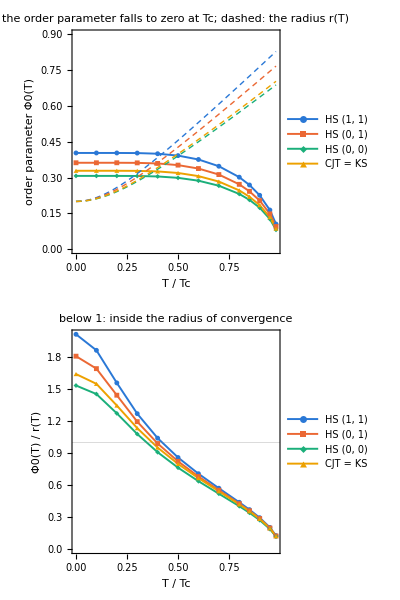

```mathematica
(* the figure, first cell: top, the order parameter Phi0(T) of the Rust table (points and lines) and the radius r(T)
   computed by the notebook (dashed), against T/T_c (KS and CJT coincide; one curve for both); bottom, the ratio
   Phi0(T)/r(T) (below 1: inside the radius of convergence); one panel above the other, so that the two fit the width
   and the height of a printed page *)
thShown = {"HS_1_1", "HS_0_1", "HS_0_0", "CJT"};
thLegend = {"HS (1, 1)", "HS (0, 1)", "HS (0, 0)", "CJT = KS"};
thColors = {RGBColor["#2a78d6"], RGBColor["#eb6834"], RGBColor["#1baf7a"], RGBColor["#eda100"]};
Column[{
  Show[ListLinePlot[Table[Table[{tau, thGet[t, tau, "Phi0"]}, {tau, thTaus}], {t, thShown}],
     PlotStyle -> Table[Directive[thColors[[i]], AbsoluteThickness[1.4]], {i, 4}], PlotMarkers -> {Automatic, 5},
     PlotLegends -> Placed[thLegend, {Left, Top}], Frame -> True, FrameLabel -> {"T / Tc", "order parameter Φ0(T)"},
     PlotRange -> {0, 0.9}, ImageSize -> {460, 260}, AspectRatio -> Full,
     PlotLabel -> "the order parameter falls to zero at Tc; dashed: the radius r(T)"],
   ListLinePlot[Table[Table[{tau, thRadius[t, tau]}, {tau, 0., 0.98, 0.02}], {t, thShown}],
     PlotStyle -> Table[Directive[thColors[[i]], AbsoluteThickness[1.], AbsoluteDashing[{4, 3}]], {i, 4}]]],
  ListLinePlot[Table[Table[{tau, thGet[t, tau, "Phi0"]/thRadius[t, tau]}, {tau, thTaus}], {t, thShown}],
   PlotStyle -> Table[Directive[thColors[[i]], AbsoluteThickness[1.4]], {i, 4}], PlotMarkers -> {Automatic, 5},
   PlotLegends -> Placed[thLegend, {Right, Top}], Frame -> True, FrameLabel -> {"T / Tc", "Φ0(T) / r(T)"},
   GridLines -> {None, {1}}, ImageSize -> {460, 260}, AspectRatio -> Full, PlotLabel -> "below 1: inside the radius of convergence"]},
 Spacings -> 1.5]
```

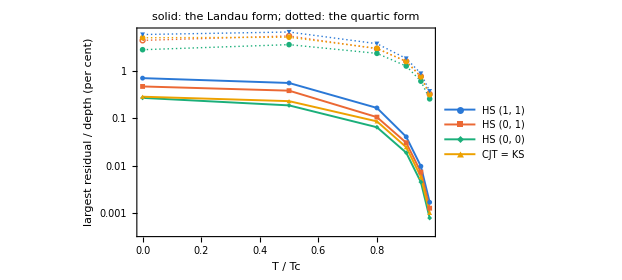

```mathematica
(* the figure, second cell: the residuals of the Landau form (solid) and of the quartic form (dotted) recomputed by the
   notebook, relative to the depth, in per cent (logarithmic scale), against T/T_c; the colors of the methods as above *)
ListLogPlot[Join[Table[Table[{tau, 100 thRes[t][tau][[1]]}, {tau, thCurveTaus}], {t, thShown}],
   Table[Table[{tau, 100 thRes[t][tau][[2]]}, {tau, thCurveTaus}], {t, thShown}]], Joined -> True,
 PlotStyle -> Join[Table[Directive[thColors[[i]], AbsoluteThickness[1.4]], {i, 4}], Table[Directive[thColors[[i]], AbsoluteThickness[1.], AbsoluteDashing[{1, 2}]], {i, 4}]],
 PlotMarkers -> {Automatic, 5}, PlotLegends -> Placed[thLegend, {Left, Bottom}], Frame -> True,
 FrameLabel -> {"T / Tc", "largest residual / depth (per cent)"}, ImageSize -> {460, 280}, AspectRatio -> Full,
 PlotLabel -> "solid: the Landau form; dotted: the quartic form"]
```

Is the order parameter smaller and more physically reasonable? Yes, near the critical temperature, and only there, for the mean-field free energy of the methods (Section III.G shows that these temperatures lie inside the critical region of the transition, where the fluctuations that the methods omit dominate).

It is smaller. Φ_(0,SF)^X(T) keeps its value of T==0 up to about 0.3 T_SF^(X,c) (the gap is much larger than these temperatures, and thermal quasi-particles are exponentially rare), then falls and vanishes continuously at T_SF^(X,c), like (1-T/T_SF^(X,c))^(1/2) (the table and the figure above).

It lies inside the radius of convergence. At T==0 the order parameter is 1.5 to 2 times the radius, which is then the mass m_LL; above the reduced temperature of the table (0.35 to 0.42) it is smaller than the radius, and near T_SF^(X,c) much smaller. There the series of the free energy in powers of (|Φ⃗|)^2 converges at the minimum, and the Landau coefficients are the Taylor coefficients of the free energy: the regime of Landau's theory, which Section III.L found absent at T==0.

The Landau form becomes exact. The residual of the Landau form falls from a few tenths of a per cent of the depth at T==0 to about 10^-3 per cent at 0.98 T_SF^(X,c), and that of the quartic form (the form of the Higgs potential of the Standard Model and of the theory of Ginzburg and Landau) from 3 to 6 per cent to about 0.3 per cent; near T_SF^(X,c) it falls in proportion to 1-T/T_SF^(X,c).

Landau's theory predicts the order parameter. Near T_SF^(X,c) the error of (-a/2b)^(1/2) is a fraction (0.19 to 0.28 in the Rust table) of 1-T/T_SF^(X,c), as Landau's theory requires; the cell above computes it for CJT at 0.9 T_SF^(CJT,c).

The scales. Near T_SF^(X,c) the order parameter is small also against the Dirac mass and the cutoff. The critical temperatures themselves are about a fifth to a quarter of the cutoff (the table above), and the states at the cutoff are occupied by 0.8 to 1.8 per cent at 0.98 T_SF^(X,c), so the thermal physics reaches the cutoff only weakly. The ratio of the gap at T==0 to T_SF^(X,c) is 1.65 to 1.74; the theory of Bardeen, Cooper and Schrieffer gives π e^-γ_E==1.764 (with Euler's constant γ_E==0.5772) for weak pairing at a Fermi surface. The ratios are of the same size but not equal: here there is no Fermi surface (μ_LL==0), the pairing needs a coupling above a critical one, and the gap contains the Dirac mass.

## III.T.7 What the free energy of these methods does not contain, and why it matters

The remark. All three methods give mean-field free energies: the thermal state is quasi-free, so the free energy contains the thermal quasi-particles of the spinor field, but neither the thermal fluctuations of the order parameter about its mean value (its amplitude, Goldstone and non-unitary modes) nor thermal gauge fields. Why it holds. A quasi-free state is a state whose correlations of four and more fields are fixed by its correlations of two fields (Wick's theorem); the three methods choose the best such state, and a fluctuation of the order parameter is a correlation of two pairs beyond the product of the pair densities. In HS the integral over the auxiliary fields is replaced by its saddle point, in CJT the effective action is truncated at the contractions of the contact terms in pairs, and in KS the exchange-correlation energy has no thermal part.

Why it matters. Near a continuous transition the fluctuations of the order parameter grow without bound. Their size relative to the order parameter is measured by the Ginzburg number of the transition (A. P. Levanyuk 1959, V. L. Ginzburg 1960): the mean-field free energy is accurate where 1-T/T_SF^(X,c) is much larger than the Ginzburg number, and it fails within the critical region, where it is smaller. For a free energy of the form of Ginzburg and Landau in three dimensions, γ_GL(|∇ψ_GL|)^2+α'_GL(T/T_c-1)(|ψ_GL|)^2+1/2 β_GL(|ψ_GL|)^4 (the example of Section III.L.2 with the gradient coefficient γ_GL, the slope α'_GL and the critical temperature T_c), the Ginzburg number is T_c^2 β_GL^2/(α'_GL γ_GL^3) up to a numerical factor that depends on the conventions. Within the critical region the order parameter vanishes with an exponent different from 1/2 (in three dimensions near 0.33 to 0.37 for the Ising, XY and Heisenberg universality classes), the critical temperature is in general lower than the mean-field one, and for an order parameter with two quartic invariants, as here, the fluctuations can also make the transition discontinuous (the renormalization-group theory of such fields is reviewed by A. Pelissetto and E. Vicari, 2002). A gauge field coupled to the order parameter can do the same: its fluctuations make the transition of a superconductor weakly first order (B. I. Halperin, T. C. Lubensky and S.-k. Ma, 1974), and the thermal transition of the Higgs field of the electroweak theory, of first order for small Higgs masses, ends at a critical Higgs mass, above which there is no transition but a smooth crossover (lattice simulations of K. Kajantie, M. Laine, K. Rummukainen and M. Shaposhnikov, 1996). The answer of Section III.T.6 therefore describes the superfluid near T_SF^(X,c) only outside the critical region, and whether the transition of the full theory is continuous is not decided here. The size of the critical region needs the gradient coefficient of the field at T_SF^(X,c), which Section III.G computes: the Ginzburg number is 7.6 to 11.4, so that the whole range of temperatures of Section III.T.6 where the free energy behaves as Landau's theory lies inside the critical region. At T==0 the methods omit the quantum fluctuations of the order parameter as well; that is a property of the methods, not the subject of this remark.

## Part III, third section. The width of the critical region, and the superfluid as a Higgs sector

On 21 November 2026 the author asked to find how wide the region of the fluctuations near the critical temperature is, which needs one more calculation, the gradient coefficient of the field at the critical temperature; then to determine for each of the five methods X (HS (1,1), HS (0,1), HS (0,0), KS and CJT) whether the superfluid can play the role of the Higgs particle, and whether the Higgs is really a composite particle. This chapter does both with the engines of Part II and of Section III.T, and repeats the checks of the Rust program sf_part3 (modules ginzburg and higgs) and of the Python program sf_part3.py. The answers. The Ginzburg number is 7.6 to 11.4 (Section III.G.7): the critical region is wider than the critical temperature itself, so the mean-field description of the five methods holds nowhere near the transition. Every method realizes the Higgs mechanism and has a composite neutral scalar below the threshold of two quasi-particles, but in no method can it be the Higgs boson that is observed (Section III.G.8). Within this model the Higgs field is composite by construction.

## III.G.1 The free energy of Ginzburg and Landau and the Ginzburg number

Units. As in Section III.T: k_B==1, the cutoff Λ_LL==1, the chemical potential zero. The field. The field of the superfluid is the complex isospin vector Φ⃗==(Φ^1,Φ^2,Φ^3) of the components of the pair self-energy along (K_LL^ι)^†, Φ^ι==tr(K_LL^ι P_SF)/8; it has n_SF^Φ==6 real components, and (|Φ⃗|)^2==∑_ι (|Φ^ι|)^2. The form of Ginzburg and Landau. Near the critical temperature T_SF^(X,c) the field is small. For a static field that varies slowly in space, the free energy of method X to second order in the field and in its derivatives and to fourth order in the field is

ℱ_SF^(X,GL)[Φ⃗]==∫ d^3 x[c_SF^X ∑_(j==1)^3 (∂_j Φ⃗)^†·∂_j Φ⃗+a_SF^(X,Tay)(T) (|Φ⃗|)^2+b_SF^(X,Tay)(T) (|Φ⃗|)^4],

with the Taylor coefficients a_SF^(X,Tay), b_SF^(X,Tay) of the free energy at the origin (Section III.T.6), a_SF^(X,Tay)(T)≈α_SF^(X,GL)t_SF^red near T_SF^(X,c), the reduced temperature t_SF^red==(T-T_SF^(X,c))/T_SF^(X,c), the slope α_SF^(X,GL)==T_SF^(X,c) ∂_T a_SF^(X,Tay) at T_SF^(X,c), and the gradient coefficient c_SF^X at T_SF^(X,c). The rotations and the isospin rotations allow no other term of second order, and a term with Φ⃗·Φ⃗ has the fermion number 4 and is not invariant under U(1)_LL^F. Of the two quartic invariants (|Φ⃗|)^4 and (|Φ⃗·Φ⃗|)^2, which are equal on the polar fields of the minimum, the form keeps the coefficient along these fields. The Ginzburg number. Above T_SF^(X,c) the field fluctuates about zero with the probability density proportional to exp(-ℱ_SF^(X,GL)/T). To second order the fluctuations are Gaussian, and their free energy per volume is, up to terms analytic in T, 1/2 n_SF^Φ T ∫ (d^3 k)/(2π)^3 ln(c_SF^X k^2+a_SF^(X,Tay)). With ∫ (d^3 k)/(2π)^3(c k^2+a)^-2==(8π c^(3/2)a^(1/2))^-1 its specific heat per volume, C==-T∂_T^2 of the free energy, is near T_SF^(X,c)

C_SF^(X,fl)==(n_SF^Φ (α_SF^(X,GL))^(3/2))/(16π (c_SF^X)^(3/2) (t_SF^red)^(1/2)),      Δ C_SF^X==((α_SF^(X,GL))^2)/(2 b_SF^(X,Tay) T_SF^(X,c)),

where Δ C_SF^X is the jump of the specific heat of mean-field theory at T_SF^(X,c) (below it the minimum of the form is (|Φ⃗|)^2==-a/(2b) with the free energy -a^2/(4b) per volume). Mean-field theory holds where C_SF^(X,fl)≪Δ C_SF^X. The two are equal at the Ginzburg number (A. P. Levanyuk 1959, V. L. Ginzburg 1960)

Gi_SF^X==((n_SF^Φ)^2 (b_SF^(X,Tay))^2 (T_SF^(X,c))^2)/(64 π^2 α_SF^(X,GL) (c_SF^X)^3)==((n_SF^Φ)^2)/(256 π^2(Δ C_SF^X(ξ_SF^(X,GL))^3)^2),      ξ_SF^(X,GL)==(c_SF^X/α_SF^(X,GL))^(1/2).

Mean-field theory holds for |t_SF^red|≫Gi_SF^X, and the critical region, where it fails, has the width of about Gi_SF^X T_SF^(X,c) on both sides of T_SF^(X,c). The second form shows the meaning: the correlation length of mean-field theory is ξ_SF^(X,GL)(|t_SF^red|)^(-1/2), and mean-field theory needs many degrees of freedom in a correlation volume, Δ C_SF^X(ξ_SF^(X,GL))^3≫1. A remark on the factors (what it means and why it matters). Other forms of the criterion (the mean square fluctuation of the field in a correlation volume against the square of its mean value, or the first correction to b_SF^(X,Tay) against b_SF^(X,Tay)) give the same combination of α, b, c and T_c with other numerical factors of order one, and books on the subject differ by such factors. The formula above is the definition used here. It matters only when the number is near 1; the numbers found below are far above 1, so a factor of order one does not change the conclusion.

## III.G.2 The coefficient of the field of a moving pair: the static pair response

A pair field with the momentum q_SF^pair along (e⃗)_3, Φ⃗(x⃗)==Φ⃗ e^(i q_SF^pair x^3), has the gradient term c_SF^X(q_SF^pair)^2(|Φ⃗|)^2, so its coefficient of (|Φ⃗|)^2 is a_SF^(X,Tay)(q_SF^pair;T)==a_SF^(X,Tay)(T)+c_SF^X(q_SF^pair)^2+O((q_SF^pair)^4). The state of a moving pair pairs the momenta q⃗+1/2 q_SF^pair(e⃗)_3 and -q⃗+1/2 q_SF^pair(e⃗)_3 (relative momentum q⃗). After the gauge transformation Ψ→e^(i q_SF^pair x^3/2)Ψ, which makes the pair field uniform, it is the thermal state of the matrix of Bogoliubov and de Gennes (Section II.2) with h_LL(±q⃗) replaced by h_LL(±q⃗)+T_SF^tw, the twist T_SF^tw==1/2 q_SF^pair α_LL^3⊗1_2, with the normal self-energy N_SF^n of the normal state at T (a change of the normal self-energy changes the free energy only at fourth order in the field, because the free energy is stationary in it) and with a small antisymmetric pair block P_SF^a. To first order in P_SF^a the pair matrix summed over the momenta, C_SF^(p,tot)==∫ (d^3 q)/(2π)^3 C_LL^p(q⃗), is the static pair response

C_SF^(p,tot)==𝒳_SF^P[P_SF^a]==-∫ (d^3 q)/(2π)^3 ∑_(a,b==1)^8 (f(ε_(SF,a)^A)-f(ε_(SF,b)^D))/(ε_(SF,a)^A-ε_(SF,b)^D) u_(SF,a)u_(SF,a)^† P_SF^a w_(SF,b)w_(SF,b)^†,

where ε_(SF,a)^A and the normalized eigenvectors u_(SF,a) are those of the particle block h_LL(q⃗)+N_SF^n+T_SF^tw, ε_(SF,b)^D and w_(SF,b) those of the hole block -(h_LL(-q⃗)+N_SF^n+T_SF^tw)^T, f is the Fermi function, and the quotient is f'(ε) where the two energies coincide (the first-order term of the function f(H_SF) of a Hermitian matrix in its off-diagonal block). The free energy of the state, measured from the normal state at T, is to second order

ℱ_(2,SF)^X==1/2 Re tr((P_SF^a-P_SF[C_SF^(p,tot)])(C_SF^(p,tot))^†),

where P_SF[C_SF^(p,tot)] is the pair self-energy of method X for the pair matrix C_SF^(p,tot) (Section II.2; linear in it, and it contains every pair channel of the method, not only the channels K_LL^ι). Derivation. The expectation value of the pair term of the BdG Hamiltonian is ⟨V⟩==-Re tr(P_SF^a(C_SF^(p,tot))^†); the thermal state of the Hamiltonian with the pair term has the thermodynamic potential 1/2⟨V⟩ below that of the normal state (second-order perturbation theory); the free energy of the method contains this potential minus ⟨V⟩ (the pair term is not part of the Hamiltonian of the model) plus the pair part of the interaction energy, which is quadratic in the pair matrix and equals -1/2Re tr(P_SF[C_SF^(p,tot)](C_SF^(p,tot))^†); the sum is the formula above. The field of the state is Φ^3==tr(K_LL^3 P_SF[C_SF^(p,tot)])/8. The free energy of the field is the smallest ℱ_(2,SF)^X among the states with this field: the components of P_SF^a along (K_LL^1)^†, (K_LL^2)^†, (K_LL^3)^† are held at (0,0,1), and its components along the other 25 antisymmetric matrices are made self-consistent (a linear system of 25 complex unknowns: the stationarity of the free energy with a Lagrange multiplier for the field). Then a_SF^(X,Tay)(q_SF^pair;T)==ℱ_(2,SF)^X/(|Φ^3|)^2. At q_SF^pair==0 and in the channel K_LL^3 alone this is

a_SF^(X,Tay)(0;T)==(1-λ_SF^P(T))/(λ_SF^P(T) g_SF^(X,P)),

with the eigenvalue λ_SF^P(T) of Section III.T.4: the applied block (K_LL^3)^† produces the field Φ^3==λ_SF^P(T), and the formula for ℱ_(2,SF)^X gives 1/2(1-λ_SF^P)·2 λ_SF^P/g_SF^(X,P). Hence the slope in closed form, α_SF^(X,GL)==-T_SF^(X,c) ∂_T λ_SF^P/(λ_SF^P)^2 g_SF^(X,P) at T_SF^(X,c). The engine. The next cell defines the static pair response on any set of momenta with weights, the quadratic free energy of the field, the normal self-energy at T, and the coefficient for a twist q α_LL^3⊗t with an isospin matrix t: t==1_2 moves the pair (fermion number 2) with q_SF^pair==2q; t==1/2 τ_1 turns the isospin direction of the field (its components of charge ±1 of T_LL^1 get the momenta ±q), and must give the same coefficient by the isospin invariance of the form.

```mathematica
(* ---- the static pair response and the quadratic free energy of a field (Section III.G.2) ---- *)
(* gzPairs: the 28 index pairs {a, b}, a < b; gzBasis: the antisymmetric basis matrices E_ab - E_ba *)
gzPairs = Flatten[Table[{a, b}, {a, 8}, {b, a + 1, 8}], 1];
gzBasis = Map[Function[pr, Table[Which[{i, j} == pr, 1., {j, i} == pr, -1., True, 0.], {i, 8}, {j, 8}]], gzPairs];
(* gzCoeffs[p]: the coefficients of an antisymmetric matrix in this basis (its entries above the diagonal);
   gzFromCoeffs[v]: the antisymmetric matrix of the coefficients v *)
gzCoeffs[p_] := Map[p[[#[[1]], #[[2]]]] &, gzPairs];
gzFromCoeffs[v_] := v . gzBasis;
(* gzAlpha8[j]: alpha^j_LL (x) 1_2 (numerical); gzH[q]: the free matrix h_LL(q) = (beta m_LL + alpha . q) (x) 1_2 *)
gzAlpha8 = Table[N[d8[alphaLL[j]]], {j, 3}];
gzH[q_] := N[mLL] b8 + q[[1]] gzAlpha8[[1]] + q[[2]] gzAlpha8[[2]] + q[[3]] gzAlpha8[[3]];
(* gzTwist[q, t2]: the twist q alpha^3_LL (x) t2 (t2 a 2 x 2 isospin matrix) *)
gzTwist[q_, t2_] := q N[d8[alphaLL[3]] . i8[t2]];
(* gzDF[e1, e2, t]: (f(e1) - f(e2))/(e1 - e2), and f'(e) = -f (1 - f)/t where the two energies coincide *)
gzDF[e1_, e2_, t_] := If[Abs[e1 - e2] < 10^-7, With[{f = fermiSF[0.5 (e1 + e2), t]}, -f (1 - f)/t], (fermiSF[e1, t] - fermiSF[e2, t])/(e1 - e2)];
(* gzResponse[qs, ws, ns, x, t]: the static pair response X^P of the 28 basis matrices at the temperature t on the
   momenta qs with the weights ws of int d^3q/(2 pi)^3, for the normal self-energy ns and the twist x.  At each node:
   the eigenvalues ea and eigenvectors (rows of va) of the particle block A = h(q) + N + X, ed and vd of the hole block
   D = -(h(-q) + N + X)^T; with L = conj(va) and R = vd the matrix U_A^dag (E_ab - E_ba) U_D has the entries
   L[k, a] R[l, b] - L[k, b] R[l, a]; it is multiplied entry by entry with F[k, l] = gzDF[ea_k, ed_l, t] and turned
   back with U_A = transpose(va) and U_D^dag = conj(vd) *)
gzResponse[qs_, ws_, ns_, x_, t_] := Module[{out = ConstantArray[0. I, {28, 8, 8}]},
   Do[Module[{a, d, ea, va, ed, vd, l, r, fm, ua},
      a = gzH[qs[[n]]] + ns + x;
      d = -Transpose[gzH[-qs[[n]]] + ns + x];
      {ea, va} = Eigensystem[0.5 (a + ConjugateTranspose[a])];
      {ed, vd} = Eigensystem[0.5 (d + ConjugateTranspose[d])];
      {ea, ed} = Re[{ea, ed}];
      l = Conjugate[va]; r = vd; ua = Transpose[va];
      fm = Table[gzDF[ea[[k]], ed[[m]], t], {k, 8}, {m, 8}];
      out -= ws[[n]] Map[Function[pr, ua . ((Outer[Times, l[[All, pr[[1]]]], r[[All, pr[[2]]]]] - Outer[Times, l[[All, pr[[2]]]], r[[All, pr[[1]]]]]) fm) . Conjugate[vd]], gzPairs]],
     {n, Length[qs]}];
   out];
(* gzQuad[ts, chi, relax]: the coefficient a = F_2/|Phi^3|^2 of the field for the response chi (28 matrices) of the
   contact terms ts; the components of P^a along (K^1)^dag, (K^2)^dag, (K^3)^dag are held at (0, 0, 1) and, with relax,
   the other 25 are made self-consistent: (1 - Pi_perp M) p_perp = Pi_perp M e3, with the linear map M (column j: the
   pair self-energy of the method for the pair matrix chi_j) and the projection Pi_perp that removes the components
   along the three (K^iota)^dag; returns {a, the norm of p_perp} *)
gzQuad[ts_, chi_, relax_ : True] := Module[{cols, kd, perp, amat, pp, p, kap, pm, phi, pnorm = 0.},
   cols = Transpose[Map[gzCoeffs[interaction[ts, zero8, #][[3]]] &, chi]];
   kd = Table[gzCoeffs[ConjugateTranspose[k8[i]]], {i, 3}];
   perp[v_] := v - Sum[kd[[i]] Tr[k8[i] . gzFromCoeffs[v]]/8, {i, 3}];
   p = kd[[3]];
   If[relax,
     amat = IdentityMatrix[28] - Transpose[Map[perp, Transpose[cols]]];
     pp = LinearSolve[amat, perp[cols . kd[[3]]]];
     pnorm = Norm[pp]; p = kd[[3]] + pp];
   kap = p . chi;
   pm = interaction[ts, zero8, kap][[3]];
   phi = Tr[k8[3] . pm]/8;
   {0.5 Re[Tr[(gzFromCoeffs[p] - pm) . ConjugateTranspose[kap]]]/Abs[phi]^2, pnorm}];
(* gzNormal[t, temp]: the normal self-energy of the method t at the temperature temp (thermal engine, P = 0) *)
gzNormal[t_, temp_] := gzNormal[t, temp] = solveSFT[thModel[t], zero8, zero8, temp, 0.6, 10^-14]["n"];
(* gzA[t, temp, q, t2, relax, nodes]: {a, |p_perp|} of the method t at the temperature temp for the twist q alpha^3 (x) t2,
   on the nodes {qs, ws} (default: the 24 x 6 momenta of the grid of the method) *)
gzA[t_, temp_, q_, t2_, relax_ : True, nodes_ : Automatic] := Module[{mo = thModel[t], qs, ws},
   {qs, ws} = If[nodes === Automatic, {mo["g"]["q"], mo["g"]["w"]}, nodes];
   gzQuad[mo["ts"], gzResponse[qs, ws, gzNormal[t, temp], gzTwist[q, t2], temp], relax]];
Print["the static pair response is defined (", Length[gzPairs], " basis matrices)"];
```

the static pair response is defined (28 basis matrices)

## III.G.3 The values of the Rust program

The closed cell holds the results of the modules ginzburg and higgs of the Rust program: rustGinzburg (per method: the critical temperature, the Dirac mass of the normal state at it, the coefficients α_SF^(X,GL), b_SF^(X,Tay), c_SF^X, the gradient coefficient of the isospin twist, of the fixed channels, of the twist of T_LL^3 and of the twisted states, the two values of the extrapolation, the norms of the other channels, a at T_SF^(X,c), the Ginzburg number, the width, ξ_SF^(X,GL) and the field at the edge of the critical region), rustGinzburgRegions (the two regularizations of Section III.G.5) and rustHiggs (the numbers of Section III.G.8, with a last row of the Standard Model).

```mathematica
(* The values of the Rust programs that Section III.G of Part III of the notebook uses or compares with its own results, written by
   wolfram/tools/make_data_cells.py from the data files of the folder data/ (do not edit):
     data/part3_ginzburg.csv   SHA-256 792891d8f448384be6b4220806b9db339f60ea76d47db109de0b002f0f93b98c
     data/part3_ginzburg_regions.csv   SHA-256 8838a87b0a15124b283f32962b18148fbf6b08b0e4101a355689e2abeaf63b0c
     data/part3_higgs.csv   SHA-256 b660c129254e86955c47f5acfb92388fd63329a23030e2fe38ebdbbaa149ab7e
*)
rustGinzburg = {
   {"HS_1_1", 2.60467239400117845*^-1, 2.06685193247417187*^-1, 1.40378852286601515*^-2, 1.23885669001889999*^-2, 1.54874757731276545*^-2, 1.54874757735682655*^-2, 1.54874757731239820*^-2, 3.21790581427641156*^-3, 1.72264233783694376*^-2, 1.54876191783189510*^-2, 1.54880493938928353*^-2, 1.08947049901315593*^-33, 2.22044604925031308*^-16, 3.08395284618099299*^-17, 1.13796139519282296*^1, 2.96401663149781136*^0, 1.05036314848757795*^0, 2.53915419579518575*^0},
   {"HS_0_1", 2.40465456326528326*^-1, 2.00000000000000011*^-1, 1.26991375470483451*^-2, 1.37640001327261115*^-2, 1.71375864679217671*^-2, 1.71375864679765254*^-2, 1.71380412304669855*^-2, 3.39527400004123242*^-3, 1.90490821203379394*^-2, 1.71377369789805847*^-2, 1.71381885121570376*^-2, 1.92882547862793531*^-16, 1.57437429875642641*^-4, 1.14420944374633792*^-16, 9.76774488278727837*^0, 2.34880523052055468*^0, 1.16168321928489537*^0, 2.12274064544459007*^0},
   {"HS_0_0", 2.13799098394113596*^-1, 2.00000000000000011*^-1, 1.07433853469421827*^-2, 1.59433868098272646*^-2, 1.95279852896392582*^-2, 1.95279852896997827*^-2, 1.95280961347185783*^-2, 3.59690040841231665*^-3, 1.95280500390747486*^-2, 1.95281299677136054*^-2, 1.95285640019366435*^-2, 1.11571589324023134*^-16, 7.72106031448887843*^-5, 2.22513053458628538*^-17, 8.27717647498158371*^0, 1.76965286760003004*^0, 1.34821185901816798*^0, 1.66996125380577820*^0},
   {"KS", 2.22118737059346372*^-1, 1.62292932454751765*^-1, 1.11755227895139128*^-2, 1.47237362726968385*^-2, 1.92717761564147466*^-2, 1.92717761560858049*^-2, 1.92718491171982448*^-2, 3.59712044339499095*^-3, 2.12099250116375808*^-2, 1.92719290983241233*^-2, 1.92723879240522568*^-2, 3.13461279903241512*^-16, 6.16470698958192633*^-5, -3.27913973517978480*^-17, 7.62072264146640954*^0, 1.69270528860208502*^0, 1.31318812578790389*^0, 1.70062276866892526*^0},
   {"CJT", 2.22118737059346427*^-1, 1.62292932454751765*^-1, 1.11755227895107608*^-2, 1.47237367640560037*^-2, 1.92717761563698450*^-2, 1.92717761561141294*^-2, 1.92718491173168131*^-2, 3.59712044328470634*^-3, 7.68416208499430459*^-3, 1.92719290983007011*^-2, 1.92723879240932691*^-2, 2.21818378745134374*^-16, 6.16470698958192226*^-5, -3.04491546838122896*^-17, 7.62072315015793933*^0, 1.69270540159200555*^0, 1.31318812578655941*^0, 1.70062279705138164*^0}};
rustGinzburgRegions = {
   {"HS_1_1", 5.00000000000000010*^-3, 3.87188024956259375*^-7, 1.20034664859369094*^-4, 1.54875209982503741*^-2, 2.40069329718738192*^-2},
   {"HS_1_1", 1.00000000000000002*^-2, 1.54876566463802064*^-6, 2.41739412711171428*^-4, 1.54876566463802053*^-2, 2.41739412711171435*^-2},
   {"HS_1_1", 2.00000000000000004*^-2, 6.19527970202025347*^-6, 4.90235066197823588*^-4, 1.54881992550506328*^-2, 2.45117533098911794*^-2},
   {"HS_1_1", 4.00000000000000008*^-2, 2.47845919019055561*^-5, 1.00811964161823622*^-3, 1.54903699386909725*^-2, 2.52029910404559035*^-2},
   {"HS_0_1", 5.00000000000000010*^-3, 4.28440930523045044*^-7, 1.21540880638091900*^-4, 1.71376372209218024*^-2, 2.43081761276183785*^-2},
   {"HS_0_1", 1.00000000000000002*^-2, 1.71377894628483862*^-6, 2.44841709539582127*^-4, 1.71377894628483851*^-2, 2.44841709539582106*^-2},
   {"HS_0_1", 2.00000000000000004*^-2, 6.85535937974615447*^-6, 4.96804055246411391*^-4, 1.71383984493653843*^-2, 2.48402027623205700*^-2},
   {"HS_0_1", 4.00000000000000008*^-2, 2.74253355386568865*^-5, 1.02275610258681219*^-3, 1.71408347116605540*^-2, 2.55689025646703046*^-2},
   {"HS_0_0", 5.00000000000000010*^-3, 4.88201045520006043*^-7, 1.23038177759488644*^-4, 1.95280418208002397*^-2, 2.46076355518977281*^-2},
   {"HS_0_0", 1.00000000000000002*^-2, 1.95282113587988499*^-6, 2.47960802118318900*^-4, 1.95282113587988485*^-2, 2.47960802118318904*^-2},
   {"HS_0_0", 2.00000000000000004*^-2, 7.81155581899443057*^-6, 5.03547085998204890*^-4, 1.95288895474860745*^-2, 2.51773542999102450*^-2},
   {"HS_0_0", 4.00000000000000008*^-2, 3.12505644790463512*^-5, 1.03831831480755664*^-3, 1.95316027994039687*^-2, 2.59579578701889142*^-2},
   {"KS", 5.00000000000000010*^-3, 4.81795833411380726*^-7, 1.23360088843867848*^-4, 1.92718333364552269*^-2, 2.46720177687735701*^-2},
   {"KS", 1.00000000000000002*^-2, 1.92720048829161356*^-6, 2.48595449156926442*^-4, 1.92720048829161349*^-2, 2.48595449156926440*^-2},
   {"KS", 2.00000000000000004*^-2, 7.70907642529434813*^-6, 5.04779027927538225*^-4, 1.92726910632358694*^-2, 2.52389513963769095*^-2},
   {"KS", 4.00000000000000008*^-2, 3.08406979901001895*^-5, 1.04062740268500353*^-3, 1.92754362438126159*^-2, 2.60156850671250869*^-2},
   {"CJT", 5.00000000000000010*^-3, 4.81795833418407606*^-7, 1.23360088843886117*^-4, 1.92718333367363041*^-2, 2.46720177687772234*^-2},
   {"CJT", 1.00000000000000002*^-2, 1.92720048833553645*^-6, 2.48595449156926171*^-4, 1.92720048833553634*^-2, 2.48595449156926163*^-2},
   {"CJT", 2.00000000000000004*^-2, 7.70907642528615054*^-6, 5.04779027927536707*^-4, 1.92726910632153754*^-2, 2.52389513963768332*^-2},
   {"CJT", 4.00000000000000008*^-2, 3.08406979901177603*^-5, 1.04062740268501329*^-3, 1.92754362438236002*^-2, 2.60156850671253333*^-2}};
rustHiggs = {
   {"HS_1_1", 1.43089128369305013*^-1, 7.09657297912591467*^-2, 7.15445641846525066*^-2, 8.13693091685952385*^-1, 8.06128281194059992*^-1, 5.00811949292567504*^-2, 6.38691568121332320*^-2, 5.68661715225391617*^0, 1.61688073181542222*^1, 1.62474775778683345*^1, 8.98180621400120893*^-1, 9.90703115745743546*^-1, 9.91909456714287652*^-1, 7.84121748727123036*^-1, 3.92324395967846806*^0, 1.82031466938471054*^0, 1.72074568351915582*^3, 1.40015887522795924*^3, 7.79441707974802398*^2, 4.48197877895903389*^2},
   {"HS_0_1", 1.35449897539625219*^-1, 6.72333428539203387*^-2, 6.77249487698126096*^-2, 7.25083390995323374*^-1, 7.25083390995323374*^-1, 4.74074641388688225*^-2, 6.05100085685283048*^-2, 5.35314831658107160*^0, 1.43280984496573804*^1, 1.52947094759459201*^1, 8.76588493805381841*^-1, 1.00000000000000000*^0, 9.92741140084680285*^-1, 7.83464839294797044*^-1, 3.47078656765753824*^0, 1.77530925230992742*^0, 1.81779391843371104*^3, 1.31805217850859140*^3, 7.51807825349588938*^2, 4.37116644103750332*^2},
   {"HS_0_0", 1.22787921046353068*^-1, 6.13939607068401186*^-2, 6.13939605231765342*^-2, 6.14387383983286073*^-1, 6.14387383983286073*^-1, 4.29757723662235747*^-2, 5.52545646361561060*^-2, 5.00364676547745812*^0, 1.25182404768365156*^1, 1.42961336156498806*^1, 8.38432092915730731*^-1, 1.00000000000000000*^0, 1.00000000299155789*^0, 7.77777775451010567*^-1, 2.98850975817176545*^0, 1.74120627315942045*^0, 2.00524610158560040*^3, 1.23199790659585983*^3, 7.34703452435524582*^2, 4.28719808577312506*^2},
   {"KS", 1.31407856120486666*^-1, 7.13481657629282118*^-2, 6.57039280602433329*^-2, 6.03475966909225336*^-1, 6.57284727194539675*^-1, 4.59927496421703302*^-2, 6.42133491866353906*^-2, 4.59238880174640141*^0, 1.05450174532028758*^1, 1.31211108621325767*^1, 8.23541679322325582*^-1, 1.08916471116638225*^0, 1.08590411364005091*^0, 7.16249038941932592*^-1, 2.13489115008797237*^0, 1.69030028810216426*^0, 1.87370837078601403*^3, 1.13073797076599908*^3, 6.86509255789250801*^2, 4.16185736936514900*^2},
   {"CJT", 1.35319975382492214*^-1, 7.13481657629258387*^-2, 6.76599876912461068*^-2, 6.03475966909230443*^-1, 6.44007154633925660*^-1, 4.73619913838722734*^-2, 6.42133491866332534*^-2, 4.45962220436014434*^0, 9.94411510281102018*^0, 1.27417777267432708*^1, 8.23541679322332021*^-1, 1.06716288625755928*^0, 1.05451047506112561*^0, 7.37572358143425033*^-1, 2.13489115008815000*^0, 1.64143347226830993*^0, 1.81953920183653918*^3, 1.09804817915755484*^3, 6.66662177961111865*^2, 4.04153749541903323*^2},
   {"SM", 2.46219999999999999*^2, Indeterminate, 1.23109999999999999*^2, 1.25200000000000003*^2, Indeterminate, 8.03692000000000064*^1, 9.11880000000000024*^1, 5.08488343757615202*^-1, 1.29280197868681307*^-1, 1.55781070360287255*^0, Indeterminate, Indeterminate, Indeterminate, 8.81357196122296793*^-1, Indeterminate, Indeterminate, Indeterminate, Indeterminate, Indeterminate, Indeterminate}};

Print["rows: ", Length[rustGinzburg], " (Ginzburg), ", Length[rustGinzburgRegions], " (regions), ", Length[rustHiggs], " (Higgs, with the Standard Model)"];
```

rows: 5 (Ginzburg), 20 (regions), 6 (Higgs, with the Standard Model)

```mathematica
(* gzRust[t, key]: an entry of rustGinzburg; hgRust[t, key]: an entry of rustHiggs (t = "SM" for the Standard Model) *)
gzCols = AssociationThread[{"method", "Tc", "massN", "alpha", "b", "c", "cIso", "cFixed", "cT3", "cTwisted", "c1", "c2", "perp0", "perpK", "aTc", "Gi", "width", "xi0", "PhiG"} -> Range[19]];
gzRust[t_, key_] := First[Select[rustGinzburg, #[[1]] == t &]][[gzCols[key]]];
hgCols = AssociationThread[{"method", "v", "fF", "fI", "MH", "MNU", "MW", "MZ", "MHv", "lambda", "MHMW", "MH2gap", "MNUMH", "fFfI", "MWMZ", "width", "Tcv", "LambdaGeV", "MHGeV", "gapGeV", "TcGeV"} -> Range[21]];
hgRust[t_, key_] := First[Select[rustHiggs, #[[1]] == t &]][[hgCols[key]]];
Print["the critical temperatures of the Rust program: ", N[Map[gzRust[#, "Tc"] &, thTags]]];
```

the critical temperatures of the Rust program: {0.260467,0.240465,0.213799,0.222119,0.222119}

## III.G.4 The coefficient at zero pair momentum and the slope

The next cell computes, for every method with its own critical temperature (Section III.T.4), the coefficient at zero pair momentum from the static pair response and checks it four ways: at 0.9 T_SF^(X,c) it is the Taylor coefficient of the nonlinear free energy of the Rust table (Section III.T); at T/T_SF^(X,c)==0.9, 0.998, 1.002 it is (1-λ_SF^P)/(λ_SF^P g_SF^(X,P)) with the eigenvalue of Section III.T.4; at T_SF^(X,c) it vanishes; and no other pair channel is induced. The slope α_SF^(X,GL) is computed twice: from central differences of the coefficient at T_SF^(X,c)(1±0.002) and T_SF^(X,c)(1±0.004) with the Richardson extrapolation, and in closed form with the derivatives of I_SF^(1) on the radial nodes,

∂_T I_SF^(1)==-1/(2 T^2) ∫_0^Λ_LL (q^2 dq)/(cosh^2(E_M/2T)),      ∂_M I_SF^(1)==∫_0^Λ_LL q^2 M/E_M[1/(2T E_M cosh^2(E_M/2T))-(tanh(E_M/2T))/E_M^2]dq,

and the derivative of the Dirac mass of the normal state from the implicit function theorem applied to its scalar self-consistency M-m_LL==g_SF^(X,S)n_SF^S(M,T) (Section III.T.4): ∂_T M==g_SF^(X,S)∂_T n_SF^S/(1-g_SF^(X,S)∂_M n_SF^S).

```mathematica
(* gzI1D[mo, m, temp]: {I1, dI1/dT, dI1/dM} on the radial nodes of the grid of the model mo (temp > 0) *)
gzI1D[mo_, m_, temp_] := Module[{kr = mo["g"]["kr"], wr = mo["g"]["wr"], e, x},
   e = Sqrt[kr^2 + m^2]; x = e/(2 temp);
   {Total[wr kr^2 Tanh[x]/e], -Total[wr kr^2 Sech[x]^2]/(2 temp^2), Total[wr kr^2 (m/e) (Sech[x]^2/(2 temp e) - Tanh[x]/e^2)]}];
(* gzAlphaClosed[t]: {alpha, lambda^P(T_c), M_n(T_c)} in closed form at the critical temperature of the notebook *)
gzAlphaClosed[t_] := Module[{mo = thModel[t], tc = thTc[t], gs, gp, mn, i1, i1t, i1m, i10, dnt, dnm, dmt, lam, dlam},
   {gs, gp} = thCoup[t];
   mn = thMassN[t, tc];
   {i1, i1t, i1m} = gzI1D[mo, mn, tc];
   dnt = -(2/Pi^2) mn i1t; dnm = -(2/Pi^2) (i1 + mn i1m);
   dmt = gs dnt/(1 - gs dnm);
   lam = gp i1/Pi^2; dlam = gp (i1t + i1m dmt)/Pi^2;
   {-tc dlam/(lam^2 gp), lam, mn}];
(* gzResults[t]: the results of the method t (association), filled by the cells of this section and the next *)
gzResults = <||>;
Do[Module[{tc = thTc[t], gp = thCoup[t][[2]], t09 = thGet[t, 0.9, "T"], a09, at, worst = 0., ac, perp0, d1, d2, alFD, alCl, lamC, mnC},
   (* at 0.9 T_c, against the Taylor coefficient of the nonlinear free energy of the Rust table *)
   a09 = gzA[t, t09, 0., IdentityMatrix[2]][[1]]; at = thGet[t, 0.9, "a"];
   check["WP3-G1 " <> t, thName[t] <> ": at 0.9 T_c the coefficient a(0) of |Phi|^2 from the static pair response (" <> sci[a09] <> ") equals the Taylor coefficient a^Tay of the nonlinear free energy of Section III.T (" <> sci[at] <> ") (relative difference)",
    Abs[a09 - at]/Abs[at], 10^-7, "P3-G1 " <> t, "YP3-G1 " <> t];
   (* the closed form at three temperatures *)
   Do[Module[{temp = tau tc, a, lam},
      a = gzA[t, temp, 0., IdentityMatrix[2]][[1]]; lam = thLam[t, temp];
      worst = Max[worst, Abs[a - (1 - lam)/(lam gp)]/Abs[(1 - lam)/(lam gp)]]], {tau, {0.9, 0.998, 1.002}}];
   check["WP3-G2 " <> t, thName[t] <> ": a(0, T) = (1 - lambda^P(T))/(lambda^P(T) g^P) at T/T_c = 0.9, 0.998, 1.002, with lambda^P(T) of Section III.T.4 (largest relative difference)",
    worst, 10^-9, "P3-G2 " <> t, "YP3-G2 " <> t];
   (* the slope: central differences with the Richardson extrapolation, and the closed form *)
   d1 = (gzA[t, 1.002 tc, 0., IdentityMatrix[2]][[1]] - gzA[t, 0.998 tc, 0., IdentityMatrix[2]][[1]])/(2 0.002 tc);
   d2 = (gzA[t, 1.004 tc, 0., IdentityMatrix[2]][[1]] - gzA[t, 0.996 tc, 0., IdentityMatrix[2]][[1]])/(2 0.004 tc);
   alFD = tc (4 d1 - d2)/3;
   {alCl, lamC, mnC} = gzAlphaClosed[t];
   check["WP3-G10 " <> t, thName[t] <> ": alpha = T_c da/dT = " <> ToString[NumberForm[alFD, 10]] <> " from central differences of the static pair response (Richardson) = " <> ToString[NumberForm[alCl, 10]] <> " in closed form (lambda^P(T_c) = " <> ToString[NumberForm[lamC, 12]] <> ", M_n = " <> ToString[NumberForm[mnC, 10]] <> ") = Rust (largest relative difference)",
    Max[Abs[alFD - alCl]/alCl, Abs[alCl - gzRust[t, "alpha"]]/gzRust[t, "alpha"]], 10^-8, "P3-G10 " <> t, "YP3-G10 " <> t];
   (* at the critical temperature: a vanishes, and no other pair channel is induced *)
   {ac, perp0} = gzA[t, tc, 0., IdentityMatrix[2]];
   check["WP3-G3 " <> t, thName[t] <> ": a(0, T_c) vanishes to the accuracy of T_c (|a(0, T_c)| / alpha)", Abs[ac]/alCl, 10^-9, "P3-G3 " <> t, "YP3-G3 " <> t];
   check["WP3-G4 " <> t, thName[t] <> ": at zero pair momentum no other pair channel is induced (norm of the self-consistent components of P^a other than (K^iota)^dag)", perp0, 10^-12, "P3-G4 " <> t, "YP3-G4 " <> t];
   gzResults[t] = <|"Tc" -> tc, "alpha" -> alCl, "alphaFD" -> alFD, "a0" -> ac|>], {t, thTags}];
```

PASS WP3-G1 HS_1_1  deviation 7.975e-10 (tolerance 1.000e-7): HS (1, 1): at 0.9 T_c the coefficient a(0) of |Phi|^2 from the static pair response (-1.343e-3) equals the Taylor coefficient a^Tay of the nonlinear free energy of Section III.T (-1.343e-3) (relative difference)   [the same check: Rust P3-G1 HS_1_1, Python YP3-G1 HS_1_1]

PASS WP3-G2 HS_1_1  deviation 1.099e-12 (tolerance 1.000e-9): HS (1, 1): a(0, T) = (1 - lambda^P(T))/(lambda^P(T) g^P) at T/T_c = 0.9, 0.998, 1.002, with lambda^P(T) of Section III.T.4 (largest relative difference)   [the same check: Rust P3-G2 HS_1_1, Python YP3-G2 HS_1_1]

PASS WP3-G10 HS_1_1  deviation 1.496e-12 (tolerance 1.000e-8): HS (1, 1): alpha = T_c da/dT = 0.01403788523 from central differences of the static pair response (Richardson) = 0.01403788523 in closed form (lambda^P(T_c) = 1., M_n = 0.2066851932) = Rust (largest relative difference)   [the same check: Rust P3-G10 HS_1_1, Python YP3-G10 HS_1_1]

PASS WP3-G3 HS_1_1  deviation 4.080e-14 (tolerance 1.000e-9): HS (1, 1): a(0, T_c) vanishes to the accuracy of T_c (|a(0, T_c)| / alpha)   [the same check: Rust P3-G3 HS_1_1, Python YP3-G3 HS_1_1]

PASS WP3-G4 HS_1_1  deviation 0 (tolerance 1.000e-12): HS (1, 1): at zero pair momentum no other pair channel is induced (norm of the self-consistent components of P^a other than (K^iota)^dag)   [the same check: Rust P3-G4 HS_1_1, Python YP3-G4 HS_1_1]

PASS WP3-G1 HS_0_1  deviation 1.747e-10 (tolerance 1.000e-7): HS (0, 1): at 0.9 T_c the coefficient a(0) of |Phi|^2 from the static pair response (-1.209e-3) equals the Taylor coefficient a^Tay of the nonlinear free energy of Section III.T (-1.209e-3) (relative difference)   [the same check: Rust P3-G1 HS_0_1, Python YP3-G1 HS_0_1]

PASS WP3-G2 HS_0_1  deviation 7.142e-13 (tolerance 1.000e-9): HS (0, 1): a(0, T) = (1 - lambda^P(T))/(lambda^P(T) g^P) at T/T_c = 0.9, 0.998, 1.002, with lambda^P(T) of Section III.T.4 (largest relative difference)   [the same check: Rust P3-G2 HS_0_1, Python YP3-G2 HS_0_1]

PASS WP3-G10 HS_0_1  deviation 2.014e-12 (tolerance 1.000e-8): HS (0, 1): alpha = T_c da/dT = 0.01269913755 from central differences of the static pair response (Richardson) = 0.01269913755 in closed form (lambda^P(T_c) = 1., M_n = 0.2) = Rust (largest relative difference)   [the same check: Rust P3-G10 HS_0_1, Python YP3-G10 HS_0_1]

PASS WP3-G3 HS_0_1  deviation 4.639e-14 (tolerance 1.000e-9): HS (0, 1): a(0, T_c) vanishes to the accuracy of T_c (|a(0, T_c)| / alpha)   [the same check: Rust P3-G3 HS_0_1, Python YP3-G3 HS_0_1]

PASS WP3-G4 HS_0_1  deviation 4.441e-16 (tolerance 1.000e-12): HS (0, 1): at zero pair momentum no other pair channel is induced (norm of the self-consistent components of P^a other than (K^iota)^dag)   [the same check: Rust P3-G4 HS_0_1, Python YP3-G4 HS_0_1]

PASS WP3-G1 HS_0_0  deviation 8.823e-10 (tolerance 1.000e-7): HS (0, 0): at 0.9 T_c the coefficient a(0) of |Phi|^2 from the static pair response (-1.016e-3) equals the Taylor coefficient a^Tay of the nonlinear free energy of Section III.T (-1.016e-3) (relative difference)   [the same check: Rust P3-G1 HS_0_0, Python YP3-G1 HS_0_0]

PASS WP3-G2 HS_0_0  deviation 4.362e-13 (tolerance 1.000e-9): HS (0, 0): a(0, T) = (1 - lambda^P(T))/(lambda^P(T) g^P) at T/T_c = 0.9, 0.998, 1.002, with lambda^P(T) of Section III.T.4 (largest relative difference)   [the same check: Rust P3-G2 HS_0_0, Python YP3-G2 HS_0_0]

PASS WP3-G10 HS_0_0  deviation 2.713e-12 (tolerance 1.000e-8): HS (0, 0): alpha = T_c da/dT = 0.01074338535 from central differences of the static pair response (Richardson) = 0.01074338535 in closed form (lambda^P(T_c) = 1., M_n = 0.2) = Rust (largest relative difference)   [the same check: Rust P3-G10 HS_0_0, Python YP3-G10 HS_0_0]

PASS WP3-G3 HS_0_0  deviation 5.930e-14 (tolerance 1.000e-9): HS (0, 0): a(0, T_c) vanishes to the accuracy of T_c (|a(0, T_c)| / alpha)   [the same check: Rust P3-G3 HS_0_0, Python YP3-G3 HS_0_0]

PASS WP3-G4 HS_0_0  deviation 3.259e-18 (tolerance 1.000e-12): HS (0, 0): at zero pair momentum no other pair channel is induced (norm of the self-consistent components of P^a other than (K^iota)^dag)   [the same check: Rust P3-G4 HS_0_0, Python YP3-G4 HS_0_0]

PASS WP3-G1 KS  deviation 4.374e-10 (tolerance 1.000e-7): KS: at 0.9 T_c the coefficient a(0) of |Phi|^2 from the static pair response (-1.051e-3) equals the Taylor coefficient a^Tay of the nonlinear free energy of Section III.T (-1.051e-3) (relative difference)   [the same check: Rust P3-G1 KS, Python YP3-G1 KS]

PASS WP3-G2 KS  deviation 5.240e-12 (tolerance 1.000e-9): KS: a(0, T) = (1 - lambda^P(T))/(lambda^P(T) g^P) at T/T_c = 0.9, 0.998, 1.002, with lambda^P(T) of Section III.T.4 (largest relative difference)   [the same check: Rust P3-G2 KS, Python YP3-G2 KS]

PASS WP3-G10 KS  deviation 6.309e-12 (tolerance 1.000e-8): KS: alpha = T_c da/dT = 0.01117552279 from central differences of the static pair response (Richardson) = 0.01117552279 in closed form (lambda^P(T_c) = 1., M_n = 0.1622929325) = Rust (largest relative difference)   [the same check: Rust P3-G10 KS, Python YP3-G10 KS]

PASS WP3-G3 KS  deviation 4.443e-14 (tolerance 1.000e-9): KS: a(0, T_c) vanishes to the accuracy of T_c (|a(0, T_c)| / alpha)   [the same check: Rust P3-G3 KS, Python YP3-G3 KS]

PASS WP3-G4 KS  deviation 4.441e-16 (tolerance 1.000e-12): KS: at zero pair momentum no other pair channel is induced (norm of the self-consistent components of P^a other than (K^iota)^dag)   [the same check: Rust P3-G4 KS, Python YP3-G4 KS]

PASS WP3-G1 CJT  deviation 4.421e-10 (tolerance 1.000e-7): CJT: at 0.9 T_c the coefficient a(0) of |Phi|^2 from the static pair response (-1.051e-3) equals the Taylor coefficient a^Tay of the nonlinear free energy of Section III.T (-1.051e-3) (relative difference)   [the same check: Rust P3-G1 CJT, Python YP3-G1 CJT]

PASS WP3-G2 CJT  deviation 5.240e-12 (tolerance 1.000e-9): CJT: a(0, T) = (1 - lambda^P(T))/(lambda^P(T) g^P) at T/T_c = 0.9, 0.998, 1.002, with lambda^P(T) of Section III.T.4 (largest relative difference)   [the same check: Rust P3-G2 CJT, Python YP3-G2 CJT]

PASS WP3-G10 CJT  deviation 6.950e-12 (tolerance 1.000e-8): CJT: alpha = T_c da/dT = 0.01117552279 from central differences of the static pair response (Richardson) = 0.01117552279 in closed form (lambda^P(T_c) = 1., M_n = 0.1622929325) = Rust (largest relative difference)   [the same check: Rust P3-G10 CJT, Python YP3-G10 CJT]

PASS WP3-G3 CJT  deviation 4.527e-14 (tolerance 1.000e-9): CJT: a(0, T_c) vanishes to the accuracy of T_c (|a(0, T_c)| / alpha)   [the same check: Rust P3-G3 CJT, Python YP3-G3 CJT]

PASS WP3-G4 CJT  deviation 4.441e-16 (tolerance 1.000e-12): CJT: at zero pair momentum no other pair channel is induced (norm of the self-consistent components of P^a other than (K^iota)^dag)   [the same check: Rust P3-G4 CJT, Python YP3-G4 CJT]

## III.G.5 The gradient coefficient and the regularization

c_SF^X is [a_SF^(X,Tay)(q_SF^pair;T_SF^(X,c))-a_SF^(X,Tay)(0;T_SF^(X,c))]/(q_SF^pair)^2 at q_SF^pair==0.01 and 0.02 with the Richardson extrapolation. The six directions of the grid are exact at second order in the twist (the term of second order is a quadratic polynomial in the direction). The regularization (a remark: what it means and why it matters). The model has the cutoff |q⃗|<Λ_LL on the momenta of the uniform states, and for a moving pair it must be put on one of two momenta. With the cutoff on the momenta of the two charges of the pair, |q⃗±1/2 q_SF^pair(e⃗)_3|<Λ_LL (a lens of two spheres), a moving pair loses the pairs in a shell at the cutoff whose thickness is of order |q_SF^pair|, so that a(q_SF^pair)-a(0) is linear in |q_SF^pair| and a gradient expansion does not exist. With the cutoff on the relative momentum, |q⃗|<Λ_LL, the change is quadratic; this routing is used here (it is the routing of the twisted states of the coefficients of the kinetic part at T==0, where the uniform twist shifts the momenta inside the fixed sphere). The remaining error of the regularization is measured by the twist q α_LL^3⊗1/2 τ_3 of the unbroken generator T_LL^3, which does not change the field along (e⃗)_3 and would cost nothing in a gauge-invariant theory; with the cutoff it costs the spurious coefficient c_SF^(X,T3), about a fifth of c_SF^X (the Rust table). This matters for the size of the Ginzburg number, which is proportional to 1/c^3: changing c_SF^X by ±c_SF^(X,T3) changes it by a factor of about 2 either way (Section III.G.7), not enough to change the conclusion. The next cells compute the gradient coefficient from the phase twist and from the isospin twist, check that it does not depend on the quadrature (for CJT: 40 radial nodes, and a product rule of 144 directions), and compare the two regularizations on a product rule: 24 Gauss-Legendre nodes in cos θ (12 on each half), 6 angles φ and 24 radial nodes on [0,r(n⃗)] in the direction n⃗, with r==Λ_LL for the sphere and r(n⃗)==-1/2 q_SF^pair|n_3|+(Λ_LL^2-1/4(q_SF^pair)^2(1-n_3^2))^(1/2) for the lens.

```mathematica
(* gzGrad[t, t2, s, relax, nodes]: {c, c(0.01), c(0.02)} at T_c from the twist of the isospin matrix t2, twist strength
   q = k/s for the pair momentum k (s = 2 for the phase twist, s = 1 for the isospin twists) *)
gzGrad[t_, t2_, s_, relax_ : True, nodes_ : Automatic] := Module[{tc = thTc[t], a0, c1, c2},
   a0 = gzA[t, tc, 0., t2, relax, nodes][[1]];
   c1 = (gzA[t, tc, 0.01/s, t2, relax, nodes][[1]] - a0)/0.01^2;
   c2 = (gzA[t, tc, 0.02/s, t2, relax, nodes][[1]] - a0)/0.02^2;
   {(4 c1 - c2)/3, c1, c2}];
Do[Module[{c, c1, c2, cIso},
   {c, c1, c2} = gzGrad[t, IdentityMatrix[2], 2.];
   cIso = gzGrad[t, PauliMatrix[1]/2, 1.][[1]];
   check["WP3-G5 " <> t, thName[t] <> ": the isospin twist gives the gradient coefficient of the phase twist, c = " <> ToString[NumberForm[c, 10]] <> " (isospin invariance; relative difference)",
    Abs[cIso/c - 1], 10^-8, "P3-G5 " <> t, "YP3-G5 " <> t];
   check["WP3-G6 " <> t, thName[t] <> ": c > 0 and the extrapolation in k converges: c(0.01) = " <> ToString[NumberForm[c1, 10]] <> ", c(0.02) = " <> ToString[NumberForm[c2, 10]] <> ", extrapolated " <> ToString[NumberForm[c, 10]] <> " = Rust (relative difference; 1 is added if c <= 0 or the two values differ by more than 1e-3 of c)",
    Abs[c - gzRust[t, "c"]]/gzRust[t, "c"] + If[c > 0 && Abs[c2 - c1]/c < 10^-3, 0, 1], 10^-8, "P3-G6 " <> t, "YP3-G6 " <> t];
   gzResults[t] = Join[gzResults[t], <|"c" -> c|>]], {t, thTags}];
```

PASS WP3-G5 HS_1_1  deviation 4.978e-12 (tolerance 1.000e-8): HS (1, 1): the isospin twist gives the gradient coefficient of the phase twist, c = 0.01548747577 (isospin invariance; relative difference)   [the same check: Rust P3-G5 HS_1_1, Python YP3-G5 HS_1_1]

PASS WP3-G6 HS_1_1  deviation 1.064e-11 (tolerance 1.000e-8): HS (1, 1): c > 0 and the extrapolation in k converges: c(0.01) = 0.01548761918, c(0.02) = 0.01548804939, extrapolated 0.01548747577 = Rust (relative difference; 1 is added if c <= 0 or the two values differ by more than 1e-3 of c)   [the same check: Rust P3-G6 HS_1_1, Python YP3-G6 HS_1_1]

PASS WP3-G5 HS_0_1  deviation 2.030e-11 (tolerance 1.000e-8): HS (0, 1): the isospin twist gives the gradient coefficient of the phase twist, c = 0.01713758647 (isospin invariance; relative difference)   [the same check: Rust P3-G5 HS_0_1, Python YP3-G5 HS_0_1]

PASS WP3-G6 HS_0_1  deviation 2.462e-11 (tolerance 1.000e-8): HS (0, 1): c > 0 and the extrapolation in k converges: c(0.01) = 0.01713773698, c(0.02) = 0.01713818851, extrapolated 0.01713758647 = Rust (relative difference; 1 is added if c <= 0 or the two values differ by more than 1e-3 of c)   [the same check: Rust P3-G6 HS_0_1, Python YP3-G6 HS_0_1]

PASS WP3-G5 HS_0_0  deviation 1.522e-11 (tolerance 1.000e-8): HS (0, 0): the isospin twist gives the gradient coefficient of the phase twist, c = 0.01952798529 (isospin invariance; relative difference)   [the same check: Rust P3-G5 HS_0_0, Python YP3-G5 HS_0_0]

PASS WP3-G6 HS_0_0  deviation 3.960e-11 (tolerance 1.000e-8): HS (0, 0): c > 0 and the extrapolation in k converges: c(0.01) = 0.01952812997, c(0.02) = 0.019528564, extrapolated 0.01952798529 = Rust (relative difference; 1 is added if c <= 0 or the two values differ by more than 1e-3 of c)   [the same check: Rust P3-G6 HS_0_0, Python YP3-G6 HS_0_0]

PASS WP3-G5 KS  deviation 9.723e-12 (tolerance 1.000e-8): KS: the isospin twist gives the gradient coefficient of the phase twist, c = 0.01927177616 (isospin invariance; relative difference)   [the same check: Rust P3-G5 KS, Python YP3-G5 KS]

PASS WP3-G6 KS  deviation 5.371e-11 (tolerance 1.000e-8): KS: c > 0 and the extrapolation in k converges: c(0.01) = 0.0192719291, c(0.02) = 0.01927238792, extrapolated 0.01927177616 = Rust (relative difference; 1 is added if c <= 0 or the two values differ by more than 1e-3 of c)   [the same check: Rust P3-G6 KS, Python YP3-G6 KS]

PASS WP3-G5 CJT  deviation 1.491e-11 (tolerance 1.000e-8): CJT: the isospin twist gives the gradient coefficient of the phase twist, c = 0.01927177616 (isospin invariance; relative difference)   [the same check: Rust P3-G5 CJT, Python YP3-G5 CJT]

PASS WP3-G6 CJT  deviation 4.072e-11 (tolerance 1.000e-8): CJT: c > 0 and the extrapolation in k converges: c(0.01) = 0.0192719291, c(0.02) = 0.01927238792, extrapolated 0.01927177616 = Rust (relative difference; 1 is added if c <= 0 or the two values differ by more than 1e-3 of c)   [the same check: Rust P3-G6 CJT, Python YP3-G6 CJT]

```mathematica
(* gzRegion[nr, nt, nphi, radius]: the nodes {qs, ws} of a region of relative momenta with the radius radius[n] in the
   direction n: Gauss-Legendre in cos(theta) on [-1, 0] and [0, 1] (nt nodes each), nphi equal steps in phi, nr
   Gauss-Legendre nodes on [0, radius[n]]; the weights integrate int d^3q/(2 pi)^3 *)
gzRegion[nr_, nt_, nphi_, radius_] := Module[{xr, wrr, xt, wt, qs = {}, ws = {}},
   {xr, wrr} = gaussLegendre[nr]; {xt, wt} = gaussLegendre[nt];
   Do[Do[Module[{ct = 0.5 (xt[[i]] + half), wct = 0.25 wt[[i]], st, ph, n, rr, q},
       st = Sqrt[Max[1. - ct^2, 0.]];
       Do[ph = 2. Pi (iphi + 0.5)/nphi; n = {st Cos[ph], st Sin[ph], ct}; rr = radius[n];
         q = 0.5 rr (xr + 1.);
         qs = Join[qs, Map[# n &, q]];
         ws = Join[ws, 0.5 rr wrr q^2/(2. Pi^2) wct/nphi], {iphi, 0, nphi - 1}]], {i, nt}], {half, {-1., 1.}}];
   {qs, ws}];
(* the two regularizations of every method at T_c, against the Rust table: the growth of a(k) - a(0) from k = 0.005
   to 0.01 (4 for a quadratic, 2 for a linear function) and the four differences themselves *)
gzSphere = gzRegion[24, 12, 6, 1. &];
Do[Module[{tc = thTc[t], s0, ds, dl, rs, rl, rr, dev},
   s0 = gzA[t, tc, 0., IdentityMatrix[2], True, gzSphere][[1]];
   ds = Table[gzA[t, tc, k/2, IdentityMatrix[2], True, gzSphere][[1]] - s0, {k, {0.005, 0.01}}];
   (* the radius of the lens is built with the value of k inserted (With), so that it does not depend on a variable
      of the same name elsewhere *)
   dl = Table[With[{kk = k}, gzA[t, tc, kk/2, IdentityMatrix[2], True, gzRegion[24, 12, 6, Function[n, -0.5 kk Abs[n[[3]]] + Sqrt[1. - 0.25 kk^2 (1 - n[[3]]^2)]]]][[1]] - s0], {k, {0.005, 0.01}}];
   {rs, rl} = {ds[[2]]/ds[[1]], dl[[2]]/dl[[1]]};
   rr = Select[rustGinzburgRegions, #[[1]] == t &];
   dev = Max[Abs[ds - rr[[1 ;; 2, 3]]]/Abs[rr[[1 ;; 2, 3]]], Abs[dl - rr[[1 ;; 2, 4]]]/Abs[rr[[1 ;; 2, 4]]]];
   check["WP3-G9 " <> t, thName[t] <> ": with the cutoff on the momenta of the two charges a(k) - a(0) is linear in |k| (ratio " <> ToString[NumberForm[rl, 6]] <> " for k = 0.01 and 0.005), with the cutoff on the relative momentum quadratic (ratio " <> ToString[NumberForm[rs, 7]] <> "); the four differences = Rust (largest relative difference; 1 is added if a ratio is off by more than 0.02 of 2 or 1e-3 of 4)",
    dev + If[Abs[rl/2 - 1] < 0.02 && Abs[rs/4 - 1] < 10^-3, 0, 1], 10^-7, "P3-G9 " <> t, "YP3-G9 " <> t]], {t, thTags}];
```

PASS WP3-G9 HS_1_1  deviation 3.527e-10 (tolerance 1.000e-7): HS (1, 1): with the cutoff on the momenta of the two charges a(k) - a(0) is linear in |k| (ratio 2.01391 for k = 0.01 and 0.005), with the cutoff on the relative momentum quadratic (ratio 4.000035); the four differences = Rust (largest relative difference; 1 is added if a ratio is off by more than 0.02 of 2 or 1e-3 of 4)   [the same check: Rust P3-G9 HS_1_1, Python YP3-G9 HS_1_1]

PASS WP3-G9 HS_0_1  deviation 1.890e-10 (tolerance 1.000e-7): HS (0, 1): with the cutoff on the momenta of the two charges a(k) - a(0) is linear in |k| (ratio 2.01448 for k = 0.01 and 0.005), with the cutoff on the relative momentum quadratic (ratio 4.000036); the four differences = Rust (largest relative difference; 1 is added if a ratio is off by more than 0.02 of 2 or 1e-3 of 4)   [the same check: Rust P3-G9 HS_0_1, Python YP3-G9 HS_0_1]

PASS WP3-G9 HS_0_0  deviation 1.919e-10 (tolerance 1.000e-7): HS (0, 0): with the cutoff on the momenta of the two charges a(k) - a(0) is linear in |k| (ratio 2.01532 for k = 0.01 and 0.005), with the cutoff on the relative momentum quadratic (ratio 4.000035); the four differences = Rust (largest relative difference; 1 is added if a ratio is off by more than 0.02 of 2 or 1e-3 of 4)   [the same check: Rust P3-G9 HS_0_0, Python YP3-G9 HS_0_0]

PASS WP3-G9 KS  deviation 2.783e-10 (tolerance 1.000e-7): KS: with the cutoff on the momenta of the two charges a(k) - a(0) is linear in |k| (ratio 2.0152 for k = 0.01 and 0.005), with the cutoff on the relative momentum quadratic (ratio 4.000036); the four differences = Rust (largest relative difference; 1 is added if a ratio is off by more than 0.02 of 2 or 1e-3 of 4)   [the same check: Rust P3-G9 KS, Python YP3-G9 KS]

PASS WP3-G9 CJT  deviation 1.410e-10 (tolerance 1.000e-7): CJT: with the cutoff on the momenta of the two charges a(k) - a(0) is linear in |k| (ratio 2.0152 for k = 0.01 and 0.005), with the cutoff on the relative momentum quadratic (ratio 4.000036); the four differences = Rust (largest relative difference; 1 is added if a ratio is off by more than 0.02 of 2 or 1e-3 of 4)   [the same check: Rust P3-G9 CJT, Python YP3-G9 CJT]

```mathematica
(* CJT: the gradient coefficient with 40 radial nodes (a model of the same contact terms on the grid of 40 x 6 momenta)
   and on the product rule of the sphere (144 directions, 24 radial nodes), against the six directions *)
Module[{tc = thTc["CJT"], ts = thModel["CJT"]["ts"], mo40, n40, a40, c40, cProd, c6 = gzResults["CJT"]["c"]},
  mo40 = makeModel[ts, 40];
  n40 = solveSFT[mo40, zero8, zero8, tc, 0.6, 10^-14]["n"];
  a40[q_] := gzQuad[ts, gzResponse[mo40["g"]["q"], mo40["g"]["w"], n40, gzTwist[q, IdentityMatrix[2]], tc]][[1]];
  c40 = Module[{a0 = a40[0.], c1, c2}, c1 = (a40[0.005] - a0)/0.01^2; c2 = (a40[0.01] - a0)/0.02^2; (4 c1 - c2)/3];
  cProd = gzGrad["CJT", IdentityMatrix[2], 2., True, gzSphere][[1]];
  check["WP3-G8", "CJT: the gradient coefficient does not depend on the quadrature: six directions and 24 radial nodes " <> ToString[NumberForm[c6, 12]] <> ", 144 directions " <> ToString[NumberForm[cProd, 12]] <> ", 40 radial nodes " <> ToString[NumberForm[c40, 12]] <> " (largest relative difference)",
   Max[Abs[cProd - c6], Abs[c40 - c6]]/c6, 10^-8, "P3-G8", "YP3-G8 CJT"]];
```

PASS WP3-G8  deviation 1.609e-10 (tolerance 1.000e-8): CJT: the gradient coefficient does not depend on the quadrature: six directions and 24 radial nodes 0.0192717761556, 144 directions 0.0192717761587, 40 radial nodes 0.0192717761551 (largest relative difference)   [the same check: Rust P3-G8, Python YP3-G8 CJT]

## III.G.6 The quartic coefficient at the critical temperature

b_SF^(X,Tay)(T_SF^(X,c)) comes from the nonlinear free energy of four small applied fields at T_SF^(X,c), as the Taylor coefficients of Section III.T.6: the thermal states of the applied pair self-energies Φ_a(K_LL^3)^†, Φ_a==0.01 to 0.04, with a self-consistent normal self-energy, and ℱ/Φ^2 interpolated by a cubic polynomial in Φ^2 (in the scaled variable Φ^2/Φ_max^2, whose matrix is well conditioned). The next cell does this for CJT and compares with the Rust value; the other methods use the Rust values of the table.

```mathematica
Module[{mo = thModel["CJT"], tc = thTc["CJT"], nn, n0, xs = {}, ys = {}, cf, a, b},
  nn = solveSFT[mo, zero8, zero8, tc, 0.6, 10^-14]; n0 = nn["n"];
  Do[Module[{res = fixedPairT[mo, fa ConjugateTranspose[k8[3]], n0, tc]},
     n0 = res[[1]]; AppendTo[xs, res[[2]]^2]; AppendTo[ys, (res[[3]] - nn["free"])/res[[2]]^2]], {fa, {0.01, 0.02, 0.03, 0.04}}];
  cf = LinearSolve[Table[(x/Max[xs])^k, {x, xs}, {k, 0, 3}], ys];
  {a, b} = {cf[[1]], cf[[2]]/Max[xs]};
  gzResults["CJT"] = Join[gzResults["CJT"], <|"b" -> b|>];
  check["WP3-G12", "CJT at T_c: the quartic coefficient b = " <> ToString[NumberForm[b, 10]] <> " of the free energy at the origin (four applied fields, thermal engine) is positive and = Rust " <> ToString[NumberForm[gzRust["CJT", "b"], 10]] <> " (relative difference; a(T_c) = " <> sci[a] <> ")",
   If[b > 0, Abs[b - gzRust["CJT", "b"]]/gzRust["CJT", "b"], 1.], 10^-6, "P3-G12 CJT", "YP3-G12 CJT"]];
```

PASS WP3-G12  deviation 6.308e-8 (tolerance 1.000e-6): CJT at T_c: the quartic coefficient b = 0.01472373584 of the free energy at the origin (four applied fields, thermal engine) is positive and = Rust 0.01472373676 (relative difference; a(T_c) = 5.619e-14)   [the same check: Rust P3-G12 CJT, Python YP3-G12 CJT]

## III.G.7 The Ginzburg number: how wide is the critical region?

The next cell computes the Ginzburg number by both forms of Section III.G.1, with the slope and the gradient coefficient of the notebook and the quartic coefficient of the notebook (CJT) or of the Rust table (the other methods), and prints the table of the answer: the correlation length ξ_SF^(X,GL) in units of 1/Λ_LL, the specific-heat jump per correlation volume Δ C_SF^X(ξ_SF^(X,GL))^3, the Ginzburg number, the width Gi_SF^X T_SF^(X,c) of the critical region in temperature, and the Ginzburg number with c_SF^X changed by ±c_SF^(X,T3) of the Rust table.

```mathematica
gzGi[t_] := Module[{r = gzResults[t], b = If[t === "CJT", gzResults["CJT"]["b"], gzRust[t, "b"]], gi1, dc, xi, gi2},
   gi1 = 36 b^2 r["Tc"]^2/(64 Pi^2 r["alpha"] r["c"]^3);
   dc = r["alpha"]^2/(2 b r["Tc"]); xi = Sqrt[r["c"]/r["alpha"]];
   gi2 = 36/(256 Pi^2 (dc xi^3)^2);
   {gi1, gi2, xi, dc xi^3, b}];
Do[Module[{g = gzGi[t]},
   check["WP3-G11 " <> t, thName[t] <> ": the Ginzburg number by the first form " <> ToString[NumberForm[g[[1]], 8]] <> " and by the second form " <> ToString[NumberForm[g[[2]], 8]] <> " = Rust " <> ToString[NumberForm[gzRust[t, "Gi"], 8]] <> " (largest relative difference)",
    Max[Abs[g[[1]] - gzRust[t, "Gi"]], Abs[g[[2]] - g[[1]]]]/gzRust[t, "Gi"], 10^-6, "P3-G11 " <> t, "YP3-G11 " <> t]], {t, thTags}];
Grid[Prepend[Table[Module[{g = gzGi[t], r = gzResults[t], ct3 = gzRust[t, "cT3"]},
     {thName[t], NumberForm[r["Tc"], 6], NumberForm[r["alpha"], 6], NumberForm[g[[5]], 6], NumberForm[r["c"], 6], NumberForm[g[[3]], 4], NumberForm[g[[4]], 3],
      NumberForm[g[[1]], 4], NumberForm[g[[1]] r["Tc"], 4],
      ToString[NumberForm[36 g[[5]]^2 r["Tc"]^2/(64 Pi^2 r["alpha"] (r["c"] + ct3)^3), 3]] <> " to " <> ToString[NumberForm[36 g[[5]]^2 r["Tc"]^2/(64 Pi^2 r["alpha"] (r["c"] - ct3)^3), 3]]}], {t, thTags}],
   {"method", "T_c", "alpha", "b", "c", "xi0", "Delta C xi0^3", "Gi", "Gi T_c", "Gi with c -+ c_T3"}], Frame -> All, Alignment -> Right, BaseStyle -> {FontSize -> 8}]
```

PASS WP3-G11 HS_1_1  deviation 3.247e-11 (tolerance 1.000e-6): HS (1, 1): the Ginzburg number by the first form 11.379614 and by the second form 11.379614 = Rust 11.379614 (largest relative difference)   [the same check: Rust P3-G11 HS_1_1, Python YP3-G11 HS_1_1]

PASS WP3-G11 HS_0_1  deviation 7.599e-11 (tolerance 1.000e-6): HS (0, 1): the Ginzburg number by the first form 9.7677449 and by the second form 9.7677449 = Rust 9.7677449 (largest relative difference)   [the same check: Rust P3-G11 HS_0_1, Python YP3-G11 HS_0_1]

PASS WP3-G11 HS_0_0  deviation 1.212e-10 (tolerance 1.000e-6): HS (0, 0): the Ginzburg number by the first form 8.2771765 and by the second form 8.2771765 = Rust 8.2771765 (largest relative difference)   [the same check: Rust P3-G11 HS_0_0, Python YP3-G11 HS_0_0]

PASS WP3-G11 KS  deviation 1.563e-10 (tolerance 1.000e-6): KS: the Ginzburg number by the first form 7.6207226 and by the second form 7.6207226 = Rust 7.6207226 (largest relative difference)   [the same check: Rust P3-G11 KS, Python YP3-G11 KS]

PASS WP3-G11 CJT  deviation 1.260e-7 (tolerance 1.000e-6): CJT: the Ginzburg number by the first form 7.6207222 and by the second form 7.6207222 = Rust 7.6207232 (largest relative difference)   [the same check: Rust P3-G11 CJT, Python YP3-G11 CJT]

method | T_c | alpha | b | c | xi0 | Delta C xi0^3 | Gi | Gi T_c | Gi with c -+ c_T3
HS (1, 1) | 0.260467 | 0.0140379 | 0.0123886 | 0.0154875 | 1.05 | 0.0354 | 11.38 | 2.964 | 6.46 to 22.9
HS (0, 1) | 0.240465 | 0.0126991 | 0.0137640 | 0.0171376 | 1.162 | 0.0382 | 9.768 | 2.349 | 5.68 to 18.9
HS (0, 0) | 0.213799 | 0.0107434 | 0.0159434 | 0.019528 | 1.348 | 0.0415 | 8.277 | 1.77 | 4.98 to 15.2
KS | 0.222119 | 0.0111755 | 0.0147237 | 0.0192718 | 1.313 | 0.0432 | 7.621 | 1.693 | 4.56 to 14.2
CJT | 0.222119 | 0.0111755 | 0.0147237 | 0.0192718 | 1.313 | 0.0432 | 7.621 | 1.693 | 4.56 to 14.2

How wide is the critical region? The Ginzburg number is 7.6 to 11.4, far above 1. The condition |t_SF^red|≫Gi_SF^X of mean-field theory therefore holds at no temperature where the form of Ginzburg and Landau applies: even at |t_SF^red|==1 the Gaussian fluctuations alone give C_SF^(X,fl)/Δ C_SF^X==(Gi_SF^X)^(1/2)≈3. The width Gi_SF^X T_SF^(X,c) is larger than the critical temperature itself and of the order of the cutoff. The reason is in the table: the correlation length ξ_SF^(X,GL) is about 1/Λ_LL, the shortest length of the model, because the pairs are tightly bound (there is no Fermi surface, and the pairing needs a coupling above the critical one), and the specific-heat jump per correlation volume is about 0.04, far below 1: a correlation volume holds much less than one degree of freedom, while mean-field theory needs many. (In a superconductor of Bardeen, Cooper and Schrieffer the correlation length is large against the distance of the electrons and the Ginzburg number, of the order of (T_c/E_F)^4 with the Fermi energy E_F, is tiny; here the opposite holds.) The error of the regularization does not change the conclusion (the last column). What this means for Section III.T (a remark, and why it matters). The statements of Section III.T.6 are statements about the mean-field free energy, and as such they are correct and checked. But the temperatures at which that free energy shows the behaviour of Landau's theory, from about 0.4 to 0.98 of T_SF^(X,c), lie inside the critical region. The mean-field theory of the five methods therefore does not describe the superfluid near its transition: the critical temperatures, the exponent 1/2 of the order parameter and the continuity of the transition are not reliable. It matters because the five methods agree with each other there, and agreement among mean-field methods is no evidence when all of them omit the same fluctuations. A reliable description of the transition needs a calculation beyond the methods: for example the three-dimensional theory of a complex isospin vector with two quartic invariants and with the gauge fields on a lattice (the method used for the thermal transition of the electroweak theory by K. Kajantie, M. Laine, K. Rummukainen and M. Shaposhnikov, 1996), or the Gaussian fluctuations of the auxiliary pair field in HS (the method of P. Nozieres and S. Schmitt-Rink, 1985, for pairs bound more tightly than their distance).

## III.G.8 Can the superfluid play the role of the Higgs particle, and is the Higgs a composite particle?

The Standard Model (the conventions of Section I.1): M_W==gv/2, M_Z==(g^2+g^(′2))^(1/2)v/2, the vacuum value v==(√2 G_F)^(-1/2)==246.22 GeV with the Fermi constant G_F, the Higgs boson of the mass m_H==125.20±0.11 GeV and the width Γ_H==3.7_-1.4^(+1.9) MeV, M_W==80.3692±0.0133 GeV, M_Z==91.1880±0.0020 GeV (Particle Data Group, S. Navas et al. 2024), and the quartic coupling λ_H==m_H^2/(2 v^2)==0.1293. The scale of the breaking. Here M_(W,SF)^X==g_LL^v f_SF^(X,I) with the isospin decay constant f_SF^(X,I)==(2 Z_SF^X)^(1/2)Φ_(0,SF)^X, where Z_SF^X and Y_SF^X are the coefficients of the two invariants of the kinetic part of the field, Z_SF^X(|∂Φ⃗|)^2+Y_SF^X(|(Φ⃗)^†·∂Φ⃗|)^2/(|Φ⃗|)^2, and Φ_(0,SF)^X is the field of the vacuum at T==0; the decay constant of the phase is f_SF^(X,F)==(2(Z_SF^X+Y_SF^X))^(1/2)Φ_(0,SF)^X, and M_(Z,SF)^X==2 g_LL^F f_SF^(X,F). The analogue of v is therefore

v_SF^X==2 f_SF^(X,I),      M_(W,SF)^X==1/2 g_LL^v v_SF^X,      λ_SF^(X,H)==((M_SF^(X,H))^2)/(2(v_SF^X)^2),

with the mass M_SF^(X,H) of the amplitude (Higgs) mode and M_SF^(X,NU) of the non-unitary doublet from the linear response of Part II (the exact small oscillations of each method). The width of the amplitude mode. On the field Φ⃗==(Φ_(0,SF)^X+h/(2(Z_SF^X+Y_SF^X))^(1/2)) e^(i ϑ_0)(e⃗)_3 (the amplitude field h normalized canonically and the phase ϑ_0), and on the same field rotated about (e⃗)_1 by ϑ_1, the kinetic part contains the couplings f_SF^(X,F) h(∂ϑ_0)^2 and ((f_SF^(X,I))^2/f_SF^(X,F)) h(∂ϑ_1)^2 (and the same for ϑ_2). With the canonical Goldstone fields f_SF^(X,F)ϑ_0 and f_SF^(X,I)ϑ_k all three couplings are 1/f_SF^(X,F); the decay of h at rest into two massless quanta of one canonical field has the amplitude (M_SF^(X,H))^2/f_SF^(X,F) and the width (M_SF^(X,H))^3/(32π(f_SF^(X,F))^2) (the phase space of two identical massless particles), and the three channels give

Γ_SF^(X,H)==(3 (M_SF^(X,H))^3)/(32π (f_SF^(X,F))^2).

With the gauge fields the Goldstone fields are the longitudinal parts of the massive gauge bosons (the equivalence theorem of J. M. Cornwall, D. N. Levin and G. Tiktopoulos 1974 and of M. S. Chanowitz and M. K. Gaillard 1985), whose masses are at most about a fifth of M_SF^(X,H)/2 (the phase-space factor is above 0.97). For the Standard Model with f==v the same formula is the known width 3 m_H^3/(32π v^2) of a heavy Higgs boson. A remark on the width (what it means and why it matters). The formula uses the effective Lagrangian at the energy M_SF^(X,H), where it is not accurate (its mass of the amplitude mode differs from the linear response by 7 to 17 per cent), so it estimates the order of magnitude only. It matters because the conclusion drawn from it, that the amplitude mode is a broad resonance and not a narrow particle, needs only the order of magnitude: the width is 2 to 4 times the mass. The next cell derives the two couplings by exact differentiation of the kinetic part (symbolic, with real symbols), and compares them with the closed forms and the Rust values.

```mathematica
(* the couplings of the amplitude field to the Goldstone fields by exact differentiation of the kinetic part along a line
   gzX: the field at gzX is (gzP0 + gzAmp/gzNh) e^(i gzD0 gzX) R_1(gzD1 gzX) e_3 with the constant amplitude gzAmp and the
   gradients gzD0, gzD1 of the two angles (R_1: the rotation about e_1); gzKin is Z |dPhi|^2 + Y |Phi^dag dPhi|^2/|Phi|^2
   at gzX = 0 with the coefficients gzZz, gzYy (all symbols real) *)
gzField = (gzP0 + gzAmp/gzNh) Exp[I gzD0 gzX] {0, -Sin[gzD1 gzX], Cos[gzD1 gzX]};
gzKin = Module[{ph = gzField /. gzX -> 0, dph = D[gzField, gzX] /. gzX -> 0},
   ComplexExpand[gzZz Conjugate[dph] . dph + gzYy Abs[Conjugate[ph] . dph]^2/(Conjugate[ph] . ph)]];
(* the coefficients of gzAmp gzD0^2 and of gzAmp gzD1^2: the derivative in gzAmp at gzAmp = 0, with the canonical
   normalization gzNh = (2 (Z + Y))^(1/2) of the amplitude field *)
gzCouplings = Simplify[{Coefficient[D[gzKin /. gzD1 -> 0, gzAmp] /. gzAmp -> 0, gzD0^2], Coefficient[D[gzKin /. gzD0 -> 0, gzAmp] /. gzAmp -> 0, gzD1^2]} /. gzNh -> Sqrt[2 (gzZz + gzYy)],
   Assumptions -> {gzZz > 0, gzZz + gzYy > 0, gzP0 > 0}];
Print["the couplings of h to (d theta_0)^2 and (d theta_1)^2: ", gzCouplings, " = {f_F, f_I^2/f_F} with f_F = (2 (Z + Y))^(1/2) Phi0, f_I = (2 Z)^(1/2) Phi0"];
Do[Module[{z = rustPart3["p3_Z_" <> t], y = rustPart3["p3_Y_" <> t], p0 = rustPart3["p3_Phi0_" <> t], g, fF, fI},
   g = gzCouplings /. {gzZz -> z, gzYy -> y, gzP0 -> p0};
   fF = Sqrt[2 (z + y)] p0; fI = Sqrt[2 z] p0;
   check["WP3-H2 " <> t, thName[t] <> ": the couplings of h to (d theta_0)^2 and (d theta_1)^2 by exact differentiation of the kinetic part, " <> ToString[NumberForm[g[[1]], 8]] <> " and " <> ToString[NumberForm[g[[2]], 8]] <> ", = f_F and f_I^2/f_F and = Rust (largest relative difference)",
    Max[Abs[g[[1]]/fF - 1], Abs[g[[2]]/(fI^2/fF) - 1], Abs[g[[1]]/hgRust[t, "fF"] - 1], Abs[g[[2]]/(hgRust[t, "fI"]^2/hgRust[t, "fF"]) - 1]], 10^-10, "P3-H2 " <> t, "YP3-H2 " <> t]], {t, thTags}];
```

the couplings of h to (d theta_0)^2 and (d theta_1)^2: {√2 gzP0 √(gzYy+gzZz),(√2 gzP0 gzZz)/(√(gzYy+gzZz))} = {f_F, f_I^2/f_F} with f_F = (2 (Z + Y))^(1/2) Phi0, f_I = (2 Z)^(1/2) Phi0

PASS WP3-H2 HS_1_1  deviation 3.153e-14 (tolerance 1.000e-10): HS (1, 1): the couplings of h to (d theta_0)^2 and (d theta_1)^2 by exact differentiation of the kinetic part, 0.07096573 and 0.07212812, = f_F and f_I^2/f_F and = Rust (largest relative difference)   [the same check: Rust P3-H2 HS_1_1, Python YP3-H2 HS_1_1]

PASS WP3-H2 HS_0_1  deviation 1.421e-13 (tolerance 1.000e-10): HS (0, 1): the couplings of h to (d theta_0)^2 and (d theta_1)^2 by exact differentiation of the kinetic part, 0.067233343 and 0.068220149, = f_F and f_I^2/f_F and = Rust (largest relative difference)   [the same check: Rust P3-H2 HS_0_1, Python YP3-H2 HS_0_1]

PASS WP3-H2 HS_0_0  deviation 7.694e-14 (tolerance 1.000e-10): HS (0, 0): the couplings of h to (d theta_0)^2 and (d theta_1)^2 by exact differentiation of the kinetic part, 0.061393961 and 0.06139396, = f_F and f_I^2/f_F and = Rust (largest relative difference)   [the same check: Rust P3-H2 HS_0_0, Python YP3-H2 HS_0_0]

PASS WP3-H2 KS  deviation 1.357e-13 (tolerance 1.000e-10): KS: the couplings of h to (d theta_0)^2 and (d theta_1)^2 by exact differentiation of the kinetic part, 0.071348166 and 0.060506197, = f_F and f_I^2/f_F and = Rust (largest relative difference)   [the same check: Rust P3-H2 KS, Python YP3-H2 KS]

PASS WP3-H2 CJT  deviation 1.352e-13 (tolerance 1.000e-10): CJT: the couplings of h to (d theta_0)^2 and (d theta_1)^2 by exact differentiation of the kinetic part, 0.071348166 and 0.064162461, = f_F and f_I^2/f_F and = Rust (largest relative difference)   [the same check: Rust P3-H2 CJT, Python YP3-H2 CJT]

```mathematica
(* the numbers of the Higgs sector of every method from the values of Parts II and III (the susceptibilities chi_11 and
   chi_FF with f_I = chi_11^(1/2), f_F = chi_FF^(1/2)/2, the masses of the linear response) with the gap 2 E_gap of the
   ground state computed by the notebook (Part II), against the Rust table; the Standard Model row from the values of
   the Particle Data Group *)
gzHiggs[t_] := Module[{c11 = rustPart3["p3_chi11_" <> t], cff = rustPart3["p3_chiFF_" <> t], mh = rustPart3["p3_MH_RPA_" <> t], mnu = rustPart3["p3_MNU_RPA_" <> t],
    gap0 = thGet[t, 0., "gap"], fI, fF, v, mw, mz},
   fI = Sqrt[c11]; fF = Sqrt[cff]/2; v = 2 fI; mw = gvLL fI; mz = 2 gfLL fF;
   <|"v" -> v, "fF" -> fF, "fI" -> fI, "MHv" -> mh/v, "lambda" -> mh^2/(2 v^2), "MHMW" -> mh/mw, "MH2gap" -> mh/(2 gap0), "MNUMH" -> mnu/mh,
     "fFfI" -> fF/fI, "MWMZ" -> mw/mz, "width" -> 3 mh^2/(32 Pi fF^2), "Tcv" -> gzRust[t, "Tc"]/v, "MHGeV" -> mh 246.22/v, "MH" -> mh|>];
Do[Module[{hg = gzHiggs[t], gapNb = gapSF[thGround[t]["n"], thGround[t]["p"]], dev},
   checkTrue["WP3-H1 " <> t, thName[t] <> ": the amplitude mode lies below the threshold of two quasi-particles: M_H = " <> ToString[NumberForm[hg["MH"], 7]] <> " < 2 E_gap = " <> ToString[NumberForm[2 gapNb, 7]] <> " (the gap of the ground state computed by the notebook)",
    hg["MH"] < 2 gapNb, "M_H / 2 E_gap = " <> ToString[NumberForm[hg["MH"]/(2 gapNb), 5]], "P3-H1 " <> t, "YP3-H1 " <> t];
   dev = Max[Map[Abs[hg[#] - hgRust[t, #]]/Abs[hgRust[t, #]] &, {"v", "fF", "fI", "MHv", "lambda", "MHMW", "MH2gap", "MNUMH", "fFfI", "MWMZ", "width", "Tcv", "MHGeV"}]];
   check["WP3-H3 " <> t, thName[t] <> ": the numbers of the Higgs sector (v_SF = " <> ToString[NumberForm[hg["v"], 8]] <> ", M_H/v_SF = " <> ToString[NumberForm[hg["MHv"], 6]] <> ", lambda = " <> ToString[NumberForm[hg["lambda"], 6]] <> ", Gamma/M_H = " <> ToString[NumberForm[hg["width"], 5]] <> ") = Rust (largest relative difference)",
    dev, 10^-9, "P3-H3 " <> t, "YP3-H3 " <> t]], {t, thTags}];
Module[{sm = {125.20/246.22, 125.20^2/(2 246.22^2), 125.20/80.3692, 80.3692/91.1880}, rs = {hgRust["SM", "MHv"], hgRust["SM", "lambda"], hgRust["SM", "MHMW"], hgRust["SM", "MWMZ"]}},
  check["WP3-H4", "the Standard Model row: M_H/v = " <> ToString[NumberForm[sm[[1]], 5]] <> ", lambda = " <> ToString[NumberForm[sm[[2]], 5]] <> ", M_H/M_W = " <> ToString[NumberForm[sm[[3]], 5]] <> ", M_W/M_Z = " <> ToString[NumberForm[sm[[4]], 5]] <> " from the values of the Particle Data Group 2024 = Rust (largest relative difference)",
   Max[Abs[sm - rs]/sm], 10^-10, "P3-H4", "YP3-H4"]];
Grid[Prepend[Append[Table[Module[{hg = gzHiggs[t]}, {thName[t], NumberForm[hg["MHv"], 4], NumberForm[hg["lambda"], 4], NumberForm[hg["MHMW"], 4], NumberForm[hg["MH2gap"], 3],
       NumberForm[hg["MNUMH"], 4], NumberForm[hg["fFfI"], 4], NumberForm[hg["MWMZ"], 4], NumberForm[hg["width"], 3], NumberForm[hg["MHGeV"], 4]}], {t, thTags}],
    {"Standard Model", NumberForm[125.20/246.22, 4], NumberForm[125.20^2/(2 246.22^2), 4], NumberForm[125.20/80.3692, 4], "--", "none", "--", NumberForm[80.3692/91.1880, 4], NumberForm[0.0037/125.20, 2], "125.20"}],
   {"method", "M_H/v", "lambda", "M_H/M_W", "M_H/2E_gap", "M_NU/M_H", "f_F/f_I", "M_W/M_Z", "Gamma/M_H", "M_H (GeV) at v = 246.22 GeV"}], Frame -> All, Alignment -> Right, BaseStyle -> {FontSize -> 8}]
```

PASS WP3-H1 HS_1_1  HS (1, 1): the amplitude mode lies below the threshold of two quasi-particles: M_H = 0.8136931 < 2 E_gap = 0.9059348 (the gap of the ground state computed by the notebook) [M_H / 2 E_gap = 0.89818]   [the same check: Rust P3-H1 HS_1_1, Python YP3-H1 HS_1_1]

PASS WP3-H3 HS_1_1  deviation 3.168e-13 (tolerance 1.000e-9): HS (1, 1): the numbers of the Higgs sector (v_SF = 0.14308913, M_H/v_SF = 5.68662, lambda = 16.1688, Gamma/M_H = 3.9232) = Rust (largest relative difference)   [the same check: Rust P3-H3 HS_1_1, Python YP3-H3 HS_1_1]

PASS WP3-H1 HS_0_1  HS (0, 1): the amplitude mode lies below the threshold of two quasi-particles: M_H = 0.7250834 < 2 E_gap = 0.8271651 (the gap of the ground state computed by the notebook) [M_H / 2 E_gap = 0.87659]   [the same check: Rust P3-H1 HS_0_1, Python YP3-H1 HS_0_1]

PASS WP3-H3 HS_0_1  deviation 1.208e-13 (tolerance 1.000e-9): HS (0, 1): the numbers of the Higgs sector (v_SF = 0.1354499, M_H/v_SF = 5.35315, lambda = 14.3281, Gamma/M_H = 3.4708) = Rust (largest relative difference)   [the same check: Rust P3-H3 HS_0_1, Python YP3-H3 HS_0_1]

PASS WP3-H1 HS_0_0  HS (0, 0): the amplitude mode lies below the threshold of two quasi-particles: M_H = 0.6143874 < 2 E_gap = 0.7327813 (the gap of the ground state computed by the notebook) [M_H / 2 E_gap = 0.83843]   [the same check: Rust P3-H1 HS_0_0, Python YP3-H1 HS_0_0]

PASS WP3-H3 HS_0_0  deviation 1.850e-13 (tolerance 1.000e-9): HS (0, 0): the numbers of the Higgs sector (v_SF = 0.12278792, M_H/v_SF = 5.00365, lambda = 12.5182, Gamma/M_H = 2.9885) = Rust (largest relative difference)   [the same check: Rust P3-H3 HS_0_0, Python YP3-H3 HS_0_0]

PASS WP3-H1 KS  KS: the amplitude mode lies below the threshold of two quasi-particles: M_H = 0.603476 < 2 E_gap = 0.7327813 (the gap of the ground state computed by the notebook) [M_H / 2 E_gap = 0.82354]   [the same check: Rust P3-H1 KS, Python YP3-H1 KS]

PASS WP3-H3 KS  deviation 2.253e-13 (tolerance 1.000e-9): KS: the numbers of the Higgs sector (v_SF = 0.13140786, M_H/v_SF = 4.59239, lambda = 10.545, Gamma/M_H = 2.1349) = Rust (largest relative difference)   [the same check: Rust P3-H3 KS, Python YP3-H3 KS]

PASS WP3-H1 CJT  CJT: the amplitude mode lies below the threshold of two quasi-particles: M_H = 0.603476 < 2 E_gap = 0.7327813 (the gap of the ground state computed by the notebook) [M_H / 2 E_gap = 0.82354]   [the same check: Rust P3-H1 CJT, Python YP3-H1 CJT]

PASS WP3-H3 CJT  deviation 3.085e-13 (tolerance 1.000e-9): CJT: the numbers of the Higgs sector (v_SF = 0.13531998, M_H/v_SF = 4.45962, lambda = 9.94412, Gamma/M_H = 2.1349) = Rust (largest relative difference)   [the same check: Rust P3-H3 CJT, Python YP3-H3 CJT]

PASS WP3-H4  deviation 2.183e-16 (tolerance 1.000e-10): the Standard Model row: M_H/v = 0.50849, lambda = 0.12928, M_H/M_W = 1.5578, M_W/M_Z = 0.88136 from the values of the Particle Data Group 2024 = Rust (largest relative difference)   [the same check: Rust P3-H4, Python YP3-H4]

method | M_H/v | lambda | M_H/M_W | M_H/2E_gap | M_NU/M_H | f_F/f_I | M_W/M_Z | Gamma/M_H | M_H (GeV) at v = 246.22 GeV
HS (1, 1) | 5.687 | 16.17 | 16.25 | 0.898 | 0.9907 | 0.9919 | 0.7841 | 3.92 | 1400.
HS (0, 1) | 5.353 | 14.33 | 15.29 | 0.877 | 1. | 0.9927 | 0.7835 | 3.47 | 1318.
HS (0, 0) | 5.004 | 12.52 | 14.3 | 0.838 | 1. | 1. | 0.7778 | 2.99 | 1232.
KS | 4.592 | 10.55 | 13.12 | 0.824 | 1.089 | 1.086 | 0.7162 | 2.13 | 1131.
CJT | 4.46 | 9.944 | 12.74 | 0.824 | 1.067 | 1.055 | 0.7376 | 2.13 | 1098.
Standard Model | 0.5085 | 0.1293 | 1.558 | -- | none | -- | 0.8814 | 0.00003 | 125.20

The answer for each method, judged by seven properties of the Higgs sector of the Standard Model.

The Higgs mechanism. In every method the condensate gives the masses M_(W,SF)^X==g_LL^v f_SF^(X,I) and M_(Z,SF)^X==2 g_LL^F f_SF^(X,F) to the W^± and the Z of the superfluid, leaves exactly one gauge boson, the photon W^3, massless, and turns the three Goldstone fields into the longitudinal parts of the massive bosons: the superfluid does what the Higgs field does.

A neutral scalar particle. In every method the amplitude mode (charge 0) lies below the threshold of two quasi-particles, at 0.82 to 0.90 of 2 E_SF^(X,gap): a bound state of the mean-field dynamics.

Its mass against the scale of the breaking. M_SF^(X,H)/v_SF^X is 4.46 to 5.69, 8.8 to 11.2 times the value 0.5085 of the Standard Model; λ_SF^(X,H) is 9.9 to 16.2, beyond the bound 8π/3==8.38 that perturbative unitarity of the scattering of longitudinal gauge bosons sets at tree level (B. W. Lee, C. Quigg and H. B. Thacker 1977). On the scale on which v_SF^X==246.22 GeV the amplitude mode has the mass 1.10 to 1.40 TeV.

Its width. Γ_SF^(X,H)/M_SF^(X,H) is 2.1 to 3.9: once the decays into Goldstone fields are allowed, the amplitude mode is a broad resonance, not a particle. The Higgs boson has Γ_H/m_H≈3×10^-5.

No further scalars. Every method has the non-unitary doublet, two scalars of charge ±1 at 0.99 to 1.09 times M_SF^(X,H). The Standard Model has none.

The quantum numbers. The condensate is an isospin vector of fermion number 2 of the vector-like SU(2)_v; the Higgs field of the Standard Model is a doublet of hypercharge 1/2 of the chiral SU(2)_L. Here the photon is W^3 (no mixing angle), the Z is the gauge boson of the fermion number, and M_(W,SF)^X/M_(Z,SF)^X depends on two independent couplings, with no relation like M_W==M_Z cos θ_W of the custodial symmetry. The masses of the spinor field do not come from the condensate as Yukawa masses: the condensate adds a pairing gap to a Dirac mass that the vector-like theory allows without it.

The thermal history. The transition of the superfluid lies deep in its own critical region (Section III.G.7); its mean-field temperature, 1.6 to 1.8 times v_SF^X, is not reliable. The Standard Model has a smooth crossover at 159.5±1.5 GeV (M. D'Onofrio and K. Rummukainen 2016), not a phase transition.

The verdict. In every method the superfluid realizes the Higgs mechanism, with the massless photon and the longitudinal gauge bosons, and has a Higgs-like neutral scalar. In no method can its amplitude mode be the Higgs boson that is observed: it is 9 to 11 times too heavy against the scale of the breaking, strongly coupled, broad, accompanied by charged scalars of about the same mass, and attached to a different symmetry. The methods differ in degree, not in kind: CJT and KS come closest, HS (1,1) is farthest. Is the Higgs a composite particle? In this model, yes, in every method: the field Φ⃗ is not a field of the Lagrangian, whose only matter field is the spinor field. It is the amplitude of the pair self-energy, a composite of two spinor charges; its kinetic part has no term of its own and is generated entirely by the spinor field (Z_SF^X and Y_SF^X are susceptibilities of the spinor field); and its amplitude mode is a bound state of two quasi-particles below their threshold. This is the compositeness condition of W. A. Bardeen, C. T. Hill and M. Lindner (1990): the normalization of the composite field vanishes at the cutoff, where only the spinor field exists. The same structure explains why the composite is heavy: in the dynamics of Y. Nambu and G. Jona-Lasinio (1961) the mass of the bound state is tied to the gap of the spinor charges, while the scale of the breaking comes from a loop of the spinor field and is small against the gap. A light composite needs a large ratio of the cutoff to the gap, or a different mechanism, for example a Higgs boson that is itself a pseudo-Goldstone boson of a larger broken symmetry (D. B. Kaplan and H. Georgi 1984). Whether the Higgs boson of nature is composite is not decided here: its measured couplings agree with those of an elementary Higgs field at the level of several per cent, which constrains, but does not exclude, compositeness at a higher scale. What this chapter shows is that the composite Higgs of the five mean-field methods of this model, with its cutoff of the order of the scale of the breaking, is not that boson.

## The list of all checks

The last cell lists every check of this notebook with its result and its counterparts in the Rust and the Python programs, and counts the checks that passed.

```mathematica
(* the table of all checks: identifier, result, deviation, tolerance, counterparts *)
Grid[Prepend[Map[{#["id"], If[#["pass"], "PASS", "FAIL"], If[NumericQ[#["deviation"]], sci[#["deviation"]], "--"],
      If[NumericQ[#["tolerance"]], sci[#["tolerance"]], "--"], #["rust"], #["python"]} &, SFNB`Test`$Results],
   Style[#, Bold] & /@ {"check", "result", "deviation", "tolerance", "Rust", "Python"}],
  Frame -> All, Alignment -> Left, BaseStyle -> {FontSize -> 9}]
```

check | result | deviation | tolerance | Rust | Python
WSM-1 | PASS | -- | -- | SM-1 | SM-1
WA-2 | PASS | 0 | 0 | A-2 | A-2
WA-3 | PASS | 0 | 0 | A-3 | A-3
WA-4 | PASS | 0 | 0 | A-4 | A-4
WA-5 | PASS | 0 | 0 | A-5 | A-5
WA-6 | PASS | 0 | 0 | A-6 | A-6
WA-7 | PASS | -- | -- | A-7 | A-7
WA-8 | PASS | 0 | 0 | A-8 | A-8
WA-10b | PASS | 4.885e-15 | 1.000e-10 | A-10b | A-10b
WA-10c | PASS | -- | -- | A-10c | A-10c
WA-10d | PASS | 5.329e-15 | 1.000e-10 | A-10d | A-10d
WA-12 | PASS | 0 | 0 | A-12 | A-12
WF-2 | PASS | 0 | 0 | F-2 | F-2
WF-3a | PASS | 1.777e-14 | 1.000e-10 | F-3a | F-3a
WF-3b | PASS | 8.951e-16 | 1.000e-10 | F-3b | F-3b
WF-3d | PASS | 3.762e-15 | 1.000e-10 | F-3d | F-3d
WF-5a | PASS | 0 | 0 | F-5a | F-5a
WF-5c | PASS | -- | -- | F-5c | F-5c
WC-1 | PASS | 5.551e-16 | 1.000e-9 | C-1 | C-1
WC-3 | PASS | 1.178e-16 | 1.000e-8 | C-3 | C-3
WC-4 | PASS | 5.881e-16 | 1.000e-9 | C-4 | C-4
WC-8 | PASS | 1.256e-15 | 1.000e-9 | C-8 | C-8
WE-2 | PASS | 0 | 0 | E-2 | E-2
WE-3 | PASS | 0 | 0 | E-3 | E-3
WE-4 | PASS | 0 | 0 | E-4 | E-4
WE-14 | PASS | -- | -- | E-14 | E-14
WAS1-3 | PASS | 1.776e-15 | 1.000e-12 | AS1-3 | AS1-3
WAS2-2 | PASS | 4.828e-3 | 1.000e-2 | AS2-2 | AS2-2
WAS2-4 | PASS | 6.450e-5 | 1.000e-3 | AS2-4 | AS2-4
WAS3-1 | PASS | 2.665e-15 | 1.000e-12 | AS3-1 | AS3-1
WAS3-4 | PASS | 3.005e-11 | 1.000e-9 | AS3-4 | AS3-4
WAS4-5a | PASS | -- | -- | AS4-5a | AS4-5a
WAS4-5b | PASS | 1.116e-5 | 1.000e-3 | AS4-5b | AS4-5b
WAS4-3 | PASS | -- | -- | AS4-3 | AS4-3
WP2-0a | PASS | 0 | 1.000e-12 | P2-0e | YP2-0a
WP2-0b | PASS | 0 | 1.000e-12 | P2-0d | YP2-0b
WP2-1 | PASS | 2.988e-12 | 1.000e-8 | P2-1a | YP2-1
WP2-2 | PASS | 2.918e-11 | 3.000e-10 | P2-2a | YP2-2
WP2-6b | PASS | 3.304e-13 | 1.000e-10 | P2-6b | YP2-6b
WP2-6a | PASS | 6.661e-15 | 1.000e-10 | P2-6a | YP2-6a
WP2-6c | PASS | 7.994e-15 | 1.000e-11 | P2-6b, P2-6c | YP2-6c
WP2-6d | PASS | 1.370e-16 | 1.000e-11 | P2-6d | YP2-6d
WP2-6e | PASS | 1.682e-12 | 1.000e-8 | P2-6d | YP2-6e
WP2-6f | PASS | 3.673e-12 | 1.000e-8 | P2-6d | YP2-6f
WP2-6g | PASS | 3.673e-12 | 1.000e-7 | P2-6d | YP2-6g
WP2-7a HS_1_1 | PASS | 1.603e-13 | 1.000e-9 | P2-7a HS_1_1 | YP2-7a HS_1_1
WP2-7b HS_1_1 | PASS | 6.573e-14 | 1.000e-7 | P2-7a HS_1_1 | YP2-7b HS_1_1
WP2-7a KS | PASS | 2.300e-13 | 1.000e-9 | P2-7a KS | YP2-7a KS
WP2-7b KS | PASS | 1.482e-13 | 1.000e-7 | P2-7a KS | YP2-7b KS
WP2-7a CJT | PASS | 2.338e-13 | 1.000e-9 | P2-7a CJT | YP2-7a CJT
WP2-7b CJT | PASS | 1.361e-13 | 1.000e-7 | P2-7a CJT | YP2-7b CJT
WP2-8a HS_1_1 | PASS | 8.289e-14 | 1.000e-8 | P2-8a HS_1_1, P2-8b HS_1_1 | YP2-8a HS_1_1
WP2-8a KS | PASS | 5.794e-14 | 1.000e-8 | P2-8a KS, P2-8b KS | YP2-8a KS
WP2-8a CJT | PASS | 3.145e-14 | 1.000e-8 | P2-8a CJT, P2-8b CJT | YP2-8a CJT
WP2-8b | PASS | 9.437e-16 | 1.000e-12 | P2-3a, P2-3b | YP2-8b
WP2-8c | PASS | 5.919e-12 | 1.000e-9 | P2-8c, P2-8d | YP2-8c
WP2-8d | PASS | 1.492e-8 | 1.000e-7 | P2-8f | YP2-8d
WP3-11 HS_1_1 | PASS | 2.492e-11 | 1.000e-7 | P3-11 HS_1_1 | YP3-11 HS_1_1
WP3-11 HS_0_1 | PASS | 4.409e-11 | 1.000e-7 | P3-11 HS_0_1 | YP3-11 HS_0_1
WP3-11 HS_0_0 | PASS | 4.051e-11 | 1.000e-7 | P3-11 HS_0_0 | YP3-11 HS_0_0
WP3-11 KS | PASS | 3.482e-9 | 1.000e-7 | P3-11 KS | YP3-11 KS
WP3-11 CJT | PASS | 6.816e-9 | 1.000e-7 | P3-11 CJT | YP3-11 CJT
WP3-8 | PASS | 1.554e-15 | 1.000e-13 | P3-8 | YP3-8
WP3-10 HS_1_1 | PASS | 2.646e-7 | 1.000e-6 | P3-10 HS_1_1 | YP3-10 HS_1_1
WP3-10 CJT | PASS | 2.377e-8 | 1.000e-6 | P3-10 CJT | YP3-10 CJT
WP3-T1 HS_1_1 | PASS | 7.903e-14 | 1.000e-11 | P3-T1 HS_1_1 | YP3-T1 HS_1_1
WP3-T1 CJT | PASS | 9.391e-14 | 1.000e-11 | P3-T1 CJT | YP3-T1 CJT
WP3-T3 HS_1_1 | PASS | 7.291e-14 | 1.000e-10 | P3-T3 HS_1_1 | YP3-T3 HS_1_1, YP3-T9 HS_1_1
WP3-T3 HS_0_1 | PASS | 4.653e-13 | 1.000e-10 | P3-T3 HS_0_1 | YP3-T9 HS_0_1
WP3-T3 HS_0_0 | PASS | 2.056e-13 | 1.000e-10 | P3-T3 HS_0_0 | YP3-T9 HS_0_0
WP3-T3 KS | PASS | 3.755e-13 | 1.000e-10 | P3-T3 KS | YP3-T9 KS
WP3-T3 CJT | PASS | 3.755e-13 | 1.000e-10 | P3-T3 CJT | YP3-T3 CJT, YP3-T9 CJT
WP3-T9 HS_1_1 | PASS | 0 | 1.000e-12 | P3-T9 HS_1_1 | YP3-T9 HS_1_1
WP3-T9 HS_0_1 | PASS | 0 | 1.000e-12 | P3-T9 HS_0_1 | YP3-T9 HS_0_1
WP3-T9 HS_0_0 | PASS | 0 | 1.000e-12 | P3-T9 HS_0_0 | YP3-T9 HS_0_0
WP3-T9 KS | PASS | 0 | 1.000e-12 | P3-T9 KS | YP3-T9 KS
WP3-T9 CJT | PASS | 0 | 1.000e-12 | P3-T9 CJT | YP3-T9 CJT
WP3-T2 CJT | PASS | 1.589e-12 | 1.000e-8 | P3-T2 CJT | YP3-T2 CJT
WP3-T8 CJT | PASS | 2.765e-13 | 1.000e-10 | P3-T8 CJT | YP3-T8 CJT
WP3-T2 HS_0_0 | PASS | 9.924e-12 | 1.000e-9 | P3-T2 HS_0_0 | YP3-T4
WP3-T5 CJT | PASS | 1.431e-7 | 1.000e-5 | P3-T5 CJT | YP3-T5 CJT
WP3-T6 HS_1_1 | PASS | 5.525e-11 | 1.000e-7 | P3-T6 HS_1_1 | YP3-T6 HS_1_1
WP3-T7 HS_1_1 | PASS | 5.804e-12 | 1.000e-8 | P3-T7 HS_1_1 | YP3-T7 HS_1_1
WP3-T6 HS_0_1 | PASS | 2.410e-11 | 1.000e-7 | P3-T6 HS_0_1 | YP3-T6 HS_0_1
WP3-T7 HS_0_1 | PASS | 2.383e-12 | 1.000e-8 | P3-T7 HS_0_1 | YP3-T7 HS_0_1
WP3-T6 HS_0_0 | PASS | 1.579e-10 | 1.000e-7 | P3-T6 HS_0_0 | YP3-T6 HS_0_0
WP3-T7 HS_0_0 | PASS | 2.475e-11 | 1.000e-8 | P3-T7 HS_0_0 | YP3-T7 HS_0_0
WP3-T6 KS | PASS | 5.965e-11 | 1.000e-7 | P3-T6 KS | YP3-T6 KS
WP3-T7 KS | PASS | 4.070e-11 | 1.000e-8 | P3-T7 KS | YP3-T7 KS
WP3-T6 CJT | PASS | 8.948e-12 | 1.000e-7 | P3-T6 CJT | YP3-T6 CJT
WP3-T7 CJT | PASS | 4.876e-11 | 1.000e-8 | P3-T7 CJT | YP3-T7 CJT
WP3-G1 HS_1_1 | PASS | 7.975e-10 | 1.000e-7 | P3-G1 HS_1_1 | YP3-G1 HS_1_1
WP3-G2 HS_1_1 | PASS | 1.099e-12 | 1.000e-9 | P3-G2 HS_1_1 | YP3-G2 HS_1_1
WP3-G10 HS_1_1 | PASS | 1.496e-12 | 1.000e-8 | P3-G10 HS_1_1 | YP3-G10 HS_1_1
WP3-G3 HS_1_1 | PASS | 4.080e-14 | 1.000e-9 | P3-G3 HS_1_1 | YP3-G3 HS_1_1
WP3-G4 HS_1_1 | PASS | 0 | 1.000e-12 | P3-G4 HS_1_1 | YP3-G4 HS_1_1
WP3-G1 HS_0_1 | PASS | 1.747e-10 | 1.000e-7 | P3-G1 HS_0_1 | YP3-G1 HS_0_1
WP3-G2 HS_0_1 | PASS | 7.142e-13 | 1.000e-9 | P3-G2 HS_0_1 | YP3-G2 HS_0_1
WP3-G10 HS_0_1 | PASS | 2.014e-12 | 1.000e-8 | P3-G10 HS_0_1 | YP3-G10 HS_0_1
WP3-G3 HS_0_1 | PASS | 4.639e-14 | 1.000e-9 | P3-G3 HS_0_1 | YP3-G3 HS_0_1
WP3-G4 HS_0_1 | PASS | 4.441e-16 | 1.000e-12 | P3-G4 HS_0_1 | YP3-G4 HS_0_1
WP3-G1 HS_0_0 | PASS | 8.823e-10 | 1.000e-7 | P3-G1 HS_0_0 | YP3-G1 HS_0_0
WP3-G2 HS_0_0 | PASS | 4.362e-13 | 1.000e-9 | P3-G2 HS_0_0 | YP3-G2 HS_0_0
WP3-G10 HS_0_0 | PASS | 2.713e-12 | 1.000e-8 | P3-G10 HS_0_0 | YP3-G10 HS_0_0
WP3-G3 HS_0_0 | PASS | 5.930e-14 | 1.000e-9 | P3-G3 HS_0_0 | YP3-G3 HS_0_0
WP3-G4 HS_0_0 | PASS | 3.259e-18 | 1.000e-12 | P3-G4 HS_0_0 | YP3-G4 HS_0_0
WP3-G1 KS | PASS | 4.374e-10 | 1.000e-7 | P3-G1 KS | YP3-G1 KS
WP3-G2 KS | PASS | 5.240e-12 | 1.000e-9 | P3-G2 KS | YP3-G2 KS
WP3-G10 KS | PASS | 6.309e-12 | 1.000e-8 | P3-G10 KS | YP3-G10 KS
WP3-G3 KS | PASS | 4.443e-14 | 1.000e-9 | P3-G3 KS | YP3-G3 KS
WP3-G4 KS | PASS | 4.441e-16 | 1.000e-12 | P3-G4 KS | YP3-G4 KS
WP3-G1 CJT | PASS | 4.421e-10 | 1.000e-7 | P3-G1 CJT | YP3-G1 CJT
WP3-G2 CJT | PASS | 5.240e-12 | 1.000e-9 | P3-G2 CJT | YP3-G2 CJT
WP3-G10 CJT | PASS | 6.950e-12 | 1.000e-8 | P3-G10 CJT | YP3-G10 CJT
WP3-G3 CJT | PASS | 4.527e-14 | 1.000e-9 | P3-G3 CJT | YP3-G3 CJT
WP3-G4 CJT | PASS | 4.441e-16 | 1.000e-12 | P3-G4 CJT | YP3-G4 CJT
WP3-G5 HS_1_1 | PASS | 4.978e-12 | 1.000e-8 | P3-G5 HS_1_1 | YP3-G5 HS_1_1
WP3-G6 HS_1_1 | PASS | 1.064e-11 | 1.000e-8 | P3-G6 HS_1_1 | YP3-G6 HS_1_1
WP3-G5 HS_0_1 | PASS | 2.030e-11 | 1.000e-8 | P3-G5 HS_0_1 | YP3-G5 HS_0_1
WP3-G6 HS_0_1 | PASS | 2.462e-11 | 1.000e-8 | P3-G6 HS_0_1 | YP3-G6 HS_0_1
WP3-G5 HS_0_0 | PASS | 1.522e-11 | 1.000e-8 | P3-G5 HS_0_0 | YP3-G5 HS_0_0
WP3-G6 HS_0_0 | PASS | 3.960e-11 | 1.000e-8 | P3-G6 HS_0_0 | YP3-G6 HS_0_0
WP3-G5 KS | PASS | 9.723e-12 | 1.000e-8 | P3-G5 KS | YP3-G5 KS
WP3-G6 KS | PASS | 5.371e-11 | 1.000e-8 | P3-G6 KS | YP3-G6 KS
WP3-G5 CJT | PASS | 1.491e-11 | 1.000e-8 | P3-G5 CJT | YP3-G5 CJT
WP3-G6 CJT | PASS | 4.072e-11 | 1.000e-8 | P3-G6 CJT | YP3-G6 CJT
WP3-G9 HS_1_1 | PASS | 3.527e-10 | 1.000e-7 | P3-G9 HS_1_1 | YP3-G9 HS_1_1
WP3-G9 HS_0_1 | PASS | 1.890e-10 | 1.000e-7 | P3-G9 HS_0_1 | YP3-G9 HS_0_1
WP3-G9 HS_0_0 | PASS | 1.919e-10 | 1.000e-7 | P3-G9 HS_0_0 | YP3-G9 HS_0_0
WP3-G9 KS | PASS | 2.783e-10 | 1.000e-7 | P3-G9 KS | YP3-G9 KS
WP3-G9 CJT | PASS | 1.410e-10 | 1.000e-7 | P3-G9 CJT | YP3-G9 CJT
WP3-G8 | PASS | 1.609e-10 | 1.000e-8 | P3-G8 | YP3-G8 CJT
WP3-G12 | PASS | 6.308e-8 | 1.000e-6 | P3-G12 CJT | YP3-G12 CJT
WP3-G11 HS_1_1 | PASS | 3.247e-11 | 1.000e-6 | P3-G11 HS_1_1 | YP3-G11 HS_1_1
WP3-G11 HS_0_1 | PASS | 7.599e-11 | 1.000e-6 | P3-G11 HS_0_1 | YP3-G11 HS_0_1
WP3-G11 HS_0_0 | PASS | 1.212e-10 | 1.000e-6 | P3-G11 HS_0_0 | YP3-G11 HS_0_0
WP3-G11 KS | PASS | 1.563e-10 | 1.000e-6 | P3-G11 KS | YP3-G11 KS
WP3-G11 CJT | PASS | 1.260e-7 | 1.000e-6 | P3-G11 CJT | YP3-G11 CJT
WP3-H2 HS_1_1 | PASS | 3.153e-14 | 1.000e-10 | P3-H2 HS_1_1 | YP3-H2 HS_1_1
WP3-H2 HS_0_1 | PASS | 1.421e-13 | 1.000e-10 | P3-H2 HS_0_1 | YP3-H2 HS_0_1
WP3-H2 HS_0_0 | PASS | 7.694e-14 | 1.000e-10 | P3-H2 HS_0_0 | YP3-H2 HS_0_0
WP3-H2 KS | PASS | 1.357e-13 | 1.000e-10 | P3-H2 KS | YP3-H2 KS
WP3-H2 CJT | PASS | 1.352e-13 | 1.000e-10 | P3-H2 CJT | YP3-H2 CJT
WP3-H1 HS_1_1 | PASS | -- | -- | P3-H1 HS_1_1 | YP3-H1 HS_1_1
WP3-H3 HS_1_1 | PASS | 3.168e-13 | 1.000e-9 | P3-H3 HS_1_1 | YP3-H3 HS_1_1
WP3-H1 HS_0_1 | PASS | -- | -- | P3-H1 HS_0_1 | YP3-H1 HS_0_1
WP3-H3 HS_0_1 | PASS | 1.208e-13 | 1.000e-9 | P3-H3 HS_0_1 | YP3-H3 HS_0_1
WP3-H1 HS_0_0 | PASS | -- | -- | P3-H1 HS_0_0 | YP3-H1 HS_0_0
WP3-H3 HS_0_0 | PASS | 1.850e-13 | 1.000e-9 | P3-H3 HS_0_0 | YP3-H3 HS_0_0
WP3-H1 KS | PASS | -- | -- | P3-H1 KS | YP3-H1 KS
WP3-H3 KS | PASS | 2.253e-13 | 1.000e-9 | P3-H3 KS | YP3-H3 KS
WP3-H1 CJT | PASS | -- | -- | P3-H1 CJT | YP3-H1 CJT
WP3-H3 CJT | PASS | 3.085e-13 | 1.000e-9 | P3-H3 CJT | YP3-H3 CJT
WP3-H4 | PASS | 2.183e-16 | 1.000e-10 | P3-H4 | YP3-H4

```mathematica
(* the count of the checks that passed *)
Print["checks of this notebook: ", Length[SFNB`Test`$Results], "; passed: ", Count[SFNB`Test`$Results, r_ /; r["pass"]],
  "; failed: ", Select[SFNB`Test`$Results, ! #["pass"] &][[All, "id"]]]
```

checks of this notebook: 154; passed: 154; failed: {}